```mathematica
β[ω_,δ_,t_,ϵ_]:={{ⅈ δ-ϵ+ω,-t,0,0,0,0,0},{-t,ⅈ δ-ϵ+ω,-t,0,0,0,0},{0,-t,ⅈ δ-ϵ+ω,-t,0,0,0},{0,0,-t,ⅈ δ-ϵ+ω,-t,0,0},{0,0,0,-t,ⅈ δ-ϵ+ω,-t,0},{0,0,0,0,-t,ⅈ δ-ϵ+ω,-t},{0,0,0,0,0,-t,ⅈ δ-ϵ+ω}};T2[t_]:={{t,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,t,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,t,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,t}};T1[t_]:={{0,0,0,0,0,0,0},{0,t,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,t,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,t,0},{0,0,0,0,0,0,0}};LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,δ,t,ϵ]],A:=Inverse[β[ω,δ,t,ϵ]],B:=Inverse[β[ω,δ,t,ϵ]],T1:={{0,0,0,0,0,0,0},{0,t,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,t,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,t,0},{0,0,0,0,0,0,0}},T2:={{t,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,t,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,t,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,t}}},Do[J=Inverse[IdentityMatrix[7]-A.T1.Inverse[IdentityMatrix[7]-B.T2.J.T2].B.T1].A,4000];J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-g[ω,δ,t,ϵ].T2[t].LEFT[ω,δ,t,ϵ].T2[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-g[ω,δ,t,ϵ].T2[t].LEFT[ω,δ,t,ϵ].T2[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-SL[ω,δ,t,ϵ].T1[t].SR[ω,δ,t,ϵ].T1[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].SL[ω,δ,t,ϵ].T1[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].T1[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Tr[gdd[ω,δ,t,ϵ].T1[t].grr[ω,δ,t,ϵ].T1[t]-T1[t].GNON[ω,δ,t,ϵ].T1[t].GNON[ω,δ,t,ϵ]]
```

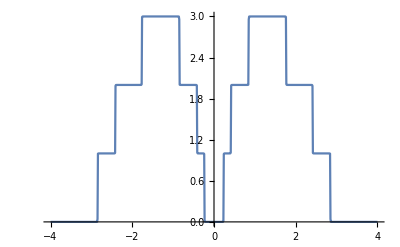

```mathematica
ListLinePlot[Table[{ω,Abs[tr[ω,0.001,1,0]]},{ω,Range[-4,4,0.01]}]]
```

```mathematica
PER[ϵ1_,i_]:=Module[{ρ=IdentityMatrix[7]-IdentityMatrix[7]},ReplacePart[ρ,{{i,i}}->ϵ1]]
```

```mathematica
f[k_,ϵ1_,i_]:=Table[{ω,Log[Det[IdentityMatrix[7]-IL[ω,0.001,1,0].PER[ϵ1,i]]]},{ω,Range[-4,k,0.01]}]
```

```mathematica
η[k_,ϵ1_,i_]:=η[k,ϵ1,i]=Im[Integrate[Interpolation[f[k,ϵ1,i]][ω],{ω,-4,k}]]/π
```

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

5

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];m1=Table[{ω,If[ψ[ω,0.001,1,0,0]>3,3,ψ[ω,0.001,1,0,0]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000279995},{0.01,0.0000280805},{0.02,0.000028326},{0.03,0.0000287434},{0.04,0.0000293458},{0.05,0.000030153},{0.06,0.0000311929},{0.07,0.0000325038},{0.08,0.0000341383},{0.09,0.0000361684},{0.1,0.0000386941},{0.11,0.0000418562},{0.12,0.0000458577},{0.13,0.0000509996},{0.14,0.0000577436},{0.15,0.0000668293},{0.16,0.000079504},{0.17,0.0000980155},{0.18,0.000126774},{0.19,0.000175487},{0.2,0.000269296},{0.21,0.000492136},{0.22,0.00128997},{0.23,0.0116162},{0.24,0.991847},{0.25,0.999059},{0.26,0.999686},{0.27,0.999857},{0.28,0.999928},{0.29,0.999963},{0.3,0.999985},{0.31,1.},{0.32,1.00001},{0.33,1.00003},{0.34,1.00004},{0.35,1.00006},{0.36,1.00008},{0.37,1.00013},{0.38,1.00022},{0.39,1.00043},{0.4,1.00124},{0.41,1.01355},{0.42,1.99273},{0.43,1.99901},{0.44,1.99963},{0.45,1.99981},{0.46,1.99988},{0.47,1.99992},{0.48,1.99995},{0.49,1.99996},{0.5,1.99997},{0.51,1.99998},{0.52,1.99998},{0.53,1.99998},{0.54,1.99999},{0.55,1.99999},{0.56,1.99999},{0.57,1.99999},{0.58,1.99999},{0.59,2.},{0.6,2.},{0.61,2.},{0.62,2.},{0.63,2.},{0.64,2.},{0.65,2.},{0.66,2.},{0.67,2.},{0.68,2.00001},{0.69,2.00001},{0.7,2.00001},{0.71,2.00001},{0.72,2.00001},{0.73,2.00001},{0.74,2.00002},{0.75,2.00002},{0.76,2.00003},{0.77,2.00004},{0.78,2.00005},{0.79,2.00007},{0.8,2.00011},{0.81,2.00017},{0.82,2.00032},{0.83,2.00078},{0.84,2.00409},{0.85,2.95656},{0.86,2.99833},{0.87,2.99949},{0.88,2.99976},{0.89,2.99986},{0.9,2.9999},{0.91,2.99993},{0.92,2.99995},{0.93,2.99996},{0.94,2.99997},{0.95,2.99997},{0.96,2.99998},{0.97,2.99998},{0.98,2.99998},{0.99,2.99999},{1.,2.99999},{1.01,2.99999},{1.02,2.99999},{1.03,2.99999},{1.04,2.99999},{1.05,2.99999},{1.06,2.99999},{1.07,2.99999},{1.08,2.99999},{1.09,2.99999},{1.1,2.99999},{1.11,2.99999},{1.12,2.99999},{1.13,2.99999},{1.14,3.},{1.15,3.},{1.16,3.},{1.17,3.},{1.18,3.},{1.19,3.},{1.2,3.},{1.21,3.},{1.22,3.},{1.23,3.},{1.24,3.},{1.25,3.},{1.26,3.},{1.27,3.},{1.28,3.},{1.29,3.},{1.3,3.},{1.31,3.},{1.32,3.},{1.33,3.},{1.34,3.},{1.35,3.},{1.36,3.},{1.37,3.},{1.38,3.},{1.39,3.},{1.4,3.},{1.41,3.},{1.42,3.},{1.43,3.},{1.44,3.},{1.45,3.},{1.46,3.},{1.47,3.},{1.48,2.99999},{1.49,2.99999},{1.5,2.99999},{1.51,2.99999},{1.52,2.99999},{1.53,2.99999},{1.54,2.99999},{1.55,2.99999},{1.56,2.99999},{1.57,2.99999},{1.58,2.99999},{1.59,2.99999},{1.6,2.99999},{1.61,2.99999},{1.62,2.99999},{1.63,2.99998},{1.64,2.99998},{1.65,2.99998},{1.66,2.99998},{1.67,2.99997},{1.68,2.99996},{1.69,2.99995},{1.7,2.99994},{1.71,2.99992},{1.72,2.99988},{1.73,2.9998},{1.74,2.99961},{1.75,2.99894},{1.76,2.99153},{1.77,2.01124},{1.78,2.00116},{1.79,2.00041},{1.8,2.0002},{1.81,2.00012},{1.82,2.00008},{1.83,2.00006},{1.84,2.00004},{1.85,2.00003},{1.86,2.00003},{1.87,2.00002},{1.88,2.00002},{1.89,2.00001},{1.9,2.00001},{1.91,2.00001},{1.92,2.00001},{1.93,2.00001},{1.94,2.00001},{1.95,2.},{1.96,2.},{1.97,2.},{1.98,2.},{1.99,2.},{2.,2.},{2.01,2.},{2.02,2.},{2.03,2.},{2.04,2.},{2.05,2.},{2.06,2.},{2.07,2.},{2.08,2.},{2.09,2.},{2.1,2.},{2.11,2.},{2.12,2.},{2.13,2.},{2.14,2.},{2.15,2.},{2.16,2.},{2.17,2.},{2.18,1.99999},{2.19,1.99999},{2.2,1.99999},{2.21,1.99999},{2.22,1.99999},{2.23,1.99999},{2.24,1.99999},{2.25,1.99999},{2.26,1.99999},{2.27,1.99999},{2.28,1.99998},{2.29,1.99998},{2.3,1.99998},{2.31,1.99997},{2.32,1.99997},{2.33,1.99996},{2.34,1.99995},{2.35,1.99994},{2.36,1.99991},{2.37,1.99987},{2.38,1.99978},{2.39,1.99957},{2.4,1.99875},{2.41,1.98644},{2.42,1.00727},{2.43,1.00099},{2.44,1.00037},{2.45,1.00019},{2.46,1.00011},{2.47,1.00008},{2.48,1.00005},{2.49,1.00004},{2.5,1.00003},{2.51,1.00002},{2.52,1.00002},{2.53,1.00001},{2.54,1.00001},{2.55,1.00001},{2.56,1.00001},{2.57,1.00001},{2.58,1.},{2.59,1.},{2.6,1.},{2.61,1.},{2.62,1.},{2.63,0.999999},{2.64,0.999998},{2.65,0.999996},{2.66,0.999995},{2.67,0.999994},{2.68,0.999993},{2.69,0.999991},{2.7,0.99999},{2.71,0.999988},{2.72,0.999985},{2.73,0.999982},{2.74,0.999979},{2.75,0.999974},{2.76,0.999967},{2.77,0.999958},{2.78,0.999944},{2.79,0.999923},{2.8,0.999888},{2.81,0.999821},{2.82,0.99967},{2.83,0.999199},{2.84,0.995874},{2.85,0.0433182},{2.86,0.00164489},{2.87,0.000496725},{2.88,0.000235194},{2.89,0.000136355},{2.9,0.0000887579},{2.91,0.0000622831},{2.92,0.0000460724},{2.93,0.0000354399},{2.94,0.0000280956},{2.95,0.0000228136},{2.96,0.0000188896},{2.97,0.0000158959},{2.98,0.0000135605},{2.99,0.000011704},{3.,0.000010204},{3.01,8.97489×10^-6},{3.02,7.95521×10^-6},{3.03,7.09997×10^-6},{3.04,6.37564×10^-6},{3.05,5.75681×10^-6},{3.06,5.22393×10^-6},{3.07,4.7618×10^-6},{3.08,4.3584×10^-6},{3.09,4.00418×10^-6},{3.1,3.69145×10^-6},{3.11,3.41396×10^-6},{3.12,3.1666×10^-6},{3.13,2.94516×10^-6},{3.14,2.74612×10^-6},{3.15,2.56655×10^-6},{3.16,2.40399×10^-6},{3.17,2.25635×10^-6},{3.18,2.12186×10^-6},{3.19,1.99898×10^-6},{3.2,1.88643×10^-6},{3.21,1.78306×10^-6},{3.22,1.68791×10^-6},{3.23,1.60011×10^-6},{3.24,1.51894×10^-6},{3.25,1.44374×10^-6},{3.26,1.37393×10^-6},{3.27,1.30901×10^-6},{3.28,1.24853×10^-6},{3.29,1.19209×10^-6},{3.3,1.13935×10^-6},{3.31,1.08998×10^-6},{3.32,1.0437×10^-6},{3.33,1.00026×10^-6},{3.34,9.59429×10^-7},{3.35,9.21004×10^-7},{3.36,8.84799×10^-7},{3.37,8.50644×10^-7},{3.38,8.18388×10^-7},{3.39,7.87893×10^-7},{3.4,7.59032×10^-7},{3.41,7.31691×10^-7},{3.42,7.05764×10^-7},{3.43,6.81156×10^-7},{3.44,6.57779×10^-7},{3.45,6.35552×10^-7},{3.46,6.144×10^-7},{3.47,5.94256×10^-7},{3.48,5.75057×10^-7},{3.49,5.56744×10^-7},{3.5,5.39264×10^-7},{3.51,5.22568×10^-7},{3.52,5.06608×10^-7},{3.53,4.91344×10^-7},{3.54,4.76734×10^-7},{3.55,4.62742×10^-7},{3.56,4.49334×10^-7},{3.57,4.36478×10^-7},{3.58,4.24144×10^-7},{3.59,4.12305×10^-7},{3.6,4.00934×10^-7},{3.61,3.90008×10^-7},{3.62,3.79503×10^-7},{3.63,3.69398×10^-7},{3.64,3.59674×10^-7},{3.65,3.50311×10^-7},{3.66,3.41292×10^-7},{3.67,3.32601×10^-7},{3.68,3.24222×10^-7},{3.69,3.1614×10^-7},{3.7,3.08341×10^-7},{3.71,3.00813×10^-7},{3.72,2.93544×10^-7},{3.73,2.86521×10^-7},{3.74,2.79734×10^-7},{3.75,2.73172×10^-7},{3.76,2.66826×10^-7},{3.77,2.60687×10^-7},{3.78,2.54746×10^-7},{3.79,2.48993×10^-7},{3.8,2.43423×10^-7},{3.81,2.38026×10^-7},{3.82,2.32797×10^-7},{3.83,2.27728×10^-7},{3.84,2.22812×10^-7},{3.85,2.18045×10^-7},{3.86,2.13419×10^-7},{3.87,2.0893×10^-7},{3.88,2.04573×10^-7},{3.89,2.00342×10^-7},{3.9,1.96232×10^-7},{3.91,1.92239×10^-7},{3.92,1.88359×10^-7},{3.93,1.84588×10^-7},{3.94,1.80921×10^-7},{3.95,1.77355×10^-7},{3.96,1.73886×10^-7},{3.97,1.70512×10^-7},{3.98,1.67227×10^-7},{3.99,1.6403×10^-7},{4.,1.60918×10^-7}}

Part::partw: Part 2 of #1 does not exist.

Set::shape: Lists {System`ListPlotsDump`labelprims$442648,System`ListPlotsDump`labelingfnprims$442648,System`ListPlotsDump`imagepadding$442648,System`ListPlotsDump`plotrangepadding$442648,System`ListPlotsDump`plotrangeclipping$442648} and {{},All,{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Scaled[0.05]}},True} are not the same shape.

ListPlot::lpn: is not a list of numbers or pairs of numbers.

Set::shape: Lists {System`ListPlotsDump`labelprims$442690,System`ListPlotsDump`labelingfnprims$442690,System`ListPlotsDump`imagepadding$442690,System`ListPlotsDump`plotrangepadding$442690,System`ListPlotsDump`plotrangeclipping$442690} and {{},All,{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Scaled[0.05]}},True} are not the same shape.

ListPlot::lpn: is not a list of numbers or pairs of numbers.

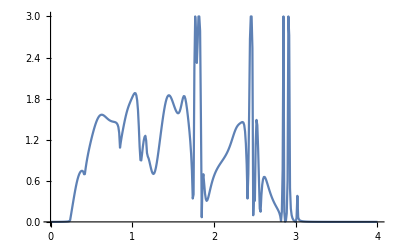
ListPlot[-Graphics-,Joined→True]

```mathematica
ListPlot[%377,Joined->True]
```

```mathematica
ListPlot[%196,Joined->True]
```

ListPlot::lpn: Null is not a list of numbers or pairs of numbers.

ListPlot[Null,Joined→True]

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

7

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];m2=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000229836},{0.01,0.0000191697},{0.02,9.76261×10^-6},{0.03,5.17835×10^-6},{0.04,0.0000257495},{0.05,0.0000522022},{0.06,0.0000849517},{0.07,0.000124597},{0.08,0.00017195},{0.09,0.000228086},{0.1,0.000294406},{0.11,0.000372738},{0.12,0.000465476},{0.13,0.000575791},{0.14,0.000707946},{0.15,0.000867793},{0.16,0.00106358},{0.17,0.00130734},{0.18,0.00161736},{0.19,0.00202311},{0.2,0.00257581},{0.21,0.00337503},{0.22,0.0046513},{0.23,0.00708766},{0.24,0.0462548},{0.25,0.13174},{0.26,0.202491},{0.27,0.263485},{0.28,0.317646},{0.29,0.366876},{0.3,0.412472},{0.31,0.45533},{0.32,0.496061},{0.33,0.535065},{0.34,0.572566},{0.35,0.608641},{0.36,0.643217},{0.37,0.676055},{0.38,0.70668},{0.39,0.73418},{0.4,0.756496},{0.41,0.765986},{0.42,0.812561},{0.43,0.941206},{0.44,1.05991},{0.45,1.16174},{0.46,1.24485},{0.47,1.31009},{0.48,1.35984},{0.49,1.39709},{0.5,1.42484},{0.51,1.44574},{0.52,1.46193},{0.53,1.47511},{0.54,1.48654},{0.55,1.49713},{0.56,1.50754},{0.57,1.51822},{0.58,1.52948},{0.59,1.54151},{0.6,1.5544},{0.61,1.56822},{0.62,1.58295},{0.63,1.59857},{0.64,1.615},{0.65,1.63215},{0.66,1.64992},{0.67,1.66816},{0.68,1.68673},{0.69,1.70543},{0.7,1.72406},{0.71,1.74238},{0.72,1.7601},{0.73,1.77689},{0.74,1.79237},{0.75,1.80608},{0.76,1.81748},{0.77,1.82592},{0.78,1.8306},{0.79,1.83042},{0.8,1.82386},{0.81,1.8084},{0.82,1.77926},{0.83,1.72511},{0.84,1.60626},{0.85,1.28601},{0.86,1.5427},{0.87,1.74972},{0.88,1.91663},{0.89,2.05169},{0.9,2.15993},{0.91,2.24558},{0.92,2.31261},{0.93,2.3649},{0.94,2.40606},{0.95,2.43935},{0.96,2.46763},{0.97,2.49327},{0.98,2.51811},{0.99,2.54318},{1.,2.56824},{1.01,2.59021},{1.02,2.59953},{1.03,2.5706},{1.04,2.43546},{1.05,1.95345},{1.06,0.878998},{1.07,0.938235},{1.08,1.22584},{1.09,1.32582},{1.1,1.20747},{1.11,0.924834},{1.12,0.638795},{1.13,0.68278},{1.14,1.04055},{1.15,1.12376},{1.16,1.19827},{1.17,1.28821},{1.18,1.38276},{1.19,1.47633},{1.2,1.56687},{1.21,1.65374},{1.22,1.73675},{1.23,1.81566},{1.24,1.89012},{1.25,1.95965},{1.26,2.02368},{1.27,2.08174},{1.28,2.1335},{1.29,2.17887},{1.3,2.21807},{1.31,2.25158},{1.32,2.28012},{1.33,2.30457},{1.34,2.32586},{1.35,2.34493},{1.36,2.36265},{1.37,2.37979},{1.38,2.39703},{1.39,2.41495},{1.4,2.43403},{1.41,2.45467},{1.42,2.47721},{1.43,2.50188},{1.44,2.52879},{1.45,2.55785},{1.46,2.58865},{1.47,2.62026},{1.48,2.65109},{1.49,2.67865},{1.5,2.69959},{1.51,2.71},{1.52,2.70608},{1.53,2.68525},{1.54,2.64709},{1.55,2.59375},{1.56,2.5294},{1.57,2.45907},{1.58,2.38749},{1.59,2.3183},{1.6,2.25388},{1.61,2.19544},{1.62,2.14339},{1.63,2.09761},{1.64,2.05767},{1.65,2.023},{1.66,1.99296},{1.67,1.9668},{1.68,1.94362},{1.69,1.92212},{1.7,1.90017},{1.71,1.87376},{1.72,1.83463},{1.73,1.76458},{1.74,1.62181},{1.75,1.30978},{1.76,0.600835},{1.77,0.0882667},{1.78,1.23832},{1.79,3},{1.8,3},{1.81,1.10799},{1.82,0.219462},{1.83,0.690776},{1.84,0.816422},{1.85,0.608135},{1.86,1.39295},{1.87,1.50196},{1.88,1.47711},{1.89,1.46399},{1.9,1.45769},{1.91,1.45509},{1.92,1.45498},{1.93,1.45693},{1.94,1.4608},{1.95,1.46657},{1.96,1.47428},{1.97,1.48397},{1.98,1.49568},{1.99,1.50944},{2.,1.52524},{2.01,1.54305},{2.02,1.5628},{2.03,1.58438},{2.04,1.6076},{2.05,1.63224},{2.06,1.658},{2.07,1.6845},{2.08,1.71131},{2.09,1.73791},{2.1,1.76375},{2.11,1.78825},{2.12,1.81082},{2.13,1.83086},{2.14,1.84786},{2.15,1.86136},{2.16,1.87095},{2.17,1.87635},{2.18,1.87732},{2.19,1.87368},{2.2,1.86527},{2.21,1.85192},{2.22,1.83346},{2.23,1.80967},{2.24,1.78035},{2.25,1.74532},{2.26,1.70453},{2.27,1.65806},{2.28,1.60629},{2.29,1.54986},{2.3,1.48971},{2.31,1.42704},{2.32,1.36317},{2.33,1.29943},{2.34,1.23694},{2.35,1.17643},{2.36,1.11805},{2.37,1.06109},{2.38,1.00344},{2.39,0.940328},{2.4,0.86057},{2.41,0.732364},{2.42,0.346665},{2.43,3},{2.44,0.234097},{2.45,0.378191},{2.46,0.0074039},{2.47,2.29356},{2.48,1.81073},{2.49,0.502693},{2.5,0.830467},{2.51,0.918181},{2.52,0.951749},{2.53,0.967577},{2.54,0.976133},{2.55,0.981214},{2.56,0.984432},{2.57,0.98655},{2.58,0.987965},{2.59,0.988892},{2.6,0.989457},{2.61,0.989732},{2.62,0.989759},{2.63,0.989557},{2.64,0.989135},{2.65,0.988487},{2.66,0.987601},{2.67,0.986457},{2.68,0.985033},{2.69,0.983304},{2.7,0.981249},{2.71,0.978855},{2.72,0.976122},{2.73,0.973074},{2.74,0.969767},{2.75,0.966305},{2.76,0.962851},{2.77,0.959644},{2.78,0.957024},{2.79,0.955439},{2.8,0.955456},{2.81,0.957699},{2.82,0.962511},{2.83,0.967983},{2.84,0.949498},{2.85,0.0168586},{2.86,0.0000355775},{2.87,0.0000490963},{2.88,0.0000948856},{2.89,0.00028393},{2.9,0.000700224},{2.91,0.00396125},{2.92,0.00169398},{2.93,0.00010318},{2.94,0.000134677},{2.95,0.00011268},{2.96,0.0000909741},{2.97,0.0000736759},{2.98,0.0000602264},{2.99,0.0000497108},{3.,0.0000413925},{3.01,0.0000347314},{3.02,0.0000293367},{3.03,0.0000249233},{3.04,0.0000212803},{3.05,0.0000182495},{3.06,0.0000157103},{3.07,0.0000135698},{3.08,0.0000117551},{3.09,0.0000102091},{3.1,8.88602×10^-6},{3.11,7.74905×10^-6},{3.12,6.76837×10^-6},{3.13,5.91964×10^-6},{3.14,5.18281×10^-6},{3.15,4.54132×10^-6},{3.16,3.98138×10^-6},{3.17,3.49143×10^-6},{3.18,3.0618×10^-6},{3.19,2.68428×10^-6},{3.2,2.35195×10^-6},{3.21,2.05889×10^-6},{3.22,1.80005×10^-6},{3.23,1.57112×10^-6},{3.24,1.36838×10^-6},{3.25,1.18862×10^-6},{3.26,1.02906×10^-6},{3.27,8.87301×10^-7},{3.28,7.61256×10^-7},{3.29,6.49102×10^-7},{3.3,5.49247×10^-7},{3.31,4.603×10^-7},{3.32,3.81038×10^-7},{3.33,3.1039×10^-7},{3.34,2.47411×10^-7},{3.35,1.91267×10^-7},{3.36,1.41223×10^-7},{3.37,9.66277×10^-8},{3.38,5.69047×10^-8},{3.39,2.15419×10^-8},{3.4,9.91562×10^-9},{3.41,3.78725×10^-8},{3.42,6.26894×10^-8},{3.43,8.46878×10^-8},{3.44,1.04155×10^-7},{3.45,1.21348×10^-7},{3.46,1.36496×10^-7},{3.47,1.49805×10^-7},{3.48,1.6146×10^-7},{3.49,1.71627×10^-7},{3.5,1.80453×10^-7},{3.51,1.88074×10^-7},{3.52,1.94609×10^-7},{3.53,2.00166×10^-7},{3.54,2.04844×10^-7},{3.55,2.0873×10^-7},{3.56,2.11904×10^-7},{3.57,2.14437×10^-7},{3.58,2.16395×10^-7},{3.59,2.17835×10^-7},{3.6,2.1881×10^-7},{3.61,2.19369×10^-7},{3.62,2.19554×10^-7},{3.63,2.19405×10^-7},{3.64,2.18958×10^-7},{3.65,2.18243×10^-7},{3.66,2.17291×10^-7},{3.67,2.16128×10^-7},{3.68,2.14777×10^-7},{3.69,2.13261×10^-7},{3.7,2.11598×10^-7},{3.71,2.09808×10^-7},{3.72,2.07904×10^-7},{3.73,2.05904×10^-7},{3.74,2.03818×10^-7},{3.75,2.0166×10^-7},{3.76,1.99441×10^-7},{3.77,1.97169×10^-7},{3.78,1.94855×10^-7},{3.79,1.92506×10^-7},{3.8,1.90129×10^-7},{3.81,1.8773×10^-7},{3.82,1.85317×10^-7},{3.83,1.82893×10^-7},{3.84,1.80465×10^-7},{3.85,1.78035×10^-7},{3.86,1.75609×10^-7},{3.87,1.73188×10^-7},{3.88,1.70778×10^-7},{3.89,1.6838×10^-7},{3.9,1.65997×10^-7},{3.91,1.6363×10^-7},{3.92,1.61283×10^-7},{3.93,1.58956×10^-7},{3.94,1.56652×10^-7},{3.95,1.54371×10^-7},{3.96,1.52114×10^-7},{3.97,1.49884×10^-7},{3.98,1.4768×10^-7},{3.99,1.45503×10^-7},{4.,1.43353×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

2

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];m3=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,7.94274×10^-6},{0.01,0.0000116936},{0.02,0.0000374002},{0.03,0.0000695243},{0.04,0.000108516},{0.05,0.00015495},{0.06,0.000209551},{0.07,0.000273227},{0.08,0.000347104},{0.09,0.000432584},{0.1,0.00053141},{0.11,0.000645755},{0.12,0.000778355},{0.13,0.000932671},{0.14,0.00111314},{0.15,0.00132555},{0.16,0.00157751},{0.17,0.00187935},{0.18,0.00224541},{0.19,0.00269632},{0.2,0.00326309},{0.21,0.00399509},{0.22,0.00497355},{0.23,0.00618952},{0.24,0.0598049},{0.25,0.177591},{0.26,0.287597},{0.27,0.389548},{0.28,0.483073},{0.29,0.567765},{0.3,0.643259},{0.31,0.70929},{0.32,0.765733},{0.33,0.812605},{0.34,0.85004},{0.35,0.878222},{0.36,0.897259},{0.37,0.906934},{0.38,0.906187},{0.39,0.891715},{0.4,0.852831},{0.41,0.735342},{0.42,0.64661},{0.43,0.858148},{0.44,1.01812},{0.45,1.14349},{0.46,1.24484},{0.47,1.32874},{0.48,1.39954},{0.49,1.4603},{0.5,1.51319},{0.51,1.55981},{0.52,1.60133},{0.53,1.63864},{0.54,1.67238},{0.55,1.70302},{0.56,1.73089},{0.57,1.75623},{0.58,1.7792},{0.59,1.79991},{0.6,1.81843},{0.61,1.83482},{0.62,1.84914},{0.63,1.86146},{0.64,1.87185},{0.65,1.8804},{0.66,1.88724},{0.67,1.8925},{0.68,1.89632},{0.69,1.89886},{0.7,1.90028},{0.71,1.9007},{0.72,1.90026},{0.73,1.89905},{0.74,1.89709},{0.75,1.89437},{0.76,1.89077},{0.77,1.88606},{0.78,1.8798},{0.79,1.87128},{0.8,1.85927},{0.81,1.84155},{0.82,1.81369},{0.83,1.76512},{0.84,1.65967},{0.85,1.36848},{0.86,1.55217},{0.87,1.70454},{0.88,1.83435},{0.89,1.94775},{0.9,2.04691},{0.91,2.13248},{0.92,2.20464},{0.93,2.26367},{0.94,2.3103},{0.95,2.34585},{0.96,2.3722},{0.97,2.39166},{0.98,2.40681},{0.99,2.42038},{1.,2.43496},{1.01,2.45246},{1.02,2.47118},{1.03,2.4717},{1.04,2.35352},{1.05,1.845},{1.06,1.27697},{1.07,1.5238},{1.08,1.43686},{1.09,1.17312},{1.1,1.07288},{1.11,1.15838},{1.12,1.31161},{1.13,1.47221},{1.14,1.6022},{1.15,1.62801},{1.16,1.65679},{1.17,1.70347},{1.18,1.75091},{1.19,1.79542},{1.2,1.83707},{1.21,1.87663},{1.22,1.91489},{1.23,1.95254},{1.24,1.99016},{1.25,2.02819},{1.26,2.06693},{1.27,2.10655},{1.28,2.14699},{1.29,2.18796},{1.3,2.22884},{1.31,2.2686},{1.32,2.30583},{1.33,2.33871},{1.34,2.36519},{1.35,2.38327},{1.36,2.39133},{1.37,2.38845},{1.38,2.37468},{1.39,2.35103},{1.4,2.31924},{1.41,2.28152},{1.42,2.24012},{1.43,2.19707},{1.44,2.15408},{1.45,2.11244},{1.46,2.07305},{1.47,2.03655},{1.48,2.00334},{1.49,1.97372},{1.5,1.9479},{1.51,1.92608},{1.52,1.90847},{1.53,1.89535},{1.54,1.88705},{1.55,1.88397},{1.56,1.88654},{1.57,1.89523},{1.58,1.91043},{1.59,1.93233},{1.6,1.96081},{1.61,1.99516},{1.62,2.03394},{1.63,2.07486},{1.64,2.11493},{1.65,2.15093},{1.66,2.18013},{1.67,2.20109},{1.68,2.2143},{1.69,2.22237},{1.7,2.2301},{1.71,2.24434},{1.72,2.27381},{1.73,2.32691},{1.74,2.40018},{1.75,2.43412},{1.76,2.16409},{1.77,0.300992},{1.78,2.2972},{1.79,3},{1.8,1.14621},{1.81,0.312467},{1.82,0.551858},{1.83,0.596544},{1.84,0.9058},{1.85,1.19286},{1.86,1.38197},{1.87,1.50085},{1.88,1.5765},{1.89,1.62557},{1.9,1.65794},{1.91,1.67965},{1.92,1.69451},{1.93,1.70504},{1.94,1.713},{1.95,1.7196},{1.96,1.72573},{1.97,1.73206},{1.98,1.73908},{1.99,1.74716},{2.,1.75656},{2.01,1.76747},{2.02,1.77997},{2.03,1.79406},{2.04,1.80966},{2.05,1.82656},{2.06,1.84442},{2.07,1.86276},{2.08,1.88097},{2.09,1.89828},{2.1,1.91381},{2.11,1.9266},{2.12,1.9357},{2.13,1.94028},{2.14,1.93972},{2.15,1.9337},{2.16,1.92227},{2.17,1.90587},{2.18,1.88527},{2.19,1.86151},{2.2,1.83575},{2.21,1.80916},{2.22,1.78288},{2.23,1.75787},{2.24,1.73495},{2.25,1.71474},{2.26,1.69763},{2.27,1.68382},{2.28,1.6732},{2.29,1.66531},{2.3,1.65914},{2.31,1.65294},{2.32,1.64388},{2.33,1.62793},{2.34,1.59992},{2.35,1.5542},{2.36,1.4857},{2.37,1.39045},{2.38,1.26359},{2.39,1.09116},{2.4,0.820591},{2.41,0.143966},{2.42,3},{2.43,1.47929},{2.44,0.229874},{2.45,0.0968732},{2.46,0.368611},{2.47,1.1398},{2.48,2.04089},{2.49,0.954318},{2.5,0.142671},{2.51,0.560786},{2.52,0.719459},{2.53,0.784686},{2.54,0.811654},{2.55,0.8211},{2.56,0.821939},{2.57,0.818477},{2.58,0.813023},{2.59,0.80693},{2.6,0.801059},{2.61,0.795998},{2.62,0.792168},{2.63,0.789877},{2.64,0.789344},{2.65,0.790701},{2.66,0.793985},{2.67,0.799116},{2.68,0.805854},{2.69,0.813753},{2.7,0.8221},{2.71,0.829859},{2.72,0.83563},{2.73,0.837667},{2.74,0.833984},{2.75,0.822577},{2.76,0.801764},{2.77,0.770549},{2.78,0.728868},{2.79,0.677554},{2.8,0.6179},{2.81,0.550745},{2.82,0.474757},{2.83,0.382141},{2.84,0.240625},{2.85,0.0845865},{2.86,1.16186},{2.87,0.0406778},{2.88,0.00487094},{2.89,0.000335625},{2.9,0.00744226},{2.91,0.064467},{2.92,2.34814},{2.93,0.361057},{2.94,0.0819756},{2.95,0.0379349},{2.96,0.0224002},{2.97,0.0149319},{2.98,0.0106969},{2.99,0.00803662},{3.,0.00624582},{3.01,0.00497866},{3.02,0.00404771},{3.03,0.00334345},{3.04,0.002798},{3.05,0.00236734},{3.06,0.00202179},{3.07,0.00174071},{3.08,0.00150937},{3.09,0.00131701},{3.1,0.0011556},{3.11,0.00101908},{3.12,0.000902791},{3.13,0.000803086},{3.14,0.000717103},{3.15,0.000642559},{3.16,0.000577617},{3.17,0.000520786},{3.18,0.00047085},{3.19,0.000426802},{3.2,0.000387811},{3.21,0.000353181},{3.22,0.00032233},{3.23,0.000294765},{3.24,0.000270069},{3.25,0.000247887},{3.26,0.000227914},{3.27,0.000209889},{3.28,0.000193586},{3.29,0.000178811},{3.3,0.000165395},{3.31,0.000153189},{3.32,0.000142065},{3.33,0.000131909},{3.34,0.000122623},{3.35,0.000114119},{3.36,0.000106318},{3.37,0.0000991539},{3.38,0.0000925645},{3.39,0.000086496},{3.4,0.0000809002},{3.41,0.0000757339},{3.42,0.0000709586},{3.43,0.0000665398},{3.44,0.0000624464},{3.45,0.0000586504},{3.46,0.0000551267},{3.47,0.0000518525},{3.48,0.0000488073},{3.49,0.0000459724},{3.5,0.000043331},{3.51,0.0000408677},{3.52,0.0000385686},{3.53,0.0000364211},{3.54,0.0000344135},{3.55,0.0000325353},{3.56,0.0000307768},{3.57,0.0000291293},{3.58,0.0000275846},{3.59,0.0000261354},{3.6,0.0000247748},{3.61,0.0000234965},{3.62,0.000022295},{3.63,0.0000211647},{3.64,0.000020101},{3.65,0.0000190992},{3.66,0.0000181552},{3.67,0.0000172652},{3.68,0.0000164257},{3.69,0.0000156334},{3.7,0.0000148852},{3.71,0.0000141783},{3.72,0.0000135101},{3.73,0.0000128781},{3.74,0.0000122802},{3.75,0.0000117143},{3.76,0.0000111783},{3.77,0.0000106705},{3.78,0.0000101891},{3.79,9.7327×10^-6},{3.8,9.2997×10^-6},{3.81,8.88876×10^-6},{3.82,8.4986×10^-6},{3.83,8.12803×10^-6},{3.84,7.77593×10^-6},{3.85,7.44125×10^-6},{3.86,7.12301×10^-6},{3.87,6.82029×10^-6},{3.88,6.53223×10^-6},{3.89,6.25804×10^-6},{3.9,5.99694×10^-6},{3.91,5.74823×10^-6},{3.92,5.51125×10^-6},{3.93,5.28536×10^-6},{3.94,5.06999×10^-6},{3.95,4.86457×10^-6},{3.96,4.66858×10^-6},{3.97,4.48155×10^-6},{3.98,4.30299×10^-6},{3.99,4.13248×10^-6},{4.,3.96962×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

4

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];m4=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000469532},{0.01,0.0000262171},{0.02,0.000016737},{0.03,0.0000174612},{0.04,0.000027706},{0.05,0.0000470975},{0.06,0.0000755373},{0.07,0.000113188},{0.08,0.000160478},{0.09,0.00021812},{0.1,0.000287157},{0.11,0.000369025},{0.12,0.000465665},{0.13,0.000579671},{0.14,0.000714534},{0.15,0.000875008},{0.16,0.00106769},{0.17,0.00130201},{0.18,0.00159189},{0.19,0.00195903},{0.2,0.00243945},{0.21,0.00309896},{0.22,0.00407603},{0.23,0.00567648},{0.24,0.0433674},{0.25,0.136117},{0.26,0.228187},{0.27,0.318849},{0.28,0.406742},{0.29,0.490107},{0.3,0.567008},{0.31,0.635585},{0.32,0.694314},{0.33,0.742214},{0.34,0.778969},{0.35,0.804925},{0.36,0.820995},{0.37,0.82849},{0.38,0.828933},{0.39,0.823897},{0.4,0.814914},{0.41,0.804028},{0.42,0.937512},{0.43,1.11817},{0.44,1.24587},{0.45,1.33785},{0.46,1.40515},{0.47,1.455},{0.48,1.49231},{0.49,1.5205},{0.5,1.54203},{0.51,1.55868},{0.52,1.57179},{0.53,1.58235},{0.54,1.59113},{0.55,1.59872},{0.56,1.60557},{0.57,1.61204},{0.58,1.61842},{0.59,1.6249},{0.6,1.63167},{0.61,1.63882},{0.62,1.64644},{0.63,1.65454},{0.64,1.66312},{0.65,1.67214},{0.66,1.68149},{0.67,1.69108},{0.68,1.70073},{0.69,1.71027},{0.7,1.71949},{0.71,1.72815},{0.72,1.73601},{0.73,1.74281},{0.74,1.74828},{0.75,1.75214},{0.76,1.75404},{0.77,1.75356},{0.78,1.7501},{0.79,1.7427},{0.8,1.72971},{0.81,1.70806},{0.82,1.67131},{0.83,1.60359},{0.84,1.45008},{0.85,0.941144},{0.86,0.977441},{0.87,1.05066},{0.88,1.14213},{0.89,1.25059},{0.9,1.37374},{0.91,1.50855},{0.92,1.65159},{0.93,1.79936},{0.94,1.94843},{0.95,2.09552},{0.96,2.23741},{0.97,2.37071},{0.98,2.49145},{0.99,2.5945},{1.,2.67288},{1.01,2.71742},{1.02,2.718},{1.03,2.66869},{1.04,2.56337},{1.05,2.06822},{1.06,1.20881},{1.07,0.895445},{1.08,0.846394},{1.09,0.851482},{1.1,0.921384},{1.11,1.03755},{1.12,1.17519},{1.13,1.3187},{1.14,1.46243},{1.15,1.60635},{1.16,1.75211},{1.17,1.90045},{1.18,2.04991},{1.19,2.19636},{1.2,2.33346},{1.21,2.45402},{1.22,2.55179},{1.23,2.62305},{1.24,2.66728},{1.25,2.68685},{1.26,2.68604},{1.27,2.6699},{1.28,2.64332},{1.29,2.61054},{1.3,2.57493},{1.31,2.539},{1.32,2.5045},{1.33,2.4726},{1.34,2.44402},{1.35,2.41916},{1.36,2.39817},{1.37,2.38106},{1.38,2.36777},{1.39,2.35817},{1.4,2.35209},{1.41,2.3494},{1.42,2.34997},{1.43,2.35371},{1.44,2.36057},{1.45,2.37056},{1.46,2.38375},{1.47,2.40026},{1.48,2.42034},{1.49,2.44426},{1.5,2.47242},{1.51,2.50525},{1.52,2.5432},{1.53,2.58661},{1.54,2.63552},{1.55,2.6893},{1.56,2.74621},{1.57,2.80275},{1.58,2.85326},{1.59,2.89017},{1.6,2.9055},{1.61,2.8934},{1.62,2.85263},{1.63,2.78708},{1.64,2.70402},{1.65,2.61111},{1.66,2.51426},{1.67,2.41678},{1.68,2.31949},{1.69,2.22123},{1.7,2.11921},{1.71,2.00905},{1.72,1.88436},{1.73,1.73548},{1.74,1.54585},{1.75,1.2775},{1.76,0.771573},{1.77,0.316029},{1.78,3},{1.79,3},{1.8,2.42397},{1.81,1.04436},{1.82,0.629235},{1.83,0.684862},{1.84,1.19086},{1.85,1.48413},{1.86,0.503816},{1.87,1.47162},{1.88,1.64206},{1.89,1.6564},{1.9,1.64264},{1.91,1.62601},{1.92,1.61169},{1.93,1.60048},{1.94,1.5922},{1.95,1.58652},{1.96,1.58316},{1.97,1.58191},{1.98,1.58264},{1.99,1.58523},{2.,1.58964},{2.01,1.59582},{2.02,1.60374},{2.03,1.61335},{2.04,1.62462},{2.05,1.63749},{2.06,1.65188},{2.07,1.66768},{2.08,1.68476},{2.09,1.70295},{2.1,1.72203},{2.11,1.74175},{2.12,1.76181},{2.13,1.78188},{2.14,1.80156},{2.15,1.82045},{2.16,1.8381},{2.17,1.85404},{2.18,1.86782},{2.19,1.87897},{2.2,1.88706},{2.21,1.89167},{2.22,1.89247},{2.23,1.88918},{2.24,1.88161},{2.25,1.86968},{2.26,1.85341},{2.27,1.83295},{2.28,1.80858},{2.29,1.78068},{2.3,1.74977},{2.31,1.71642},{2.32,1.68128},{2.33,1.64502},{2.34,1.60823},{2.35,1.57141},{2.36,1.53475},{2.37,1.49785},{2.38,1.45883},{2.39,1.41148},{2.4,1.33117},{2.41,0.997823},{2.42,0.49858},{2.43,0.675128},{2.44,0.687197},{2.45,0.618634},{2.46,0.308726},{2.47,2.25965},{2.48,0.787461},{2.49,0.940945},{2.5,0.941523},{2.51,0.931413},{2.52,0.921457},{2.53,0.912936},{2.54,0.905942},{2.55,0.900442},{2.56,0.896434},{2.57,0.893951},{2.58,0.89305},{2.59,0.89379},{2.6,0.896216},{2.61,0.900336},{2.62,0.906093},{2.63,0.913336},{2.64,0.921777},{2.65,0.930935},{2.66,0.940083},{2.67,0.94818},{2.68,0.953827},{2.69,0.955255},{2.7,0.950398},{2.71,0.937077},{2.72,0.913325},{2.73,0.877807},{2.74,0.830234},{2.75,0.771599},{2.76,0.704082},{2.77,0.630618},{2.78,0.554245},{2.79,0.477429},{2.8,0.401511},{2.81,0.326219},{2.82,0.248934},{2.83,0.16278},{2.84,0.0499504},{2.85,0.134623},{2.86,0.52191},{2.87,3},{2.88,0.620158},{2.89,0.0860018},{2.9,0.00331991},{2.91,0.202513},{2.92,0.443938},{2.93,0.100796},{2.94,0.0506524},{2.95,0.0317062},{2.96,0.0219984},{2.97,0.0162154},{2.98,0.0124453},{2.99,0.00983435},{3.,0.0079457},{3.01,0.0065336},{3.02,0.00544992},{3.03,0.0046005},{3.04,0.00392293},{3.05,0.00337436},{3.06,0.00292455},{3.07,0.00255165},{3.08,0.0022395},{3.09,0.00197596},{3.1,0.00175175},{3.11,0.0015597},{3.12,0.00139418},{3.13,0.00125072},{3.14,0.00112573},{3.15,0.00101634},{3.16,0.000920171},{3.17,0.000835297},{3.18,0.000760112},{3.19,0.00069328},{3.2,0.000633684},{3.21,0.000580381},{3.22,0.000532572},{3.23,0.000489578},{3.24,0.000450819},{3.25,0.000415795},{3.26,0.000384077},{3.27,0.000355293},{3.28,0.000329119},{3.29,0.000305274},{3.3,0.000283512},{3.31,0.000263618},{3.32,0.000245401},{3.33,0.000228694},{3.34,0.00021335},{3.35,0.000199236},{3.36,0.000186238},{3.37,0.000174251},{3.38,0.000163182},{3.39,0.000152949},{3.4,0.000143479},{3.41,0.000134703},{3.42,0.000126564},{3.43,0.000119006},{3.44,0.000111982},{3.45,0.000105446},{3.46,0.0000993608},{3.47,0.0000936887},{3.48,0.0000883975},{3.49,0.0000834574},{3.5,0.0000788413},{3.51,0.0000745246},{3.52,0.0000704847},{3.53,0.0000667012},{3.54,0.000063155},{3.55,0.0000598291},{3.56,0.0000567076},{3.57,0.000053776},{3.58,0.0000510209},{3.59,0.0000484301},{3.6,0.0000459924},{3.61,0.0000436972},{3.62,0.000041535},{3.63,0.0000394969},{3.64,0.0000375748},{3.65,0.000035761},{3.66,0.0000340486},{3.67,0.000032431},{3.68,0.0000309023},{3.69,0.0000294568},{3.7,0.0000280893},{3.71,0.0000267951},{3.72,0.0000255696},{3.73,0.0000244087},{3.74,0.0000233084},{3.75,0.0000222652},{3.76,0.0000212757},{3.77,0.0000203367},{3.78,0.0000194453},{3.79,0.0000185987},{3.8,0.0000177944},{3.81,0.00001703},{3.82,0.0000163032},{3.83,0.0000156119},{3.84,0.0000149542},{3.85,0.0000143281},{3.86,0.000013732},{3.87,0.0000131642},{3.88,0.0000126233},{3.89,0.0000121077},{3.9,0.0000116161},{3.91,0.0000111472},{3.92,0.0000107},{3.93,0.0000102731},{3.94,9.86565×10^-6},{3.95,9.47657×10^-6},{3.96,9.10494×10^-6},{3.97,8.74986×10^-6},{3.98,8.41052×10^-6},{3.99,8.08611×10^-6},{4.,7.77591×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

1

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];m5=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000279063},{0.01,0.0000188465},{0.02,0.0000123091},{0.03,0.0000645607},{0.04,0.000137896},{0.05,0.000233234},{0.06,0.000352446},{0.07,0.000498449},{0.08,0.00067539},{0.09,0.000888934},{0.1,0.0011467},{0.11,0.0014589},{0.12,0.00183931},{0.13,0.00230671},{0.14,0.00288713},{0.15,0.00361738},{0.16,0.00455098},{0.17,0.00576829},{0.18,0.00739525},{0.19,0.00964049},{0.2,0.0128773},{0.21,0.0178548},{0.22,0.0263989},{0.23,0.045429},{0.24,0.0506346},{0.25,0.00485641},{0.26,0.0400358},{0.27,0.0848615},{0.28,0.130129},{0.29,0.176024},{0.3,0.222446},{0.31,0.269006},{0.32,0.314992},{0.33,0.359328},{0.34,0.400515},{0.35,0.436519},{0.36,0.464539},{0.37,0.48044},{0.38,0.477265},{0.39,0.440761},{0.4,0.331735},{0.41,0.0452617},{0.42,0.18792},{0.43,0.469758},{0.44,0.848287},{0.45,1.09956},{0.46,1.27951},{0.47,1.41431},{0.48,1.51822},{0.49,1.59988},{0.5,1.66497},{0.51,1.71742},{0.52,1.76004},{0.53,1.79491},{0.54,1.82357},{0.55,1.84715},{0.56,1.86648},{0.57,1.88216},{0.58,1.89459},{0.59,1.90402},{0.6,1.9106},{0.61,1.91439},{0.62,1.91539},{0.63,1.9136},{0.64,1.90899},{0.65,1.90158},{0.66,1.8914},{0.67,1.87854},{0.68,1.86311},{0.69,1.84529},{0.7,1.82528},{0.71,1.80328},{0.72,1.77949},{0.73,1.75407},{0.74,1.7271},{0.75,1.69854},{0.76,1.66818},{0.77,1.63553},{0.78,1.59969},{0.79,1.55909},{0.8,1.51094},{0.81,1.45007},{0.82,1.366},{0.83,1.23342},{0.84,0.965706},{0.85,0.155661},{0.86,0.316325},{0.87,0.496189},{0.88,0.667122},{0.89,0.829805},{0.9,0.98427},{0.91,1.13039},{0.92,1.26823},{0.93,1.3981},{0.94,1.52062},{0.95,1.63662},{0.96,1.74713},{0.97,1.85338},{0.98,1.95673},{0.99,2.05867},{1.,2.16066},{1.01,2.26362},{1.02,2.36591},{1.03,2.45539},{1.04,2.47776},{1.05,2.25799},{1.06,1.81688},{1.07,1.64278},{1.08,1.70858},{1.09,1.77762},{1.1,1.72127},{1.11,1.44731},{1.12,0.934941},{1.13,0.552969},{1.14,0.702082},{1.15,1.1142},{1.16,1.49073},{1.17,1.76336},{1.18,1.94795},{1.19,2.0696},{1.2,2.14765},{1.21,2.19558},{1.22,2.22277},{1.23,2.23595},{1.24,2.23996},{1.25,2.23836},{1.26,2.23369},{1.27,2.22779},{1.28,2.2219},{1.29,2.21685},{1.3,2.2131},{1.31,2.21089},{1.32,2.21023},{1.33,2.211},{1.34,2.21295},{1.35,2.21579},{1.36,2.21917},{1.37,2.22278},{1.38,2.22632},{1.39,2.22958},{1.4,2.23246},{1.41,2.23494},{1.42,2.23716},{1.43,2.23934},{1.44,2.24185},{1.45,2.24514},{1.46,2.24976},{1.47,2.25632},{1.48,2.26548},{1.49,2.27791},{1.5,2.29422},{1.51,2.31489},{1.52,2.34009},{1.53,2.36938},{1.54,2.40135},{1.55,2.43312},{1.56,2.45999},{1.57,2.47562},{1.58,2.4733},{1.59,2.44835},{1.6,2.40051},{1.61,2.33457},{1.62,2.25844},{1.63,2.18007},{1.64,2.10523},{1.65,2.03684},{1.66,1.97542},{1.67,1.91984},{1.68,1.86789},{1.69,1.81644},{1.7,1.76124},{1.71,1.69597},{1.72,1.61007},{1.73,1.48313},{1.74,1.26765},{1.75,0.818414},{1.76,0.667847},{1.77,3},{1.78,3},{1.79,1.34837},{1.8,0.554744},{1.81,0.943437},{1.82,1.0153},{1.83,0.961856},{1.84,0.770763},{1.85,0.51197},{1.86,0.834459},{1.87,1.39289},{1.88,1.62604},{1.89,1.71405},{1.9,1.75581},{1.91,1.7818},{1.92,1.80197},{1.93,1.81989},{1.94,1.83692},{1.95,1.85353},{1.96,1.86981},{1.97,1.88565},{1.98,1.90088},{1.99,1.91524},{2.,1.92848},{2.01,1.94034},{2.02,1.95057},{2.03,1.95896},{2.04,1.96534},{2.05,1.96959},{2.06,1.97165},{2.07,1.97151},{2.08,1.96925},{2.09,1.96499},{2.1,1.95891},{2.11,1.95124},{2.12,1.94223},{2.13,1.93219},{2.14,1.9214},{2.15,1.91015},{2.16,1.89872},{2.17,1.88734},{2.18,1.87619},{2.19,1.86539},{2.2,1.85497},{2.21,1.84486},{2.22,1.83487},{2.23,1.82471},{2.24,1.81395},{2.25,1.80207},{2.26,1.78846},{2.27,1.7725},{2.28,1.75363},{2.29,1.73144},{2.3,1.70574},{2.31,1.67669},{2.32,1.64475},{2.33,1.61069},{2.34,1.57546},{2.35,1.53999},{2.36,1.50497},{2.37,1.47037},{2.38,1.43453},{2.39,1.39131},{2.4,1.31706},{2.41,1.03501},{2.42,0.224187},{2.43,0.79341},{2.44,0.640932},{2.45,0.461968},{2.46,2.2425},{2.47,0.426483},{2.48,0.780469},{2.49,0.878615},{2.5,0.917986},{2.51,0.935971},{2.52,0.943549},{2.53,0.944938},{2.54,0.942137},{2.55,0.936316},{2.56,0.928305},{2.57,0.918787},{2.58,0.908379},{2.59,0.897657},{2.6,0.887162},{2.61,0.877394},{2.62,0.868809},{2.63,0.861805},{2.64,0.856718},{2.65,0.853804},{2.66,0.853227},{2.67,0.855025},{2.68,0.859077},{2.69,0.865043},{2.7,0.872288},{2.71,0.879798},{2.72,0.886089},{2.73,0.889156},{2.74,0.886517},{2.75,0.875426},{2.76,0.853297},{2.77,0.818314},{2.78,0.770017},{2.79,0.709562},{2.8,0.639354},{2.81,0.561953},{2.82,0.478111},{2.83,0.382627},{2.84,0.24845},{2.85,0.0151794},{2.86,0.0391041},{2.87,0.00148643},{2.88,0.000409955},{2.89,0.000223806},{2.9,0.000375997},{2.91,0.00808021},{2.92,0.00111514},{2.93,0.000224193},{2.94,0.0000918948},{2.95,0.0000472815},{2.96,0.0000269102},{2.97,0.0000160828},{2.98,9.80637×10^-6},{2.99,5.97059×10^-6},{3.,3.54898×10^-6},{3.01,1.99164×10^-6},{3.02,9.82827×10^-7},{3.03,3.31655×10^-7},{3.04,8.18602×10^-8},{3.05,3.35453×10^-7},{3.06,4.80683×10^-7},{3.07,5.52377×10^-7},{3.08,5.74396×10^-7},{3.09,5.63258×10^-7},{3.1,5.30479×10^-7},{3.11,4.84125×10^-7},{3.12,4.29845×10^-7},{3.13,3.7159×10^-7},{3.14,3.12099×10^-7},{3.15,2.5325×10^-7},{3.16,1.96302×10^-7},{3.17,1.42071×10^-7},{3.18,9.10557×10^-8},{3.19,4.35267×10^-8},{3.2,4.04442×10^-10},{3.21,4.07392×10^-8},{3.22,7.75564×10^-8},{3.23,1.10987×10^-7},{3.24,1.41194×10^-7},{3.25,1.68361×10^-7},{3.26,1.92682×10^-7},{3.27,2.14352×10^-7},{3.28,2.33566×10^-7},{3.29,2.50512×10^-7},{3.3,2.65372×10^-7},{3.31,2.78318×10^-7},{3.32,2.89512×10^-7},{3.33,2.99107×10^-7},{3.34,3.07243×10^-7},{3.35,3.14054×10^-7},{3.36,3.1966×10^-7},{3.37,3.24174×10^-7},{3.38,3.277×10^-7},{3.39,3.30334×10^-7},{3.4,3.32162×10^-7},{3.41,3.33266×10^-7},{3.42,3.33717×10^-7},{3.43,3.33584×10^-7},{3.44,3.32927×10^-7},{3.45,3.31803×10^-7},{3.46,3.30262×10^-7},{3.47,3.2835×10^-7},{3.48,3.26111×10^-7},{3.49,3.23582×10^-7},{3.5,3.20798×10^-7},{3.51,3.17791×10^-7},{3.52,3.14591×10^-7},{3.53,3.11222×10^-7},{3.54,3.07709×10^-7},{3.55,3.04072×10^-7},{3.56,3.00333×10^-7},{3.57,2.96508×10^-7},{3.58,2.92612×10^-7},{3.59,2.88661×10^-7},{3.6,2.84668×10^-7},{3.61,2.80643×10^-7},{3.62,2.76598×10^-7},{3.63,2.72541×10^-7},{3.64,2.68482×10^-7},{3.65,2.64427×10^-7},{3.66,2.60384×10^-7},{3.67,2.56358×10^-7},{3.68,2.52355×10^-7},{3.69,2.4838×10^-7},{3.7,2.44436×10^-7},{3.71,2.40528×10^-7},{3.72,2.36658×10^-7},{3.73,2.3283×10^-7},{3.74,2.29046×10^-7},{3.75,2.25308×10^-7},{3.76,2.21617×10^-7},{3.77,2.17976×10^-7},{3.78,2.14385×10^-7},{3.79,2.10846×10^-7},{3.8,2.0736×10^-7},{3.81,2.03926×10^-7},{3.82,2.00546×10^-7},{3.83,1.9722×10^-7},{3.84,1.93948×10^-7},{3.85,1.9073×10^-7},{3.86,1.87566×10^-7},{3.87,1.84456×10^-7},{3.88,1.81399×10^-7},{3.89,1.78396×10^-7},{3.9,1.75446×10^-7},{3.91,1.72549×10^-7},{3.92,1.69703×10^-7},{3.93,1.66909×10^-7},{3.94,1.64166×10^-7},{3.95,1.61474×10^-7},{3.96,1.58831×10^-7},{3.97,1.56236×10^-7},{3.98,1.53691×10^-7},{3.99,1.51193×10^-7},{4.,1.48741×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

6

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];m6=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000566928},{0.01,0.000390469},{0.02,0.000255832},{0.03,0.000158176},{0.04,0.0000942156},{0.05,0.0000620024},{0.06,0.000060811},{0.07,0.0000911129},{0.08,0.000154642},{0.09,0.000254565},{0.1,0.000395773},{0.11,0.000585361},{0.12,0.000833354},{0.13,0.00115385},{0.14,0.00156678},{0.15,0.00210079},{0.16,0.00279804},{0.17,0.0037226},{0.18,0.00497609},{0.19,0.00672933},{0.2,0.00929337},{0.21,0.0133065},{0.22,0.0203709},{0.23,0.0367731},{0.24,0.00110549},{0.25,0.123002},{0.26,0.235756},{0.27,0.337513},{0.28,0.427457},{0.29,0.505345},{0.3,0.57143},{0.31,0.626365},{0.32,0.671079},{0.33,0.706655},{0.34,0.734225},{0.35,0.754885},{0.36,0.76962},{0.37,0.779237},{0.38,0.784273},{0.39,0.784782},{0.4,0.779644},{0.41,0.762297},{0.42,0.778704},{0.43,0.846824},{0.44,0.912165},{0.45,0.97719},{0.46,1.043},{0.47,1.11003},{0.48,1.1783},{0.49,1.24747},{0.5,1.31688},{0.51,1.38563},{0.52,1.45265},{0.53,1.51679},{0.54,1.5769},{0.55,1.63197},{0.56,1.68117},{0.57,1.72395},{0.58,1.76004},{0.59,1.78946},{0.6,1.81248},{0.61,1.82953},{0.62,1.84122},{0.63,1.84821},{0.64,1.85119},{0.65,1.85084},{0.66,1.84779},{0.67,1.84263},{0.68,1.83586},{0.69,1.82794},{0.7,1.81922},{0.71,1.81004},{0.72,1.80062},{0.73,1.79117},{0.74,1.78182},{0.75,1.77267},{0.76,1.76376},{0.77,1.75504},{0.78,1.74641},{0.79,1.73764},{0.8,1.72831},{0.81,1.71763},{0.82,1.70403},{0.83,1.68393},{0.84,1.64585},{0.85,1.55794},{0.86,1.61949},{0.87,1.68522},{0.88,1.75593},{0.89,1.83224},{0.9,1.91348},{0.91,1.99805},{0.92,2.08381},{0.93,2.16833},{0.94,2.2492},{0.95,2.32431},{0.96,2.39195},{0.97,2.45076},{0.98,2.49957},{0.99,2.53701},{1.,2.56084},{1.01,2.56672},{1.02,2.54573},{1.03,2.47845},{1.04,2.31876},{1.05,1.96852},{1.06,1.75571},{1.07,1.85262},{1.08,1.93153},{1.09,2.06204},{1.1,2.19062},{1.11,2.2903},{1.12,2.36123},{1.13,2.41021},{1.14,2.44354},{1.15,2.46589},{1.16,2.48057},{1.17,2.4899},{1.18,2.49557},{1.19,2.49883},{1.2,2.50063},{1.21,2.50171},{1.22,2.50264},{1.23,2.50387},{1.24,2.50576},{1.25,2.5086},{1.26,2.51259},{1.27,2.5179},{1.28,2.52466},{1.29,2.53294},{1.3,2.54278},{1.31,2.55422},{1.32,2.56722},{1.33,2.58176},{1.34,2.59775},{1.35,2.61511},{1.36,2.6337},{1.37,2.65336},{1.38,2.67388},{1.39,2.69502},{1.4,2.71646},{1.41,2.73786},{1.42,2.75877},{1.43,2.7787},{1.44,2.79707},{1.45,2.81322},{1.46,2.82644},{1.47,2.83597},{1.48,2.84102},{1.49,2.84083},{1.5,2.83472},{1.51,2.82214},{1.52,2.80273},{1.53,2.77639},{1.54,2.74327},{1.55,2.70381},{1.56,2.65871},{1.57,2.60883},{1.58,2.55516},{1.59,2.49871},{1.6,2.44041},{1.61,2.38106},{1.62,2.32125},{1.63,2.26135},{1.64,2.20148},{1.65,2.1415},{1.66,2.08105},{1.67,2.01951},{1.68,1.95601},{1.69,1.88938},{1.7,1.81796},{1.71,1.73936},{1.72,1.64951},{1.73,1.54049},{1.74,1.39346},{1.75,1.1494},{1.76,0.480958},{1.77,3},{1.78,1.5411},{1.79,0.0542479},{1.8,0.186203},{1.81,0.055071},{1.82,0.316859},{1.83,0.465007},{1.84,0.212391},{1.85,0.901345},{1.86,1.25156},{1.87,1.41837},{1.88,1.50528},{1.89,1.55561},{1.9,1.58755},{1.91,1.60927},{1.92,1.62474},{1.93,1.63598},{1.94,1.64406},{1.95,1.64956},{1.96,1.65278},{1.97,1.65388},{1.98,1.65298},{1.99,1.65013},{2.,1.64542},{2.01,1.63897},{2.02,1.63093},{2.03,1.6215},{2.04,1.61095},{2.05,1.59959},{2.06,1.58776},{2.07,1.57588},{2.08,1.56436},{2.09,1.55365},{2.1,1.54419},{2.11,1.53646},{2.12,1.53088},{2.13,1.52789},{2.14,1.52789},{2.15,1.53126},{2.16,1.53832},{2.17,1.54935},{2.18,1.56457},{2.19,1.58411},{2.2,1.60797},{2.21,1.63602},{2.22,1.6679},{2.23,1.70295},{2.24,1.74004},{2.25,1.77737},{2.26,1.8121},{2.27,1.84004},{2.28,1.85527},{2.29,1.85024},{2.3,1.81682},{2.31,1.74869},{2.32,1.64433},{2.33,1.50893},{2.34,1.35288},{2.35,1.18764},{2.36,1.02144},{2.37,0.857049},{2.38,0.691267},{2.39,0.513899},{2.4,0.301496},{2.41,0.0247905},{2.42,0.856521},{2.43,1.64383},{2.44,2.26776},{2.45,2.49371},{2.46,2.34018},{2.47,2.02253},{2.48,1.72558},{2.49,1.55941},{2.5,1.65492},{2.51,2.47695},{2.52,3},{2.53,0.396475},{2.54,0.612573},{2.55,0.727712},{2.56,0.767175},{2.57,0.797816},{2.58,0.826247},{2.59,0.852116},{2.6,0.874538},{2.61,0.892965},{2.62,0.907224},{2.63,0.917443},{2.64,0.923966},{2.65,0.927281},{2.66,0.927952},{2.67,0.926557},{2.68,0.923627},{2.69,0.919594},{2.7,0.914727},{2.71,0.909081},{2.72,0.902428},{2.73,0.894202},{2.74,0.883447},{2.75,0.868807},{2.76,0.848575},{2.77,0.820857},{2.78,0.78382},{2.79,0.735989},{2.8,0.676356},{2.81,0.603998},{2.82,0.516573},{2.83,0.406089},{2.84,0.244256},{2.85,0.0115179},{2.86,0.756626},{2.87,0.400333},{2.88,0.0726816},{2.89,0.0277107},{2.9,0.0101514},{2.91,0.00107466},{2.92,0.152657},{2.93,0.0261083},{2.94,0.0146468},{2.95,0.0101066},{2.96,0.00757407},{2.97,0.00593688},{2.98,0.00478956},{2.99,0.00394365},{3.,0.00329772},{3.01,0.00279157},{3.02,0.00238694},{3.03,0.00205824},{3.04,0.00178766},{3.05,0.00156245},{3.06,0.00137319},{3.07,0.00121283},{3.08,0.00107595},{3.09,0.000958364},{3.1,0.000856755},{3.11,0.000768492},{3.12,0.000691456},{3.13,0.000623923},{3.14,0.000564484},{3.15,0.000511974},{3.16,0.000465427},{3.17,0.000424032},{3.18,0.000387109},{3.19,0.000354084},{3.2,0.000324467},{3.21,0.000297841},{3.22,0.000273848},{3.23,0.00025218},{3.24,0.000232571},{3.25,0.00021479},{3.26,0.000198636},{3.27,0.000183934},{3.28,0.000170531},{3.29,0.000158292},{3.3,0.000147098},{3.31,0.000136846},{3.32,0.000127441},{3.33,0.000118803},{3.34,0.000110858},{3.35,0.000103542},{3.36,0.0000967957},{3.37,0.0000905684},{3.38,0.0000848135},{3.39,0.0000794891},{3.4,0.000074558},{3.41,0.0000699863},{3.42,0.0000657437},{3.43,0.0000618028},{3.44,0.0000581387},{3.45,0.0000547289},{3.46,0.0000515531},{3.47,0.0000485925},{3.48,0.0000458305},{3.49,0.0000432516},{3.5,0.0000408419},{3.51,0.0000385885},{3.52,0.0000364797},{3.53,0.000034505},{3.54,0.0000326544},{3.55,0.000030919},{3.56,0.0000292906},{3.57,0.0000277617},{3.58,0.0000263251},{3.59,0.0000249746},{3.6,0.0000237042},{3.61,0.0000225084},{3.62,0.0000213824},{3.63,0.0000203213},{3.64,0.0000193209},{3.65,0.0000183773},{3.66,0.0000174868},{3.67,0.0000166459},{3.68,0.0000158515},{3.69,0.0000151007},{3.7,0.0000143907},{3.71,0.000013719},{3.72,0.0000130833},{3.73,0.0000124814},{3.74,0.0000119111},{3.75,0.0000113707},{3.76,0.0000108583},{3.77,0.0000103724},{3.78,9.91124×10^-6},{3.79,9.47352×10^-6},{3.8,9.05786×10^-6},{3.81,8.663×10^-6},{3.82,8.28775×10^-6},{3.83,7.93101×10^-6},{3.84,7.59175×10^-6},{3.85,7.269×10^-6},{3.86,6.96185×10^-6},{3.87,6.66944×10^-6},{3.88,6.39098×10^-6},{3.89,6.1257×10^-6},{3.9,5.87292×10^-6},{3.91,5.63196×10^-6},{3.92,5.40219×10^-6},{3.93,5.18304×10^-6},{3.94,4.97394×10^-6},{3.95,4.77438×10^-6},{3.96,4.58387×10^-6},{3.97,4.40194×10^-6},{3.98,4.22816×10^-6},{3.99,4.06212×10^-6},{4.,3.90342×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

2

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];m7=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000576041},{0.01,0.0000220128},{0.02,3.5209×10^-6},{0.03,0.0000193414},{0.04,0.000025625},{0.05,0.000022382},{0.06,9.45195×10^-6},{0.07,0.0000135096},{0.08,0.000047053},{0.09,0.0000919687},{0.1,0.000149335},{0.11,0.00022059},{0.12,0.000307633},{0.13,0.000412973},{0.14,0.000539957},{0.15,0.00069312},{0.16,0.000878747},{0.17,0.00110583},{0.18,0.00138778},{0.19,0.0017457},{0.2,0.00221536},{0.21,0.00286401},{0.22,0.00383918},{0.23,0.00551407},{0.24,0.0288589},{0.25,0.0950828},{0.26,0.165133},{0.27,0.238599},{0.28,0.313973},{0.29,0.389251},{0.3,0.462248},{0.31,0.530863},{0.32,0.593286},{0.33,0.648109},{0.34,0.694324},{0.35,0.731221},{0.36,0.758172},{0.37,0.774292},{0.38,0.777812},{0.39,0.764641},{0.4,0.723582},{0.41,0.606691},{0.42,0.531842},{0.43,0.683938},{0.44,0.802494},{0.45,0.899885},{0.46,0.982733},{0.47,1.05498},{0.48,1.11917},{0.49,1.17703},{0.5,1.22976},{0.51,1.27824},{0.52,1.32306},{0.53,1.36469},{0.54,1.40342},{0.55,1.43951},{0.56,1.47312},{0.57,1.50436},{0.58,1.53335},{0.59,1.56014},{0.6,1.58482},{0.61,1.60745},{0.62,1.62808},{0.63,1.64679},{0.64,1.66366},{0.65,1.67876},{0.66,1.69218},{0.67,1.70401},{0.68,1.71434},{0.69,1.72326},{0.7,1.73087},{0.71,1.73725},{0.72,1.74249},{0.73,1.74667},{0.74,1.74988},{0.75,1.75218},{0.76,1.75366},{0.77,1.75436},{0.78,1.75435},{0.79,1.75366},{0.8,1.75226},{0.81,1.75004},{0.82,1.7466},{0.83,1.74075},{0.84,1.72792},{0.85,1.71596},{0.86,1.82307},{0.87,1.91474},{0.88,1.99651},{0.89,2.06928},{0.9,2.13318},{0.91,2.18864},{0.92,2.23674},{0.93,2.27911},{0.94,2.31772},{0.95,2.35468},{0.96,2.39195},{0.97,2.43123},{0.98,2.47373},{0.99,2.51985},{1.,2.56846},{1.01,2.6152},{1.02,2.64872},{1.03,2.64202},{1.04,2.52954},{1.05,2.11746},{1.06,1.53589},{1.07,1.4355},{1.08,1.51703},{1.09,1.68094},{1.1,1.83472},{1.11,1.8656},{1.12,1.68492},{1.13,1.5406},{1.14,1.61678},{1.15,1.76311},{1.16,1.89498},{1.17,1.99836},{1.18,2.07622},{1.19,2.1337},{1.2,2.17545},{1.21,2.20534},{1.22,2.22659},{1.23,2.24187},{1.24,2.25337},{1.25,2.26283},{1.26,2.27161},{1.27,2.28075},{1.28,2.29096},{1.29,2.30271},{1.3,2.31621},{1.31,2.33149},{1.32,2.34839},{1.33,2.36658},{1.34,2.38556},{1.35,2.40472},{1.36,2.42329},{1.37,2.44044},{1.38,2.45529},{1.39,2.46694},{1.4,2.4746},{1.41,2.47758},{1.42,2.4754},{1.43,2.46783},{1.44,2.45492},{1.45,2.43697},{1.46,2.41451},{1.47,2.38821},{1.48,2.35884},{1.49,2.32719},{1.5,2.29402},{1.51,2.26002},{1.52,2.22582},{1.53,2.19202},{1.54,2.15913},{1.55,2.1277},{1.56,2.09824},{1.57,2.07132},{1.58,2.04752},{1.59,2.02747},{1.6,2.01182},{1.61,2.0012},{1.62,1.99617},{1.63,1.9971},{1.64,2.00404},{1.65,2.01641},{1.66,2.0327},{1.67,2.04993},{1.68,2.06308},{1.69,2.06449},{1.7,2.04366},{1.71,1.98813},{1.72,1.88643},{1.73,1.73337},{1.74,1.53371},{1.75,1.29514},{1.76,0.999542},{1.77,0.747194},{1.78,0.174295},{1.79,1.96857},{1.8,1.29796},{1.81,0.0703123},{1.82,0.40933},{1.83,0.86222},{1.84,1.90725},{1.85,0.326356},{1.86,0.558633},{1.87,1.00024},{1.88,1.25797},{1.89,1.42624},{1.9,1.54321},{1.91,1.62661},{1.92,1.68588},{1.93,1.72676},{1.94,1.75322},{1.95,1.7684},{1.96,1.77491},{1.97,1.77506},{1.98,1.77083},{1.99,1.76398},{2.,1.75597},{2.01,1.74804},{2.02,1.74121},{2.03,1.7363},{2.04,1.73398},{2.05,1.73479},{2.06,1.73915},{2.07,1.74738},{2.08,1.75969},{2.09,1.77612},{2.1,1.7965},{2.11,1.82032},{2.12,1.84662},{2.13,1.87376},{2.14,1.89932},{2.15,1.92002},{2.16,1.93186},{2.17,1.93072},{2.18,1.91315},{2.19,1.87742},{2.2,1.82414},{2.21,1.75626},{2.22,1.67823},{2.23,1.5949},{2.24,1.51048},{2.25,1.42798},{2.26,1.34914},{2.27,1.27461},{2.28,1.20425},{2.29,1.13734},{2.3,1.07285},{2.31,1.00947},{2.32,0.945659},{2.33,0.879562},{2.34,0.808852},{2.35,0.730424},{2.36,0.639831},{2.37,0.530208},{2.38,0.389932},{2.39,0.196745},{2.4,0.101433},{2.41,0.688627},{2.42,1.12606},{2.43,3},{2.44,0.640784},{2.45,0.703455},{2.46,0.764123},{2.47,0.76828},{2.48,0.715016},{2.49,0.57159},{2.5,0.866622},{2.51,0.866821},{2.52,0.86845},{2.53,0.870311},{2.54,0.871517},{2.55,0.871684},{2.56,0.870674},{2.57,0.86848},{2.58,0.86519},{2.59,0.860961},{2.6,0.856012},{2.61,0.850615},{2.62,0.845084},{2.63,0.839768},{2.64,0.835041},{2.65,0.831292},{2.66,0.828918},{2.67,0.828308},{2.68,0.829832},{2.69,0.833817},{2.7,0.840515},{2.71,0.850054},{2.72,0.862355},{2.73,0.877024},{2.74,0.893198},{2.75,0.909363},{2.76,0.923194},{2.77,0.931498},{2.78,0.930409},{2.79,0.91592},{2.8,0.884655},{2.81,0.834289},{2.82,0.762257},{2.83,0.658621},{2.84,0.4632},{2.85,2.16158},{2.86,0.200819},{2.87,0.0281689},{2.88,0.000819289},{2.89,0.0113185},{2.9,2.38575},{2.91,0.184821},{2.92,0.0557056},{2.93,0.0292261},{2.94,0.0185757},{2.95,0.0129973},{2.96,0.0096351},{2.97,0.00742521},{2.98,0.00588478},{2.99,0.0047644},{3.,0.00392286},{3.01,0.00327454},{3.02,0.00276475},{3.03,0.00235704},{3.04,0.00202629},{3.05,0.00175468},{3.06,0.00152925},{3.07,0.00134042},{3.08,0.00118093},{3.09,0.00104524},{3.1,0.000929045},{3.11,0.000828939},{3.12,0.000742232},{3.13,0.000666757},{3.14,0.000600762},{3.15,0.000542814},{3.16,0.000491734},{3.17,0.000446547},{3.18,0.000406438},{3.19,0.000370726},{3.2,0.000338835},{3.21,0.000310279},{3.22,0.000284641},{3.23,0.000261568},{3.24,0.000240755},{3.25,0.00022194},{3.26,0.000204896},{3.27,0.000189426},{3.28,0.000175357},{3.29,0.000162541},{3.3,0.000150846},{3.31,0.000140157},{3.32,0.000130371},{3.33,0.0001214},{3.34,0.000113163},{3.35,0.00010559},{3.36,0.0000986192},{3.37,0.0000921937},{3.38,0.0000862639},{3.39,0.0000807852},{3.4,0.0000757176},{3.41,0.000071025},{3.42,0.0000666752},{3.43,0.0000626391},{3.44,0.0000588903},{3.45,0.0000554051},{3.46,0.000052162},{3.47,0.0000491415},{3.48,0.0000463258},{3.49,0.000043699},{3.5,0.0000412463},{3.51,0.0000389544},{3.52,0.0000368111},{3.53,0.0000348053},{3.54,0.0000329268},{3.55,0.0000311664},{3.56,0.0000295154},{3.57,0.000027966},{3.58,0.000026511},{3.59,0.0000251438},{3.6,0.0000238584},{3.61,0.0000226491},{3.62,0.0000215107},{3.63,0.0000204385},{3.64,0.000019428},{3.65,0.0000184752},{3.66,0.0000175763},{3.67,0.0000167279},{3.68,0.0000159266},{3.69,0.0000151695},{3.7,0.0000144538},{3.71,0.0000137769},{3.72,0.0000131364},{3.73,0.0000125302},{3.74,0.000011956},{3.75,0.0000114119},{3.76,0.0000108963},{3.77,0.0000104073},{3.78,9.94338×10^-6},{3.79,9.50313×10^-6},{3.8,9.08514×10^-6},{3.81,8.68815×10^-6},{3.82,8.31095×10^-6},{3.83,7.95243×10^-6},{3.84,7.61152×10^-6},{3.85,7.28726×10^-6},{3.86,6.97872×10^-6},{3.87,6.68504×10^-6},{3.88,6.4054×10^-6},{3.89,6.13905×10^-6},{3.9,5.88527×10^-6},{3.91,5.64339×10^-6},{3.92,5.41278×10^-6},{3.93,5.19285×10^-6},{3.94,4.98303×10^-6},{3.95,4.78281×10^-6},{3.96,4.59169×10^-6},{3.97,4.40919×10^-6},{3.98,4.23489×10^-6},{3.99,4.06836×10^-6},{4.,3.90923×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

4

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];m8=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000296667},{0.01,0.0000273625},{0.02,0.0000224657},{0.03,0.000015061},{0.04,5.19623×10^-6},{0.05,7.11503×10^-6},{0.06,0.0000218919},{0.07,0.0000391857},{0.08,0.0000590807},{0.09,0.0000816959},{0.1,0.000107188},{0.11,0.000135754},{0.12,0.000167641},{0.13,0.00020315},{0.14,0.000242649},{0.15,0.000286587},{0.16,0.000335508},{0.17,0.000390074},{0.18,0.000451073},{0.19,0.000519387},{0.2,0.000595742},{0.21,0.000679375},{0.22,0.000759053},{0.23,0.000665264},{0.24,0.0371241},{0.25,0.104799},{0.26,0.171624},{0.27,0.23887},{0.28,0.307394},{0.29,0.377624},{0.3,0.449531},{0.31,0.522586},{0.32,0.595729},{0.33,0.667366},{0.34,0.735439},{0.35,0.797559},{0.36,0.851192},{0.37,0.893791},{0.38,0.92268},{0.39,0.93412},{0.4,0.919052},{0.41,0.831495},{0.42,0.734683},{0.43,0.892611},{0.44,1.01282},{0.45,1.10803},{0.46,1.18584},{0.47,1.25085},{0.48,1.30611},{0.49,1.35381},{0.5,1.39558},{0.51,1.4327},{0.52,1.46622},{0.53,1.49694},{0.54,1.52554},{0.55,1.55257},{0.56,1.57846},{0.57,1.60355},{0.58,1.62812},{0.59,1.65237},{0.6,1.67642},{0.61,1.70036},{0.62,1.7242},{0.63,1.74789},{0.64,1.77134},{0.65,1.79441},{0.66,1.81688},{0.67,1.83852},{0.68,1.85905},{0.69,1.87813},{0.7,1.89546},{0.71,1.91067},{0.72,1.92345},{0.73,1.93348},{0.74,1.94045},{0.75,1.94407},{0.76,1.94402},{0.77,1.93989},{0.78,1.93108},{0.79,1.91659},{0.8,1.89461},{0.81,1.86166},{0.82,1.8104},{0.83,1.72276},{0.84,1.5365},{0.85,0.963499},{0.86,1.03824},{0.87,1.13253},{0.88,1.23133},{0.89,1.33598},{0.9,1.44651},{0.91,1.56222},{0.92,1.6821},{0.93,1.805},{0.94,1.92981},{0.95,2.05546},{0.96,2.18105},{0.97,2.30578},{0.98,2.42888},{0.99,2.54927},{1.,2.6647},{1.01,2.76912},{1.02,2.84433},{1.03,2.82451},{1.04,2.43342},{1.05,1.55304},{1.06,1.0519},{1.07,0.820063},{1.08,1.07572},{1.09,1.51504},{1.1,1.89579},{1.11,2.1174},{1.12,2.22342},{1.13,2.26137},{1.14,2.25939},{1.15,2.23341},{1.16,2.19317},{1.17,2.14499},{1.18,2.09323},{1.19,2.0409},{1.2,1.9901},{1.21,1.94226},{1.22,1.89832},{1.23,1.8589},{1.24,1.82437},{1.25,1.79492},{1.26,1.77066},{1.27,1.75163},{1.28,1.73781},{1.29,1.7292},{1.3,1.72576},{1.31,1.72747},{1.32,1.73432},{1.33,1.74631},{1.34,1.76342},{1.35,1.78566},{1.36,1.81304},{1.37,1.84554},{1.38,1.88315},{1.39,1.9258},{1.4,1.97338},{1.41,2.02574},{1.42,2.08259},{1.43,2.14352},{1.44,2.20791},{1.45,2.27485},{1.46,2.34303},{1.47,2.41062},{1.48,2.47517},{1.49,2.53352},{1.5,2.58198},{1.51,2.6166},{1.52,2.63384},{1.53,2.63138},{1.54,2.60884},{1.55,2.56815},{1.56,2.51321},{1.57,2.44902},{1.58,2.38067},{1.59,2.31248},{1.6,2.24753},{1.61,2.18766},{1.62,2.13361},{1.63,2.0853},{1.64,2.0421},{1.65,2.00297},{1.66,1.96661},{1.67,1.93143},{1.68,1.89552},{1.69,1.85655},{1.7,1.81176},{1.71,1.75845},{1.72,1.69587},{1.73,1.62781},{1.74,1.55997},{1.75,1.48898},{1.76,1.40156},{1.77,1.26092},{1.78,0.554263},{1.79,2.37161},{1.8,3},{1.81,3},{1.82,3},{1.83,3},{1.84,3},{1.85,3},{1.86,2.28286},{1.87,0.951302},{1.88,0.0790255},{1.89,0.472037},{1.9,0.829923},{1.91,1.07213},{1.92,1.24258},{1.93,1.36651},{1.94,1.45891},{1.95,1.52904},{1.96,1.58283},{1.97,1.62425},{1.98,1.656},{1.99,1.68001},{2.,1.6977},{2.01,1.71016},{2.02,1.71824},{2.03,1.72265},{2.04,1.72399},{2.05,1.72278},{2.06,1.71949},{2.07,1.71456},{2.08,1.70839},{2.09,1.70134},{2.1,1.69377},{2.11,1.686},{2.12,1.67833},{2.13,1.67104},{2.14,1.66439},{2.15,1.6586},{2.16,1.65388},{2.17,1.65042},{2.18,1.64836},{2.19,1.64783},{2.2,1.64893},{2.21,1.65172},{2.22,1.65622},{2.23,1.66241},{2.24,1.6702},{2.25,1.67945},{2.26,1.68994},{2.27,1.70135},{2.28,1.71324},{2.29,1.72508},{2.3,1.73619},{2.31,1.74578},{2.32,1.75295},{2.33,1.75679},{2.34,1.75639},{2.35,1.75098},{2.36,1.73994},{2.37,1.72281},{2.38,1.699},{2.39,1.66668},{2.4,1.61774},{2.41,1.48915},{2.42,0.693171},{2.43,0.774373},{2.44,0.730994},{2.45,0.594364},{2.46,0.224956},{2.47,0.572942},{2.48,0.583834},{2.49,0.079037},{2.5,0.414638},{2.51,0.564167},{2.52,0.637403},{2.53,0.676116},{2.54,0.697364},{2.55,0.709036},{2.56,0.715227},{2.57,0.718289},{2.58,0.719699},{2.59,0.720464},{2.6,0.721325},{2.61,0.722862},{2.62,0.725557},{2.63,0.729828},{2.64,0.736052},{2.65,0.74457},{2.66,0.755691},{2.67,0.769677},{2.68,0.78672},{2.69,0.80689},{2.7,0.830064},{2.71,0.85581},{2.72,0.883229},{2.73,0.910762},{2.74,0.935984},{2.75,0.95548},{2.76,0.964923},{2.77,0.959516},{2.78,0.934854},{2.79,0.887971},{2.8,0.817966},{2.81,0.725419},{2.82,0.609736},{2.83,0.462497},{2.84,0.245392},{2.85,0.1995},{2.86,3},{2.87,0.711604},{2.88,0.148641},{2.89,0.0573747},{2.9,0.0242354},{2.91,0.00556903},{2.92,0.0151304},{2.93,0.130379},{2.94,0.0370905},{2.95,0.0216148},{2.96,0.0150216},{2.97,0.0112813},{2.98,0.00885408},{2.99,0.00715289},{3.,0.00589971},{3.01,0.00494364},{3.02,0.00419493},{3.03,0.00359653},{3.04,0.00311031},{3.05,0.00270985},{3.06,0.0023762},{3.07,0.00209546},{3.08,0.0018572},{3.09,0.00165346},{3.1,0.00147807},{3.11,0.00132617},{3.12,0.0011939},{3.13,0.00107815},{3.14,0.000976412},{3.15,0.000886615},{3.16,0.000807056},{3.17,0.000736321},{3.18,0.000673227},{3.19,0.000616777},{3.2,0.000566129},{3.21,0.000520566},{3.22,0.000479475},{3.23,0.000442331},{3.24,0.000408681},{3.25,0.000378132},{3.26,0.000350344},{3.27,0.00032502},{3.28,0.0003019},{3.29,0.000280758},{3.3,0.000261392},{3.31,0.000243627},{3.32,0.000227306},{3.33,0.00021229},{3.34,0.000198457},{3.35,0.000185697},{3.36,0.000173913},{3.37,0.000163016},{3.38,0.000152929},{3.39,0.00014358},{3.4,0.000134908},{3.41,0.000126854},{3.42,0.000119367},{3.43,0.000112401},{3.44,0.000105913},{3.45,0.0000998653},{3.46,0.0000942232},{3.47,0.0000889551},{3.48,0.0000840321},{3.49,0.000079428},{3.5,0.000075119},{3.51,0.000071083},{3.52,0.0000673002},{3.53,0.0000637522},{3.54,0.0000604221},{3.55,0.0000572945},{3.56,0.0000543553},{3.57,0.0000515912},{3.58,0.0000489904},{3.59,0.0000465418},{3.6,0.000044235},{3.61,0.0000420607},{3.62,0.0000400101},{3.63,0.0000380752},{3.64,0.0000362484},{3.65,0.0000345229},{3.66,0.0000328922},{3.67,0.0000313503},{3.68,0.0000298918},{3.69,0.0000285114},{3.7,0.0000272044},{3.71,0.0000259664},{3.72,0.0000247931},{3.73,0.0000236807},{3.74,0.0000226257},{3.75,0.0000216246},{3.76,0.0000206743},{3.77,0.0000197719},{3.78,0.0000189146},{3.79,0.0000180998},{3.8,0.0000173252},{3.81,0.0000165886},{3.82,0.0000158877},{3.83,0.0000152207},{3.84,0.0000145856},{3.85,0.0000139808},{3.86,0.0000134046},{3.87,0.0000128554},{3.88,0.0000123319},{3.89,0.0000118327},{3.9,0.0000113565},{3.91,0.000010902},{3.92,0.0000104683},{3.93,0.0000100542},{3.94,9.65863×10^-6},{3.95,9.28078×10^-6},{3.96,8.9197×10^-6},{3.97,8.57456×10^-6},{3.98,8.24455×10^-6},{3.99,7.92894×10^-6},{4.,7.62702×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

6

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];n1=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000381262},{0.01,3.38626×10^-6},{0.02,0.0000159386},{0.03,0.0000203478},{0.04,0.0000100198},{0.05,0.0000151916},{0.06,0.0000557736},{0.07,0.000112586},{0.08,0.000186911},{0.09,0.000280528},{0.1,0.00039582},{0.11,0.000535922},{0.12,0.000704942},{0.13,0.000908265},{0.14,0.00115302},{0.15,0.00144876},{0.16,0.00180857},{0.17,0.00225083},{0.18,0.00280234},{0.19,0.00350403},{0.2,0.00442285},{0.21,0.00567953},{0.22,0.00752748},{0.23,0.0105672},{0.24,0.0763078},{0.25,0.218372},{0.26,0.333587},{0.27,0.428978},{0.28,0.509086},{0.29,0.57687},{0.3,0.634335},{0.31,0.682901},{0.32,0.723631},{0.33,0.757359},{0.34,0.784758},{0.35,0.806369},{0.36,0.822565},{0.37,0.83346},{0.38,0.838647},{0.39,0.836494},{0.4,0.821596},{0.41,0.767945},{0.42,0.68683},{0.43,0.74562},{0.44,0.804377},{0.45,0.861235},{0.46,0.916378},{0.47,0.970134},{0.48,1.02282},{0.49,1.0747},{0.5,1.12601},{0.51,1.17694},{0.52,1.22761},{0.53,1.27809},{0.54,1.32839},{0.55,1.37844},{0.56,1.42812},{0.57,1.4772},{0.58,1.52539},{0.59,1.57234},{0.6,1.6176},{0.61,1.66071},{0.62,1.70115},{0.63,1.73842},{0.64,1.77206},{0.65,1.80164},{0.66,1.82688},{0.67,1.84757},{0.68,1.86368},{0.69,1.87528},{0.7,1.88262},{0.71,1.88601},{0.72,1.88589},{0.73,1.88271},{0.74,1.87697},{0.75,1.86912},{0.76,1.85954},{0.77,1.84851},{0.78,1.83614},{0.79,1.82226},{0.8,1.80623},{0.81,1.78653},{0.82,1.75961},{0.83,1.71629},{0.84,1.62348},{0.85,1.37076},{0.86,1.54479},{0.87,1.68717},{0.88,1.81471},{0.89,1.93425},{0.9,2.04818},{0.91,2.15711},{0.92,2.26085},{0.93,2.35881},{0.94,2.45026},{0.95,2.53442},{0.96,2.6106},{0.97,2.6782},{0.98,2.73666},{0.99,2.78531},{1.,2.82282},{1.01,2.84557},{1.02,2.84198},{1.03,2.76942},{1.04,2.4611},{1.05,1.59542},{1.06,0.925821},{1.07,0.999856},{1.08,1.48343},{1.09,1.89597},{1.1,1.98779},{1.11,2.04232},{1.12,2.07769},{1.13,2.09809},{1.14,2.10779},{1.15,2.11026},{1.16,2.10808},{1.17,2.10311},{1.18,2.0967},{1.19,2.08981},{1.2,2.08319},{1.21,2.07734},{1.22,2.07268},{1.23,2.0695},{1.24,2.06801},{1.25,2.06837},{1.26,2.07065},{1.27,2.07489},{1.28,2.08106},{1.29,2.08905},{1.3,2.09871},{1.31,2.1098},{1.32,2.122},{1.33,2.13493},{1.34,2.14815},{1.35,2.16117},{1.36,2.17349},{1.37,2.18463},{1.38,2.19419},{1.39,2.20187},{1.4,2.20751},{1.41,2.21115},{1.42,2.21297},{1.43,2.21337},{1.44,2.21284},{1.45,2.21204},{1.46,2.21164},{1.47,2.21235},{1.48,2.21486},{1.49,2.21976},{1.5,2.22753},{1.51,2.23843},{1.52,2.2525},{1.53,2.26941},{1.54,2.28837},{1.55,2.3081},{1.56,2.32677},{1.57,2.34211},{1.58,2.35166},{1.59,2.35314},{1.6,2.34498},{1.61,2.32662},{1.62,2.29865},{1.63,2.26255},{1.64,2.2203},{1.65,2.17387},{1.66,2.12485},{1.67,2.07425},{1.68,2.02248},{1.69,1.96931},{1.7,1.91394},{1.71,1.85485},{1.72,1.78909},{1.73,1.7097},{1.74,1.59629},{1.75,1.37751},{1.76,0.686078},{1.77,3},{1.78,3},{1.79,0.439626},{1.8,0.38051},{1.81,0.707165},{1.82,0.827152},{1.83,1.12683},{1.84,1.60393},{1.85,1.59044},{1.86,1.59822},{1.87,1.62106},{1.88,1.64926},{1.89,1.67909},{1.9,1.70903},{1.91,1.73836},{1.92,1.76669},{1.93,1.79372},{1.94,1.8192},{1.95,1.84284},{1.96,1.86433},{1.97,1.88333},{1.98,1.89945},{1.99,1.91231},{2.,1.92149},{2.01,1.92659},{2.02,1.92725},{2.03,1.92316},{2.04,1.91411},{2.05,1.90002},{2.06,1.88093},{2.07,1.85705},{2.08,1.82874},{2.09,1.7965},{2.1,1.76093},{2.11,1.72274},{2.12,1.68263},{2.13,1.64133},{2.14,1.59951},{2.15,1.55775},{2.16,1.51658},{2.17,1.47637},{2.18,1.43745},{2.19,1.40001},{2.2,1.36416},{2.21,1.32997},{2.22,1.29741},{2.23,1.26642},{2.24,1.23691},{2.25,1.20875},{2.26,1.1818},{2.27,1.15588},{2.28,1.13081},{2.29,1.10637},{2.3,1.0823},{2.31,1.05828},{2.32,1.03391},{2.33,1.00861},{2.34,0.981573},{2.35,0.951516},{2.36,0.916375},{2.37,0.872565},{2.38,0.813426},{2.39,0.725399},{2.4,0.576693},{2.41,0.266965},{2.42,0.376326},{2.43,0.531582},{2.44,3},{2.45,0.018267},{2.46,0.404305},{2.47,0.479116},{2.48,0.420841},{2.49,0.12829},{2.5,1.15705},{2.51,2.09091},{2.52,0.25685},{2.53,0.698782},{2.54,0.81466},{2.55,0.857206},{2.56,0.875968},{2.57,0.885142},{2.58,0.889977},{2.59,0.892817},{2.6,0.894877},{2.61,0.896868},{2.62,0.899248},{2.63,0.902326},{2.64,0.906312},{2.65,0.91133},{2.66,0.917427},{2.67,0.924555},{2.68,0.932565},{2.69,0.941176},{2.7,0.949957},{2.71,0.958303},{2.72,0.965421},{2.73,0.970337},{2.74,0.971935},{2.75,0.969039},{2.76,0.960534},{2.77,0.94553},{2.78,0.923494},{2.79,0.89433},{2.8,0.858255},{2.81,0.815327},{2.82,0.764006},{2.83,0.695866},{2.84,0.560925},{2.85,3},{2.86,0.0937467},{2.87,0.0207638},{2.88,0.00449241},{2.89,0.000955753},{2.9,0.0107208},{2.91,2.56797},{2.92,0.102869},{2.93,0.033364},{2.94,0.0181967},{2.95,0.0119216},{2.96,0.00856001},{2.97,0.00649137},{2.98,0.00510466},{2.99,0.00411983},{3.,0.00339079},{3.01,0.002834},{3.02,0.00239829},{3.03,0.0020506},{3.04,0.00176867},{3.05,0.00153696},{3.06,0.00134433},{3.07,0.00118261},{3.08,0.00104566},{3.09,0.0009288},{3.1,0.000828412},{3.11,0.000741648},{3.12,0.000666249},{3.13,0.0006004},{3.14,0.000542631},{3.15,0.000491741},{3.16,0.000446738},{3.17,0.0004068},{3.18,0.000371241},{3.19,0.000339484},{3.2,0.000311042},{3.21,0.0002855},{3.22,0.000262505},{3.23,0.000241754},{3.24,0.000222987},{3.25,0.000205978},{3.26,0.000190531},{3.27,0.000176477},{3.28,0.000163667},{3.29,0.000151971},{3.3,0.000141275},{3.31,0.000131477},{3.32,0.00012249},{3.33,0.000114234},{3.34,0.00010664},{3.35,0.0000996444},{3.36,0.0000931933},{3.37,0.0000872365},{3.38,0.00008173},{3.39,0.0000766339},{3.4,0.0000719127},{3.41,0.000067534},{3.42,0.0000634692},{3.43,0.0000596918},{3.44,0.0000561785},{3.45,0.0000529077},{3.46,0.00004986},{3.47,0.0000470177},{3.48,0.000044365},{3.49,0.000041887},{3.5,0.0000395706},{3.51,0.0000374035},{3.52,0.0000353747},{3.53,0.0000334739},{3.54,0.0000316919},{3.55,0.0000300201},{3.56,0.0000284507},{3.57,0.0000269764},{3.58,0.0000255907},{3.59,0.0000242874},{3.6,0.0000230608},{3.61,0.0000219059},{3.62,0.0000208178},{3.63,0.0000197921},{3.64,0.0000188246},{3.65,0.0000179117},{3.66,0.0000170497},{3.67,0.0000162355},{3.68,0.000015466},{3.69,0.0000147384},{3.7,0.0000140501},{3.71,0.0000133987},{3.72,0.0000127819},{3.73,0.0000121977},{3.74,0.000011644},{3.75,0.0000111191},{3.76,0.0000106213},{3.77,0.0000101489},{3.78,9.70054×10^-6},{3.79,9.27477×10^-6},{3.8,8.87032×10^-6},{3.81,8.48597×10^-6},{3.82,8.12059×10^-6},{3.83,7.77312×10^-6},{3.84,7.44257×10^-6},{3.85,7.12799×10^-6},{3.86,6.82853×10^-6},{3.87,6.54335×10^-6},{3.88,6.27169×10^-6},{3.89,6.01281×10^-6},{3.9,5.76605×10^-6},{3.91,5.53076×10^-6},{3.92,5.30633×10^-6},{3.93,5.09221×10^-6},{3.94,4.88786×10^-6},{3.95,4.69277×10^-6},{3.96,4.50648×10^-6},{3.97,4.32853×10^-6},{3.98,4.1585×10^-6},{3.99,3.99601×10^-6},{4.,3.84066×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

7

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];n8=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.00280712},{0.01,0.00249702},{0.02,0.00222778},{0.03,0.00199229},{0.04,0.00178492},{0.05,0.00160115},{0.06,0.0014373},{0.07,0.00129037},{0.08,0.00115791},{0.09,0.00103787},{0.1,0.000928564},{0.11,0.000828592},{0.12,0.000736803},{0.13,0.000652268},{0.14,0.000574269},{0.15,0.0005023},{0.16,0.000436094},{0.17,0.000375669},{0.18,0.000321418},{0.19,0.000274215},{0.2,0.000235442},{0.21,0.000206004},{0.22,0.000175758},{0.23,0.0000977533},{0.24,0.0595911},{0.25,0.15927},{0.26,0.249582},{0.27,0.331945},{0.28,0.407324},{0.29,0.476414},{0.3,0.539735},{0.31,0.59768},{0.32,0.650549},{0.33,0.698571},{0.34,0.741929},{0.35,0.780766},{0.36,0.815193},{0.37,0.845279},{0.38,0.871009},{0.39,0.892162},{0.4,0.907819},{0.41,0.913072},{0.42,0.965913},{0.43,1.08986},{0.44,1.20614},{0.45,1.31212},{0.46,1.40692},{0.47,1.49039},{0.48,1.56289},{0.49,1.62509},{0.5,1.67791},{0.51,1.72234},{0.52,1.75943},{0.53,1.79018},{0.54,1.8155},{0.55,1.83625},{0.56,1.85318},{0.57,1.86694},{0.58,1.87811},{0.59,1.88718},{0.6,1.89455},{0.61,1.90057},{0.62,1.90553},{0.63,1.90967},{0.64,1.91317},{0.65,1.91619},{0.66,1.91884},{0.67,1.92121},{0.68,1.92334},{0.69,1.92527},{0.7,1.927},{0.71,1.92851},{0.72,1.92977},{0.73,1.9307},{0.74,1.93122},{0.75,1.93122},{0.76,1.93053},{0.77,1.92892},{0.78,1.92606},{0.79,1.92141},{0.8,1.91403},{0.81,1.90212},{0.82,1.88168},{0.83,1.84188},{0.84,1.73907},{0.85,1.36883},{0.86,1.68389},{0.87,1.90301},{0.88,2.06198},{0.89,2.18231},{0.9,2.27551},{0.91,2.34866},{0.92,2.40649},{0.93,2.4523},{0.94,2.48849},{0.95,2.51676},{0.96,2.53828},{0.97,2.55378},{0.98,2.56353},{0.99,2.56735},{1.,2.56451},{1.01,2.55368},{1.02,2.53274},{1.03,2.49866},{1.04,2.44753},{1.05,2.37493},{1.06,2.27741},{1.07,2.1554},{1.08,2.01386},{1.09,1.83479},{1.1,1.49935},{1.11,1.37339},{1.12,1.34108},{1.13,1.30656},{1.14,1.43438},{1.15,1.6033},{1.16,1.81423},{1.17,2.03155},{1.18,2.20934},{1.19,2.33017},{1.2,2.40006},{1.21,2.43242},{1.22,2.4397},{1.23,2.43132},{1.24,2.41382},{1.25,2.39156},{1.26,2.36735},{1.27,2.34296},{1.28,2.31945},{1.29,2.29745},{1.3,2.27727},{1.31,2.25903},{1.32,2.24275},{1.33,2.22837},{1.34,2.21582},{1.35,2.205},{1.36,2.19583},{1.37,2.18821},{1.38,2.1821},{1.39,2.17746},{1.4,2.1743},{1.41,2.17263},{1.42,2.17254},{1.43,2.17415},{1.44,2.17765},{1.45,2.18328},{1.46,2.19138},{1.47,2.20237},{1.48,2.21681},{1.49,2.23533},{1.5,2.25868},{1.51,2.28768},{1.52,2.32302},{1.53,2.36504},{1.54,2.41326},{1.55,2.46563},{1.56,2.5178},{1.57,2.56275},{1.58,2.59181},{1.59,2.59738},{1.6,2.57627},{1.61,2.53136},{1.62,2.46993},{1.63,2.40044},{1.64,2.32978},{1.65,2.26231},{1.66,2.20016},{1.67,2.14392},{1.68,2.0933},{1.69,2.04752},{1.7,2.00542},{1.71,1.9651},{1.72,1.92243},{1.73,1.86598},{1.74,1.75909},{1.75,1.47425},{1.76,0.548332},{1.77,1.06642},{1.78,1.11462},{1.79,0.244339},{1.8,0.743499},{1.81,1.23377},{1.82,1.13892},{1.83,0.0614667},{1.84,1.47273},{1.85,1.2001},{1.86,0.384288},{1.87,0.173985},{1.88,0.521304},{1.89,0.747313},{1.9,0.90338},{1.91,1.01713},{1.92,1.10403},{1.93,1.17319},{1.94,1.23028},{1.95,1.27897},{1.96,1.32171},{1.97,1.36021},{1.98,1.39566},{1.99,1.42888},{2.,1.46045},{2.01,1.49075},{2.02,1.51999},{2.03,1.54825},{2.04,1.5755},{2.05,1.60161},{2.06,1.62638},{2.07,1.64954},{2.08,1.67082},{2.09,1.68994},{2.1,1.70664},{2.11,1.72077},{2.12,1.73225},{2.13,1.74112},{2.14,1.74757},{2.15,1.7519},{2.16,1.75454},{2.17,1.756},{2.18,1.75687},{2.19,1.75779},{2.2,1.75938},{2.21,1.76226},{2.22,1.76699},{2.23,1.77404},{2.24,1.78376},{2.25,1.79628},{2.26,1.8114},{2.27,1.82846},{2.28,1.8461},{2.29,1.86199},{2.3,1.87262},{2.31,1.87325},{2.32,1.85821},{2.33,1.82188},{2.34,1.76024},{2.35,1.67227},{2.36,1.56026},{2.37,1.42818},{2.38,1.27808},{2.39,1.10409},{2.4,0.878205},{2.41,0.476518},{2.42,1.75171},{2.43,3},{2.44,0.359245},{2.45,0.68085},{2.46,0.624465},{2.47,0.165541},{2.48,1.8997},{2.49,0.796576},{2.5,0.460658},{2.51,0.757324},{2.52,0.859911},{2.53,0.905859},{2.54,0.930067},{2.55,0.944398},{2.56,0.953751},{2.57,0.960433},{2.58,0.965632},{2.59,0.969985},{2.6,0.973827},{2.61,0.977307},{2.62,0.980447},{2.63,0.983171},{2.64,0.985322},{2.65,0.986676},{2.66,0.98695},{2.67,0.985819},{2.68,0.982934},{2.69,0.977949},{2.7,0.970552},{2.71,0.960505},{2.72,0.947686},{2.73,0.932125},{2.74,0.91404},{2.75,0.893855},{2.76,0.872203},{2.77,0.84991},{2.78,0.827971},{2.79,0.807495},{2.8,0.789619},{2.81,0.775244},{2.82,0.76404},{2.83,0.749261},{2.84,0.671285},{2.85,0.0646156},{2.86,0.0117088},{2.87,0.00381913},{2.88,0.0000689881},{2.89,0.00416829},{2.9,0.00290963},{2.91,0.00161507},{2.92,0.00105909},{2.93,0.000746378},{2.94,0.00054887},{2.95,0.000415613},{2.96,0.000321677},{2.97,0.00025331},{2.98,0.000202309},{2.99,0.000163501},{3.,0.000133479},{3.01,0.000109928},{3.02,0.0000912304},{3.03,0.000076229},{3.04,0.0000640811},{3.05,0.0000541624},{3.06,0.0000460036},{3.07,0.0000392472},{3.08,0.000033618},{3.09,0.0000289018},{3.1,0.0000249303},{3.11,0.0000215701},{3.12,0.0000187148},{3.13,0.0000162786},{3.14,0.0000141924},{3.15,0.0000123995},{3.16,0.0000108538},{3.17,9.51704×10^-6},{3.18,8.35775×10^-6},{3.19,7.34966×10^-6},{3.2,6.47087×10^-6},{3.21,5.70298×10^-6},{3.22,5.03052×10^-6},{3.23,4.44041×10^-6},{3.24,3.92156×10^-6},{3.25,3.46452×10^-6},{3.26,3.06123×10^-6},{3.27,2.70481×10^-6},{3.28,2.38932×10^-6},{3.29,2.10967×10^-6},{3.3,1.86147×10^-6},{3.31,1.64089×10^-6},{3.32,1.44465×10^-6},{3.33,1.26986×10^-6},{3.34,1.11404×10^-6},{3.35,9.75004×10^-7},{3.36,8.50837×10^-7},{3.37,7.39869×10^-7},{3.38,6.40633×10^-7},{3.39,5.51837×10^-7},{3.4,4.72345×10^-7},{3.41,4.01153×10^-7},{3.42,3.37375×10^-7},{3.43,2.80224×10^-7},{3.44,2.29006×10^-7},{3.45,1.83103×10^-7},{3.46,1.41967×10^-7},{3.47,1.05108×10^-7},{3.48,7.20925×10^-8},{3.49,4.25316×10^-8},{3.5,1.60787×10^-8},{3.51,7.57613×10^-9},{3.52,2.87105×10^-8},{3.53,4.75729×10^-8},{3.54,6.43863×10^-8},{3.55,7.93509×10^-8},{3.56,9.26466×10^-8},{3.57,1.04435×10^-7},{3.58,1.14862×10^-7},{3.59,1.24059×10^-7},{3.6,1.32143×10^-7},{3.61,1.39222×10^-7},{3.62,1.45392×10^-7},{3.63,1.5074×10^-7},{3.64,1.55345×10^-7},{3.65,1.59278×10^-7},{3.66,1.62603×10^-7},{3.67,1.65379×10^-7},{3.68,1.67658×10^-7},{3.69,1.69489×10^-7},{3.7,1.70915×10^-7},{3.71,1.71976×10^-7},{3.72,1.72707×10^-7},{3.73,1.73141×10^-7},{3.74,1.73308×10^-7},{3.75,1.73234×10^-7},{3.76,1.72943×10^-7},{3.77,1.72459×10^-7},{3.78,1.71802×10^-7},{3.79,1.70988×10^-7},{3.8,1.70036×10^-7},{3.81,1.68961×10^-7},{3.82,1.67776×10^-7},{3.83,1.66494×10^-7},{3.84,1.65127×10^-7},{3.85,1.63684×10^-7},{3.86,1.62176×10^-7},{3.87,1.60611×10^-7},{3.88,1.58996×10^-7},{3.89,1.5734×10^-7},{3.9,1.55648×10^-7},{3.91,1.53926×10^-7},{3.92,1.5218×10^-7},{3.93,1.50415×10^-7},{3.94,1.48634×10^-7},{3.95,1.46843×10^-7},{3.96,1.45043×10^-7},{3.97,1.4324×10^-7},{3.98,1.41435×10^-7},{3.99,1.39632×10^-7},{4.,1.37833×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

4

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];n7=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.00013584},{0.01,0.0000771463},{0.02,0.000037363},{0.03,0.0000141301},{0.04,5.8486×10^-6},{0.05,0.0000115554},{0.06,0.000030852},{0.07,0.000063878},{0.08,0.000111326},{0.09,0.000174501},{0.1,0.000255438},{0.11,0.00035709},{0.12,0.000483618},{0.13,0.000640848},{0.14,0.00083697},{0.15,0.00108366},{0.16,0.00139792},{0.17,0.00180522},{0.18,0.00234522},{0.19,0.00308281},{0.2,0.00413178},{0.21,0.00571275},{0.22,0.0083305},{0.23,0.0135851},{0.24,0.0272629},{0.25,0.127391},{0.26,0.24347},{0.27,0.371034},{0.28,0.501437},{0.29,0.623434},{0.3,0.726272},{0.31,0.802858},{0.32,0.851273},{0.33,0.874053},{0.34,0.876195},{0.35,0.863164},{0.36,0.839569},{0.37,0.80848},{0.38,0.770987},{0.39,0.725198},{0.4,0.662038},{0.41,0.5344},{0.42,0.390805},{0.43,0.538176},{0.44,0.659669},{0.45,0.759096},{0.46,0.842433},{0.47,0.914048},{0.48,0.977071},{0.49,1.03377},{0.5,1.08584},{0.51,1.13452},{0.52,1.18077},{0.53,1.22529},{0.54,1.2686},{0.55,1.31103},{0.56,1.35279},{0.57,1.39397},{0.58,1.43453},{0.59,1.47432},{0.6,1.51311},{0.61,1.55059},{0.62,1.5864},{0.63,1.62013},{0.64,1.65141},{0.65,1.67986},{0.66,1.70517},{0.67,1.7271},{0.68,1.74552},{0.69,1.76038},{0.7,1.77173},{0.71,1.77967},{0.72,1.78436},{0.73,1.78599},{0.74,1.7847},{0.75,1.78057},{0.76,1.77356},{0.77,1.76346},{0.78,1.74976},{0.79,1.73153},{0.8,1.70709},{0.81,1.67333},{0.82,1.62406},{0.83,1.54466},{0.84,1.38588},{0.85,0.91818},{0.86,1.05928},{0.87,1.21826},{0.88,1.36686},{0.89,1.50352},{0.9,1.62828},{0.91,1.7417},{0.92,1.84464},{0.93,1.93801},{0.94,2.02268},{0.95,2.09939},{0.96,2.16862},{0.97,2.23059},{0.98,2.28509},{0.99,2.33129},{1.,2.36731},{1.01,2.38918},{1.02,2.3879},{1.03,2.34094},{1.04,2.18849},{1.05,1.81935},{1.06,1.40113},{1.07,1.40099},{1.08,1.51075},{1.09,1.51464},{1.1,1.39396},{1.11,1.11256},{1.12,0.635268},{1.13,0.392476},{1.14,0.797876},{1.15,1.22963},{1.16,1.51246},{1.17,1.70981},{1.18,1.86257},{1.19,1.9881},{1.2,2.09433},{1.21,2.18597},{1.22,2.2665},{1.23,2.33878},{1.24,2.40509},{1.25,2.46707},{1.26,2.52556},{1.27,2.58055},{1.28,2.63106},{1.29,2.67527},{1.3,2.71071},{1.31,2.73479},{1.32,2.74537},{1.33,2.74143},{1.34,2.72339},{1.35,2.69311},{1.36,2.65347},{1.37,2.60781},{1.38,2.55936},{1.39,2.51087},{1.4,2.46444},{1.41,2.42155},{1.42,2.38311},{1.43,2.34963},{1.44,2.32137},{1.45,2.29838},{1.46,2.28067},{1.47,2.26821},{1.48,2.261},{1.49,2.25908},{1.5,2.26258},{1.51,2.27167},{1.52,2.28656},{1.53,2.30741},{1.54,2.33417},{1.55,2.3664},{1.56,2.40294},{1.57,2.44155},{1.58,2.4788},{1.59,2.5103},{1.6,2.53158},{1.61,2.53935},{1.62,2.53253},{1.63,2.51245},{1.64,2.482},{1.65,2.44444},{1.66,2.40245},{1.67,2.35757},{1.68,2.31006},{1.69,2.25874},{1.7,2.20062},{1.71,2.13022},{1.72,2.03849},{1.73,1.9133},{1.74,1.74554},{1.75,1.53387},{1.76,1.22384},{1.77,0.510849},{1.78,3},{1.79,3},{1.8,3},{1.81,1.39451},{1.82,0.500842},{1.83,0.248},{1.84,0.176619},{1.85,0.94388},{1.86,1.27667},{1.87,1.36975},{1.88,1.39474},{1.89,1.39864},{1.9,1.39474},{1.91,1.38753},{1.92,1.37889},{1.93,1.36975},{1.94,1.36068},{1.95,1.35205},{1.96,1.34415},{1.97,1.33722},{1.98,1.33146},{1.99,1.32703},{2.,1.32411},{2.01,1.32284},{2.02,1.32335},{2.03,1.32578},{2.04,1.33025},{2.05,1.33687},{2.06,1.34577},{2.07,1.35703},{2.08,1.37076},{2.09,1.38701},{2.1,1.40586},{2.11,1.42732},{2.12,1.45139},{2.13,1.47801},{2.14,1.50706},{2.15,1.53833},{2.16,1.57154},{2.17,1.60625},{2.18,1.64188},{2.19,1.67769},{2.2,1.71274},{2.21,1.7459},{2.22,1.77584},{2.23,1.8011},{2.24,1.82017},{2.25,1.83156},{2.26,1.83401},{2.27,1.82662},{2.28,1.809},{2.29,1.78136},{2.3,1.74454},{2.31,1.69986},{2.32,1.64897},{2.33,1.59361},{2.34,1.53534},{2.35,1.47534},{2.36,1.41413},{2.37,1.3512},{2.38,1.28437},{2.39,1.20784},{2.4,1.1056},{2.41,0.917672},{2.42,0.0198042},{2.43,0.405631},{2.44,0.695731},{2.45,0.708856},{2.46,0.641995},{2.47,0.432917},{2.48,0.268641},{2.49,1.26958},{2.5,0.244516},{2.51,0.741983},{2.52,0.878736},{2.53,0.930137},{2.54,0.953971},{2.55,0.966481},{2.56,0.973381},{2.57,0.977012},{2.58,0.978437},{2.59,0.978179},{2.6,0.976508},{2.61,0.973567},{2.62,0.969431},{2.63,0.964132},{2.64,0.957664},{2.65,0.949993},{2.66,0.941043},{2.67,0.930696},{2.68,0.918788},{2.69,0.905101},{2.7,0.889371},{2.71,0.871292},{2.72,0.850539},{2.73,0.826786},{2.74,0.799747},{2.75,0.769209},{2.76,0.735054},{2.77,0.697269},{2.78,0.655895},{2.79,0.610902},{2.8,0.561896},{2.81,0.50748},{2.82,0.443609},{2.83,0.358304},{2.84,0.20646},{2.85,0.332347},{2.86,1.30125},{2.87,0.0406446},{2.88,0.000814908},{2.89,0.0133373},{2.9,0.156259},{2.91,3},{2.92,0.449589},{2.93,0.123794},{2.94,0.0602441},{2.95,0.0363165},{2.96,0.0244695},{2.97,0.0176474},{2.98,0.0133247},{2.99,0.0103993},{3.,0.00832182},{3.01,0.00679146},{3.02,0.00563109},{3.03,0.00473045},{3.04,0.00401782},{3.05,0.00344473},{3.06,0.00297746},{3.07,0.00259191},{3.08,0.00227047},{3.09,0.00200001},{3.1,0.0017706},{3.11,0.00157459},{3.12,0.00140602},{3.13,0.0012602},{3.14,0.00113337},{3.15,0.00102253},{3.16,0.000925215},{3.17,0.000839426},{3.18,0.000763507},{3.19,0.000696084},{3.2,0.000636009},{3.21,0.000582315},{3.22,0.000534187},{3.23,0.000490931},{3.24,0.000451956},{3.25,0.000416753},{3.26,0.000384887},{3.27,0.000355978},{3.28,0.000329701},{3.29,0.00030577},{3.3,0.000283935},{3.31,0.00026398},{3.32,0.000245711},{3.33,0.00022896},{3.34,0.000213578},{3.35,0.000199433},{3.36,0.000186408},{3.37,0.000174397},{3.38,0.000163309},{3.39,0.000153059},{3.4,0.000143574},{3.41,0.000134786},{3.42,0.000126636},{3.43,0.000119069},{3.44,0.000112036},{3.45,0.000105494},{3.46,0.0000994023},{3.47,0.000093725},{3.48,0.0000884292},{3.49,0.0000834851},{3.5,0.0000788656},{3.51,0.0000745458},{3.52,0.0000705034},{3.53,0.0000667175},{3.54,0.0000631694},{3.55,0.0000598417},{3.56,0.0000567186},{3.57,0.0000537857},{3.58,0.0000510294},{3.59,0.0000484376},{3.6,0.0000459989},{3.61,0.0000437029},{3.62,0.00004154},{3.63,0.0000395013},{3.64,0.0000375787},{3.65,0.0000357644},{3.66,0.0000340516},{3.67,0.0000324336},{3.68,0.0000309046},{3.69,0.0000294588},{3.7,0.0000280911},{3.71,0.0000267966},{3.72,0.0000255709},{3.73,0.0000244098},{3.74,0.0000233094},{3.75,0.0000222661},{3.76,0.0000212764},{3.77,0.0000203373},{3.78,0.0000194458},{3.79,0.0000185992},{3.8,0.0000177948},{3.81,0.0000170304},{3.82,0.0000163035},{3.83,0.0000156121},{3.84,0.0000149544},{3.85,0.0000143283},{3.86,0.0000137321},{3.87,0.0000131643},{3.88,0.0000126233},{3.89,0.0000121077},{3.9,0.0000116161},{3.91,0.0000111472},{3.92,0.0000106999},{3.93,0.0000102731},{3.94,9.86562×10^-6},{3.95,9.47653×10^-6},{3.96,9.10489×10^-6},{3.97,8.74981×10^-6},{3.98,8.41046×10^-6},{3.99,8.08606×10^-6},{4.,7.77585×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

2

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];n6=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.00073281},{0.01,0.00048634},{0.02,0.000303719},{0.03,0.000176419},{0.04,0.0000983678},{0.05,0.0000655098},{0.06,0.0000755313},{0.07,0.000127709},{0.08,0.000222875},{0.09,0.000363491},{0.1,0.000553847},{0.11,0.000800424},{0.12,0.00111246},{0.13,0.00150282},{0.14,0.00198938},{0.15,0.00259715},{0.16,0.00336172},{0.17,0.00433512},{0.18,0.00559618},{0.19,0.00727047},{0.2,0.00957249},{0.21,0.0129089},{0.22,0.0181987},{0.23,0.0284786},{0.24,0.00217713},{0.25,0.086446},{0.26,0.195267},{0.27,0.320624},{0.28,0.453849},{0.29,0.582773},{0.3,0.695466},{0.31,0.784089},{0.32,0.846518},{0.33,0.885303},{0.34,0.905365},{0.35,0.911956},{0.36,0.909478},{0.37,0.901018},{0.38,0.888213},{0.39,0.870958},{0.4,0.845909},{0.41,0.795915},{0.42,0.782644},{0.43,0.863215},{0.44,0.931237},{0.45,0.992469},{0.46,1.04994},{0.47,1.10542},{0.48,1.15999},{0.49,1.21433},{0.5,1.26878},{0.51,1.32347},{0.52,1.37834},{0.53,1.43315},{0.54,1.48755},{0.55,1.54106},{0.56,1.59307},{0.57,1.64295},{0.58,1.68997},{0.59,1.73342},{0.6,1.77262},{0.61,1.80697},{0.62,1.83598},{0.63,1.85931},{0.64,1.87681},{0.65,1.88851},{0.66,1.89461},{0.67,1.89547},{0.68,1.89158},{0.69,1.8835},{0.7,1.87187},{0.71,1.85731},{0.72,1.84045},{0.73,1.82188},{0.74,1.80211},{0.75,1.78161},{0.76,1.76076},{0.77,1.73983},{0.78,1.71901},{0.79,1.69832},{0.8,1.67754},{0.81,1.656},{0.82,1.63206},{0.83,1.60121},{0.84,1.54629},{0.85,1.40454},{0.86,1.57807},{0.87,1.7322},{0.88,1.86725},{0.89,1.9876},{0.9,2.09598},{0.91,2.19426},{0.92,2.28379},{0.93,2.36558},{0.94,2.44031},{0.95,2.50834},{0.96,2.5697},{0.97,2.62389},{0.98,2.6697},{0.99,2.70461},{1.,2.7237},{1.01,2.71703},{1.02,2.66264},{1.03,2.50669},{1.04,2.12186},{1.05,1.39276},{1.06,0.60158},{1.07,0.805553},{1.08,1.1624},{1.09,1.2126},{1.1,1.17677},{1.11,1.40195},{1.12,1.65353},{1.13,1.83848},{1.14,1.96629},{1.15,2.05342},{1.16,2.11179},{1.17,2.14957},{1.18,2.1725},{1.19,2.18478},{1.2,2.18959},{1.21,2.18936},{1.22,2.18602},{1.23,2.18107},{1.24,2.17571},{1.25,2.17089},{1.26,2.16736},{1.27,2.16572},{1.28,2.16643},{1.29,2.16984},{1.3,2.17623},{1.31,2.1858},{1.32,2.19869},{1.33,2.21495},{1.34,2.23459},{1.35,2.25755},{1.36,2.28368},{1.37,2.31274},{1.38,2.34441},{1.39,2.37824},{1.4,2.41368},{1.41,2.45007},{1.42,2.48666},{1.43,2.52261},{1.44,2.55704},{1.45,2.58907},{1.46,2.61785},{1.47,2.64258},{1.48,2.66254},{1.49,2.67703},{1.5,2.68544},{1.51,2.68715},{1.52,2.68157},{1.53,2.66821},{1.54,2.64678},{1.55,2.61732},{1.56,2.58043},{1.57,2.53726},{1.58,2.48957},{1.59,2.43951},{1.6,2.38939},{1.61,2.34138},{1.62,2.29728},{1.63,2.25841},{1.64,2.22556},{1.65,2.19907},{1.66,2.17889},{1.67,2.16469},{1.68,2.1559},{1.69,2.15174},{1.7,2.15104},{1.71,2.15189},{1.72,2.15047},{1.73,2.13794},{1.74,2.09033},{1.75,1.93033},{1.76,1.32338},{1.77,0.911563},{1.78,1.01818},{1.79,0.817037},{1.8,1.12414},{1.81,1.33737},{1.82,1.18239},{1.83,0.914684},{1.84,0.652076},{1.85,0.587982},{1.86,0.779057},{1.87,1.04283},{1.88,1.24681},{1.89,1.37552},{1.9,1.44952},{1.91,1.48839},{1.92,1.50521},{1.93,1.50817},{1.94,1.50238},{1.95,1.49114},{1.96,1.47667},{1.97,1.46046},{1.98,1.44359},{1.99,1.42682},{2.,1.4107},{2.01,1.39566},{2.02,1.38201},{2.03,1.37},{2.04,1.35982},{2.05,1.35164},{2.06,1.34559},{2.07,1.34181},{2.08,1.34041},{2.09,1.34146},{2.1,1.34504},{2.11,1.35116},{2.12,1.35976},{2.13,1.37066},{2.14,1.38351},{2.15,1.39777},{2.16,1.41258},{2.17,1.42683},{2.18,1.4391},{2.19,1.44784},{2.2,1.45148},{2.21,1.44875},{2.22,1.43894},{2.23,1.42201},{2.24,1.39864},{2.25,1.37004},{2.26,1.33771},{2.27,1.30317},{2.28,1.26771},{2.29,1.23233},{2.3,1.19768},{2.31,1.16407},{2.32,1.13156},{2.33,1.1},{2.34,1.06903},{2.35,1.03813},{2.36,1.00658},{2.37,0.973288},{2.38,0.936301},{2.39,0.890938},{2.4,0.82272},{2.41,0.680682},{2.42,0.903007},{2.43,0.187167},{2.44,3},{2.45,0.355014},{2.46,0.473982},{2.47,0.734031},{2.48,0.72867},{2.49,0.55845},{2.5,3},{2.51,0.317356},{2.52,0.355552},{2.53,0.608102},{2.54,0.736681},{2.55,0.812473},{2.56,0.859849},{2.57,0.889305},{2.58,0.906224},{2.59,0.913832},{2.6,0.914367},{2.61,0.909575},{2.62,0.900936},{2.63,0.889762},{2.64,0.877228},{2.65,0.864389},{2.66,0.852176},{2.67,0.841395},{2.68,0.832721},{2.69,0.826691},{2.7,0.823682},{2.71,0.823878},{2.72,0.827203},{2.73,0.833238},{2.74,0.841087},{2.75,0.849249},{2.76,0.855499},{2.77,0.85689},{2.78,0.849938},{2.79,0.831007},{2.8,0.796663},{2.81,0.743197},{2.82,0.663137},{2.83,0.528742},{2.84,0.160441},{2.85,3},{2.86,0.292892},{2.87,0.0651708},{2.88,0.00144931},{2.89,0.764715},{2.9,0.0885324},{2.91,0.0439798},{2.92,0.0278153},{2.93,0.0194316},{2.94,0.0143573},{2.95,0.0110077},{2.96,0.00866828},{2.97,0.00696762},{2.98,0.00569325},{2.99,0.00471521},{3.,0.00394985},{3.01,0.00334112},{3.02,0.00285024},{3.03,0.00244965},{3.04,0.00211934},{3.05,0.00184445},{3.06,0.00161382},{3.07,0.00141889},{3.08,0.00125303},{3.09,0.00111106},{3.1,0.000988869},{3.11,0.000883161},{3.12,0.000791289},{3.13,0.000711095},{3.14,0.000640813},{3.15,0.000578989},{3.16,0.000524414},{3.17,0.000476081},{3.18,0.000433145},{3.19,0.000394892},{3.2,0.000360718},{3.21,0.000330111},{3.22,0.000302631},{3.23,0.000277902},{3.24,0.000255599},{3.25,0.000235442},{3.26,0.000217189},{3.27,0.000200629},{3.28,0.000185577},{3.29,0.000171873},{3.3,0.000159374},{3.31,0.000147958},{3.32,0.000137514},{3.33,0.000127945},{3.34,0.000119166},{3.35,0.000111102},{3.36,0.000103683},{3.37,0.0000968501},{3.38,0.0000905492},{3.39,0.0000847321},{3.4,0.0000793556},{3.41,0.000074381},{3.42,0.0000697733},{3.43,0.0000655013},{3.44,0.0000615365},{3.45,0.0000578533},{3.46,0.0000544286},{3.47,0.0000512414},{3.48,0.0000482726},{3.49,0.000045505},{3.5,0.0000429228},{3.51,0.0000405116},{3.52,0.0000382585},{3.53,0.0000361514},{3.54,0.0000341794},{3.55,0.0000323327},{3.56,0.0000306019},{3.57,0.0000289788},{3.58,0.0000274557},{3.59,0.0000260254},{3.6,0.0000246815},{3.61,0.000023418},{3.62,0.0000222293},{3.63,0.0000211105},{3.64,0.0000200567},{3.65,0.0000190637},{3.66,0.0000181274},{3.67,0.0000172442},{3.68,0.0000164106},{3.69,0.0000156234},{3.7,0.0000148796},{3.71,0.0000141766},{3.72,0.0000135117},{3.73,0.0000128827},{3.74,0.0000122873},{3.75,0.0000117234},{3.76,0.0000111893},{3.77,0.000010683},{3.78,0.0000102029},{3.79,9.74749×10^-6},{3.8,9.31534×10^-6},{3.81,8.90508×10^-6},{3.82,8.51546×10^-6},{3.83,8.14528×10^-6},{3.84,7.79346×10^-6},{3.85,7.45896×10^-6},{3.86,7.14082×10^-6},{3.87,6.83811×10^-6},{3.88,6.55001×10^-6},{3.89,6.27571×10^-6},{3.9,6.01445×10^-6},{3.91,5.76555×10^-6},{3.92,5.52833×10^-6},{3.93,5.30219×10^-6},{3.94,5.08652×10^-6},{3.95,4.88079×10^-6},{3.96,4.68448×10^-6},{3.97,4.4971×10^-6},{3.98,4.3182×10^-6},{3.99,4.14734×10^-6},{4.,3.9841×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

3

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];n5=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000989552},{0.01,0.0000744602},{0.02,0.0000543746},{0.03,0.0000382086},{0.04,0.0000256184},{0.05,0.0000163848},{0.06,0.0000104019},{0.07,7.67337×10^-6},{0.08,8.31593×10^-6},{0.09,0.0000125725},{0.1,0.0000208348},{0.11,0.0000336809},{0.12,0.0000519321},{0.13,0.0000767417},{0.14,0.000109732},{0.15,0.000153212},{0.16,0.000210537},{0.17,0.000286723},{0.18,0.000389561},{0.19,0.000531764},{0.2,0.000735468},{0.21,0.00104258},{0.22,0.00153897},{0.23,0.00222781},{0.24,0.0983156},{0.25,0.240566},{0.26,0.344772},{0.27,0.424389},{0.28,0.487179},{0.29,0.537949},{0.3,0.579838},{0.31,0.614972},{0.32,0.644835},{0.33,0.670477},{0.34,0.692637},{0.35,0.711816},{0.36,0.728296},{0.37,0.742115},{0.38,0.752939},{0.39,0.759643},{0.4,0.758735},{0.41,0.733296},{0.42,0.730123},{0.43,0.860337},{0.44,0.979681},{0.45,1.08533},{0.46,1.17792},{0.47,1.25867},{0.48,1.32891},{0.49,1.38997},{0.5,1.44307},{0.51,1.48934},{0.52,1.52977},{0.53,1.56522},{0.54,1.59646},{0.55,1.6241},{0.56,1.6487},{0.57,1.6707},{0.58,1.69049},{0.59,1.70838},{0.6,1.72461},{0.61,1.7394},{0.62,1.75291},{0.63,1.76527},{0.64,1.77658},{0.65,1.7869},{0.66,1.79628},{0.67,1.80477},{0.68,1.81237},{0.69,1.81911},{0.7,1.82496},{0.71,1.82994},{0.72,1.83402},{0.73,1.8372},{0.74,1.83944},{0.75,1.84073},{0.76,1.84103},{0.77,1.84027},{0.78,1.83835},{0.79,1.8351},{0.8,1.83019},{0.81,1.82301},{0.82,1.81228},{0.83,1.79488},{0.84,1.76052},{0.85,1.68771},{0.86,1.74887},{0.87,1.80067},{0.88,1.84839},{0.89,1.89393},{0.9,1.93792},{0.91,1.9805},{0.92,2.02157},{0.93,2.06093},{0.94,2.0983},{0.95,2.13338},{0.96,2.16586},{0.97,2.19536},{0.98,2.22135},{0.99,2.24303},{1.,2.25885},{1.01,2.26569},{1.02,2.25662},{1.03,2.21558},{1.04,2.10561},{1.05,1.86821},{1.06,1.58279},{1.07,1.58171},{1.08,1.74414},{1.09,1.82086},{1.1,1.79028},{1.11,1.93324},{1.12,1.77621},{1.13,1.64353},{1.14,1.61993},{1.15,1.6551},{1.16,1.70769},{1.17,1.76003},{1.18,1.80699},{1.19,1.84813},{1.2,1.88435},{1.21,1.91679},{1.22,1.94644},{1.23,1.97411},{1.24,2.00041},{1.25,2.02579},{1.26,2.05058},{1.27,2.07501},{1.28,2.09922},{1.29,2.12331},{1.3,2.14733},{1.31,2.17132},{1.32,2.19527},{1.33,2.21919},{1.34,2.24306},{1.35,2.26689},{1.36,2.29065},{1.37,2.31435},{1.38,2.33798},{1.39,2.36151},{1.4,2.38492},{1.41,2.40816},{1.42,2.43112},{1.43,2.45367},{1.44,2.47559},{1.45,2.49658},{1.46,2.51626},{1.47,2.53411},{1.48,2.54955},{1.49,2.56186},{1.5,2.5703},{1.51,2.57411},{1.52,2.57259},{1.53,2.56523},{1.54,2.55173},{1.55,2.53213},{1.56,2.50677},{1.57,2.47634},{1.58,2.44176},{1.59,2.40411},{1.6,2.36448},{1.61,2.32391},{1.62,2.28328},{1.63,2.24321},{1.64,2.2041},{1.65,2.16605},{1.66,2.12885},{1.67,2.09195},{1.68,2.05437},{1.69,2.01466},{1.7,1.97068},{1.71,1.91945},{1.72,1.85673},{1.73,1.77635},{1.74,1.66846},{1.75,1.51428},{1.76,1.26268},{1.77,1.11519},{1.78,0.947881},{1.79,0.734704},{1.8,0.980353},{1.81,1.0014},{1.82,0.84724},{1.83,0.681497},{1.84,0.655064},{1.85,0.813995},{1.86,1.05332},{1.87,1.26984},{1.88,1.43259},{1.89,1.54793},{1.9,1.62931},{1.91,1.68778},{1.92,1.73094},{1.93,1.76375},{1.94,1.78944},{1.95,1.8101},{1.96,1.82709},{1.97,1.8413},{1.98,1.85329},{1.99,1.86341},{2.,1.87187},{2.01,1.87876},{2.02,1.88412},{2.03,1.88794},{2.04,1.89019},{2.05,1.89085},{2.06,1.88991},{2.07,1.88737},{2.08,1.88331},{2.09,1.8778},{2.1,1.87098},{2.11,1.86305},{2.12,1.85421},{2.13,1.84473},{2.14,1.83488},{2.15,1.82496},{2.16,1.81526},{2.17,1.80611},{2.18,1.79781},{2.19,1.79067},{2.2,1.78499},{2.21,1.78107},{2.22,1.77922},{2.23,1.77976},{2.24,1.783},{2.25,1.78927},{2.26,1.79887},{2.27,1.81208},{2.28,1.82905},{2.29,1.8497},{2.3,1.87356},{2.31,1.89947},{2.32,1.92523},{2.33,1.94717},{2.34,1.95986},{2.35,1.95619},{2.36,1.92816},{2.37,1.86802},{2.38,1.76839},{2.39,1.61702},{2.4,1.37054},{2.41,0.743663},{2.42,2.54909},{2.43,0.879936},{2.44,0.0938658},{2.45,0.104397},{2.46,0.117228},{2.47,0.449767},{2.48,0.716345},{2.49,0.745057},{2.5,0.732669},{2.51,0.715093},{2.52,0.697909},{2.53,0.682152},{2.54,0.66808},{2.55,0.655811},{2.56,0.645452},{2.57,0.637119},{2.58,0.630935},{2.59,0.627039},{2.6,0.625581},{2.61,0.626726},{2.62,0.630653},{2.63,0.637556},{2.64,0.647637},{2.65,0.661093},{2.66,0.678097},{2.67,0.698753},{2.68,0.72303},{2.69,0.750663},{2.7,0.780991},{2.71,0.812758},{2.72,0.84386},{2.73,0.871135},{2.74,0.890305},{2.75,0.896302},{2.76,0.884147},{2.77,0.850316},{2.78,0.794062},{2.79,0.717862},{2.8,0.62646},{2.81,0.524716},{2.82,0.414905},{2.83,0.293198},{2.84,0.141392},{2.85,0.0563659},{2.86,0.220612},{2.87,3},{2.88,0.0836966},{2.89,0.00835073},{2.9,0.00107536},{2.91,0.00894324},{2.92,0.508235},{2.93,0.118154},{2.94,0.0261386},{2.95,0.0117027},{2.96,0.00661734},{2.97,0.00420198},{2.98,0.00286095},{2.99,0.0020415},{3.,0.00150716},{3.01,0.00114196},{3.02,0.000883255},{3.03,0.00069475},{3.04,0.000554209},{3.05,0.000447416},{3.06,0.00036495},{3.07,0.000300382},{3.08,0.000249216},{3.09,0.00020824},{3.1,0.000175114},{3.11,0.000148108},{3.12,0.000125924},{3.13,0.000107577},{3.14,0.000092306},{3.15,0.0000795234},{3.16,0.0000687668},{3.17,0.0000596709},{3.18,0.0000519444},{3.19,0.0000453536},{3.2,0.0000397095},{3.21,0.0000348584},{3.22,0.0000306744},{3.23,0.0000270543},{3.24,0.0000239124},{3.25,0.0000211778},{3.26,0.0000187913},{3.27,0.0000167031},{3.28,0.0000148716},{3.29,0.0000132616},{3.3,0.000011843},{3.31,0.0000105907},{3.32,9.48282×10^-6},{3.33,8.50096×10^-6},{3.34,7.6292×10^-6},{3.35,6.85387×10^-6},{3.36,6.16317×10^-6},{3.37,5.5469×10^-6},{3.38,4.99623×10^-6},{3.39,4.50346×10^-6},{3.4,4.06192×10^-6},{3.41,3.66575×10^-6},{3.42,3.30986×10^-6},{3.43,2.98977×10^-6},{3.44,2.70155×10^-6},{3.45,2.44174×10^-6},{3.46,2.20731×10^-6},{3.47,1.99556×10^-6},{3.48,1.80411×10^-6},{3.49,1.63088×10^-6},{3.5,1.47398×10^-6},{3.51,1.33177×10^-6},{3.52,1.20276×10^-6},{3.53,1.08565×10^-6},{3.54,9.79267×10^-7},{3.55,8.82565×10^-7},{3.56,7.94608×10^-7},{3.57,7.14561×10^-7},{3.58,6.41672×10^-7},{3.59,5.75269×10^-7},{3.6,5.14748×10^-7},{3.61,4.59563×10^-7},{3.62,4.09226×10^-7},{3.63,3.63295×10^-7},{3.64,3.21372×10^-7},{3.65,2.83098×10^-7},{3.66,2.48148×10^-7},{3.67,2.16228×10^-7},{3.68,1.87071×10^-7},{3.69,1.60437×10^-7},{3.7,1.36107×10^-7},{3.71,1.13882×10^-7},{3.72,9.35819×10^-8},{3.73,7.50425×10^-8},{3.74,5.81147×10^-8},{3.75,4.26625×10^-8},{3.76,2.85623×10^-8},{3.77,1.5701×10^-8},{3.78,3.97571×10^-9},{3.79,6.70759×10^-9},{3.8,1.64348×10^-8},{3.81,2.52845×10^-8},{3.82,3.33285×10^-8},{3.83,4.06325×10^-8},{3.84,4.72567×10^-8},{3.85,5.32562×10^-8},{3.86,5.86817×10^-8},{3.87,6.35794×10^-8},{3.88,6.7992×10^-8},{3.89,7.19584×10^-8},{3.9,7.55145×10^-8},{3.91,7.86934×10^-8},{3.92,8.15252×10^-8},{3.93,8.4038×10^-8},{3.94,8.62572×10^-8},{3.95,8.82065×10^-8},{3.96,8.99076×10^-8},{3.97,9.13806×10^-8},{3.98,9.26438×10^-8},{3.99,9.37142×10^-8},{4.,9.46076×10^-8}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

2

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];n4=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000264522},{0.01,0.000142275},{0.02,0.0000620552},{0.03,0.0000206578},{0.04,0.0000163206},{0.05,0.0000486203},{0.06,0.000118462},{0.07,0.000228158},{0.08,0.000381612},{0.09,0.000584628},{0.1,0.000845395},{0.11,0.00117522},{0.12,0.00158962},{0.13,0.00211001},{0.14,0.00276632},{0.15,0.00360116},{0.16,0.00467688},{0.17,0.00608784},{0.18,0.00798343},{0.19,0.0106147},{0.2,0.0144402},{0.21,0.0204077},{0.22,0.030931},{0.23,0.0557533},{0.24,0.026849},{0.25,0.246065},{0.26,0.424246},{0.27,0.562322},{0.28,0.665715},{0.29,0.740973},{0.3,0.794328},{0.31,0.831066},{0.32,0.85536},{0.33,0.870326},{0.34,0.87816},{0.35,0.880268},{0.36,0.877326},{0.37,0.869233},{0.38,0.854812},{0.39,0.830853},{0.4,0.78863},{0.41,0.692346},{0.42,0.639914},{0.43,0.752492},{0.44,0.847195},{0.45,0.932726},{0.46,1.01271},{0.47,1.08891},{0.48,1.16221},{0.49,1.23302},{0.5,1.30143},{0.51,1.36733},{0.52,1.43048},{0.53,1.49052},{0.54,1.54708},{0.55,1.59977},{0.56,1.64821},{0.57,1.69209},{0.58,1.73117},{0.59,1.76532},{0.6,1.7945},{0.61,1.8188},{0.62,1.83839},{0.63,1.85354},{0.64,1.8646},{0.65,1.87196},{0.66,1.87605},{0.67,1.8773},{0.68,1.87613},{0.69,1.87296},{0.7,1.86813},{0.71,1.86199},{0.72,1.85479},{0.73,1.84674},{0.74,1.83801},{0.75,1.82868},{0.76,1.81877},{0.77,1.80821},{0.78,1.79683},{0.79,1.78431},{0.8,1.77008},{0.81,1.75314},{0.82,1.73154},{0.83,1.70091},{0.84,1.64744},{0.85,1.51365},{0.86,1.53768},{0.87,1.57387},{0.88,1.61592},{0.89,1.66327},{0.9,1.71483},{0.91,1.76895},{0.92,1.82359},{0.93,1.87675},{0.94,1.9267},{0.95,1.9722},{0.96,2.01248},{0.97,2.04709},{0.98,2.07571},{0.99,2.09785},{1.,2.11253},{1.01,2.11774},{1.02,2.10955},{1.03,2.08012},{1.04,2.01362},{1.05,1.88071},{1.06,1.68686},{1.07,1.83656},{1.08,2.08097},{1.09,1.85261},{1.1,1.69799},{1.11,1.7934},{1.12,1.86774},{1.13,1.86214},{1.14,1.89378},{1.15,2.02504},{1.16,2.18172},{1.17,2.31209},{1.18,2.41215},{1.19,2.49007},{1.2,2.5531},{1.21,2.60593},{1.22,2.65139},{1.23,2.69113},{1.24,2.72606},{1.25,2.75664},{1.26,2.7831},{1.27,2.80555},{1.28,2.82403},{1.29,2.83863},{1.3,2.84944},{1.31,2.85665},{1.32,2.86048},{1.33,2.86118},{1.34,2.85902},{1.35,2.85426},{1.36,2.84709},{1.37,2.83765},{1.38,2.82596},{1.39,2.81199},{1.4,2.79562},{1.41,2.77667},{1.42,2.75493},{1.43,2.73023},{1.44,2.70243},{1.45,2.67153},{1.46,2.63766},{1.47,2.6011},{1.48,2.56231},{1.49,2.52192},{1.5,2.48067},{1.51,2.43937},{1.52,2.39885},{1.53,2.3599},{1.54,2.3232},{1.55,2.28932},{1.56,2.25864},{1.57,2.23139},{1.58,2.20761},{1.59,2.18722},{1.6,2.16996},{1.61,2.15546},{1.62,2.14324},{1.63,2.1327},{1.64,2.12306},{1.65,2.11329},{1.66,2.10186},{1.67,2.08644},{1.68,2.06333},{1.69,2.02693},{1.7,1.96983},{1.71,1.88411},{1.72,1.76318},{1.73,1.59938},{1.74,1.36981},{1.75,0.989061},{1.76,0.00588718},{1.77,3},{1.78,0.454056},{1.79,0.459112},{1.8,0.527958},{1.81,1.18481},{1.82,0.576197},{1.83,1.11259},{1.84,1.2776},{1.85,1.33401},{1.86,1.34919},{1.87,1.34585},{1.88,1.33341},{1.89,1.31646},{1.9,1.29746},{1.91,1.27787},{1.92,1.2586},{1.93,1.24027},{1.94,1.22332},{1.95,1.20807},{1.96,1.19479},{1.97,1.18368},{1.98,1.17493},{1.99,1.16873},{2.,1.16525},{2.01,1.16466},{2.02,1.16716},{2.03,1.17291},{2.04,1.18212},{2.05,1.19493},{2.06,1.21151},{2.07,1.23194},{2.08,1.25623},{2.09,1.28426},{2.1,1.31574},{2.11,1.35011},{2.12,1.38653},{2.13,1.42382},{2.14,1.46045},{2.15,1.49467},{2.16,1.52461},{2.17,1.54857},{2.18,1.56527},{2.19,1.5741},{2.2,1.57525},{2.21,1.56966},{2.22,1.55885},{2.23,1.54472},{2.24,1.52919},{2.25,1.5141},{2.26,1.50102},{2.27,1.49121},{2.28,1.48565},{2.29,1.48504},{2.3,1.48987},{2.31,1.50035},{2.32,1.51637},{2.33,1.53721},{2.34,1.56108},{2.35,1.58416},{2.36,1.59923},{2.37,1.59397},{2.38,1.55026},{2.39,1.4459},{2.4,1.25532},{2.41,0.92298},{2.42,0.354531},{2.43,3},{2.44,1.00738},{2.45,0.55765},{2.46,0.731962},{2.47,0.604665},{2.48,0.046062},{2.49,1.07657},{2.5,1.53152},{2.51,0.983277},{2.52,0.425994},{2.53,0.0513324},{2.54,0.199236},{2.55,0.376536},{2.56,0.509033},{2.57,0.612051},{2.58,0.693986},{2.59,0.759566},{2.6,0.811559},{2.61,0.851723},{2.62,0.88134},{2.63,0.901532},{2.64,0.913422},{2.65,0.918201},{2.66,0.917126},{2.67,0.911486},{2.68,0.902542},{2.69,0.891469},{2.7,0.879311},{2.71,0.866936},{2.72,0.855},{2.73,0.843915},{2.74,0.833806},{2.75,0.824447},{2.76,0.815181},{2.77,0.804811},{2.78,0.79147},{2.79,0.772487},{2.8,0.744211},{2.81,0.701655},{2.82,0.637239},{2.83,0.535955},{2.84,0.352928},{2.85,0.0104951},{2.86,3},{2.87,0.114958},{2.88,0.0414952},{2.89,0.0210766},{2.9,0.0113991},{2.91,0.005176},{2.92,0.000117157},{2.93,0.105441},{2.94,0.0359841},{2.95,0.0145693},{2.96,0.00927076},{2.97,0.00675416},{2.98,0.00523943},{2.99,0.00421407},{3.,0.00347091},{3.01,0.00290798},{3.02,0.00246822},{3.03,0.00211677},{3.04,0.00183091},{3.05,0.00159508},{3.06,0.00139827},{3.07,0.0012324},{3.08,0.00109143},{3.09,0.000970752},{3.1,0.000866771},{3.11,0.000776664},{3.12,0.000698176},{3.13,0.00062949},{3.14,0.000569126},{3.15,0.000515867},{3.16,0.000468708},{3.17,0.000426812},{3.18,0.000389475},{3.19,0.000356106},{3.2,0.000326201},{3.21,0.000299333},{3.22,0.000275137},{3.23,0.000253296},{3.24,0.00023354},{3.25,0.000215634},{3.26,0.000199373},{3.27,0.00018458},{3.28,0.000171097},{3.29,0.00015879},{3.3,0.000147537},{3.31,0.000137233},{3.32,0.000127783},{3.33,0.000119106},{3.34,0.000111127},{3.35,0.000103781},{3.36,0.0000970085},{3.37,0.0000907582},{3.38,0.0000849828},{3.39,0.0000796405},{3.4,0.0000746935},{3.41,0.0000701078},{3.42,0.0000658528},{3.43,0.0000619008},{3.44,0.0000582269},{3.45,0.0000548084},{3.46,0.0000516247},{3.47,0.0000486572},{3.48,0.0000458889},{3.49,0.0000433044},{3.5,0.0000408897},{3.51,0.0000386318},{3.52,0.000036519},{3.53,0.0000345407},{3.54,0.0000326868},{3.55,0.0000309486},{3.56,0.0000293175},{3.57,0.0000277861},{3.58,0.0000263474},{3.59,0.0000249949},{3.6,0.0000237228},{3.61,0.0000225254},{3.62,0.0000213979},{3.63,0.0000203355},{3.64,0.000019334},{3.65,0.0000183893},{3.66,0.0000174977},{3.67,0.000016656},{3.68,0.0000158607},{3.69,0.0000151092},{3.7,0.0000143985},{3.71,0.0000137262},{3.72,0.0000130899},{3.73,0.0000124874},{3.74,0.0000119167},{3.75,0.0000113759},{3.76,0.0000108631},{3.77,0.0000103768},{3.78,9.91532×10^-6},{3.79,9.47729×10^-6},{3.8,9.06135×10^-6},{3.81,8.66622×10^-6},{3.82,8.29074×10^-6},{3.83,7.93378×10^-6},{3.84,7.59432×10^-6},{3.85,7.27138×10^-6},{3.86,6.96405×10^-6},{3.87,6.67149×10^-6},{3.88,6.39288×10^-6},{3.89,6.12747×10^-6},{3.9,5.87456×10^-6},{3.91,5.63348×10^-6},{3.92,5.40361×10^-6},{3.93,5.18436×10^-6},{3.94,4.97517×10^-6},{3.95,4.77553×10^-6},{3.96,4.58493×10^-6},{3.97,4.40293×10^-6},{3.98,4.22909×10^-6},{3.99,4.06298×10^-6},{4.,3.90423×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

1

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];n3=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000231293},{0.01,0.0000204071},{0.02,0.0000344765},{0.03,0.000139259},{0.04,0.000293894},{0.05,0.000500451},{0.06,0.000763179},{0.07,0.00108874},{0.08,0.00148663},{0.09,0.00196986},{0.1,0.00255593},{0.11,0.00326838},{0.12,0.00413891},{0.13,0.00521082},{0.14,0.00654414},{0.15,0.00822389},{0.16,0.0103739},{0.17,0.0131806},{0.18,0.0169379},{0.19,0.022136},{0.2,0.0296633},{0.21,0.0413375},{0.22,0.0617395},{0.23,0.109475},{0.24,0.14765},{0.25,0.0597903},{0.26,0.0123905},{0.27,0.0716962},{0.28,0.12109},{0.29,0.162573},{0.3,0.197417},{0.31,0.226343},{0.32,0.24962},{0.33,0.267082},{0.34,0.278085},{0.35,0.281349},{0.36,0.274626},{0.37,0.253991},{0.38,0.212197},{0.39,0.134232},{0.4,0.018266},{0.41,0.404746},{0.42,0.632569},{0.43,0.208949},{0.44,0.114752},{0.45,0.385851},{0.46,0.621537},{0.47,0.829327},{0.48,1.01276},{0.49,1.17361},{0.5,1.31293},{0.51,1.43163},{0.52,1.5308},{0.53,1.61185},{0.54,1.67643},{0.55,1.72646},{0.56,1.76393},{0.57,1.79084},{0.58,1.80906},{0.59,1.82032},{0.6,1.82614},{0.61,1.82781},{0.62,1.82642},{0.63,1.82284},{0.64,1.81778},{0.65,1.81179},{0.66,1.80528},{0.67,1.79857},{0.68,1.79188},{0.69,1.78534},{0.7,1.77904},{0.71,1.77298},{0.72,1.76714},{0.73,1.76143},{0.74,1.7557},{0.75,1.74973},{0.76,1.74324},{0.77,1.73578},{0.78,1.72675},{0.79,1.71522},{0.8,1.69969},{0.81,1.67756},{0.82,1.64371},{0.83,1.58607},{0.84,1.46374},{0.85,1.12182},{0.86,1.31121},{0.87,1.4854},{0.88,1.64141},{0.89,1.78202},{0.9,1.90818},{0.91,2.02044},{0.92,2.11952},{0.93,2.20646},{0.94,2.28258},{0.95,2.34934},{0.96,2.40824},{0.97,2.46066},{0.98,2.50759},{0.99,2.54936},{1.,2.58484},{1.01,2.60973},{1.02,2.61187},{1.03,2.55737},{1.04,2.34953},{1.05,1.8255},{1.06,1.33894},{1.07,1.22432},{1.08,1.36759},{1.09,1.56092},{1.1,1.62217},{1.11,1.63121},{1.12,1.56691},{1.13,1.42344},{1.14,1.4523},{1.15,1.65731},{1.16,1.82681},{1.17,1.94426},{1.18,2.0316},{1.19,2.10244},{1.2,2.16372},{1.21,2.21907},{1.22,2.2704},{1.23,2.31866},{1.24,2.36421},{1.25,2.407},{1.26,2.44673},{1.27,2.48296},{1.28,2.51516},{1.29,2.54285},{1.3,2.56567},{1.31,2.58341},{1.32,2.5961},{1.33,2.60397},{1.34,2.60744},{1.35,2.6071},{1.36,2.60363},{1.37,2.59774},{1.38,2.59016},{1.39,2.58157},{1.4,2.57257},{1.41,2.5637},{1.42,2.55537},{1.43,2.54791},{1.44,2.54152},{1.45,2.53627},{1.46,2.53205},{1.47,2.52858},{1.48,2.52536},{1.49,2.52165},{1.5,2.51645},{1.51,2.50855},{1.52,2.49666},{1.53,2.47952},{1.54,2.45614},{1.55,2.426},{1.56,2.38919},{1.57,2.34641},{1.58,2.29885},{1.59,2.2479},{1.6,2.19499},{1.61,2.14129},{1.62,2.08765},{1.63,2.03452},{1.64,1.98197},{1.65,1.92971},{1.66,1.87715},{1.67,1.82334},{1.68,1.76701},{1.69,1.70643},{1.7,1.63932},{1.71,1.56258},{1.72,1.47193},{1.73,1.36108},{1.74,1.21926},{1.75,1.02118},{1.76,0.665343},{1.77,0.290129},{1.78,0.790728},{1.79,0.00276455},{1.8,1.36174},{1.81,1.45909},{1.82,1.4881},{1.83,1.4751},{1.84,1.21205},{1.85,1.13353},{1.86,1.48834},{1.87,1.54127},{1.88,1.55974},{1.89,1.56908},{1.9,1.57476},{1.91,1.57861},{1.92,1.58147},{1.93,1.58375},{1.94,1.58573},{1.95,1.58755},{1.96,1.58934},{1.97,1.59116},{1.98,1.59307},{1.99,1.59509},{2.,1.59725},{2.01,1.59957},{2.02,1.60204},{2.03,1.60469},{2.04,1.60752},{2.05,1.61056},{2.06,1.61383},{2.07,1.61737},{2.08,1.62123},{2.09,1.62548},{2.1,1.6302},{2.11,1.6355},{2.12,1.64152},{2.13,1.64838},{2.14,1.65628},{2.15,1.66539},{2.16,1.67595},{2.17,1.68817},{2.18,1.70229},{2.19,1.71855},{2.2,1.73716},{2.21,1.75825},{2.22,1.78185},{2.23,1.80775},{2.24,1.83542},{2.25,1.86376},{2.26,1.89094},{2.27,1.91414},{2.28,1.92947},{2.29,1.9321},{2.3,1.91702},{2.31,1.88023},{2.32,1.82019},{2.33,1.73876},{2.34,1.64072},{2.35,1.53216},{2.36,1.41819},{2.37,1.30112},{2.38,1.17874},{2.39,1.04173},{2.4,0.864633},{2.41,0.556266},{2.42,0.977475},{2.43,3},{2.44,0.580974},{2.45,0.18284},{2.46,0.148882},{2.47,0.492396},{2.48,2.13228},{2.49,1.04586},{2.5,0.23657},{2.51,0.645643},{2.52,0.801564},{2.53,0.874482},{2.54,0.913783},{2.55,0.937156},{2.56,0.952077},{2.57,0.962124},{2.58,0.969175},{2.59,0.974289},{2.6,0.978094},{2.61,0.980977},{2.62,0.983175},{2.63,0.984836},{2.64,0.986041},{2.65,0.986826},{2.66,0.987193},{2.67,0.987119},{2.68,0.986561},{2.69,0.985462},{2.7,0.983763},{2.71,0.981404},{2.72,0.978341},{2.73,0.97455},{2.74,0.970051},{2.75,0.964914},{2.76,0.959284},{2.77,0.953394},{2.78,0.947593},{2.79,0.942356},{2.8,0.938298},{2.81,0.936138},{2.82,0.936457},{2.83,0.938262},{2.84,0.923633},{2.85,0.0196653},{2.86,0.00446031},{2.87,0.00130046},{2.88,0.000213727},{2.89,0.000331889},{2.9,0.000638506},{2.91,0.0022073},{2.92,0.0115011},{2.93,0.00216631},{2.94,0.00103458},{2.95,0.000627537},{2.96,0.00042372},{2.97,0.000304033},{2.98,0.000226923},{2.99,0.000174154},{3.,0.000136479},{3.01,0.000108722},{3.02,0.0000877649},{3.03,0.0000716309},{3.04,0.0000590085},{3.05,0.0000489993},{3.06,0.0000409704},{3.07,0.0000344653},{3.08,0.0000291485},{3.09,0.0000247692},{3.1,0.000021137},{3.11,0.0000181055},{3.12,0.0000155613},{3.13,0.0000134149},{3.14,0.0000115958},{3.15,0.0000100472},{3.16,8.72391×10^-6},{3.17,7.58888×10^-6},{3.18,6.61206×10^-6},{3.19,5.76877×10^-6},{3.2,5.03865×10^-6},{3.21,4.40478×10^-6},{3.22,3.85311×10^-6},{3.23,3.37186×10^-6},{3.24,2.95111×10^-6},{3.25,2.58253×10^-6},{3.26,2.25903×10^-6},{3.27,1.97461×10^-6},{3.28,1.72415×10^-6},{3.29,1.50326×10^-6},{3.3,1.30818×10^-6},{3.31,1.13568×10^-6},{3.32,9.8297×10^-7},{3.33,8.47645×10^-7},{3.34,7.27613×10^-7},{3.35,6.21059×10^-7},{3.36,5.26402×10^-7},{3.37,4.42265×10^-7},{3.38,3.67441×10^-7},{3.39,3.00875×10^-7},{3.4,2.41642×10^-7},{3.41,1.88925×10^-7},{3.42,1.42009×10^-7},{3.43,1.00261×10^-7},{3.44,6.31223×10^-8},{3.45,3.00982×10^-8},{3.46,7.51106×10^-10},{3.47,2.53076×10^-8},{3.48,4.8423×10^-8},{3.49,6.8902×10^-8},{3.5,8.70182×10^-8},{3.51,1.03015×10^-7},{3.52,1.1711×10^-7},{3.53,1.29499×10^-7},{3.54,1.40353×10^-7},{3.55,1.49831×10^-7},{3.56,1.5807×10^-7},{3.57,1.65196×10^-7},{3.58,1.71321×10^-7},{3.59,1.76547×10^-7},{3.6,1.80963×10^-7},{3.61,1.84653×10^-7},{3.62,1.87689×10^-7},{3.63,1.90137×10^-7},{3.64,1.92057×10^-7},{3.65,1.93504×10^-7},{3.66,1.94525×10^-7},{3.67,1.95165×10^-7},{3.68,1.95463×10^-7},{3.69,1.95455×10^-7},{3.7,1.95174×10^-7},{3.71,1.94649×10^-7},{3.72,1.93906×10^-7},{3.73,1.9297×10^-7},{3.74,1.91862×10^-7},{3.75,1.90602×10^-7},{3.76,1.89207×10^-7},{3.77,1.87694×10^-7},{3.78,1.86078×10^-7},{3.79,1.84371×10^-7},{3.8,1.82586×10^-7},{3.81,1.80733×10^-7},{3.82,1.78823×10^-7},{3.83,1.76863×10^-7},{3.84,1.74863×10^-7},{3.85,1.72829×10^-7},{3.86,1.70769×10^-7},{3.87,1.68686×10^-7},{3.88,1.66589×10^-7},{3.89,1.6448×10^-7},{3.9,1.62364×10^-7},{3.91,1.60246×10^-7},{3.92,1.58129×10^-7},{3.93,1.56015×10^-7},{3.94,1.53908×10^-7},{3.95,1.51811×10^-7},{3.96,1.49725×10^-7},{3.97,1.47652×10^-7},{3.98,1.45595×10^-7},{3.99,1.43554×10^-7},{4.,1.41532×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

1

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];n2=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.00156915},{0.01,0.00113948},{0.02,0.000794181},{0.03,0.000520702},{0.04,0.000309775},{0.05,0.00015483},{0.06,0.0000516028},{0.07,2.0867×10^-6},{0.08,6.40376×10^-6},{0.09,0.0000405789},{0.1,0.00014313},{0.11,0.000308322},{0.12,0.000546792},{0.13,0.000873942},{0.14,0.00131183},{0.15,0.00189223},{0.16,0.00266169},{0.17,0.00369029},{0.18,0.00508793},{0.19,0.00703677},{0.2,0.00986392},{0.21,0.0142326},{0.22,0.0217975},{0.23,0.0390834},{0.24,0.061534},{0.25,0.258163},{0.26,0.398395},{0.27,0.500982},{0.28,0.57766},{0.29,0.635693},{0.3,0.679732},{0.31,0.712836},{0.32,0.737016},{0.33,0.75353},{0.34,0.763019},{0.35,0.765503},{0.36,0.760224},{0.37,0.745182},{0.38,0.715966},{0.39,0.662396},{0.4,0.55604},{0.41,0.264177},{0.42,0.118167},{0.43,0.15288},{0.44,0.368821},{0.45,0.544664},{0.46,0.691517},{0.47,0.816519},{0.48,0.924568},{0.49,1.01919},{0.5,1.103},{0.51,1.178},{0.52,1.24571},{0.53,1.30735},{0.54,1.36384},{0.55,1.41593},{0.56,1.46421},{0.57,1.50914},{0.58,1.55107},{0.59,1.59028},{0.6,1.627},{0.61,1.66138},{0.62,1.69354},{0.63,1.72358},{0.64,1.75155},{0.65,1.77749},{0.66,1.80144},{0.67,1.82342},{0.68,1.84345},{0.69,1.86155},{0.7,1.87776},{0.71,1.89209},{0.72,1.90461},{0.73,1.91536},{0.74,1.92442},{0.75,1.93184},{0.76,1.93773},{0.77,1.94216},{0.78,1.94521},{0.79,1.94695},{0.8,1.94741},{0.81,1.94655},{0.82,1.94414},{0.83,1.93947},{0.84,1.92983},{0.85,1.94374},{0.86,2.14243},{0.87,2.32472},{0.88,2.47707},{0.89,2.5968},{0.9,2.68667},{0.91,2.75191},{0.92,2.79814},{0.93,2.83034},{0.94,2.85247},{0.95,2.86748},{0.96,2.87748},{0.97,2.88391},{0.98,2.8877},{0.99,2.88935},{1.,2.88905},{1.01,2.88666},{1.02,2.88169},{1.03,2.87315},{1.04,2.85924},{1.05,2.83671},{1.06,2.79927},{1.07,2.73338},{1.08,2.60467},{1.09,2.31969},{1.1,1.76892},{1.11,1.22022},{1.12,0.869196},{1.13,0.476958},{1.14,0.382712},{1.15,0.565516},{1.16,0.723364},{1.17,0.90198},{1.18,1.10768},{1.19,1.32398},{1.2,1.52815},{1.21,1.70354},{1.22,1.8438},{1.23,1.95055},{1.24,2.02921},{1.25,2.08599},{1.26,2.12651},{1.27,2.15532},{1.28,2.1759},{1.29,2.19086},{1.3,2.20213},{1.31,2.21112},{1.32,2.21888},{1.33,2.22616},{1.34,2.2335},{1.35,2.2413},{1.36,2.24982},{1.37,2.25922},{1.38,2.26958},{1.39,2.28093},{1.4,2.29322},{1.41,2.30631},{1.42,2.32004},{1.43,2.33416},{1.44,2.34837},{1.45,2.36227},{1.46,2.37544},{1.47,2.38735},{1.48,2.39746},{1.49,2.40521},{1.5,2.41001},{1.51,2.41135},{1.52,2.40882},{1.53,2.40209},{1.54,2.39105},{1.55,2.3757},{1.56,2.35624},{1.57,2.33299},{1.58,2.30634},{1.59,2.27676},{1.6,2.24468},{1.61,2.21045},{1.62,2.17436},{1.63,2.1365},{1.64,2.09683},{1.65,2.05506},{1.66,2.01062},{1.67,1.96263},{1.68,1.90983},{1.69,1.85051},{1.7,1.78245},{1.71,1.70289},{1.72,1.60832},{1.73,1.49359},{1.74,1.34827},{1.75,1.14104},{1.76,0.704661},{1.77,3},{1.78,1.06137},{1.79,1.24055},{1.8,1.13438},{1.81,0.788854},{1.82,0.323331},{1.83,3},{1.84,3},{1.85,0.0332733},{1.86,1.00023},{1.87,1.29499},{1.88,1.40904},{1.89,1.46035},{1.9,1.48494},{1.91,1.49669},{1.92,1.50184},{1.93,1.50353},{1.94,1.50354},{1.95,1.50292},{1.96,1.50237},{1.97,1.50234},{1.98,1.50314},{1.99,1.505},{2.,1.50804},{2.01,1.51229},{2.02,1.51774},{2.03,1.52427},{2.04,1.53168},{2.05,1.53969},{2.06,1.54796},{2.07,1.55606},{2.08,1.56351},{2.09,1.56982},{2.1,1.57453},{2.11,1.57722},{2.12,1.5776},{2.13,1.5755},{2.14,1.57094},{2.15,1.56409},{2.16,1.55532},{2.17,1.54513},{2.18,1.53412},{2.19,1.52298},{2.2,1.51241},{2.21,1.50311},{2.22,1.49575},{2.23,1.49095},{2.24,1.48924},{2.25,1.49109},{2.26,1.4968},{2.27,1.50654},{2.28,1.52017},{2.29,1.53718},{2.3,1.55647},{2.31,1.57613},{2.32,1.5932},{2.33,1.60368},{2.34,1.60277},{2.35,1.58567},{2.36,1.54868},{2.37,1.48988},{2.38,1.40835},{2.39,1.29991},{2.4,1.14372},{2.41,0.828529},{2.42,1.11198},{2.43,0.210689},{2.44,0.861134},{2.45,0.881122},{2.46,0.392311},{2.47,2.24555},{2.48,0.314162},{2.49,0.367351},{2.5,0.593774},{2.51,0.701945},{2.52,0.766083},{2.53,0.809652},{2.54,0.84204},{2.55,0.86763},{2.56,0.888701},{2.57,0.906537},{2.58,0.921906},{2.59,0.935293},{2.6,0.947017},{2.61,0.957293},{2.62,0.966264},{2.63,0.974022},{2.64,0.980609},{2.65,0.98602},{2.66,0.990199},{2.67,0.993033},{2.68,0.994344},{2.69,0.993886},{2.7,0.991344},{2.71,0.986339},{2.72,0.978446},{2.73,0.967215},{2.74,0.952213},{2.75,0.93307},{2.76,0.909528},{2.77,0.881481},{2.78,0.848982},{2.79,0.812183},{2.8,0.77115},{2.81,0.725373},{2.82,0.672424},{2.83,0.603167},{2.84,0.474663},{2.85,0.0872188},{2.86,0.00307523},{2.87,0.00152836},{2.88,0.000807249},{2.89,0.0004654},{2.9,0.00025106},{2.91,0.0000266549},{2.92,0.00113173},{2.93,0.000492569},{2.94,0.00011698},{2.95,0.000117057},{2.96,0.0000981326},{2.97,0.0000808822},{2.98,0.000066847},{2.99,0.0000555982},{3.,0.0000465519},{3.01,0.0000392208},{3.02,0.0000332301},{3.03,0.0000282956},{3.04,0.0000242012},{3.05,0.0000207812},{3.06,0.0000179072},{3.07,0.0000154789},{3.08,0.000013417},{3.09,0.0000116582},{3.1,0.0000101518},{3.11,8.85677×10^-6},{3.12,7.7395×10^-6},{3.13,6.77255×10^-6},{3.14,5.93321×10^-6},{3.15,5.20267×10^-6},{3.16,4.56522×10^-6},{3.17,4.00771×10^-6},{3.18,3.51905×10^-6},{3.19,3.08989×10^-6},{3.2,2.71228×10^-6},{3.21,2.37947×10^-6},{3.22,2.08568×10^-6},{3.23,1.82596×10^-6},{3.24,1.59604×10^-6},{3.25,1.39227×10^-6},{3.26,1.21146×10^-6},{3.27,1.05087×10^-6},{3.28,9.08116×10^-7},{3.29,7.81108×10^-7},{3.3,6.68034×10^-7},{3.31,5.67307×10^-7},{3.32,4.77536×10^-7},{3.33,3.975×10^-7},{3.34,3.26124×10^-7},{3.35,2.62461×10^-7},{3.36,2.05677×10^-7},{3.37,1.55033×10^-7},{3.38,1.09876×10^-7},{3.39,6.96264×10^-8},{3.4,3.37693×10^-8},{3.41,1.84764×10^-9},{3.42,2.65455×10^-8},{3.43,5.17729×10^-8},{3.44,7.41582×10^-8},{3.45,9.39904×10^-8},{3.46,1.11528×10^-7},{3.47,1.27003×10^-7},{3.48,1.40621×10^-7},{3.49,1.52569×10^-7},{3.5,1.63015×10^-7},{3.51,1.72107×10^-7},{3.52,1.7998×10^-7},{3.53,1.86756×10^-7},{3.54,1.92544×10^-7},{3.55,1.97442×10^-7},{3.56,2.01539×10^-7},{3.57,2.04915×10^-7},{3.58,2.07642×10^-7},{3.59,2.09786×10^-7},{3.6,2.11405×10^-7},{3.61,2.12553×10^-7},{3.62,2.13278×10^-7},{3.63,2.13624×10^-7},{3.64,2.13629×10^-7},{3.65,2.13331×10^-7},{3.66,2.1276×10^-7},{3.67,2.11948×10^-7},{3.68,2.10919×10^-7},{3.69,2.09699×10^-7},{3.7,2.08308×10^-7},{3.71,2.06768×10^-7},{3.72,2.05096×10^-7},{3.73,2.03307×10^-7},{3.74,2.01418×10^-7},{3.75,1.9944×10^-7},{3.76,1.97387×10^-7},{3.77,1.95269×10^-7},{3.78,1.93097×10^-7},{3.79,1.90878×10^-7},{3.8,1.88622×10^-7},{3.81,1.86335×10^-7},{3.82,1.84025×10^-7},{3.83,1.81697×10^-7},{3.84,1.79357×10^-7},{3.85,1.77009×10^-7},{3.86,1.74658×10^-7},{3.87,1.72308×10^-7},{3.88,1.69962×10^-7},{3.89,1.67624×10^-7},{3.9,1.65296×10^-7},{3.91,1.62982×10^-7},{3.92,1.60682×10^-7},{3.93,1.584×10^-7},{3.94,1.56137×10^-7},{3.95,1.53894×10^-7},{3.96,1.51673×10^-7},{3.97,1.49475×10^-7},{3.98,1.47302×10^-7},{3.99,1.45153×10^-7},{4.,1.4303×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

1

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];o1=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000617484},{0.01,0.000437407},{0.02,0.000303133},{0.03,0.000207878},{0.04,0.000146904},{0.05,0.000117094},{0.06,0.000116691},{0.07,0.000145144},{0.08,0.000203064},{0.09,0.00029226},{0.1,0.000415882},{0.11,0.000578666},{0.12,0.000787355},{0.13,0.00105133},{0.14,0.00138362},{0.15,0.00180241},{0.16,0.00233363},{0.17,0.00301517},{0.18,0.00390459},{0.19,0.00509394},{0.2,0.00674165},{0.21,0.0091527},{0.22,0.0130366},{0.23,0.0208811},{0.24,0.0130735},{0.25,0.09164},{0.26,0.162262},{0.27,0.225592},{0.28,0.282226},{0.29,0.332641},{0.3,0.377242},{0.31,0.416377},{0.32,0.450345},{0.33,0.479389},{0.34,0.50368},{0.35,0.523278},{0.36,0.538059},{0.37,0.547569},{0.38,0.550675},{0.39,0.544641},{0.4,0.521763},{0.41,0.446721},{0.42,0.459697},{0.43,0.699789},{0.44,0.878829},{0.45,1.01326},{0.46,1.11551},{0.47,1.19422},{0.48,1.25556},{0.49,1.30404},{0.5,1.34303},{0.51,1.37504},{0.52,1.40198},{0.53,1.42533},{0.54,1.4462},{0.55,1.46546},{0.56,1.48376},{0.57,1.50162},{0.58,1.51942},{0.59,1.53745},{0.6,1.55593},{0.61,1.575},{0.62,1.59473},{0.63,1.61515},{0.64,1.63624},{0.65,1.65793},{0.66,1.6801},{0.67,1.70259},{0.68,1.72521},{0.69,1.74771},{0.7,1.76984},{0.71,1.79131},{0.72,1.81185},{0.73,1.83116},{0.74,1.84897},{0.75,1.86504},{0.76,1.87916},{0.77,1.89119},{0.78,1.90098},{0.79,1.90846},{0.8,1.91353},{0.81,1.91599},{0.82,1.91535},{0.83,1.91006},{0.84,1.89384},{0.85,1.85987},{0.86,1.96795},{0.87,2.06311},{0.88,2.14642},{0.89,2.21859},{0.9,2.28023},{0.91,2.33225},{0.92,2.37596},{0.93,2.41284},{0.94,2.44448},{0.95,2.47239},{0.96,2.49798},{0.97,2.52239},{0.98,2.54642},{0.99,2.57023},{1.,2.59266},{1.01,2.60944},{1.02,2.60844},{1.03,2.55832},{1.04,2.39405},{1.05,2.07183},{1.06,1.75999},{1.07,1.62954},{1.08,1.54869},{1.09,1.40062},{1.1,1.29108},{1.11,1.28329},{1.12,1.22687},{1.13,1.13864},{1.14,1.35645},{1.15,1.6605},{1.16,1.84447},{1.17,1.94982},{1.18,2.01612},{1.19,2.06199},{1.2,2.09627},{1.21,2.12351},{1.22,2.14628},{1.23,2.16612},{1.24,2.18401},{1.25,2.20055},{1.26,2.21612},{1.27,2.23089},{1.28,2.24496},{1.29,2.25828},{1.3,2.27077},{1.31,2.28226},{1.32,2.29259},{1.33,2.30159},{1.34,2.30911},{1.35,2.31506},{1.36,2.31942},{1.37,2.32223},{1.38,2.32363},{1.39,2.3238},{1.4,2.32299},{1.41,2.32143},{1.42,2.31936},{1.43,2.31695},{1.44,2.31436},{1.45,2.31166},{1.46,2.30889},{1.47,2.30605},{1.48,2.30313},{1.49,2.30017},{1.5,2.2972},{1.51,2.29434},{1.52,2.29177},{1.53,2.28978},{1.54,2.28871},{1.55,2.28901},{1.56,2.29119},{1.57,2.29578},{1.58,2.30327},{1.59,2.31401},{1.6,2.32797},{1.61,2.3445},{1.62,2.36186},{1.63,2.37675},{1.64,2.38383},{1.65,2.37564},{1.66,2.34325},{1.67,2.27798},{1.68,2.17354},{1.69,2.02736},{1.7,1.83992},{1.71,1.61164},{1.72,1.33819},{1.73,1.004},{1.74,0.569646},{1.75,0.0670924},{1.76,1.28475},{1.77,3},{1.78,3},{1.79,3},{1.8,3},{1.81,2.5125},{1.82,0.445832},{1.83,0.516011},{1.84,1.00049},{1.85,1.26602},{1.86,1.33436},{1.87,0.935213},{1.88,0.67417},{1.89,0.852923},{1.9,1.00553},{1.91,1.10231},{1.92,1.16585},{1.93,1.21033},{1.94,1.24349},{1.95,1.26978},{1.96,1.2919},{1.97,1.3116},{1.98,1.33008},{1.99,1.34819},{2.,1.36657},{2.01,1.38571},{2.02,1.40601},{2.03,1.42778},{2.04,1.4513},{2.05,1.47678},{2.06,1.50438},{2.07,1.53417},{2.08,1.56617},{2.09,1.60025},{2.1,1.63617},{2.11,1.67349},{2.12,1.71155},{2.13,1.7495},{2.14,1.78623},{2.15,1.82048},{2.16,1.85092},{2.17,1.87629},{2.18,1.89554},{2.19,1.90801},{2.2,1.91352},{2.21,1.91236},{2.22,1.90525},{2.23,1.89312},{2.24,1.87697},{2.25,1.85762},{2.26,1.83553},{2.27,1.8107},{2.28,1.78251},{2.29,1.7497},{2.3,1.71044},{2.31,1.66249},{2.32,1.60363},{2.33,1.53226},{2.34,1.44804},{2.35,1.35228},{2.36,1.24758},{2.37,1.13655},{2.38,1.01937},{2.39,0.889577},{2.4,0.721995},{2.41,0.398984},{2.42,0.908587},{2.43,0.770761},{2.44,0.965296},{2.45,0.611318},{2.46,2.18989},{2.47,0.730761},{2.48,0.333395},{2.49,0.624895},{2.5,0.734498},{2.51,0.78354},{2.52,0.80717},{2.53,0.818541},{2.54,0.823523},{2.55,0.825103},{2.56,0.824975},{2.57,0.824193},{2.58,0.823476},{2.59,0.823347},{2.6,0.824215},{2.61,0.826413},{2.62,0.830216},{2.63,0.835849},{2.64,0.843485},{2.65,0.853234},{2.66,0.865115},{2.67,0.879029},{2.68,0.894707},{2.69,0.911651},{2.7,0.929058},{2.71,0.945753},{2.72,0.960132},{2.73,0.970176},{2.74,0.97356},{2.75,0.96792},{2.76,0.951252},{2.77,0.922388},{2.78,0.881349},{2.79,0.829389},{2.8,0.768547},{2.81,0.700607},{2.82,0.625045},{2.83,0.533356},{2.84,0.380554},{2.85,0.168073},{2.86,0.138025},{2.87,0.0158967},{2.88,0.0035461},{2.89,0.000563699},{2.9,0.000599519},{2.91,0.0116639},{2.92,0.00350793},{2.93,0.00186799},{2.94,0.00117493},{2.95,0.000801318},{2.96,0.000574064},{2.97,0.000425409},{2.98,0.000323268},{2.99,0.000250518},{3.,0.000197249},{3.01,0.000157372},{3.02,0.000126971},{3.03,0.000103435},{3.04,0.0000849744},{3.05,0.0000703271},{3.06,0.0000585884},{3.07,0.0000490964},{3.08,0.0000413597},{3.09,0.000035008},{3.1,0.0000297594},{3.11,0.0000253963},{3.12,0.0000217496},{3.13,0.0000186862},{3.14,0.0000161011},{3.15,0.0000139102},{3.16,0.0000120459},{3.17,0.0000104538},{3.18,9.08939×10^-6},{3.19,7.91639×10^-6},{3.2,6.90491×10^-6},{3.21,6.03027×10^-6},{3.22,5.27196×10^-6},{3.23,4.61291×10^-6},{3.24,4.03878×10^-6},{3.25,3.53757×10^-6},{3.26,3.09913×10^-6},{3.27,2.71488×10^-6},{3.28,2.37751×10^-6},{3.29,2.08082×10^-6},{3.3,1.81951×10^-6},{3.31,1.58903×10^-6},{3.32,1.38548×10^-6},{3.33,1.20548×10^-6},{3.34,1.04614×10^-6},{3.35,9.04939×10^-7},{3.36,7.79703×10^-7},{3.37,6.68534×10^-7},{3.38,5.69783×10^-7},{3.39,4.82007×10^-7},{3.4,4.03948×10^-7},{3.41,3.34502×10^-7},{3.42,2.727×10^-7},{3.43,2.17692×10^-7},{3.44,1.68726×10^-7},{3.45,1.25143×10^-7},{3.46,8.63592×10^-8},{3.47,5.18572×10^-8},{3.48,2.11802×10^-8},{3.49,6.07731×10^-9},{3.5,3.02756×10^-8},{3.51,5.17347×10^-8},{3.52,7.07398×10^-8},{3.53,8.75447×10^-8},{3.54,1.02376×10^-7},{3.55,1.15436×10^-7},{3.56,1.26906×10^-7},{3.57,1.36948×10^-7},{3.58,1.45706×10^-7},{3.59,1.53311×10^-7},{3.6,1.59879×10^-7},{3.61,1.65515×10^-7},{3.62,1.70313×10^-7},{3.63,1.74357×10^-7},{3.64,1.77725×10^-7},{3.65,1.80483×10^-7},{3.66,1.82695×10^-7},{3.67,1.84416×10^-7},{3.68,1.85696×10^-7},{3.69,1.8658×10^-7},{3.7,1.8711×10^-7},{3.71,1.87322×10^-7},{3.72,1.8725×10^-7},{3.73,1.86925×10^-7},{3.74,1.86372×10^-7},{3.75,1.85619×10^-7},{3.76,1.84685×10^-7},{3.77,1.83593×10^-7},{3.78,1.82359×10^-7},{3.79,1.81002×10^-7},{3.8,1.79535×10^-7},{3.81,1.77973×10^-7},{3.82,1.76327×10^-7},{3.83,1.7461×10^-7},{3.84,1.7283×10^-7},{3.85,1.70997×10^-7},{3.86,1.6912×10^-7},{3.87,1.67205×10^-7},{3.88,1.6526×10^-7},{3.89,1.63291×10^-7},{3.9,1.61303×10^-7},{3.91,1.59301×10^-7},{3.92,1.57289×10^-7},{3.93,1.55272×10^-7},{3.94,1.53253×10^-7},{3.95,1.51236×10^-7},{3.96,1.49223×10^-7},{3.97,1.47217×10^-7},{3.98,1.4522×10^-7},{3.99,1.43235×10^-7},{4.,1.41263×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

4

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];o2=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.00117996},{0.01,0.000979744},{0.02,0.000814084},{0.03,0.00067713},{0.04,0.000564392},{0.05,0.000472422},{0.06,0.000398591},{0.07,0.000340936},{0.08,0.000298049},{0.09,0.00026902},{0.1,0.000253401},{0.11,0.000251221},{0.12,0.000263023},{0.13,0.000289972},{0.14,0.000334025},{0.15,0.000398219},{0.16,0.000487156},{0.17,0.000607811},{0.18,0.00077098},{0.19,0.000993966},{0.2,0.00130604},{0.21,0.00176078},{0.22,0.00246867},{0.23,0.00367046},{0.24,0.0208546},{0.25,0.0734625},{0.26,0.1364},{0.27,0.2107},{0.28,0.295959},{0.29,0.390048},{0.3,0.48893},{0.31,0.586978},{0.32,0.677904},{0.33,0.756049},{0.34,0.817486},{0.35,0.86047},{0.36,0.885081},{0.37,0.892282},{0.38,0.88255},{0.39,0.853674},{0.4,0.794603},{0.41,0.645753},{0.42,0.48279},{0.43,0.660115},{0.44,0.801387},{0.45,0.916107},{0.46,1.01242},{0.47,1.09553},{0.48,1.16883},{0.49,1.23455},{0.5,1.29422},{0.51,1.34887},{0.52,1.39922},{0.53,1.44577},{0.54,1.48891},{0.55,1.5289},{0.56,1.56598},{0.57,1.60035},{0.58,1.6322},{0.59,1.6617},{0.6,1.68903},{0.61,1.71435},{0.62,1.73784},{0.63,1.75962},{0.64,1.77983},{0.65,1.79853},{0.66,1.81579},{0.67,1.83161},{0.68,1.84594},{0.69,1.8587},{0.7,1.86976},{0.71,1.87894},{0.72,1.88605},{0.73,1.89086},{0.74,1.89314},{0.75,1.89266},{0.76,1.88918},{0.77,1.8825},{0.78,1.87236},{0.79,1.85845},{0.8,1.84029},{0.81,1.81691},{0.82,1.78629},{0.83,1.74347},{0.84,1.67206},{0.85,1.52405},{0.86,1.55297},{0.87,1.57713},{0.88,1.60222},{0.89,1.63172},{0.9,1.66762},{0.91,1.71115},{0.92,1.76303},{0.93,1.82349},{0.94,1.8925},{0.95,1.96982},{0.96,2.0552},{0.97,2.14859},{0.98,2.25011},{0.99,2.35969},{1.,2.47519},{1.01,2.58571},{1.02,2.65139},{1.03,2.56384},{1.04,2.19087},{1.05,1.65189},{1.06,0.979357},{1.07,1.13229},{1.08,1.48831},{1.09,1.67253},{1.1,1.80241},{1.11,1.90865},{1.12,2.00234},{1.13,2.08907},{1.14,2.17218},{1.15,2.25363},{1.16,2.33431},{1.17,2.4141},{1.18,2.49193},{1.19,2.56578},{1.2,2.63301},{1.21,2.6907},{1.22,2.73628},{1.23,2.76811},{1.24,2.78586},{1.25,2.79057},{1.26,2.78444},{1.27,2.7703},{1.28,2.75121},{1.29,2.72997},{1.3,2.709},{1.31,2.69022},{1.32,2.67504},{1.33,2.6645},{1.34,2.65928},{1.35,2.65978},{1.36,2.66616},{1.37,2.67831},{1.38,2.6958},{1.39,2.71779},{1.4,2.74289},{1.41,2.76902},{1.42,2.79335},{1.43,2.8124},{1.44,2.82237},{1.45,2.81973},{1.46,2.80206},{1.47,2.76869},{1.48,2.72098},{1.49,2.66195},{1.5,2.59552},{1.51,2.52562},{1.52,2.45555},{1.53,2.38764},{1.54,2.3233},{1.55,2.26315},{1.56,2.20727},{1.57,2.15539},{1.58,2.10711},{1.59,2.06198},{1.6,2.01959},{1.61,1.97967},{1.62,1.94204},{1.63,1.90669},{1.64,1.8737},{1.65,1.84328},{1.66,1.81563},{1.67,1.79092},{1.68,1.76912},{1.69,1.74992},{1.7,1.73251},{1.71,1.71546},{1.72,1.69623},{1.73,1.67022},{1.74,1.62711},{1.75,1.53375},{1.76,1.19302},{1.77,0.125401},{1.78,3},{1.79,3},{1.8,1.94064},{1.81,0.599565},{1.82,0.121067},{1.83,0.0533608},{1.84,0.259259},{1.85,0.648286},{1.86,0.963759},{1.87,0.786474},{1.88,0.131767},{1.89,0.553296},{1.9,1.04694},{1.91,1.36146},{1.92,1.5554},{1.93,1.67324},{1.94,1.74243},{1.95,1.77939},{1.96,1.79419},{1.97,1.79335},{1.98,1.7813},{1.99,1.76124},{2.,1.73561},{2.01,1.70629},{2.02,1.67481},{2.03,1.64236},{2.04,1.60992},{2.05,1.57823},{2.06,1.54788},{2.07,1.51931},{2.08,1.49283},{2.09,1.46867},{2.1,1.44698},{2.11,1.42786},{2.12,1.41136},{2.13,1.39752},{2.14,1.38635},{2.15,1.37787},{2.16,1.37211},{2.17,1.3691},{2.18,1.36891},{2.19,1.37166},{2.2,1.37751},{2.21,1.3867},{2.22,1.39955},{2.23,1.41647},{2.24,1.43797},{2.25,1.46462},{2.26,1.49695},{2.27,1.53518},{2.28,1.57872},{2.29,1.62534},{2.3,1.67006},{2.31,1.70419},{2.32,1.71602},{2.33,1.69439},{2.34,1.63422},{2.35,1.53954},{2.36,1.42071},{2.37,1.28788},{2.38,1.14551},{2.39,0.988409},{2.4,0.791556},{2.41,0.430424},{2.42,0.844132},{2.43,0.141351},{2.44,0.530538},{2.45,0.600469},{2.46,0.529418},{2.47,0.245699},{2.48,0.781719},{2.49,1.16859},{2.5,0.330668},{2.51,0.683585},{2.52,0.780487},{2.53,0.815158},{2.54,0.829891},{2.55,0.837235},{2.56,0.841776},{2.57,0.845427},{2.58,0.849035},{2.59,0.852968},{2.6,0.857349},{2.61,0.862162},{2.62,0.867303},{2.63,0.872597},{2.64,0.877806},{2.65,0.88262},{2.66,0.886636},{2.67,0.889337},{2.68,0.890052},{2.69,0.887921},{2.7,0.881871},{2.71,0.870613},{2.72,0.852701},{2.73,0.826664},{2.74,0.791247},{2.75,0.745726},{2.76,0.690215},{2.77,0.625849},{2.78,0.554679},{2.79,0.479255},{2.8,0.401961},{2.81,0.324238},{2.82,0.245734},{2.83,0.162967},{2.84,0.0656914},{2.85,0.0572047},{2.86,0.170092},{2.87,1.00541},{2.88,3},{2.89,0.300365},{2.9,0.0753058},{2.91,0.0119638},{2.92,1.50923},{2.93,0.0781118},{2.94,0.036774},{2.95,0.0234007},{2.96,0.0166162},{2.97,0.0125128},{2.98,0.00978481},{2.99,0.00785915},{3.,0.00644144},{3.01,0.00536437},{3.02,0.00452571},{3.03,0.00385963},{3.04,0.00332184},{3.05,0.00288161},{3.06,0.00251693},{3.07,0.00221173},{3.08,0.001954},{3.09,0.00173461},{3.1,0.00154655},{3.11,0.0013843},{3.12,0.00124352},{3.13,0.00112073},{3.14,0.00101312},{3.15,0.000918407},{3.16,0.000834704},{3.17,0.000760459},{3.18,0.000694378},{3.19,0.000635375},{3.2,0.000582534},{3.21,0.000535082},{3.22,0.000492356},{3.23,0.000453793},{3.24,0.000418905},{3.25,0.000387275},{3.26,0.000358539},{3.27,0.000332382},{3.28,0.000308528},{3.29,0.000286736},{3.3,0.000266795},{3.31,0.000248518},{3.32,0.000231741},{3.33,0.00021632},{3.34,0.000202123},{3.35,0.000189038},{3.36,0.000176961},{3.37,0.000165802},{3.38,0.000155478},{3.39,0.000145916},{3.4,0.00013705},{3.41,0.000128822},{3.42,0.000121176},{3.43,0.000114066},{3.44,0.000107448},{3.45,0.000101281},{3.46,0.0000955308},{3.47,0.0000901636},{3.48,0.0000851501},{3.49,0.0000804633},{3.5,0.0000760784},{3.51,0.000071973},{3.52,0.0000681264},{3.53,0.0000645197},{3.54,0.0000611358},{3.55,0.0000579586},{3.56,0.0000549736},{3.57,0.0000521674},{3.58,0.0000495277},{3.59,0.000047043},{3.6,0.000044703},{3.61,0.000042498},{3.62,0.0000404189},{3.63,0.0000384576},{3.64,0.0000366063},{3.65,0.0000348581},{3.66,0.0000332063},{3.67,0.0000316448},{3.68,0.000030168},{3.69,0.0000287707},{3.7,0.0000274479},{3.71,0.0000261951},{3.72,0.0000250081},{3.73,0.0000238829},{3.74,0.0000228159},{3.75,0.0000218036},{3.76,0.0000208429},{3.77,0.0000199307},{3.78,0.0000190643},{3.79,0.000018241},{3.8,0.0000174584},{3.81,0.0000167143},{3.82,0.0000160064},{3.83,0.0000153327},{3.84,0.0000146915},{3.85,0.0000140809},{3.86,0.0000134992},{3.87,0.0000129449},{3.88,0.0000124166},{3.89,0.0000119128},{3.9,0.0000114323},{3.91,0.0000109739},{3.92,0.0000105364},{3.93,0.0000101187},{3.94,9.71983×10^-6},{3.95,9.33882×10^-6},{3.96,8.97476×10^-6},{3.97,8.62681×10^-6},{3.98,8.29415×10^-6},{3.99,7.97604×10^-6},{4.,7.67176×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

1

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];o3=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.00179209},{0.01,0.00167143},{0.02,0.00156656},{0.03,0.00147592},{0.04,0.00139839},{0.05,0.0013332},{0.06,0.00127994},{0.07,0.00123853},{0.08,0.0012093},{0.09,0.00119298},{0.1,0.00119087},{0.11,0.00120495},{0.12,0.00123818},{0.13,0.00129485},{0.14,0.00138127},{0.15,0.00150674},{0.16,0.00168542},{0.17,0.00193944},{0.18,0.0023051},{0.19,0.00284543},{0.2,0.00367937},{0.21,0.00506007},{0.22,0.00764594},{0.23,0.0140403},{0.24,0.0412348},{0.25,0.162875},{0.26,0.278257},{0.27,0.385216},{0.28,0.482019},{0.29,0.56754},{0.3,0.641311},{0.31,0.703445},{0.32,0.754484},{0.33,0.795231},{0.34,0.826584},{0.35,0.849374},{0.36,0.864212},{0.37,0.871279},{0.38,0.869967},{0.39,0.857986},{0.4,0.828359},{0.41,0.751023},{0.42,0.675281},{0.43,0.732661},{0.44,0.781611},{0.45,0.826579},{0.46,0.869717},{0.47,0.912173},{0.48,0.954626},{0.49,0.997486},{0.5,1.041},{0.51,1.08528},{0.52,1.13037},{0.53,1.17623},{0.54,1.22275},{0.55,1.26975},{0.56,1.31703},{0.57,1.3643},{0.58,1.41125},{0.59,1.45754},{0.6,1.50278},{0.61,1.5466},{0.62,1.58859},{0.63,1.62838},{0.64,1.66564},{0.65,1.70008},{0.66,1.73145},{0.67,1.75958},{0.68,1.78439},{0.69,1.80586},{0.7,1.82401},{0.71,1.83894},{0.72,1.8508},{0.73,1.85974},{0.74,1.86592},{0.75,1.86946},{0.76,1.87045},{0.77,1.86884},{0.78,1.86446},{0.79,1.85684},{0.8,1.84503},{0.81,1.82712},{0.82,1.79903},{0.83,1.75053},{0.84,1.64497},{0.85,1.35993},{0.86,1.59965},{0.87,1.78727},{0.88,1.94248},{0.89,2.07585},{0.9,2.19243},{0.91,2.29502},{0.92,2.38543},{0.93,2.46495},{0.94,2.53463},{0.95,2.59544},{0.96,2.64824},{0.97,2.69387},{0.98,2.73301},{0.99,2.76591},{1.,2.7916},{1.01,2.80542},{1.02,2.79092},{1.03,2.69553},{1.04,2.41653},{1.05,2.05884},{1.06,1.86866},{1.07,1.68039},{1.08,1.50745},{1.09,1.41129},{1.1,1.41395},{1.11,1.61836},{1.12,1.85243},{1.13,2.02017},{1.14,2.13089},{1.15,2.20559},{1.16,2.25834},{1.17,2.29747},{1.18,2.32793},{1.19,2.35279},{1.2,2.37401},{1.21,2.39289},{1.22,2.41027},{1.23,2.42675},{1.24,2.44269},{1.25,2.45828},{1.26,2.4736},{1.27,2.48859},{1.28,2.50309},{1.29,2.51686},{1.3,2.52959},{1.31,2.5409},{1.32,2.5504},{1.33,2.55774},{1.34,2.56262},{1.35,2.56485},{1.36,2.56439},{1.37,2.56138},{1.38,2.5561},{1.39,2.549},{1.4,2.54064},{1.41,2.53164},{1.42,2.52266},{1.43,2.51431},{1.44,2.50716},{1.45,2.50169},{1.46,2.49828},{1.47,2.49721},{1.48,2.49864},{1.49,2.50261},{1.5,2.50902},{1.51,2.51765},{1.52,2.52809},{1.53,2.53979},{1.54,2.55196},{1.55,2.56366},{1.56,2.57378},{1.57,2.5811},{1.58,2.58444},{1.59,2.58279},{1.6,2.57543},{1.61,2.56202},{1.62,2.54257},{1.63,2.51734},{1.64,2.48655},{1.65,2.4501},{1.66,2.40724},{1.67,2.35628},{1.68,2.29431},{1.69,2.2171},{1.7,2.11942},{1.71,1.9963},{1.72,1.84609},{1.73,1.67469},{1.74,1.49668},{1.75,1.32516},{1.76,1.13811},{1.77,0.78228},{1.78,0.522538},{1.79,0.272526},{1.8,0.156955},{1.81,0.493134},{1.82,1.14532},{1.83,2.04424},{1.84,2.49346},{1.85,0.446551},{1.86,0.531125},{1.87,1.0056},{1.88,1.25423},{1.89,1.39158},{1.9,1.46967},{1.91,1.51433},{1.92,1.53932},{1.93,1.55243},{1.94,1.55826},{1.95,1.55968},{1.96,1.55848},{1.97,1.55585},{1.98,1.55259},{1.99,1.54925},{2.,1.5462},{2.01,1.5437},{2.02,1.54194},{2.03,1.54104},{2.04,1.54109},{2.05,1.54214},{2.06,1.54421},{2.07,1.5473},{2.08,1.55137},{2.09,1.55636},{2.1,1.56218},{2.11,1.56872},{2.12,1.5758},{2.13,1.58325},{2.14,1.59084},{2.15,1.59834},{2.16,1.60551},{2.17,1.6121},{2.18,1.6179},{2.19,1.62277},{2.2,1.62662},{2.21,1.62945},{2.22,1.63139},{2.23,1.63265},{2.24,1.63357},{2.25,1.63456},{2.26,1.63613},{2.27,1.63883},{2.28,1.64321},{2.29,1.6498},{2.3,1.65901},{2.31,1.67102},{2.32,1.68552},{2.33,1.70131},{2.34,1.71573},{2.35,1.72377},{2.36,1.71728},{2.37,1.68463},{2.38,1.61178},{2.39,1.48376},{2.4,1.28022},{2.41,0.934501},{2.42,0.358325},{2.43,1.18756},{2.44,3},{2.45,0.836212},{2.46,0.534628},{2.47,0.836255},{2.48,0.938559},{2.49,0.948611},{2.5,0.735385},{2.51,0.144186},{2.52,0.297824},{2.53,0.652679},{2.54,0.78735},{2.55,0.850889},{2.56,0.885934},{2.57,0.907178},{2.58,0.920845},{2.59,0.930025},{2.6,0.936452},{2.61,0.941201},{2.62,0.944992},{2.63,0.948327},{2.64,0.951567},{2.65,0.954962},{2.66,0.958666},{2.67,0.96274},{2.68,0.967151},{2.69,0.971765},{2.7,0.976341},{2.71,0.980531},{2.72,0.983885},{2.73,0.985878},{2.74,0.985955},{2.75,0.983598},{2.76,0.978436},{2.77,0.970358},{2.78,0.959648},{2.79,0.947099},{2.8,0.934104},{2.81,0.922656},{2.82,0.915074},{2.83,0.911895},{2.84,0.886482},{2.85,0.0613144},{2.86,0.00978051},{2.87,0.00245703},{2.88,0.00200868},{2.89,0.0111043},{2.9,0.00297724},{2.91,0.00165232},{2.92,0.00107712},{2.93,0.000755591},{2.94,0.000553856},{2.95,0.000418445},{2.96,0.000323353},{2.97,0.000254338},{2.98,0.000202961},{2.99,0.000163925},{3.,0.000133762},{3.01,0.000110122},{3.02,0.0000913658},{3.03,0.0000763255},{3.04,0.0000641512},{3.05,0.0000542142},{3.06,0.0000460425},{3.07,0.0000392768},{3.08,0.0000336409},{3.09,0.0000289197},{3.1,0.0000249444},{3.11,0.0000215814},{3.12,0.0000187238},{3.13,0.000016286},{3.14,0.0000141984},{3.15,0.0000124045},{3.16,0.0000108579},{3.17,9.52048×10^-6},{3.18,8.36063×10^-6},{3.19,7.35209×10^-6},{3.2,6.47292×10^-6},{3.21,5.70472×10^-6},{3.22,5.03201×10^-6},{3.23,4.44168×10^-6},{3.24,3.92265×10^-6},{3.25,3.46545×10^-6},{3.26,3.06204×10^-6},{3.27,2.70551×10^-6},{3.28,2.38993×10^-6},{3.29,2.1102×10^-6},{3.3,1.86192×10^-6},{3.31,1.64129×10^-6},{3.32,1.44499×10^-6},{3.33,1.27017×10^-6},{3.34,1.11431×10^-6},{3.35,9.75238×10^-7},{3.36,8.51042×10^-7},{3.37,7.40049×10^-7},{3.38,6.40792×10^-7},{3.39,5.51978×10^-7},{3.4,4.7247×10^-7},{3.41,4.01263×10^-7},{3.42,3.37472×10^-7},{3.43,2.8031×10^-7},{3.44,2.29083×10^-7},{3.45,1.83171×10^-7},{3.46,1.42027×10^-7},{3.47,1.05162×10^-7},{3.48,7.21409×10^-8},{3.49,4.25748×10^-8},{3.5,1.61174×10^-8},{3.51,7.54155×10^-9},{3.52,2.86795×10^-8},{3.53,4.75451×10^-8},{3.54,6.43613×10^-8},{3.55,7.93285×10^-8},{3.56,9.26264×10^-8},{3.57,1.04417×10^-7},{3.58,1.14846×10^-7},{3.59,1.24044×10^-7},{3.6,1.3213×10^-7},{3.61,1.3921×10^-7},{3.62,1.45382×10^-7},{3.63,1.50731×10^-7},{3.64,1.55336×10^-7},{3.65,1.5927×10^-7},{3.66,1.62596×10^-7},{3.67,1.65372×10^-7},{3.68,1.67652×10^-7},{3.69,1.69484×10^-7},{3.7,1.7091×10^-7},{3.71,1.71971×10^-7},{3.72,1.72703×10^-7},{3.73,1.73137×10^-7},{3.74,1.73304×10^-7},{3.75,1.7323×10^-7},{3.76,1.72941×10^-7},{3.77,1.72457×10^-7},{3.78,1.71799×10^-7},{3.79,1.70986×10^-7},{3.8,1.70034×10^-7},{3.81,1.68959×10^-7},{3.82,1.67775×10^-7},{3.83,1.66493×10^-7},{3.84,1.65125×10^-7},{3.85,1.63683×10^-7},{3.86,1.62175×10^-7},{3.87,1.6061×10^-7},{3.88,1.58995×10^-7},{3.89,1.57339×10^-7},{3.9,1.55647×10^-7},{3.91,1.53926×10^-7},{3.92,1.5218×10^-7},{3.93,1.50414×10^-7},{3.94,1.48634×10^-7},{3.95,1.46842×10^-7},{3.96,1.45043×10^-7},{3.97,1.4324×10^-7},{3.98,1.41435×10^-7},{3.99,1.39632×10^-7},{4.,1.37832×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

7

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];o4=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000250788},{0.01,0.0000232759},{0.02,0.0000141},{0.03,2.15349×10^-6},{0.04,0.0000254416},{0.05,0.0000559557},{0.06,0.0000941212},{0.07,0.000140614},{0.08,0.000196396},{0.09,0.000262769},{0.1,0.000341468},{0.11,0.000434781},{0.12,0.000545747},{0.13,0.000678439},{0.14,0.000838408},{0.15,0.00103339},{0.16,0.00127447},{0.17,0.00157816},{0.18,0.00197013},{0.19,0.00249294},{0.2,0.00322313},{0.21,0.00431629},{0.22,0.00615722},{0.23,0.0101253},{0.24,0.0472184},{0.25,0.147021},{0.26,0.230828},{0.27,0.303506},{0.28,0.36792},{0.29,0.425842},{0.3,0.478372},{0.31,0.526169},{0.32,0.569581},{0.33,0.608736},{0.34,0.643586},{0.35,0.673925},{0.36,0.699367},{0.37,0.719245},{0.38,0.732356},{0.39,0.736239},{0.4,0.72468},{0.41,0.672483},{0.42,0.634387},{0.43,0.711834},{0.44,0.783377},{0.45,0.853841},{0.46,0.925481},{0.47,0.999461},{0.48,1.07632},{0.49,1.1561},{0.5,1.23842},{0.51,1.32246},{0.52,1.40698},{0.53,1.4904},{0.54,1.57091},{0.55,1.64659},{0.56,1.71561},{0.57,1.77642},{0.58,1.82788},{0.59,1.86938},{0.6,1.90081},{0.61,1.92255},{0.62,1.93538},{0.63,1.94029},{0.64,1.93845},{0.65,1.93103},{0.66,1.91918},{0.67,1.90393},{0.68,1.88622},{0.69,1.86682},{0.7,1.84639},{0.71,1.82545},{0.72,1.80439},{0.73,1.78348},{0.74,1.76285},{0.75,1.74246},{0.76,1.72213},{0.77,1.70137},{0.78,1.67933},{0.79,1.65452},{0.8,1.62436},{0.81,1.58403},{0.82,1.52378},{0.83,1.42016},{0.84,1.19357},{0.85,0.561082},{0.86,0.793762},{0.87,0.967815},{0.88,1.11224},{0.89,1.24159},{0.9,1.36273},{0.91,1.47958},{0.92,1.59474},{0.93,1.7101},{0.94,1.82707},{0.95,1.94672},{0.96,2.06968},{0.97,2.19596},{0.98,2.32461},{0.99,2.45287},{1.,2.57471},{1.01,2.67754},{1.02,2.73544},{1.03,2.69489},{1.04,2.46413},{1.05,2.03878},{1.06,1.12649},{1.07,0.840703},{1.08,0.946343},{1.09,1.14839},{1.1,1.38191},{1.11,1.60461},{1.12,1.79767},{1.13,1.95721},{1.14,2.08586},{1.15,2.18831},{1.16,2.26937},{1.17,2.33339},{1.18,2.38405},{1.19,2.42436},{1.2,2.45678},{1.21,2.48324},{1.22,2.50529},{1.23,2.52408},{1.24,2.54049},{1.25,2.5551},{1.26,2.56821},{1.27,2.5799},{1.28,2.58997},{1.29,2.598},{1.3,2.60332},{1.31,2.60509},{1.32,2.60239},{1.33,2.59428},{1.34,2.58},{1.35,2.55913},{1.36,2.53165},{1.37,2.49807},{1.38,2.45935},{1.39,2.41682},{1.4,2.37197},{1.41,2.32633},{1.42,2.28127},{1.43,2.23796},{1.44,2.19729},{1.45,2.15987},{1.46,2.12612},{1.47,2.09627},{1.48,2.07042},{1.49,2.04857},{1.5,2.03072},{1.51,2.01679},{1.52,2.00675},{1.53,2.00054},{1.54,1.99815},{1.55,1.99957},{1.56,2.00482},{1.57,2.01392},{1.58,2.02691},{1.59,2.04381},{1.6,2.06459},{1.61,2.08917},{1.62,2.11738},{1.63,2.14885},{1.64,2.18302},{1.65,2.21901},{1.66,2.25547},{1.67,2.29034},{1.68,2.32051},{1.69,2.34114},{1.7,2.34466},{1.71,2.31938},{1.72,2.24806},{1.73,2.10693},{1.74,1.86478},{1.75,1.47203},{1.76,0.763673},{1.77,0.361898},{1.78,1.66147},{1.79,1.23886},{1.8,0.497197},{1.81,0.66255},{1.82,0.14516},{1.83,0.770545},{1.84,0.0934909},{1.85,0.693257},{1.86,1.15766},{1.87,1.41446},{1.88,1.56134},{1.89,1.64833},{1.9,1.70078},{1.91,1.7323},{1.92,1.75074},{1.93,1.76093},{1.94,1.76599},{1.95,1.768},{1.96,1.76843},{1.97,1.76831},{1.98,1.76836},{1.99,1.76911},{2.,1.77089},{2.01,1.77394},{2.02,1.77839},{2.03,1.78425},{2.04,1.7915},{2.05,1.8},{2.06,1.80956},{2.07,1.81991},{2.08,1.83068},{2.09,1.84143},{2.1,1.85159},{2.11,1.86051},{2.12,1.86742},{2.13,1.87148},{2.14,1.87178},{2.15,1.86739},{2.16,1.85743},{2.17,1.84117},{2.18,1.81805},{2.19,1.78779},{2.2,1.75045},{2.21,1.70639},{2.22,1.6563},{2.23,1.60109},{2.24,1.54183},{2.25,1.47969},{2.26,1.41582},{2.27,1.35134},{2.28,1.28724},{2.29,1.22447},{2.3,1.16383},{2.31,1.10607},{2.32,1.05187},{2.33,1.00182},{2.34,0.956436},{2.35,0.916095},{2.36,0.880899},{2.37,0.850474},{2.38,0.823613},{2.39,0.797628},{2.4,0.766978},{2.41,0.719187},{2.42,0.5928},{2.43,0.205848},{2.44,1.58802},{2.45,3},{2.46,0.592508},{2.47,0.493066},{2.48,0.750612},{2.49,0.833248},{2.5,0.611688},{2.51,0.929447},{2.52,0.941763},{2.53,0.947984},{2.54,0.951148},{2.55,0.952371},{2.56,0.952315},{2.57,0.951432},{2.58,0.950056},{2.59,0.948456},{2.6,0.946861},{2.61,0.945476},{2.62,0.944484},{2.63,0.944051},{2.64,0.944324},{2.65,0.945427},{2.66,0.947455},{2.67,0.950466},{2.68,0.954472},{2.69,0.959424},{2.7,0.965204},{2.71,0.9716},{2.72,0.978299},{2.73,0.984868},{2.74,0.990752},{2.75,0.995278},{2.76,0.997687},{2.77,0.997181},{2.78,0.993013},{2.79,0.98458},{2.8,0.971513},{2.81,0.953672},{2.82,0.930796},{2.83,0.900709},{2.84,0.84622},{2.85,0.237674},{2.86,0.0000482476},{2.87,0.000417555},{2.88,0.000273382},{2.89,0.000131097},{2.9,0.0000511741},{2.91,0.000709017},{2.92,0.0138393},{2.93,0.0000880216},{2.94,0.0000611693},{2.95,0.0000706152},{2.96,0.000063913},{2.97,0.0000552137},{2.98,0.0000471481},{2.99,0.0000401917},{3.,0.0000343175},{3.01,0.0000293836},{3.02,0.0000252376},{3.03,0.0000217438},{3.04,0.0000187887},{3.05,0.0000162794},{3.06,0.0000141401},{3.07,0.0000123093},{3.08,0.0000107368},{3.09,9.3816×10^-6},{3.1,8.20995×10^-6},{3.11,7.19399×10^-6},{3.12,6.3106×10^-6},{3.13,5.5405×10^-6},{3.14,4.86758×10^-6},{3.15,4.27825×10^-6},{3.16,3.76109×10^-6},{3.17,3.30637×10^-6},{3.18,2.90585×10^-6},{3.19,2.55249×10^-6},{3.2,2.24027×10^-6},{3.21,1.96401×10^-6},{3.22,1.71925×10^-6},{3.23,1.50214×10^-6},{3.24,1.30936×10^-6},{3.25,1.13801×10^-6},{3.26,9.85583×10^-7},{3.27,8.49878×10^-7},{3.28,7.28983×10^-7},{3.29,6.21219×10^-7},{3.3,5.25116×10^-7},{3.31,4.39381×10^-7},{3.32,3.62875×10^-7},{3.33,2.94596×10^-7},{3.34,2.33656×10^-7},{3.35,1.79272×10^-7},{3.36,1.30748×10^-7},{3.37,8.74679×10^-8},{3.38,4.88849×10^-8},{3.39,1.45116×10^-8},{3.4,1.60858×10^-8},{3.41,4.3294×10^-8},{3.42,6.74583×10^-8},{3.43,8.88872×10^-8},{3.44,1.07857×10^-7},{3.45,1.24614×10^-7},{3.46,1.39381×10^-7},{3.47,1.52356×10^-7},{3.48,1.63717×10^-7},{3.49,1.73625×10^-7},{3.5,1.82225×10^-7},{3.51,1.89645×10^-7},{3.52,1.96004×10^-7},{3.53,2.01406×10^-7},{3.54,2.05946×10^-7},{3.55,2.09711×10^-7},{3.56,2.12777×10^-7},{3.57,2.15215×10^-7},{3.58,2.17088×10^-7},{3.59,2.18453×10^-7},{3.6,2.19362×10^-7},{3.61,2.19862×10^-7},{3.62,2.19995×10^-7},{3.63,2.19799×10^-7},{3.64,2.1931×10^-7},{3.65,2.18558×10^-7},{3.66,2.17573×10^-7},{3.67,2.1638×10^-7},{3.68,2.15004×10^-7},{3.69,2.13464×10^-7},{3.7,2.1178×10^-7},{3.71,2.09971×10^-7},{3.72,2.08051×10^-7},{3.73,2.06035×10^-7},{3.74,2.03936×10^-7},{3.75,2.01766×10^-7},{3.76,1.99536×10^-7},{3.77,1.97255×10^-7},{3.78,1.94932×10^-7},{3.79,1.92574×10^-7},{3.8,1.9019×10^-7},{3.81,1.87786×10^-7},{3.82,1.85367×10^-7},{3.83,1.82938×10^-7},{3.84,1.80505×10^-7},{3.85,1.78071×10^-7},{3.86,1.75641×10^-7},{3.87,1.73218×10^-7},{3.88,1.70804×10^-7},{3.89,1.68403×10^-7},{3.9,1.66018×10^-7},{3.91,1.63649×10^-7},{3.92,1.613×10^-7},{3.93,1.58971×10^-7},{3.94,1.56665×10^-7},{3.95,1.54383×10^-7},{3.96,1.52125×10^-7},{3.97,1.49893×10^-7},{3.98,1.47688×10^-7},{3.99,1.4551×10^-7},{4.,1.4336×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

4

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];o5=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,7.73864×10^-6},{0.01,0.0000199454},{0.02,0.0000261322},{0.03,0.0000267436},{0.04,0.0000220598},{0.05,0.00001222},{0.06,2.76611×10^-6},{0.07,0.0000230157},{0.08,0.0000487798},{0.09,0.0000804597},{0.1,0.000118636},{0.11,0.000164115},{0.12,0.000217996},{0.13,0.000281784},{0.14,0.000357548},{0.15,0.000448195},{0.16,0.000557901},{0.17,0.000692868},{0.18,0.000862703},{0.19,0.00108311},{0.2,0.00138172},{0.21,0.00181219},{0.22,0.00249532},{0.23,0.00370693},{0.24,0.058007},{0.25,0.169374},{0.26,0.273399},{0.27,0.371055},{0.28,0.462548},{0.29,0.54746},{0.3,0.624964},{0.31,0.694035},{0.32,0.753669},{0.33,0.803063},{0.34,0.841743},{0.35,0.869605},{0.36,0.886857},{0.37,0.893828},{0.38,0.890591},{0.39,0.876107},{0.4,0.84545},{0.41,0.771672},{0.42,0.719529},{0.43,0.856834},{0.44,0.969954},{0.45,1.06123},{0.46,1.13542},{0.47,1.19641},{0.48,1.24714},{0.49,1.28985},{0.5,1.32626},{0.51,1.35767},{0.52,1.38511},{0.53,1.40938},{0.54,1.43111},{0.55,1.45081},{0.56,1.46889},{0.57,1.48566},{0.58,1.50138},{0.59,1.51628},{0.6,1.53051},{0.61,1.54419},{0.62,1.55743},{0.63,1.57029},{0.64,1.58281},{0.65,1.59501},{0.66,1.60688},{0.67,1.61839},{0.68,1.6295},{0.69,1.64015},{0.7,1.65024},{0.71,1.65969},{0.72,1.66836},{0.73,1.6761},{0.74,1.68272},{0.75,1.68796},{0.76,1.69148},{0.77,1.69278},{0.78,1.6911},{0.79,1.68526},{0.8,1.67328},{0.81,1.65158},{0.82,1.61305},{0.83,1.54091},{0.84,1.3798},{0.85,0.893838},{0.86,0.967563},{0.87,1.05616},{0.88,1.14918},{0.89,1.24861},{0.9,1.35506},{0.91,1.46841},{0.92,1.58831},{0.93,1.71437},{0.94,1.8463},{0.95,1.98377},{0.96,2.12619},{0.97,2.2719},{0.98,2.41682},{0.99,2.55171},{1.,2.65748},{1.01,2.6987},{1.02,2.61944},{1.03,2.35507},{1.04,1.87757},{1.05,1.28087},{1.06,0.805779},{1.07,0.791664},{1.08,1.03812},{1.09,1.28318},{1.1,1.53099},{1.11,1.76851},{1.12,1.9793},{1.13,2.15164},{1.14,2.28028},{1.15,2.36615},{1.16,2.41474},{1.17,2.43384},{1.18,2.43171},{1.19,2.41569},{1.2,2.39172},{1.21,2.36421},{1.22,2.33622},{1.23,2.30977},{1.24,2.28609},{1.25,2.26583},{1.26,2.24925},{1.27,2.23634},{1.28,2.22688},{1.29,2.22052},{1.3,2.21682},{1.31,2.21527},{1.32,2.21532},{1.33,2.21645},{1.34,2.21813},{1.35,2.21991},{1.36,2.22141},{1.37,2.22235},{1.38,2.22257},{1.39,2.22203},{1.4,2.2208},{1.41,2.21904},{1.42,2.21701},{1.43,2.21498},{1.44,2.21327},{1.45,2.21217},{1.46,2.2119},{1.47,2.21259},{1.48,2.21425},{1.49,2.21668},{1.5,2.21948},{1.51,2.22202},{1.52,2.22343},{1.53,2.22274},{1.54,2.21898},{1.55,2.21141},{1.56,2.1997},{1.57,2.18403},{1.58,2.16506},{1.59,2.14373},{1.6,2.12102},{1.61,2.09772},{1.62,2.07423},{1.63,2.05048},{1.64,2.02585},{1.65,1.99916},{1.66,1.96843},{1.67,1.93075},{1.68,1.88179},{1.69,1.81518},{1.7,1.72183},{1.71,1.58979},{1.72,1.40695},{1.73,1.17129},{1.74,0.908372},{1.75,0.664365},{1.76,0.399692},{1.77,0.10581},{1.78,1.12705},{1.79,3},{1.8,2.52589},{1.81,3},{1.82,2.9545},{1.83,0.846006},{1.84,0.358711},{1.85,0.908185},{1.86,1.18743},{1.87,1.34907},{1.88,1.45327},{1.89,1.52636},{1.9,1.58114},{1.91,1.62436},{1.92,1.65985},{1.93,1.6899},{1.94,1.71592},{1.95,1.73879},{1.96,1.75909},{1.97,1.77717},{1.98,1.79323},{1.99,1.80739},{2.,1.81971},{2.01,1.83017},{2.02,1.83876},{2.03,1.84544},{2.04,1.85018},{2.05,1.85296},{2.06,1.85379},{2.07,1.85268},{2.08,1.84973},{2.09,1.84503},{2.1,1.83873},{2.11,1.83103},{2.12,1.82215},{2.13,1.81234},{2.14,1.80188},{2.15,1.79103},{2.16,1.78008},{2.17,1.76931},{2.18,1.75896},{2.19,1.74926},{2.2,1.7404},{2.21,1.73253},{2.22,1.72576},{2.23,1.72011},{2.24,1.71559},{2.25,1.71209},{2.26,1.70946},{2.27,1.70742},{2.28,1.70561},{2.29,1.70353},{2.3,1.70053},{2.31,1.6958},{2.32,1.6883},{2.33,1.67674},{2.34,1.65947},{2.35,1.63432},{2.36,1.59824},{2.37,1.54646},{2.38,1.47027},{2.39,1.35028},{2.4,1.12838},{2.41,0.482033},{2.42,0.435365},{2.43,0.732514},{2.44,0.821751},{2.45,0.860515},{2.46,0.874642},{2.47,0.863378},{2.48,0.781243},{2.49,0.0844982},{2.5,0.106834},{2.51,0.791319},{2.52,0.880438},{2.53,0.904442},{2.54,0.912163},{2.55,0.913848},{2.56,0.912846},{2.57,0.91063},{2.58,0.908019},{2.59,0.90556},{2.6,0.903664},{2.61,0.902668},{2.62,0.90285},{2.63,0.90444},{2.64,0.907612},{2.65,0.912473},{2.66,0.919033},{2.67,0.927173},{2.68,0.936595},{2.69,0.946752},{2.7,0.956769},{2.71,0.965353},{2.72,0.970724},{2.73,0.970594},{2.74,0.962262},{2.75,0.942875},{2.76,0.909879},{2.77,0.861593},{2.78,0.797688},{2.79,0.71931},{2.8,0.628608},{2.81,0.527647},{2.82,0.416687},{2.83,0.291383},{2.84,0.136094},{2.85,0.0588237},{2.86,0.21708},{2.87,2.45727},{2.88,1.2057},{2.89,0.14237},{2.9,0.0371439},{2.91,0.00665376},{2.92,0.00162837},{2.93,0.528774},{2.94,0.231199},{2.95,0.0624692},{2.96,0.0328348},{2.97,0.0211875},{2.98,0.0150753},{2.99,0.0113575},{3.,0.00888558},{3.01,0.00714168},{3.02,0.00585812},{3.03,0.00488278},{3.04,0.00412296},{3.05,0.00351907},{3.06,0.0030311},{3.07,0.00263131},{3.08,0.00229986},{3.09,0.00202225},{3.1,0.00178763},{3.11,0.00158777},{3.12,0.00141633},{3.13,0.00126834},{3.14,0.00113985},{3.15,0.00102773},{3.16,0.000929415},{3.17,0.000842841},{3.18,0.000766302},{3.19,0.000698385},{3.2,0.000637913},{3.21,0.000583899},{3.22,0.000535511},{3.23,0.000492043},{3.24,0.000452893},{3.25,0.000417547},{3.26,0.000385561},{3.27,0.000356554},{3.28,0.000330194},{3.29,0.000306193},{3.3,0.0002843},{3.31,0.000264295},{3.32,0.000245984},{3.33,0.000229197},{3.34,0.000213785},{3.35,0.000199614},{3.36,0.000186566},{3.37,0.000174536},{3.38,0.000163431},{3.39,0.000153167},{3.4,0.000143669},{3.41,0.000134871},{3.42,0.000126711},{3.43,0.000119136},{3.44,0.000112096},{3.45,0.000105547},{3.46,0.0000994498},{3.47,0.0000937675},{3.48,0.0000884673},{3.49,0.0000835193},{3.5,0.0000788964},{3.51,0.0000745736},{3.52,0.0000705284},{3.53,0.0000667401},{3.54,0.0000631898},{3.55,0.0000598602},{3.56,0.0000567354},{3.57,0.0000538009},{3.58,0.0000510433},{3.59,0.0000484502},{3.6,0.0000460104},{3.61,0.0000437134},{3.62,0.0000415496},{3.63,0.0000395101},{3.64,0.0000375867},{3.65,0.0000357718},{3.66,0.0000340583},{3.67,0.0000324398},{3.68,0.0000309102},{3.69,0.000029464},{3.7,0.0000280958},{3.71,0.000026801},{3.72,0.000025575},{3.73,0.0000244135},{3.74,0.0000233128},{3.75,0.0000222692},{3.76,0.0000212794},{3.77,0.0000203401},{3.78,0.0000194484},{3.79,0.0000186015},{3.8,0.000017797},{3.81,0.0000170324},{3.82,0.0000163053},{3.83,0.0000156139},{3.84,0.000014956},{3.85,0.0000143297},{3.86,0.0000137335},{3.87,0.0000131656},{3.88,0.0000126245},{3.89,0.0000121088},{3.9,0.0000116171},{3.91,0.0000111482},{3.92,0.0000107008},{3.93,0.0000102739},{3.94,9.86641×10^-6},{3.95,9.47727×10^-6},{3.96,9.10558×10^-6},{3.97,8.75046×10^-6},{3.98,8.41107×10^-6},{3.99,8.08662×10^-6},{4.,7.77637×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

6

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];o6=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,8.46584×10^-6},{0.01,0.0000203158},{0.02,0.0000256063},{0.03,0.0000245597},{0.04,0.0000173087},{0.05,3.89571×10^-6},{0.06,0.0000157301},{0.07,0.0000417162},{0.08,0.0000743124},{0.09,0.000113879},{0.1,0.000160896},{0.11,0.000215978},{0.12,0.000279893},{0.13,0.000353577},{0.14,0.00043816},{0.15,0.000534984},{0.16,0.000645607},{0.17,0.000771783},{0.18,0.000915325},{0.19,0.0010777},{0.2,0.00125872},{0.21,0.00145207},{0.22,0.00162357},{0.23,0.00146184},{0.24,0.0443566},{0.25,0.127482},{0.26,0.211127},{0.27,0.294734},{0.28,0.377398},{0.29,0.457991},{0.3,0.53525},{0.31,0.607869},{0.32,0.67459},{0.33,0.73429},{0.34,0.786047},{0.35,0.829167},{0.36,0.863148},{0.37,0.887559},{0.38,0.901753},{0.39,0.904127},{0.4,0.889658},{0.41,0.834299},{0.42,0.815784},{0.43,0.929487},{0.44,1.02076},{0.45,1.09624},{0.46,1.15996},{0.47,1.21463},{0.48,1.26223},{0.49,1.30425},{0.5,1.34186},{0.51,1.37599},{0.52,1.40737},{0.53,1.43658},{0.54,1.46408},{0.55,1.49022},{0.56,1.51527},{0.57,1.53946},{0.58,1.56292},{0.59,1.58575},{0.6,1.60801},{0.61,1.62972},{0.62,1.65087},{0.63,1.67141},{0.64,1.69128},{0.65,1.71039},{0.66,1.72866},{0.67,1.74596},{0.68,1.76219},{0.69,1.77721},{0.7,1.79091},{0.71,1.80316},{0.72,1.81383},{0.73,1.82281},{0.74,1.82994},{0.75,1.83507},{0.76,1.83801},{0.77,1.83849},{0.78,1.83613},{0.79,1.83035},{0.8,1.82017},{0.81,1.80391},{0.82,1.77825},{0.83,1.7357},{0.84,1.65271},{0.85,1.49819},{0.86,1.63792},{0.87,1.74026},{0.88,1.82837},{0.89,1.90962},{0.9,1.98688},{0.91,2.06117},{0.92,2.13249},{0.93,2.20027},{0.94,2.26361},{0.95,2.32164},{0.96,2.37369},{0.97,2.41948},{0.98,2.4591},{0.99,2.4927},{1.,2.51977},{1.01,2.53717},{1.02,2.53347},{1.03,2.47211},{1.04,2.24844},{1.05,1.69335},{1.06,0.951008},{1.07,1.31898},{1.08,1.9437},{1.09,2.06248},{1.1,2.13097},{1.11,2.18392},{1.12,2.2272},{1.13,2.26384},{1.14,2.29582},{1.15,2.32444},{1.16,2.35049},{1.17,2.37444},{1.18,2.39648},{1.19,2.4166},{1.2,2.43468},{1.21,2.45046},{1.22,2.4636},{1.23,2.47376},{1.24,2.48056},{1.25,2.48368},{1.26,2.48287},{1.27,2.478},{1.28,2.46904},{1.29,2.45614},{1.3,2.43957},{1.31,2.4197},{1.32,2.39703},{1.33,2.37211},{1.34,2.34549},{1.35,2.31775},{1.36,2.28939},{1.37,2.2609},{1.38,2.23265},{1.39,2.20498},{1.4,2.17812},{1.41,2.15225},{1.42,2.1275},{1.43,2.10394},{1.44,2.08161},{1.45,2.06054},{1.46,2.04074},{1.47,2.02221},{1.48,2.00501},{1.49,1.98918},{1.5,1.97481},{1.51,1.96203},{1.52,1.95103},{1.53,1.94205},{1.54,1.93541},{1.55,1.93151},{1.56,1.93087},{1.57,1.9341},{1.58,1.94199},{1.59,1.95546},{1.6,1.97562},{1.61,2.00371},{1.62,2.041},{1.63,2.08849},{1.64,2.14621},{1.65,2.21192},{1.66,2.27894},{1.67,2.33373},{1.68,2.35567},{1.69,2.32357},{1.7,2.22897},{1.71,2.08507},{1.72,1.91888},{1.73,1.75395},{1.74,1.5998},{1.75,1.44916},{1.76,1.26406},{1.77,0.867469},{1.78,0.12876},{1.79,1.26654},{1.8,0.924403},{1.81,0.911646},{1.82,3},{1.83,1.78258},{1.84,0.65431},{1.85,1.04131},{1.86,1.17588},{1.87,1.24536},{1.88,1.29079},{1.89,1.3254},{1.9,1.35451},{1.91,1.38058},{1.92,1.40488},{1.93,1.42808},{1.94,1.45053},{1.95,1.47243},{1.96,1.49383},{1.97,1.51476},{1.98,1.53517},{1.99,1.55499},{2.,1.57416},{2.01,1.59257},{2.02,1.61011},{2.03,1.62669},{2.04,1.6422},{2.05,1.65654},{2.06,1.66962},{2.07,1.68137},{2.08,1.69173},{2.09,1.70068},{2.1,1.7082},{2.11,1.71434},{2.12,1.71918},{2.13,1.72286},{2.14,1.72554},{2.15,1.72745},{2.16,1.72887},{2.17,1.73011},{2.18,1.73152},{2.19,1.73345},{2.2,1.73631},{2.21,1.74045},{2.22,1.74625},{2.23,1.75404},{2.24,1.76405},{2.25,1.77646},{2.26,1.79125},{2.27,1.80821},{2.28,1.82678},{2.29,1.84597},{2.3,1.86423},{2.31,1.87929},{2.32,1.88812},{2.33,1.88696},{2.34,1.87168},{2.35,1.83835},{2.36,1.7839},{2.37,1.70656},{2.38,1.60539},{2.39,1.47789},{2.4,1.31341},{2.41,1.07089},{2.42,0.871597},{2.43,3},{2.44,0.109153},{2.45,0.613512},{2.46,0.672697},{2.47,0.616086},{2.48,0.359832},{2.49,1.07632},{2.5,3},{2.51,0.333127},{2.52,0.772419},{2.53,0.866881},{2.54,0.894356},{2.55,0.900466},{2.56,0.897463},{2.57,0.889768},{2.58,0.879393},{2.59,0.86747},{2.6,0.854774},{2.61,0.841919},{2.62,0.829441},{2.63,0.817833},{2.64,0.80756},{2.65,0.799063},{2.66,0.792762},{2.67,0.789054},{2.68,0.788299},{2.69,0.790814},{2.7,0.796832},{2.71,0.806448},{2.72,0.819531},{2.73,0.835578},{2.74,0.85351},{2.75,0.87142},{2.76,0.88631},{2.77,0.893962},{2.78,0.889124},{2.79,0.866208},{2.8,0.82035},{2.81,0.748064},{2.82,0.645853},{2.83,0.503222},{2.84,0.27345},{2.85,0.334882},{2.86,3},{2.87,0.388334},{2.88,0.113807},{2.89,0.052027},{2.9,0.0272376},{2.91,0.0127389},{2.92,0.00171877},{2.93,0.0395067},{2.94,0.0169984},{2.95,0.0113236},{2.96,0.00839821},{2.97,0.00654424},{2.98,0.00525352},{2.99,0.0043053},{3.,0.00358354},{3.01,0.00301991},{3.02,0.002571},{3.03,0.00220778},{3.04,0.00191002},{3.05,0.00166319},{3.06,0.00145662},{3.07,0.00128229},{3.08,0.00113407},{3.09,0.00100722},{3.1,0.000897997},{3.11,0.000803448},{3.12,0.000721196},{3.13,0.000649317},{3.14,0.000586239},{3.15,0.000530672},{3.16,0.000481545},{3.17,0.000437967},{3.18,0.00039919},{3.19,0.000364584},{3.2,0.000333616},{3.21,0.000305832},{3.22,0.000280843},{3.23,0.000258317},{3.24,0.000237966},{3.25,0.000219543},{3.26,0.000202831},{3.27,0.000187644},{3.28,0.000173817},{3.29,0.000161208},{3.3,0.000149691},{3.31,0.000139153},{3.32,0.000129499},{3.33,0.000120641},{3.34,0.000112502},{3.35,0.000105014},{3.36,0.0000981161},{3.37,0.0000917542},{3.38,0.0000858797},{3.39,0.0000804491},{3.4,0.0000754233},{3.41,0.0000707673},{3.42,0.0000664494},{3.43,0.0000624412},{3.44,0.0000587168},{3.45,0.0000552529},{3.46,0.0000520286},{3.47,0.0000490245},{3.48,0.0000462232},{3.49,0.000043609},{3.5,0.0000411675},{3.51,0.0000388854},{3.52,0.0000367507},{3.53,0.0000347525},{3.54,0.0000328807},{3.55,0.0000311261},{3.56,0.0000294802},{3.57,0.0000279354},{3.58,0.0000264844},{3.59,0.0000251208},{3.6,0.0000238385},{3.61,0.0000226319},{3.62,0.0000214959},{3.63,0.0000204258},{3.64,0.0000194172},{3.65,0.0000184661},{3.66,0.0000175686},{3.67,0.0000167215},{3.68,0.0000159213},{3.69,0.0000151652},{3.7,0.0000144503},{3.71,0.0000137742},{3.72,0.0000131344},{3.73,0.0000125287},{3.74,0.000011955},{3.75,0.0000114114},{3.76,0.0000108961},{3.77,0.0000104074},{3.78,9.94377×10^-6},{3.79,9.50375×10^-6},{3.8,9.08596×10^-6},{3.81,8.68913×10^-6},{3.82,8.31207×10^-6},{3.83,7.95366×10^-6},{3.84,7.61285×10^-6},{3.85,7.28866×10^-6},{3.86,6.98018×10^-6},{3.87,6.68654×10^-6},{3.88,6.40693×10^-6},{3.89,6.1406×10^-6},{3.9,5.88684×10^-6},{3.91,5.64496×10^-6},{3.92,5.41435×10^-6},{3.93,5.1944×10^-6},{3.94,4.98458×10^-6},{3.95,4.78433×10^-6},{3.96,4.59319×10^-6},{3.97,4.41067×10^-6},{3.98,4.23634×10^-6},{3.99,4.06978×10^-6},{4.,3.91061×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

3

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];o7=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.00129929},{0.01,0.000909603},{0.02,0.000607074},{0.03,0.000376209},{0.04,0.000205979},{0.05,0.0000888529},{0.06,0.0000201898},{0.07,2.10444×10^-6},{0.08,0.0000223092},{0.09,0.0000963098},{0.1,0.000225669},{0.11,0.000419714},{0.12,0.000692434},{0.13,0.00106424},{0.14,0.00156479},{0.15,0.00223762},{0.16,0.00314791},{0.17,0.0043963},{0.18,0.00614466},{0.19,0.00866861},{0.2,0.0124765},{0.21,0.018626},{0.22,0.0298235},{0.23,0.0571638},{0.24,0.0320803},{0.25,0.0908054},{0.26,0.18387},{0.27,0.255495},{0.28,0.311595},{0.29,0.355907},{0.3,0.390767},{0.31,0.417563},{0.32,0.43697},{0.33,0.449039},{0.34,0.453173},{0.35,0.447956},{0.36,0.430774},{0.37,0.396986},{0.38,0.33806},{0.39,0.236769},{0.4,0.0513039},{0.41,0.372893},{0.42,0.410663},{0.43,0.0485207},{0.44,0.172475},{0.45,0.336238},{0.46,0.469265},{0.47,0.583485},{0.48,0.685275},{0.49,0.778376},{0.5,0.865084},{0.51,0.946822},{0.52,1.02443},{0.53,1.09833},{0.54,1.16866},{0.55,1.23537},{0.56,1.29823},{0.57,1.35696},{0.58,1.41125},{0.59,1.46085},{0.6,1.50553},{0.61,1.54521},{0.62,1.57991},{0.63,1.60975},{0.64,1.63498},{0.65,1.65596},{0.66,1.67308},{0.67,1.6868},{0.68,1.6976},{0.69,1.70596},{0.7,1.71233},{0.71,1.71712},{0.72,1.72073},{0.73,1.7235},{0.74,1.7257},{0.75,1.72756},{0.76,1.72928},{0.77,1.73096},{0.78,1.73266},{0.79,1.73433},{0.8,1.73581},{0.81,1.73668},{0.82,1.73603},{0.83,1.7315},{0.84,1.71478},{0.85,1.67451},{0.86,1.8348},{0.87,2.00034},{0.88,2.15835},{0.89,2.3006},{0.9,2.42202},{0.91,2.52089},{0.92,2.59797},{0.93,2.65548},{0.94,2.69617},{0.95,2.72277},{0.96,2.7376},{0.97,2.7425},{0.98,2.73864},{0.99,2.72623},{1.,2.70384},{1.01,2.66665},{1.02,2.60213},{1.03,2.48055},{1.04,2.24245},{1.05,1.82678},{1.06,1.10704},{1.07,1.22923},{1.08,1.42951},{1.09,1.50958},{1.1,1.51489},{1.11,1.45797},{1.12,1.41546},{1.13,1.50153},{1.14,1.40113},{1.15,1.49737},{1.16,1.711},{1.17,1.86071},{1.18,1.95016},{1.19,2.00581},{1.2,2.04391},{1.21,2.07303},{1.22,2.09766},{1.23,2.12026},{1.24,2.14221},{1.25,2.16427},{1.26,2.18683},{1.27,2.21009},{1.28,2.23405},{1.29,2.25864},{1.3,2.28369},{1.31,2.30895},{1.32,2.33417},{1.33,2.35903},{1.34,2.38322},{1.35,2.40643},{1.36,2.42837},{1.37,2.44878},{1.38,2.46745},{1.39,2.48424},{1.4,2.49907},{1.41,2.51191},{1.42,2.52281},{1.43,2.53186},{1.44,2.53918},{1.45,2.54493},{1.46,2.54924},{1.47,2.55227},{1.48,2.55413},{1.49,2.55491},{1.5,2.55468},{1.51,2.55347},{1.52,2.55128},{1.53,2.54809},{1.54,2.54387},{1.55,2.5386},{1.56,2.53227},{1.57,2.52488},{1.58,2.51647},{1.59,2.50708},{1.6,2.49679},{1.61,2.48567},{1.62,2.47378},{1.63,2.46112},{1.64,2.44764},{1.65,2.43319},{1.66,2.41748},{1.67,2.4001},{1.68,2.38046},{1.69,2.35774},{1.7,2.33089},{1.71,2.29838},{1.72,2.25785},{1.73,2.20503},{1.74,2.13079},{1.75,2.01086},{1.76,1.74898},{1.77,0.913919},{1.78,0.412767},{1.79,1.5252},{1.8,1.64157},{1.81,1.63143},{1.82,1.53348},{1.83,1.16793},{1.84,0.41208},{1.85,1.31777},{1.86,1.70493},{1.87,1.82133},{1.88,1.87356},{1.89,1.90474},{1.9,1.92661},{1.91,1.9431},{1.92,1.95563},{1.93,1.9647},{1.94,1.97042},{1.95,1.97275},{1.96,1.97163},{1.97,1.96699},{1.98,1.95883},{1.99,1.94722},{2.,1.93234},{2.01,1.91443},{2.02,1.89384},{2.03,1.87099},{2.04,1.84636},{2.05,1.82049},{2.06,1.79392},{2.07,1.76722},{2.08,1.74094},{2.09,1.7156},{2.1,1.6917},{2.11,1.6697},{2.12,1.64999},{2.13,1.63296},{2.14,1.61893},{2.15,1.60821},{2.16,1.60106},{2.17,1.59773},{2.18,1.59845},{2.19,1.60344},{2.2,1.61291},{2.21,1.62706},{2.22,1.64606},{2.23,1.67005},{2.24,1.69907},{2.25,1.73302},{2.26,1.77152},{2.27,1.8137},{2.28,1.85795},{2.29,1.90147},{2.3,1.93994},{2.31,1.96719},{2.32,1.97552},{2.33,1.95695},{2.34,1.90551},{2.35,1.81951},{2.36,1.70249},{2.37,1.5613},{2.38,1.40222},{2.39,1.22609},{2.4,1.02129},{2.41,0.742124},{2.42,0.188779},{2.43,3},{2.44,0.0771119},{2.45,0.327345},{2.46,0.277075},{2.47,0.093018},{2.48,0.261839},{2.49,0.89166},{2.5,1.65598},{2.51,1.39934},{2.52,0.351306},{2.53,0.284017},{2.54,0.568768},{2.55,0.698055},{2.56,0.760397},{2.57,0.792359},{2.58,0.810054},{2.59,0.821205},{2.6,0.829815},{2.61,0.838098},{2.62,0.847333},{2.63,0.858258},{2.64,0.871246},{2.65,0.886381},{2.66,0.903449},{2.67,0.921905},{2.68,0.940799},{2.69,0.958713},{2.7,0.973715},{2.71,0.98342},{2.72,0.985187},{2.73,0.976508},{2.74,0.955562},{2.75,0.921762},{2.76,0.876091},{2.77,0.821019},{2.78,0.759979},{2.79,0.696597},{2.8,0.633881},{2.81,0.573469},{2.82,0.51446},{2.83,0.449519},{2.84,0.342081},{2.85,0.0368132},{2.86,0.0282688},{2.87,0.000779596},{2.88,0.00354313},{2.89,0.352901},{2.9,0.0190879},{2.91,0.00632412},{2.92,0.00333757},{2.93,0.00208581},{2.94,0.00142356},{2.95,0.00102611},{2.96,0.000767898},{2.97,0.000590716},{2.98,0.000464159},{2.99,0.000370937},{3.,0.000300574},{3.01,0.000246397},{3.02,0.000203987},{3.03,0.00017032},{3.04,0.000143271},{3.05,0.00012131},{3.06,0.000103316},{3.07,0.0000884522},{3.08,0.0000760845},{3.09,0.0000657262},{3.1,0.0000569994},{3.11,0.0000496076},{3.12,0.0000433156},{3.13,0.0000379356},{3.14,0.0000333162},{3.15,0.0000293346},{3.16,0.0000258904},{3.17,0.0000229012},{3.18,0.0000202987},{3.19,0.0000180264},{3.2,0.0000160369},{3.21,0.0000142906},{3.22,0.000012754},{3.23,0.0000113989},{3.24,0.0000102013},{3.25,9.14069×10^-6},{3.26,8.19963×10^-6},{3.27,7.36312×10^-6},{3.28,6.61825×10^-6},{3.29,5.95389×10^-6},{3.3,5.36042×10^-6},{3.31,4.82949×10^-6},{3.32,4.35384×10^-6},{3.33,3.92713×10^-6},{3.34,3.54386×10^-6},{3.35,3.19917×10^-6},{3.36,2.88882×10^-6},{3.37,2.60909×10^-6},{3.38,2.3567×10^-6},{3.39,2.12874×10^-6},{3.4,1.92266×10^-6},{3.41,1.73618×10^-6},{3.42,1.56731×10^-6},{3.43,1.41426×10^-6},{3.44,1.27544×10^-6},{3.45,1.14944×10^-6},{3.46,1.035×10^-6},{3.47,9.30987×10^-7},{3.48,8.36405×10^-7},{3.49,7.50349×10^-7},{3.5,6.72012×10^-7},{3.51,6.00669×10^-7},{3.52,5.35668×10^-7},{3.53,4.76424×10^-7},{3.54,4.22409×10^-7},{3.55,3.73147×10^-7},{3.56,3.28209×10^-7},{3.57,2.87208×10^-7},{3.58,2.49793×10^-7},{3.59,2.15648×10^-7},{3.6,1.84484×10^-7},{3.61,1.56042×10^-7},{3.62,1.30086×10^-7},{3.63,1.06401×10^-7},{3.64,8.47925×10^-8},{3.65,6.5083×10^-8},{3.66,4.71115×10^-8},{3.67,3.07312×10^-8},{3.68,1.58082×10^-8},{3.69,2.22049×10^-9},{3.7,1.01432×10^-8},{3.71,2.13847×10^-8},{3.72,3.15968×10^-8},{3.73,4.08643×10^-8},{3.74,4.92652×10^-8},{3.75,5.68703×10^-8},{3.76,6.37449×10^-8},{3.77,6.99485×10^-8},{3.78,7.5536×10^-8},{3.79,8.05574×10^-8},{3.8,8.50587×10^-8},{3.81,8.90822×10^-8},{3.82,9.26668×10^-8},{3.83,9.5848×10^-8},{3.84,9.86586×10^-8},{3.85,1.01129×10^-7},{3.86,1.03286×10^-7},{3.87,1.05156×10^-7},{3.88,1.06763×10^-7},{3.89,1.08127×10^-7},{3.9,1.09269×10^-7},{3.91,1.10206×10^-7},{3.92,1.10957×10^-7},{3.93,1.11537×10^-7},{3.94,1.11959×10^-7},{3.95,1.12238×10^-7},{3.96,1.12385×10^-7},{3.97,1.12411×10^-7},{3.98,1.12328×10^-7},{3.99,1.12144×10^-7},{4.,1.11868×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

2

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];o8=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000236533},{0.01,0.0000247508},{0.02,0.0000194731},{0.03,8.00519×10^-6},{0.04,9.63195×10^-6},{0.05,0.0000335757},{0.06,0.0000641255},{0.07,0.000101757},{0.08,0.000147146},{0.09,0.000201212},{0.1,0.00026517},{0.11,0.000340624},{0.12,0.000429688},{0.13,0.000535178},{0.14,0.000660895},{0.15,0.000812079},{0.16,0.000996147},{0.17,0.00122395},{0.18,0.00151208},{0.19,0.00188736},{0.2,0.00239662},{0.21,0.00313119},{0.22,0.00430273},{0.23,0.00653259},{0.24,0.0592833},{0.25,0.188373},{0.26,0.314805},{0.27,0.435258},{0.28,0.546673},{0.29,0.64651},{0.3,0.733024},{0.31,0.805389},{0.32,0.863673},{0.33,0.908684},{0.34,0.941757},{0.35,0.964525},{0.36,0.978705},{0.37,0.985927},{0.38,0.987569},{0.39,0.984507},{0.4,0.976311},{0.41,0.955321},{0.42,0.976822},{0.43,1.07057},{0.44,1.14174},{0.45,1.19614},{0.46,1.23849},{0.47,1.27234},{0.48,1.30035},{0.49,1.32452},{0.5,1.34633},{0.51,1.36688},{0.52,1.38697},{0.53,1.4072},{0.54,1.42798},{0.55,1.44957},{0.56,1.47215},{0.57,1.49579},{0.58,1.52049},{0.59,1.54619},{0.6,1.57276},{0.61,1.60001},{0.62,1.62771},{0.63,1.65558},{0.64,1.68331},{0.65,1.71055},{0.66,1.73693},{0.67,1.7621},{0.68,1.78569},{0.69,1.80738},{0.7,1.82688},{0.71,1.84395},{0.72,1.85844},{0.73,1.87022},{0.74,1.87928},{0.75,1.88564},{0.76,1.88937},{0.77,1.89059},{0.78,1.8894},{0.79,1.88587},{0.8,1.87997},{0.81,1.87139},{0.82,1.85919},{0.83,1.84056},{0.84,1.80455},{0.85,1.72218},{0.86,1.86596},{0.87,1.98477},{0.88,2.08111},{0.89,2.16008},{0.9,2.22528},{0.91,2.27944},{0.92,2.32469},{0.93,2.36271},{0.94,2.39492},{0.95,2.42246},{0.96,2.44634},{0.97,2.46748},{0.98,2.48673},{0.99,2.50499},{1.,2.52313},{1.01,2.54172},{1.02,2.55975},{1.03,2.57012},{1.04,2.5433},{1.05,2.28422},{1.06,1.00749},{1.07,0.902975},{1.08,1.07693},{1.09,1.22131},{1.1,1.30884},{1.11,1.36046},{1.12,1.39474},{1.13,1.40145},{1.14,1.37634},{1.15,1.64411},{1.16,1.73012},{1.17,1.80587},{1.18,1.87132},{1.19,1.92595},{1.2,1.97152},{1.21,2.01059},{1.22,2.04559},{1.23,2.07844},{1.24,2.11049},{1.25,2.14258},{1.26,2.1751},{1.27,2.20808},{1.28,2.24124},{1.29,2.27405},{1.3,2.30581},{1.31,2.33567},{1.32,2.36279},{1.33,2.38636},{1.34,2.40572},{1.35,2.42046},{1.36,2.43043},{1.37,2.43581},{1.38,2.43707},{1.39,2.43491},{1.4,2.4302},{1.41,2.42388},{1.42,2.41682},{1.43,2.40976},{1.44,2.40318},{1.45,2.39716},{1.46,2.39136},{1.47,2.38485},{1.48,2.37617},{1.49,2.36332},{1.5,2.34402},{1.51,2.31614},{1.52,2.27817},{1.53,2.22983},{1.54,2.17225},{1.55,2.10785},{1.56,2.03975},{1.57,1.9711},{1.58,1.90443},{1.59,1.84142},{1.6,1.78282},{1.61,1.7286},{1.62,1.67818},{1.63,1.6306},{1.64,1.58467},{1.65,1.53904},{1.66,1.49221},{1.67,1.44257},{1.68,1.38845},{1.69,1.32816},{1.7,1.26041},{1.71,1.18527},{1.72,1.10629},{1.73,1.03424},{1.74,0.989411},{1.75,0.990898},{1.76,1.02105},{1.77,1.04775},{1.78,0.334925},{1.79,3},{1.8,1.97239},{1.81,0.67169},{1.82,0.203807},{1.83,0.517601},{1.84,0.470637},{1.85,1.19981},{1.86,1.51042},{1.87,1.65018},{1.88,1.71628},{1.89,1.74595},{1.9,1.75548},{1.91,1.753},{1.92,1.74304},{1.93,1.72838},{1.94,1.71084},{1.95,1.69167},{1.96,1.67178},{1.97,1.65183},{1.98,1.63232},{1.99,1.61362},{2.,1.59601},{2.01,1.57969},{2.02,1.56484},{2.03,1.55155},{2.04,1.53993},{2.05,1.53003},{2.06,1.5219},{2.07,1.51558},{2.08,1.5111},{2.09,1.50848},{2.1,1.50773},{2.11,1.50885},{2.12,1.51185},{2.13,1.5167},{2.14,1.52337},{2.15,1.53183},{2.16,1.542},{2.17,1.55381},{2.18,1.56716},{2.19,1.5819},{2.2,1.5979},{2.21,1.61499},{2.22,1.63295},{2.23,1.65154},{2.24,1.67044},{2.25,1.68922},{2.26,1.70726},{2.27,1.72367},{2.28,1.73712},{2.29,1.74569},{2.3,1.74674},{2.31,1.73688},{2.32,1.71233},{2.33,1.6698},{2.34,1.60783},{2.35,1.52821},{2.36,1.43622},{2.37,1.33908},{2.38,1.24323},{2.39,1.15147},{2.4,1.06035},{2.41,0.950895},{2.42,0.501027},{2.43,0.955867},{2.44,3},{2.45,3},{2.46,2.23941},{2.47,0.74268},{2.48,0.12844},{2.49,0.195591},{2.5,0.421676},{2.51,0.584287},{2.52,0.701486},{2.53,0.786223},{2.54,0.847291},{2.55,0.890667},{2.56,0.920566},{2.57,0.940107},{2.58,0.951715},{2.59,0.957346},{2.6,0.958623},{2.61,0.956907},{2.62,0.953348},{2.63,0.948909},{2.64,0.944386},{2.65,0.940417},{2.66,0.937487},{2.67,0.935924},{2.68,0.935885},{2.69,0.937339},{2.7,0.94003},{2.71,0.943438},{2.72,0.94674},{2.73,0.948781},{2.74,0.948084},{2.75,0.942911},{2.76,0.931422},{2.77,0.911894},{2.78,0.882966},{2.79,0.84377},{2.8,0.793733},{2.81,0.731673},{2.82,0.65312},{2.83,0.540869},{2.84,0.309208},{2.85,3},{2.86,0.644513},{2.87,0.130636},{2.88,0.0495969},{2.89,0.0190512},{2.9,0.000567064},{2.91,0.285454},{2.92,0.0368948},{2.93,0.020034},{2.94,0.0135365},{2.95,0.00996454},{2.96,0.0076868},{2.97,0.00611258},{2.98,0.00496779},{2.99,0.00410524},{3.,0.00343792},{3.01,0.00291086},{3.02,0.00248755},{3.03,0.0021428},{3.04,0.0018587},{3.05,0.00162218},{3.06,0.00142351},{3.07,0.00125533},{3.08,0.00111194},{3.09,0.000988927},{3.1,0.000882787},{3.11,0.000790729},{3.12,0.000710506},{3.13,0.000640289},{3.14,0.000578583},{3.15,0.000524152},{3.16,0.000475973},{3.17,0.000433187},{3.18,0.000395077},{3.19,0.000361034},{3.2,0.000330543},{3.21,0.000303164},{3.22,0.000278522},{3.23,0.000256292},{3.24,0.000236195},{3.25,0.00021799},{3.26,0.000201468},{3.27,0.000186444},{3.28,0.00017276},{3.29,0.000160274},{3.3,0.000148864},{3.31,0.00013842},{3.32,0.000128848},{3.33,0.000120062},{3.34,0.000111986},{3.35,0.000104554},{3.36,0.0000977052},{3.37,0.0000913866},{3.38,0.0000855505},{3.39,0.0000801538},{3.4,0.0000751581},{3.41,0.0000705289},{3.42,0.0000662348},{3.43,0.0000622478},{3.44,0.0000585423},{3.45,0.0000550954},{3.46,0.0000518861},{3.47,0.0000488955},{3.48,0.0000461064},{3.49,0.0000435031},{3.5,0.0000410714},{3.51,0.000038798},{3.52,0.0000366713},{3.53,0.0000346802},{3.54,0.0000328149},{3.55,0.0000310661},{3.56,0.0000294255},{3.57,0.0000278854},{3.58,0.0000264388},{3.59,0.0000250791},{3.6,0.0000238003},{3.61,0.0000225969},{3.62,0.0000214639},{3.63,0.0000203964},{3.64,0.0000193903},{3.65,0.0000184413},{3.66,0.0000175459},{3.67,0.0000167005},{3.68,0.000015902},{3.69,0.0000151474},{3.7,0.000014434},{3.71,0.0000137592},{3.72,0.0000131205},{3.73,0.0000125159},{3.74,0.0000119431},{3.75,0.0000114004},{3.76,0.000010886},{3.77,0.0000103981},{3.78,9.93513×10^-6},{3.79,9.49575×10^-6},{3.8,9.07856×10^-6},{3.81,8.68228×10^-6},{3.82,8.30572×10^-6},{3.83,7.94776×10^-6},{3.84,7.60738×10^-6},{3.85,7.28358×10^-6},{3.86,6.97546×10^-6},{3.87,6.68216×10^-6},{3.88,6.40286×10^-6},{3.89,6.13681×10^-6},{3.9,5.88331×10^-6},{3.91,5.64168×10^-6},{3.92,5.41129×10^-6},{3.93,5.19156×10^-6},{3.94,4.98192×10^-6},{3.95,4.78186×10^-6},{3.96,4.59088×10^-6},{3.97,4.40851×10^-6},{3.98,4.23433×10^-6},{3.99,4.06791×10^-6},{4.,3.90886×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

5

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];p1=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.00265051},{0.01,0.00221053},{0.02,0.00184055},{0.03,0.00152776},{0.04,0.00126226},{0.05,0.00103636},{0.06,0.000844106},{0.07,0.00068091},{0.08,0.000543313},{0.09,0.000428818},{0.1,0.000335798},{0.11,0.000263471},{0.12,0.000211938},{0.13,0.000182318},{0.14,0.000176989},{0.15,0.000200027},{0.16,0.000257941},{0.17,0.000360955},{0.18,0.000525334},{0.19,0.000777866},{0.2,0.00116535},{0.21,0.00177752},{0.22,0.00281456},{0.23,0.00482827},{0.24,0.0370302},{0.25,0.122307},{0.26,0.2131},{0.27,0.307782},{0.28,0.403511},{0.29,0.496718},{0.3,0.583626},{0.31,0.660832},{0.32,0.725801},{0.33,0.777161},{0.34,0.814714},{0.35,0.839213},{0.36,0.851994},{0.37,0.854535},{0.38,0.847944},{0.39,0.832094},{0.4,0.802906},{0.41,0.732977},{0.42,0.813528},{0.43,1.0752},{0.44,1.23833},{0.45,1.34404},{0.46,1.41421},{0.47,1.46134},{0.48,1.49312},{0.49,1.51453},{0.5,1.52889},{0.51,1.5385},{0.52,1.54499},{0.53,1.54951},{0.54,1.55292},{0.55,1.55584},{0.56,1.55873},{0.57,1.56196},{0.58,1.56576},{0.59,1.57035},{0.6,1.57586},{0.61,1.58238},{0.62,1.58999},{0.63,1.5987},{0.64,1.60851},{0.65,1.61941},{0.66,1.63132},{0.67,1.64417},{0.68,1.65786},{0.69,1.67223},{0.7,1.68715},{0.71,1.70243},{0.72,1.71787},{0.73,1.73328},{0.74,1.74843},{0.75,1.76313},{0.76,1.77716},{0.77,1.79034},{0.78,1.80247},{0.79,1.81339},{0.8,1.82292},{0.81,1.83084},{0.82,1.83679},{0.83,1.83998},{0.84,1.83785},{0.85,1.83763},{0.86,1.90005},{0.87,1.95783},{0.88,2.01614},{0.89,2.07678},{0.9,2.14046},{0.91,2.20711},{0.92,2.2759},{0.93,2.3453},{0.94,2.4132},{0.95,2.47726},{0.96,2.53531},{0.97,2.58578},{0.98,2.62781},{0.99,2.661},{1.,2.68419},{1.01,2.69159},{1.02,2.65967},{1.03,2.503},{1.04,2.01651},{1.05,1.23478},{1.06,0.784448},{1.07,0.685462},{1.08,1.36596},{1.09,1.95563},{1.1,2.24935},{1.11,2.3416},{1.12,2.36825},{1.13,2.3761},{1.14,2.3784},{1.15,2.37906},{1.16,2.37929},{1.17,2.37937},{1.18,2.37922},{1.19,2.3786},{1.2,2.37721},{1.21,2.37475},{1.22,2.37091},{1.23,2.36546},{1.24,2.35824},{1.25,2.34919},{1.26,2.33834},{1.27,2.32588},{1.28,2.31207},{1.29,2.29729},{1.3,2.28198},{1.31,2.26664},{1.32,2.25181},{1.33,2.238},{1.34,2.22573},{1.35,2.21549},{1.36,2.20772},{1.37,2.20282},{1.38,2.20112},{1.39,2.20291},{1.4,2.2084},{1.41,2.21774},{1.42,2.231},{1.43,2.24814},{1.44,2.26901},{1.45,2.29334},{1.46,2.32071},{1.47,2.35051},{1.48,2.38198},{1.49,2.41418},{1.5,2.44605},{1.51,2.47646},{1.52,2.50429},{1.53,2.52853},{1.54,2.54835},{1.55,2.56321},{1.56,2.57284},{1.57,2.57724},{1.58,2.57658},{1.59,2.57115},{1.6,2.56116},{1.61,2.5467},{1.62,2.52759},{1.63,2.50329},{1.64,2.47287},{1.65,2.43492},{1.66,2.38747},{1.67,2.32799},{1.68,2.25337},{1.69,2.16002},{1.7,2.04417},{1.71,1.90241},{1.72,1.73212},{1.73,1.53104},{1.74,1.29416},{1.75,1.00309},{1.76,0.5855},{1.77,0.50577},{1.78,0.253442},{1.79,0.132127},{1.8,1.32312},{1.81,1.57236},{1.82,1.48332},{1.83,1.30753},{1.84,1.05884},{1.85,0.740813},{1.86,0.459405},{1.87,0.473407},{1.88,0.806264},{1.89,1.15563},{1.9,1.38305},{1.91,1.51049},{1.92,1.5791},{1.93,1.61557},{1.94,1.63468},{1.95,1.6445},{1.96,1.64956},{1.97,1.65246},{1.98,1.65479},{1.99,1.6575},{2.,1.66122},{2.01,1.66637},{2.02,1.67321},{2.03,1.68191},{2.04,1.69256},{2.05,1.70518},{2.06,1.71971},{2.07,1.73597},{2.08,1.75365},{2.09,1.7723},{2.1,1.79126},{2.11,1.80963},{2.12,1.82629},{2.13,1.83994},{2.14,1.8491},{2.15,1.85232},{2.16,1.8483},{2.17,1.83609},{2.18,1.81525},{2.19,1.78591},{2.2,1.74881},{2.21,1.70514},{2.22,1.65637},{2.23,1.60407},{2.24,1.54977},{2.25,1.49481},{2.26,1.44032},{2.27,1.38723},{2.28,1.33631},{2.29,1.28822},{2.3,1.24359},{2.31,1.20313},{2.32,1.16766},{2.33,1.13818},{2.34,1.1159},{2.35,1.10218},{2.36,1.09833},{2.37,1.10521},{2.38,1.12252},{2.39,1.14731},{2.4,1.16863},{2.41,1.1166},{2.42,0.168278},{2.43,0.757337},{2.44,0.830711},{2.45,0.884292},{2.46,0.666647},{2.47,0.810458},{2.48,0.83372},{2.49,0.844307},{2.5,0.850259},{2.51,0.85361},{2.52,0.855123},{2.53,0.855141},{2.54,0.853848},{2.55,0.851358},{2.56,0.847772},{2.57,0.843194},{2.58,0.837751},{2.59,0.8316},{2.6,0.824928},{2.61,0.817953},{2.62,0.81092},{2.63,0.804092},{2.64,0.797748},{2.65,0.792164},{2.66,0.787612},{2.67,0.784339},{2.68,0.78255},{2.69,0.782391},{2.7,0.783912},{2.71,0.787021},{2.72,0.791422},{2.73,0.796529},{2.74,0.801347},{2.75,0.80435},{2.76,0.803357},{2.77,0.795482},{2.78,0.77723},{2.79,0.744816},{2.8,0.694661},{2.81,0.623751},{2.82,0.529063},{2.83,0.404356},{2.84,0.228589},{2.85,0.0015585},{2.86,0.0629898},{2.87,0.106347},{2.88,0.00641774},{2.89,0.00074105},{2.9,0.000351419},{2.91,0.000305173},{2.92,0.00105971},{2.93,0.0100664},{2.94,1.13484},{2.95,0.0253262},{2.96,0.00678408},{2.97,0.00321077},{2.98,0.0018824},{2.99,0.00123315},{3.,0.000864311},{3.01,0.000633968},{3.02,0.000480479},{3.03,0.00037327},{3.04,0.000295665},{3.05,0.000237895},{3.06,0.000193907},{3.07,0.000159786},{3.08,0.000132903},{3.09,0.00011144},{3.1,0.0000941058},{3.11,0.0000799666},{3.12,0.0000683313},{3.13,0.0000586814},{3.14,0.0000506218},{3.15,0.000043848},{3.16,0.0000381222},{3.17,0.000033257},{3.18,0.0000291034},{3.19,0.0000255416},{3.2,0.0000224751},{3.21,0.000019825},{3.22,0.0000175269},{3.23,0.0000155275},{3.24,0.0000137828},{3.25,0.0000122561},{3.26,0.0000109165},{3.27,9.73816×10^-6},{3.28,8.6993×10^-6},{3.29,7.78136×10^-6},{3.3,6.96858×10^-6},{3.31,6.2475×10^-6},{3.32,5.60658×10^-6},{3.33,5.03591×10^-6},{3.34,4.52694×10^-6},{3.35,4.07228×10^-6},{3.36,3.66553×10^-6},{3.37,3.30112×10^-6},{3.38,2.97421×10^-6},{3.39,2.68055×10^-6},{3.4,2.41646×10^-6},{3.41,2.17867×10^-6},{3.42,1.96433×10^-6},{3.43,1.77093×10^-6},{3.44,1.59626×10^-6},{3.45,1.43835×10^-6},{3.46,1.29547×10^-6},{3.47,1.16609×10^-6},{3.48,1.04883×10^-6},{3.49,9.42489×10^-7},{3.5,8.4598×10^-7},{3.51,7.58338×10^-7},{3.52,6.78704×10^-7},{3.53,6.06305×10^-7},{3.54,5.40453×10^-7},{3.55,4.80527×10^-7},{3.56,4.25974×10^-7},{3.57,3.76293×10^-7},{3.58,3.31035×10^-7},{3.59,2.89797×10^-7},{3.6,2.52212×10^-7},{3.61,2.17952×10^-7},{3.62,1.8672×10^-7},{3.63,1.58246×10^-7},{3.64,1.32288×10^-7},{3.65,1.08623×10^-7},{3.66,8.70529×10^-8},{3.67,6.73957×10^-8},{3.68,4.94864×10^-8},{3.69,3.31753×10^-8},{3.7,1.8326×10^-8},{3.71,4.81451×10^-9},{3.72,7.47224×10^-9},{3.73,1.86373×10^-8},{3.74,2.87746×10^-8},{3.75,3.797×10^-8},{3.76,4.63019×10^-8},{3.77,5.38419×10^-8},{3.78,6.06554×10^-8},{3.79,6.68024×10^-8},{3.8,7.23378×10^-8},{3.81,7.73118×10^-8},{3.82,8.17705×10^-8},{3.83,8.57561×10^-8},{3.84,8.93072×10^-8},{3.85,9.24596×10^-8},{3.86,9.52458×10^-8},{3.87,9.76959×10^-8},{3.88,9.98372×10^-8},{3.89,1.01695×10^-7},{3.9,1.03293×10^-7},{3.91,1.04653×10^-7},{3.92,1.05793×10^-7},{3.93,1.06733×10^-7},{3.94,1.07489×10^-7},{3.95,1.08076×10^-7},{3.96,1.08509×10^-7},{3.97,1.08801×10^-7},{3.98,1.08963×10^-7},{3.99,1.09007×10^-7},{4.,1.08943×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

2

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];p2=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000350453},{0.01,0.000246408},{0.02,0.000172968},{0.03,0.000127327},{0.04,0.000107643},{0.05,0.000112922},{0.06,0.000142953},{0.07,0.0001983},{0.08,0.00028034},{0.09,0.000391355},{0.1,0.000534698},{0.11,0.000715044},{0.12,0.000938772},{0.13,0.00121454},{0.14,0.00155415},{0.15,0.00197395},{0.16,0.00249698},{0.17,0.00315675},{0.18,0.00400395},{0.19,0.0051193},{0.2,0.00664137},{0.21,0.00883554},{0.22,0.0123121},{0.23,0.0191204},{0.24,0.0184909},{0.25,0.111745},{0.26,0.213526},{0.27,0.320715},{0.28,0.42876},{0.29,0.532613},{0.3,0.627702},{0.31,0.710693},{0.32,0.779839},{0.33,0.834883},{0.34,0.876672},{0.35,0.906675},{0.36,0.92652},{0.37,0.937633},{0.38,0.940877},{0.39,0.935961},{0.4,0.919491},{0.41,0.871422},{0.42,0.849824},{0.43,0.98274},{0.44,1.09785},{0.45,1.19719},{0.46,1.28403},{0.47,1.36065},{0.48,1.42852},{0.49,1.48854},{0.5,1.54126},{0.51,1.58705},{0.52,1.62617},{0.53,1.65887},{0.54,1.68547},{0.55,1.70636},{0.56,1.72206},{0.57,1.73314},{0.58,1.74027},{0.59,1.74416},{0.6,1.74552},{0.61,1.74506},{0.62,1.74344},{0.63,1.74126},{0.64,1.73904},{0.65,1.73725},{0.66,1.73624},{0.67,1.73631},{0.68,1.73767},{0.69,1.74043},{0.7,1.74467},{0.71,1.75034},{0.72,1.75735},{0.73,1.7655},{0.74,1.77451},{0.75,1.78398},{0.76,1.79341},{0.77,1.80214},{0.78,1.80938},{0.79,1.81411},{0.8,1.81498},{0.81,1.8101},{0.82,1.79637},{0.83,1.76745},{0.84,1.70411},{0.85,1.57553},{0.86,1.71478},{0.87,1.82917},{0.88,1.92983},{0.89,2.01916},{0.9,2.09682},{0.91,2.16199},{0.92,2.21429},{0.93,2.25412},{0.94,2.28271},{0.95,2.30178},{0.96,2.31327},{0.97,2.31895},{0.98,2.32017},{0.99,2.31754},{1.,2.31064},{1.01,2.29744},{1.02,2.27328},{1.03,2.22866},{1.04,2.14526},{1.05,1.99307},{1.06,1.79734},{1.07,1.94197},{1.08,2.15214},{1.09,2.03525},{1.1,1.81895},{1.11,1.57771},{1.12,1.19035},{1.13,0.768175},{1.14,0.946974},{1.15,1.19615},{1.16,1.36766},{1.17,1.49475},{1.18,1.59836},{1.19,1.68827},{1.2,1.76941},{1.21,1.8445},{1.22,1.91514},{1.23,1.98221},{1.24,2.04615},{1.25,2.10693},{1.26,2.16423},{1.27,2.21736},{1.28,2.26539},{1.29,2.3072},{1.3,2.34164},{1.31,2.36765},{1.32,2.38448},{1.33,2.39183},{1.34,2.38995},{1.35,2.37964},{1.36,2.36215},{1.37,2.33905},{1.38,2.31203},{1.39,2.28276},{1.4,2.25273},{1.41,2.22325},{1.42,2.19538},{1.43,2.16994},{1.44,2.14757},{1.45,2.12874},{1.46,2.11382},{1.47,2.1031},{1.48,2.09681},{1.49,2.09517},{1.5,2.09843},{1.51,2.10684},{1.52,2.12073},{1.53,2.14046},{1.54,2.16647},{1.55,2.19924},{1.56,2.23922},{1.57,2.28673},{1.58,2.34173},{1.59,2.40346},{1.6,2.46993},{1.61,2.53733},{1.62,2.59956},{1.63,2.6485},{1.64,2.67525},{1.65,2.67253},{1.66,2.63697},{1.67,2.56996},{1.68,2.47617},{1.69,2.36063},{1.7,2.2258},{1.71,2.06916},{1.72,1.88101},{1.73,1.64112},{1.74,1.31192},{1.75,0.820256},{1.76,0.0292462},{1.77,1.49718},{1.78,3},{1.79,3},{1.8,0.287509},{1.81,1.0049},{1.82,1.11978},{1.83,0.568765},{1.84,0.0114931},{1.85,0.272193},{1.86,0.71127},{1.87,1.00137},{1.88,1.18016},{1.89,1.29456},{1.9,1.37111},{1.91,1.42411},{1.92,1.46162},{1.93,1.48849},{1.94,1.50784},{1.95,1.5218},{1.96,1.53192},{1.97,1.53939},{1.98,1.54519},{1.99,1.55009},{2.,1.55479},{2.01,1.55983},{2.02,1.56572},{2.03,1.57284},{2.04,1.58154},{2.05,1.59205},{2.06,1.60452},{2.07,1.619},{2.08,1.6354},{2.09,1.65348},{2.1,1.67279},{2.11,1.69266},{2.12,1.71216},{2.13,1.7301},{2.14,1.74511},{2.15,1.7557},{2.16,1.76049},{2.17,1.75842},{2.18,1.749},{2.19,1.73245},{2.2,1.70969},{2.21,1.68226},{2.22,1.652},{2.23,1.62083},{2.24,1.59046},{2.25,1.56226},{2.26,1.53725},{2.27,1.5161},{2.28,1.49923},{2.29,1.48689},{2.3,1.47924},{2.31,1.47641},{2.32,1.47851},{2.33,1.48555},{2.34,1.49712},{2.35,1.51168},{2.36,1.52513},{2.37,1.52877},{2.38,1.50827},{2.39,1.44711},{2.4,1.32925},{2.41,1.09377},{2.42,0.184377},{2.43,3},{2.44,3},{2.45,1.65335},{2.46,1.06045},{2.47,0.166533},{2.48,0.400897},{2.49,0.485231},{2.5,0.543899},{2.51,0.590937},{2.52,0.630617},{2.53,0.665117},{2.54,0.695741},{2.55,0.723297},{2.56,0.748284},{2.57,0.771004},{2.58,0.791637},{2.59,0.810291},{2.6,0.827047},{2.61,0.841987},{2.62,0.855215},{2.63,0.866876},{2.64,0.87716},{2.65,0.8863},{2.66,0.894567},{2.67,0.902244},{2.68,0.909607},{2.69,0.916882},{2.7,0.924196},{2.71,0.93152},{2.72,0.93858},{2.73,0.944778},{2.74,0.949093},{2.75,0.950013},{2.76,0.945537},{2.77,0.933302},{2.78,0.910888},{2.79,0.876253},{2.8,0.828121},{2.81,0.765866},{2.82,0.688026},{2.83,0.586566},{2.84,0.416297},{2.85,0.50042},{2.86,0.167657},{2.87,0.023854},{2.88,0.00320694},{2.89,0.000527241},{2.9,0.0228308},{2.91,1.79369},{2.92,0.19419},{2.93,0.0524944},{2.94,0.0264759},{2.95,0.0165302},{2.96,0.0114707},{2.97,0.00847432},{2.98,0.00652556},{2.99,0.00517554},{3.,0.00419691},{3.01,0.00346289},{3.02,0.00289749},{3.03,0.00245259},{3.04,0.00209631},{3.05,0.0018068},{3.06,0.00156858},{3.07,0.00137045},{3.08,0.00120412},{3.09,0.00106332},{3.1,0.000943254},{3.11,0.000840201},{3.12,0.000751223},{3.13,0.000673983},{3.14,0.000606606},{3.15,0.000547566},{3.16,0.00049562},{3.17,0.00044974},{3.18,0.000409074},{3.19,0.000372911},{3.2,0.000340654},{3.21,0.000311799},{3.22,0.000285916},{3.23,0.000262641},{3.24,0.000241661},{3.25,0.000222708},{3.26,0.000205548},{3.27,0.000189981},{3.28,0.000175832},{3.29,0.000162947},{3.3,0.000151195},{3.31,0.000140457},{3.32,0.00013063},{3.33,0.000121623},{3.34,0.000113356},{3.35,0.000105758},{3.36,0.0000987652},{3.37,0.0000923209},{3.38,0.0000863749},{3.39,0.0000808822},{3.4,0.0000758025},{3.41,0.0000710994},{3.42,0.0000667406},{3.43,0.0000626966},{3.44,0.0000589409},{3.45,0.0000554498},{3.46,0.0000522014},{3.47,0.0000491764},{3.48,0.0000463567},{3.49,0.0000437264},{3.5,0.0000412706},{3.51,0.000038976},{3.52,0.0000368303},{3.53,0.0000348224},{3.54,0.0000329421},{3.55,0.00003118},{3.56,0.0000295275},{3.57,0.0000279769},{3.58,0.0000265208},{3.59,0.0000251526},{3.6,0.0000238663},{3.61,0.0000226561},{3.62,0.000021517},{3.63,0.0000204442},{3.64,0.0000194331},{3.65,0.0000184798},{3.66,0.0000175805},{3.67,0.0000167316},{3.68,0.00001593},{3.69,0.0000151726},{3.7,0.0000144566},{3.71,0.0000137794},{3.72,0.0000131387},{3.73,0.0000125322},{3.74,0.0000119578},{3.75,0.0000114136},{3.76,0.0000108978},{3.77,0.0000104087},{3.78,9.94466×10^-6},{3.79,9.50429×10^-6},{3.8,9.0862×10^-6},{3.81,8.68912×10^-6},{3.82,8.31183×10^-6},{3.83,7.95323×10^-6},{3.84,7.61226×10^-6},{3.85,7.28793×10^-6},{3.86,6.97933×10^-6},{3.87,6.6856×10^-6},{3.88,6.40591×10^-6},{3.89,6.13952×10^-6},{3.9,5.8857×10^-6},{3.91,5.64378×10^-6},{3.92,5.41314×10^-6},{3.93,5.19318×10^-6},{3.94,4.98334×10^-6},{3.95,4.78309×10^-6},{3.96,4.59194×10^-6},{3.97,4.40943×10^-6},{3.98,4.23511×10^-6},{3.99,4.06856×10^-6},{4.,3.90941×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

7

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];p3=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0024212},{0.01,0.0018951},{0.02,0.00145944},{0.03,0.00109873},{0.04,0.000801113},{0.05,0.000557648},{0.06,0.000361702},{0.07,0.000208592},{0.08,0.0000953558},{0.09,0.0000206505},{0.1,0.0000152223},{0.11,0.0000101509},{0.12,0.0000401313},{0.13,0.000142642},{0.14,0.000308135},{0.15,0.000552708},{0.16,0.000900493},{0.17,0.00138834},{0.18,0.00207435},{0.19,0.00305482},{0.2,0.00450107},{0.21,0.00675297},{0.22,0.0106211},{0.23,0.0189872},{0.24,0.0106847},{0.25,0.0953806},{0.26,0.188098},{0.27,0.28687},{0.28,0.388315},{0.29,0.488024},{0.3,0.581277},{0.31,0.663888},{0.32,0.732913},{0.33,0.787011},{0.34,0.82637},{0.35,0.852327},{0.36,0.866854},{0.37,0.872068},{0.38,0.869811},{0.39,0.861209},{0.4,0.845643},{0.41,0.814299},{0.42,0.89407},{0.43,1.08155},{0.44,1.22525},{0.45,1.33583},{0.46,1.42179},{0.47,1.48947},{0.48,1.54356},{0.49,1.58754},{0.5,1.62399},{0.51,1.65483},{0.52,1.68147},{0.53,1.70496},{0.54,1.72608},{0.55,1.74537},{0.56,1.76322},{0.57,1.77992},{0.58,1.79563},{0.59,1.81046},{0.6,1.82444},{0.61,1.83757},{0.62,1.84983},{0.63,1.86114},{0.64,1.87145},{0.65,1.88069},{0.66,1.88878},{0.67,1.89569},{0.68,1.90137},{0.69,1.90582},{0.7,1.90905},{0.71,1.91109},{0.72,1.91199},{0.73,1.91182},{0.74,1.91066},{0.75,1.90857},{0.76,1.9056},{0.77,1.90177},{0.78,1.89702},{0.79,1.89118},{0.8,1.88388},{0.81,1.87436},{0.82,1.86105},{0.83,1.84024},{0.84,1.79982},{0.85,1.70543},{0.86,1.76231},{0.87,1.81405},{0.88,1.8645},{0.89,1.91622},{0.9,1.97052},{0.91,2.02811},{0.92,2.08928},{0.93,2.15403},{0.94,2.22208},{0.95,2.29291},{0.96,2.36586},{0.97,2.4401},{0.98,2.51474},{0.99,2.58884},{1.,2.66121},{1.01,2.72959},{1.02,2.7869},{1.03,2.80631},{1.04,2.68952},{1.05,2.25074},{1.06,1.78162},{1.07,1.69021},{1.08,1.70832},{1.09,1.68988},{1.1,1.62315},{1.11,1.52894},{1.12,1.44087},{1.13,1.39611},{1.14,1.41765},{1.15,1.5004},{1.16,1.61788},{1.17,1.7416},{1.18,1.85328},{1.19,1.94553},{1.2,2.0178},{1.21,2.07257},{1.22,2.11315},{1.23,2.14272},{1.24,2.164},{1.25,2.17919},{1.26,2.19003},{1.27,2.19792},{1.28,2.20393},{1.29,2.20895},{1.3,2.21365},{1.31,2.21858},{1.32,2.22417},{1.33,2.23071},{1.34,2.23842},{1.35,2.24742},{1.36,2.25773},{1.37,2.2693},{1.38,2.28204},{1.39,2.29582},{1.4,2.3105},{1.41,2.32597},{1.42,2.34219},{1.43,2.35916},{1.44,2.37702},{1.45,2.39596},{1.46,2.41632},{1.47,2.4385},{1.48,2.463},{1.49,2.49036},{1.5,2.52115},{1.51,2.55583},{1.52,2.5947},{1.53,2.6376},{1.54,2.68366},{1.55,2.73084},{1.56,2.77559},{1.57,2.81268},{1.58,2.83569},{1.59,2.83853},{1.6,2.81751},{1.61,2.77308},{1.62,2.71001},{1.63,2.63566},{1.64,2.55768},{1.65,2.48219},{1.66,2.41329},{1.67,2.35329},{1.68,2.30352},{1.69,2.26505},{1.7,2.23956},{1.71,2.23006},{1.72,2.24128},{1.73,2.27676},{1.74,2.32234},{1.75,2.30475},{1.76,2.08528},{1.77,0.832318},{1.78,1.74302},{1.79,2.44874},{1.8,1.63302},{1.81,1.53019},{1.82,2.68622},{1.83,3},{1.84,3},{1.85,0.242921},{1.86,0.9476},{1.87,1.36933},{1.88,1.54943},{1.89,1.63709},{1.9,1.6829},{1.91,1.70718},{1.92,1.71921},{1.93,1.72372},{1.94,1.72332},{1.95,1.7196},{1.96,1.71355},{1.97,1.70586},{1.98,1.69702},{1.99,1.68742},{2.,1.67733},{2.01,1.66701},{2.02,1.65665},{2.03,1.64642},{2.04,1.63644},{2.05,1.62681},{2.06,1.61761},{2.07,1.60888},{2.08,1.60063},{2.09,1.59285},{2.1,1.58549},{2.11,1.57848},{2.12,1.57171},{2.13,1.56505},{2.14,1.55832},{2.15,1.55133},{2.16,1.54389},{2.17,1.53575},{2.18,1.52671},{2.19,1.51655},{2.2,1.50506},{2.21,1.49212},{2.22,1.47764},{2.23,1.46163},{2.24,1.44418},{2.25,1.42553},{2.26,1.40601},{2.27,1.38605},{2.28,1.3662},{2.29,1.34702},{2.3,1.32909},{2.31,1.31292},{2.32,1.29893},{2.33,1.28734},{2.34,1.27822},{2.35,1.27138},{2.36,1.26637},{2.37,1.26237},{2.38,1.25792},{2.39,1.24988},{2.4,1.22869},{2.41,1.13821},{2.42,3},{2.43,0.781203},{2.44,0.778966},{2.45,0.547783},{2.46,0.0516105},{2.47,0.226459},{2.48,0.106298},{2.49,0.445662},{2.5,0.649437},{2.51,0.770094},{2.52,0.84576},{2.53,0.895548},{2.54,0.929092},{2.55,0.951576},{2.56,0.966036},{2.57,0.974424},{2.58,0.978131},{2.59,0.978252},{2.6,0.975714},{2.61,0.97135},{2.62,0.965922},{2.63,0.960136},{2.64,0.954639},{2.65,0.950019},{2.66,0.946789},{2.67,0.945378},{2.68,0.946112},{2.69,0.949174},{2.7,0.954562},{2.71,0.962007},{2.72,0.970867},{2.73,0.979979},{2.74,0.98748},{2.75,0.990634},{2.76,0.985746},{2.77,0.968294},{2.78,0.933425},{2.79,0.876878},{2.8,0.79604},{2.81,0.690466},{2.82,0.560908},{2.83,0.405808},{2.84,0.212745},{2.85,0.00356006},{2.86,0.00682645},{2.87,0.157398},{2.88,0.0306581},{2.89,0.00419729},{2.9,0.00095969},{2.91,7.33204×10^-7},{2.92,0.000345135},{2.93,0.000180794},{2.94,0.0666513},{2.95,0.00723837},{2.96,0.00203938},{2.97,0.00102494},{2.98,0.000627107},{2.99,0.000423021},{3.,0.000302464},{3.01,0.000224836},{3.02,0.000171871},{3.03,0.000134198},{3.04,0.00010655},{3.05,0.0000857539},{3.06,0.0000697999},{3.07,0.0000573587},{3.08,0.0000475223},{3.09,0.0000396534},{3.1,0.0000332938},{3.11,0.0000281078},{3.12,0.0000238451},{3.13,0.0000203165},{3.14,0.000017377},{3.15,0.0000149141},{3.16,0.0000128396},{3.17,0.0000110841},{3.18,9.59188×10^-6},{3.19,8.3184×10^-6},{3.2,7.22755×10^-6},{3.21,6.28993×10^-6},{3.22,5.48145×10^-6},{3.23,4.78228×10^-6},{3.24,4.17597×10^-6},{3.25,3.64885×10^-6},{3.26,3.1895×10^-6},{3.27,2.78831×10^-6},{3.28,2.43722×10^-6},{3.29,2.12937×10^-6},{3.3,1.85897×10^-6},{3.31,1.62108×10^-6},{3.32,1.41146×10^-6},{3.33,1.22651×10^-6},{3.34,1.06311×10^-6},{3.35,9.18594×10^-7},{3.36,7.90635×10^-7},{3.37,6.77236×10^-7},{3.38,5.76656×10^-7},{3.39,4.87383×10^-7},{3.4,4.08099×10^-7},{3.41,3.37652×10^-7},{3.42,2.75034×10^-7},{3.43,2.19361×10^-7},{3.44,1.69857×10^-7},{3.45,1.25839×10^-7},{3.46,8.67056×10^-8},{3.47,5.19243×10^-8},{3.48,2.10261×10^-8},{3.49,6.40495×10^-9},{3.5,3.07374×10^-8},{3.51,5.22986×10^-8},{3.52,7.13793×10^-8},{3.53,8.82383×10^-8},{3.54,1.03106×10^-7},{3.55,1.16189×10^-7},{3.56,1.2767×10^-7},{3.57,1.37713×10^-7},{3.58,1.46466×10^-7},{3.59,1.54059×10^-7},{3.6,1.60611×10^-7},{3.61,1.66228×10^-7},{3.62,1.71004×10^-7},{3.63,1.75025×10^-7},{3.64,1.78368×10^-7},{3.65,1.81102×10^-7},{3.66,1.83288×10^-7},{3.67,1.84983×10^-7},{3.68,1.86237×10^-7},{3.69,1.87096×10^-7},{3.7,1.87601×10^-7},{3.71,1.8779×10^-7},{3.72,1.87695×10^-7},{3.73,1.87346×10^-7},{3.74,1.86773×10^-7},{3.75,1.85998×10^-7},{3.76,1.85045×10^-7},{3.77,1.83933×10^-7},{3.78,1.82682×10^-7},{3.79,1.81307×10^-7},{3.8,1.79824×10^-7},{3.81,1.78246×10^-7},{3.82,1.76586×10^-7},{3.83,1.74854×10^-7},{3.84,1.73061×10^-7},{3.85,1.71216×10^-7},{3.86,1.69327×10^-7},{3.87,1.67401×10^-7},{3.88,1.65445×10^-7},{3.89,1.63466×10^-7},{3.9,1.61468×10^-7},{3.91,1.59457×10^-7},{3.92,1.57437×10^-7},{3.93,1.55412×10^-7},{3.94,1.53385×10^-7},{3.95,1.51361×10^-7},{3.96,1.49341×10^-7},{3.97,1.47329×10^-7},{3.98,1.45326×10^-7},{3.99,1.43335×10^-7},{4.,1.41357×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

7

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];p4=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.00117938},{0.01,0.000919896},{0.02,0.000703482},{0.03,0.000523299},{0.04,0.000374113},{0.05,0.000251962},{0.06,0.000153942},{0.07,0.0000780521},{0.08,0.0000231183},{0.09,0.0000112309},{0.1,0.0000245252},{0.11,0.0000153396},{0.12,0.0000189158},{0.13,0.0000823485},{0.14,0.000181159},{0.15,0.000324585},{0.16,0.0005265},{0.17,0.000808221},{0.18,0.00120377},{0.19,0.00177051},{0.2,0.00261317},{0.21,0.00394745},{0.22,0.00631634},{0.23,0.0117666},{0.24,0.0776515},{0.25,0.22423},{0.26,0.332211},{0.27,0.415377},{0.28,0.481922},{0.29,0.536834},{0.3,0.583289},{0.31,0.623387},{0.32,0.65855},{0.33,0.689758},{0.34,0.717683},{0.35,0.742769},{0.36,0.765277},{0.37,0.785285},{0.38,0.802635},{0.39,0.816726},{0.4,0.825685},{0.41,0.820905},{0.42,0.89246},{0.43,1.0387},{0.44,1.16486},{0.45,1.27504},{0.46,1.37075},{0.47,1.45291},{0.48,1.52242},{0.49,1.58032},{0.5,1.62783},{0.51,1.66631},{0.52,1.69714},{0.53,1.72168},{0.54,1.74123},{0.55,1.75691},{0.56,1.76974},{0.57,1.78055},{0.58,1.79003},{0.59,1.79874},{0.6,1.80709},{0.61,1.81541},{0.62,1.82391},{0.63,1.83274},{0.64,1.84196},{0.65,1.85158},{0.66,1.86156},{0.67,1.87181},{0.68,1.88218},{0.69,1.8925},{0.7,1.90255},{0.71,1.9121},{0.72,1.92087},{0.73,1.92856},{0.74,1.93488},{0.75,1.93949},{0.76,1.9421},{0.77,1.94239},{0.78,1.94006},{0.79,1.9348},{0.8,1.92623},{0.81,1.91378},{0.82,1.8963},{0.83,1.87073},{0.84,1.82514},{0.85,1.74147},{0.86,1.93246},{0.87,2.07264},{0.88,2.17718},{0.89,2.25651},{0.9,2.31745},{0.91,2.36495},{0.92,2.40282},{0.93,2.43403},{0.94,2.46096},{0.95,2.48551},{0.96,2.50916},{0.97,2.53311},{0.98,2.55825},{0.99,2.58514},{1.,2.61371},{1.01,2.64216},{1.02,2.66262},{1.03,2.64271},{1.04,2.45536},{1.05,1.82905},{1.06,0.933757},{1.07,0.607771},{1.08,1.00473},{1.09,1.0311},{1.1,0.905381},{1.11,0.681354},{1.12,0.365173},{1.13,0.104815},{1.14,0.141732},{1.15,0.401879},{1.16,0.690614},{1.17,0.938858},{1.18,1.14506},{1.19,1.32013},{1.2,1.47327},{1.21,1.61035},{1.22,1.73453},{1.23,1.84692},{1.24,1.94724},{1.25,2.03434},{1.26,2.10679},{1.27,2.16344},{1.28,2.20394},{1.29,2.22891},{1.3,2.23999},{1.31,2.23952},{1.32,2.23021},{1.33,2.21473},{1.34,2.19546},{1.35,2.17438},{1.36,2.15301},{1.37,2.13243},{1.38,2.11342},{1.39,2.09648},{1.4,2.08196},{1.41,2.07007},{1.42,2.06098},{1.43,2.05481},{1.44,2.05169},{1.45,2.05172},{1.46,2.05504},{1.47,2.06171},{1.48,2.07176},{1.49,2.0851},{1.5,2.10147},{1.51,2.12037},{1.52,2.14101},{1.53,2.1623},{1.54,2.18292},{1.55,2.20148},{1.56,2.21673},{1.57,2.22778},{1.58,2.23425},{1.59,2.23631},{1.6,2.23456},{1.61,2.22984},{1.62,2.22297},{1.63,2.21453},{1.64,2.20459},{1.65,2.19246},{1.66,2.17626},{1.67,2.15238},{1.68,2.11477},{1.69,2.05432},{1.7,1.95966},{1.71,1.82139},{1.72,1.64122},{1.73,1.43989},{1.74,1.25004},{1.75,1.09406},{1.76,0.973099},{1.77,0.608248},{1.78,1.00337},{1.79,3},{1.8,3},{1.81,3},{1.82,1.56496},{1.83,0.705895},{1.84,0.573066},{1.85,1.46691},{1.86,1.7411},{1.87,1.82038},{1.88,1.84436},{1.89,1.85021},{1.9,1.84944},{1.91,1.84623},{1.92,1.84235},{1.93,1.83865},{1.94,1.83554},{1.95,1.83324},{1.96,1.83188},{1.97,1.83149},{1.98,1.83207},{1.99,1.83358},{2.,1.83595},{2.01,1.83906},{2.02,1.84279},{2.03,1.84696},{2.04,1.8514},{2.05,1.85588},{2.06,1.86018},{2.07,1.86407},{2.08,1.86729},{2.09,1.86962},{2.1,1.87086},{2.11,1.87083},{2.12,1.86942},{2.13,1.86655},{2.14,1.86226},{2.15,1.85661},{2.16,1.84975},{2.17,1.84192},{2.18,1.83337},{2.19,1.82441},{2.2,1.81538},{2.21,1.80661},{2.22,1.79841},{2.23,1.79108},{2.24,1.78481},{2.25,1.77977},{2.26,1.77596},{2.27,1.77323},{2.28,1.77124},{2.29,1.76931},{2.3,1.76639},{2.31,1.76092},{2.32,1.75073},{2.33,1.73291},{2.34,1.70382},{2.35,1.65914},{2.36,1.59377},{2.37,1.50135},{2.38,1.37202},{2.39,1.18439},{2.4,0.873005},{2.41,0.0750518},{2.42,3},{2.43,0.433544},{2.44,0.528542},{2.45,0.808233},{2.46,0.917952},{2.47,0.880303},{2.48,0.165301},{2.49,0.933447},{2.5,0.254441},{2.51,0.152936},{2.52,0.347679},{2.53,0.455868},{2.54,0.524235},{2.55,0.572045},{2.56,0.608438},{2.57,0.63827},{2.58,0.664366},{2.59,0.688485},{2.6,0.711775},{2.61,0.73501},{2.62,0.758694},{2.63,0.783128},{2.64,0.808417},{2.65,0.834468},{2.66,0.860967},{2.67,0.88734},{2.68,0.912718},{2.69,0.935918},{2.7,0.955455},{2.71,0.969611},{2.72,0.976586},{2.73,0.974726},{2.74,0.962813},{2.75,0.94033},{2.76,0.907635},{2.77,0.865945},{2.78,0.817118},{2.79,0.763248},{2.8,0.706121},{2.81,0.646451},{2.82,0.582386},{2.83,0.504702},{2.84,0.370778},{2.85,0.0892925},{2.86,0.0413096},{2.87,0.00257571},{2.88,0.000601751},{2.89,0.000265486},{2.9,0.00633979},{2.91,0.776278},{2.92,0.0235859},{2.93,0.0062178},{2.94,0.00288569},{2.95,0.00165126},{2.96,0.00105335},{2.97,0.000718303},{2.98,0.00051257},{2.99,0.000378065},{3.,0.000286007},{3.01,0.000220759},{3.02,0.000173216},{3.03,0.000137785},{3.04,0.000110882},{3.05,0.0000901297},{3.06,0.0000739019},{3.07,0.0000610615},{3.08,0.0000507951},{3.09,0.0000425108},{3.1,0.0000357704},{3.11,0.0000302454},{3.12,0.000025686},{3.13,0.0000219004},{3.14,0.0000187396},{3.15,0.0000160869},{3.16,0.00001385},{3.17,0.0000119556},{3.18,0.0000103446},{3.19,8.9695×10^-6},{3.2,7.79164×10^-6},{3.21,6.77944×10^-6},{3.22,5.90695×10^-6},{3.23,5.15275×10^-6},{3.24,4.49906×10^-6},{3.25,3.9311×10^-6},{3.26,3.43646×10^-6},{3.27,3.00475×10^-6},{3.28,2.62721×10^-6},{3.29,2.2964×10^-6},{3.3,2.00604×10^-6},{3.31,1.75076×10^-6},{3.32,1.52599×10^-6},{3.33,1.32779×10^-6},{3.34,1.1528×10^-6},{3.35,9.98127×10^-7},{3.36,8.61256×10^-7},{3.37,7.40024×10^-7},{3.38,6.32551×10^-7},{3.39,5.37204×10^-7},{3.4,4.52558×10^-7},{3.41,3.77374×10^-7},{3.42,3.10564×10^-7},{3.43,2.51177×10^-7},{3.44,1.98378×10^-7},{3.45,1.51434×10^-7},{3.46,1.09699×10^-7},{3.47,7.26011×10^-8},{3.48,3.96386×10^-8},{3.49,1.03658×10^-8},{3.5,1.56118×10^-8},{3.51,3.86439×10^-8},{3.52,5.90412×10^-8},{3.53,7.70798×10^-8},{3.54,9.30058×10^-8},{3.55,1.07038×10^-7},{3.56,1.19373×10^-7},{3.57,1.30184×10^-7},{3.58,1.39627×10^-7},{3.59,1.47843×10^-7},{3.6,1.54957×10^-7},{3.61,1.61081×10^-7},{3.62,1.66315×10^-7},{3.63,1.70751×10^-7},{3.64,1.74468×10^-7},{3.65,1.77541×10^-7},{3.66,1.80034×10^-7},{3.67,1.82008×10^-7},{3.68,1.83516×10^-7},{3.69,1.84605×10^-7},{3.7,1.85319×10^-7},{3.71,1.85698×10^-7},{3.72,1.85776×10^-7},{3.73,1.85586×10^-7},{3.74,1.85156×10^-7},{3.75,1.84512×10^-7},{3.76,1.83679×10^-7},{3.77,1.82677×10^-7},{3.78,1.81525×10^-7},{3.79,1.80242×10^-7},{3.8,1.78842×10^-7},{3.81,1.77341×10^-7},{3.82,1.75751×10^-7},{3.83,1.74083×10^-7},{3.84,1.72349×10^-7},{3.85,1.70558×10^-7},{3.86,1.68719×10^-7},{3.87,1.66839×10^-7},{3.88,1.64925×10^-7},{3.89,1.62984×10^-7},{3.9,1.61022×10^-7},{3.91,1.59044×10^-7},{3.92,1.57054×10^-7},{3.93,1.55056×10^-7},{3.94,1.53056×10^-7},{3.95,1.51055×10^-7},{3.96,1.49057×10^-7},{3.97,1.47065×10^-7},{3.98,1.4508×10^-7},{3.99,1.43107×10^-7},{4.,1.41145×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

1

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];p5=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000134158},{0.01,0.0000849929},{0.02,0.000046928},{0.03,0.0000186968},{0.04,5.93446×10^-7},{0.05,0.0000115143},{0.06,0.0000143453},{0.07,9.08444×10^-6},{0.08,4.56243×10^-6},{0.09,0.0000272129},{0.1,0.0000598673},{0.11,0.000104006},{0.12,0.000161739},{0.13,0.000236043},{0.14,0.000331136},{0.15,0.000453079},{0.16,0.000610797},{0.17,0.0008179},{0.18,0.00109611},{0.19,0.0014823},{0.2,0.00204473},{0.21,0.00292666},{0.22,0.00449557},{0.23,0.00802174},{0.24,0.170072},{0.25,0.393608},{0.26,0.526681},{0.27,0.614216},{0.28,0.675912},{0.29,0.721552},{0.3,0.756523},{0.31,0.784022},{0.32,0.806068},{0.33,0.823994},{0.34,0.838711},{0.35,0.850863},{0.36,0.860908},{0.37,0.869165},{0.38,0.875829},{0.39,0.880938},{0.4,0.884186},{0.41,0.883776},{0.42,0.914554},{0.43,0.981291},{0.44,1.05054},{0.45,1.12118},{0.46,1.19188},{0.47,1.26119},{0.48,1.32772},{0.49,1.39025},{0.5,1.44786},{0.51,1.49999},{0.52,1.54638},{0.53,1.5871},{0.54,1.62246},{0.55,1.6529},{0.56,1.67898},{0.57,1.70128},{0.58,1.72037},{0.59,1.7368},{0.6,1.75103},{0.61,1.76347},{0.62,1.77445},{0.63,1.78425},{0.64,1.79307},{0.65,1.80106},{0.66,1.80831},{0.67,1.81488},{0.68,1.82076},{0.69,1.82594},{0.7,1.83037},{0.71,1.83397},{0.72,1.83664},{0.73,1.83829},{0.74,1.83879},{0.75,1.83804},{0.76,1.83591},{0.77,1.83228},{0.78,1.82704},{0.79,1.82003},{0.8,1.81106},{0.81,1.7998},{0.82,1.78556},{0.83,1.7666},{0.84,1.73676},{0.85,1.69124},{0.86,1.79309},{0.87,1.89699},{0.88,2.00031},{0.89,2.09948},{0.9,2.19045},{0.91,2.27003},{0.92,2.33659},{0.93,2.39017},{0.94,2.43219},{0.95,2.46494},{0.96,2.49111},{0.97,2.51349},{0.98,2.53481},{0.99,2.55765},{1.,2.58446},{1.01,2.61711},{1.02,2.655},{1.03,2.68535},{1.04,2.63654},{1.05,2.18879},{1.06,1.66701},{1.07,1.57049},{1.08,1.56087},{1.09,1.68679},{1.1,1.7249},{1.11,1.66568},{1.12,1.59205},{1.13,1.55596},{1.14,1.56529},{1.15,1.60595},{1.16,1.66278},{1.17,1.72609},{1.18,1.79096},{1.19,1.85527},{1.2,1.91826},{1.21,1.97979},{1.22,2.03989},{1.23,2.09862},{1.24,2.15599},{1.25,2.21188},{1.26,2.2661},{1.27,2.31832},{1.28,2.36818},{1.29,2.41521},{1.3,2.45897},{1.31,2.49895},{1.32,2.53472},{1.33,2.56584},{1.34,2.59197},{1.35,2.61283},{1.36,2.6282},{1.37,2.63795},{1.38,2.64203},{1.39,2.64045},{1.4,2.63332},{1.41,2.62078},{1.42,2.60308},{1.43,2.5805},{1.44,2.55341},{1.45,2.52221},{1.46,2.48737},{1.47,2.44937},{1.48,2.40873},{1.49,2.36594},{1.5,2.32153},{1.51,2.27595},{1.52,2.22966},{1.53,2.18306},{1.54,2.13653},{1.55,2.09037},{1.56,2.04487},{1.57,2.00024},{1.58,1.95665},{1.59,1.91424},{1.6,1.87307},{1.61,1.83316},{1.62,1.79446},{1.63,1.75685},{1.64,1.72015},{1.65,1.68406},{1.66,1.64818},{1.67,1.61197},{1.68,1.57466},{1.69,1.53522},{1.7,1.49212},{1.71,1.44309},{1.72,1.38431},{1.73,1.30863},{1.74,1.20028},{1.75,1.01367},{1.76,0.50922},{1.77,2.40812},{1.78,0.292358},{1.79,0.75363},{1.8,0.588814},{1.81,0.711844},{1.82,3},{1.83,0.723764},{1.84,0.903403},{1.85,1.31257},{1.86,1.46963},{1.87,1.54731},{1.88,1.59204},{1.89,1.62025},{1.9,1.63892},{1.91,1.65145},{1.92,1.6597},{1.93,1.66481},{1.94,1.66756},{1.95,1.66854},{1.96,1.66821},{1.97,1.66698},{1.98,1.6652},{1.99,1.66316},{2.,1.66111},{2.01,1.65922},{2.02,1.65763},{2.03,1.65638},{2.04,1.65547},{2.05,1.65486},{2.06,1.65443},{2.07,1.65402},{2.08,1.65348},{2.09,1.65261},{2.1,1.65126},{2.11,1.64928},{2.12,1.64658},{2.13,1.64314},{2.14,1.63899},{2.15,1.63427},{2.16,1.62917},{2.17,1.62397},{2.18,1.61903},{2.19,1.61473},{2.2,1.61151},{2.21,1.60986},{2.22,1.61023},{2.23,1.6131},{2.24,1.61892},{2.25,1.62808},{2.26,1.64085},{2.27,1.65736},{2.28,1.67745},{2.29,1.70053},{2.3,1.72534},{2.31,1.74971},{2.32,1.77027},{2.33,1.78243},{2.34,1.78068},{2.35,1.75962},{2.36,1.71552},{2.37,1.64751},{2.38,1.55742},{2.39,1.44668},{2.4,1.30763},{2.41,1.0817},{2.42,0.4884},{2.43,0.965703},{2.44,0.316503},{2.45,0.628583},{2.46,0.706791},{2.47,0.699451},{2.48,0.576691},{2.49,0.14606},{2.5,3},{2.51,0.484878},{2.52,0.795827},{2.53,0.863977},{2.54,0.887999},{2.55,0.898918},{2.56,0.904938},{2.57,0.908989},{2.58,0.912353},{2.59,0.915684},{2.6,0.91935},{2.61,0.923568},{2.62,0.928453},{2.63,0.934041},{2.64,0.940291},{2.65,0.947075},{2.66,0.954163},{2.67,0.961208},{2.68,0.967726},{2.69,0.973074},{2.7,0.976447},{2.71,0.976876},{2.72,0.973265},{2.73,0.964448},{2.74,0.949288},{2.75,0.926804},{2.76,0.896303},{2.77,0.85748},{2.78,0.810428},{2.79,0.755498},{2.8,0.692935},{2.81,0.622123},{2.82,0.539939},{2.83,0.436295},{2.84,0.276968},{2.85,0.0138103},{2.86,0.0610817},{2.87,0.00225718},{2.88,0.000950385},{2.89,0.00046443},{2.9,0.000202115},{2.91,0.0000318659},{2.92,0.000633395},{2.93,0.0219376},{2.94,0.0000341122},{2.95,0.00012011},{2.96,0.000105045},{2.97,0.0000860833},{2.98,0.0000702908},{2.99,0.0000577613},{3.,0.0000478416},{3.01,0.0000399264},{3.02,0.000033549},{3.03,0.0000283609},{3.04,0.0000241031},{3.05,0.0000205805},{3.06,0.0000176454},{3.07,0.000015184},{3.08,0.0000131078},{3.09,0.0000113473},{3.1,9.84743×10^-6},{3.11,8.56409×10^-6},{3.12,7.46168×10^-6},{3.13,6.51127×10^-6},{3.14,5.6892×10^-6},{3.15,4.97597×10^-6},{3.16,4.35545×10^-6},{3.17,3.81419×10^-6},{3.18,3.34095×10^-6},{3.19,2.92627×10^-6},{3.2,2.56218×10^-6},{3.21,2.24191×10^-6},{3.22,1.95971×10^-6},{3.23,1.71067×10^-6},{3.24,1.49056×10^-6},{3.25,1.29579×10^-6},{3.26,1.12322×10^-6},{3.27,9.70168×10^-7},{3.28,8.34297×10^-7},{3.29,7.13579×10^-7},{3.3,6.06247×10^-7},{3.31,5.1076×10^-7},{3.32,4.25771×10^-7},{3.33,3.50096×10^-7},{3.34,2.827×10^-7},{3.35,2.2267×10^-7},{3.36,1.692×10^-7},{3.37,1.21582×10^-7},{3.38,7.91877×10^-8},{3.39,4.14611×10^-8},{3.4,7.90934×10^-9},{3.41,2.19053×10^-8},{3.42,4.8372×10^-8},{3.43,7.18374×10^-8},{3.44,9.26105×10^-8},{3.45,1.10967×10^-7},{3.46,1.27153×10^-7},{3.47,1.41389×10^-7},{3.48,1.53873×10^-7},{3.49,1.64781×10^-7},{3.5,1.74271×10^-7},{3.51,1.82487×10^-7},{3.52,1.89556×10^-7},{3.53,1.95593×10^-7},{3.54,2.00702×10^-7},{3.55,2.04976×10^-7},{3.56,2.08499×10^-7},{3.57,2.11347×10^-7},{3.58,2.13588×10^-7},{3.59,2.15284×10^-7},{3.6,2.1649×10^-7},{3.61,2.17258×10^-7},{3.62,2.17632×10^-7},{3.63,2.17654×10^-7},{3.64,2.17362×10^-7},{3.65,2.16788×10^-7},{3.66,2.15963×10^-7},{3.67,2.14915×10^-7},{3.68,2.13669×10^-7},{3.69,2.12248×10^-7},{3.7,2.10673×10^-7},{3.71,2.0896×10^-7},{3.72,2.07129×10^-7},{3.73,2.05194×10^-7},{3.74,2.03168×10^-7},{3.75,2.01064×10^-7},{3.76,1.98894×10^-7},{3.77,1.96668×10^-7},{3.78,1.94395×10^-7},{3.79,1.92083×10^-7},{3.8,1.89741×10^-7},{3.81,1.87374×10^-7},{3.82,1.84989×10^-7},{3.83,1.82592×10^-7},{3.84,1.80188×10^-7},{3.85,1.7778×10^-7},{3.86,1.75374×10^-7},{3.87,1.72973×10^-7},{3.88,1.70579×10^-7},{3.89,1.68197×10^-7},{3.9,1.65828×10^-7},{3.91,1.63475×10^-7},{3.92,1.6114×10^-7},{3.93,1.58824×10^-7},{3.94,1.5653×10^-7},{3.95,1.54258×10^-7},{3.96,1.52011×10^-7},{3.97,1.49788×10^-7},{3.98,1.47591×10^-7},{3.99,1.45421×10^-7},{4.,1.43278×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

2

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];p6=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,8.35718×10^-6},{0.01,0.0000255717},{0.02,0.0000255799},{0.03,9.75314×10^-6},{0.04,0.0000212331},{0.05,0.0000673225},{0.06,0.000129051},{0.07,0.000207565},{0.08,0.000304688},{0.09,0.000423043},{0.1,0.00056624},{0.11,0.000739176},{0.12,0.000948463},{0.13,0.00120308},{0.14,0.00151541},{0.15,0.00190276},{0.16,0.00238999},{0.17,0.00301387},{0.18,0.00383097},{0.19,0.00493276},{0.2,0.00647796},{0.21,0.00877144},{0.22,0.0125079},{0.23,0.0199781},{0.24,0.00546638},{0.25,0.0479705},{0.26,0.116629},{0.27,0.202756},{0.28,0.306064},{0.29,0.422312},{0.3,0.54272},{0.31,0.655497},{0.32,0.749471},{0.33,0.81784},{0.34,0.85962},{0.35,0.878345},{0.36,0.87953},{0.37,0.868468},{0.38,0.848906},{0.39,0.822065},{0.4,0.784188},{0.41,0.70929},{0.42,0.716031},{0.43,0.870639},{0.44,0.98947},{0.45,1.08709},{0.46,1.17048},{0.47,1.24376},{0.48,1.30958},{0.49,1.36981},{0.5,1.42577},{0.51,1.47839},{0.52,1.52832},{0.53,1.57595},{0.54,1.62146},{0.55,1.66486},{0.56,1.70604},{0.57,1.74472},{0.58,1.78057},{0.59,1.81318},{0.6,1.84211},{0.61,1.86697},{0.62,1.88737},{0.63,1.90306},{0.64,1.91386},{0.65,1.91975},{0.66,1.92081},{0.67,1.91728},{0.68,1.90948},{0.69,1.89781},{0.7,1.88275},{0.71,1.86478},{0.72,1.84439},{0.73,1.82201},{0.74,1.79804},{0.75,1.77278},{0.76,1.74641},{0.77,1.71892},{0.78,1.69006},{0.79,1.65913},{0.8,1.62461},{0.81,1.58338},{0.82,1.52841},{0.83,1.44107},{0.84,1.24974},{0.85,0.591409},{0.86,0.901714},{0.87,1.13391},{0.88,1.3144},{0.89,1.4653},{0.9,1.59804},{0.91,1.71932},{0.92,1.83336},{0.93,1.943},{0.94,2.05014},{0.95,2.15602},{0.96,2.26126},{0.97,2.36578},{0.98,2.46856},{0.99,2.56698},{1.,2.65537},{1.01,2.72108},{1.02,2.73306},{1.03,2.60825},{1.04,2.17974},{1.05,1.6156},{1.06,1.25835},{1.07,0.688895},{1.08,1.05944},{1.09,1.58043},{1.1,1.98297},{1.11,1.96593},{1.12,1.6059},{1.13,1.3891},{1.14,1.45089},{1.15,1.62832},{1.16,1.80771},{1.17,1.95208},{1.18,2.05706},{1.19,2.1281},{1.2,2.1724},{1.21,2.19651},{1.22,2.20585},{1.23,2.20466},{1.24,2.19621},{1.25,2.18302},{1.26,2.16699},{1.27,2.14957},{1.28,2.13185},{1.29,2.11468},{1.3,2.09869},{1.31,2.08439},{1.32,2.07216},{1.33,2.06231},{1.34,2.05509},{1.35,2.05071},{1.36,2.04935},{1.37,2.05113},{1.38,2.05616},{1.39,2.06451},{1.4,2.0762},{1.41,2.09117},{1.42,2.10931},{1.43,2.13038},{1.44,2.15401},{1.45,2.17968},{1.46,2.20672},{1.47,2.23428},{1.48,2.26139},{1.49,2.28701},{1.5,2.31009},{1.51,2.32971},{1.52,2.34515},{1.53,2.35598},{1.54,2.36211},{1.55,2.3638},{1.56,2.3616},{1.57,2.35627},{1.58,2.34868},{1.59,2.33977},{1.6,2.3304},{1.61,2.32139},{1.62,2.31341},{1.63,2.30698},{1.64,2.3025},{1.65,2.30014},{1.66,2.29985},{1.67,2.30118},{1.68,2.30304},{1.69,2.30315},{1.7,2.297},{1.71,2.27591},{1.72,2.22387},{1.73,2.11401},{1.74,1.90884},{1.75,1.56989},{1.76,1.04531},{1.77,0.79367},{1.78,0.810384},{1.79,0.566494},{1.8,0.100049},{1.81,0.381898},{1.82,0.808185},{1.83,0.0860663},{1.84,0.923847},{1.85,0.468931},{1.86,0.485567},{1.87,1.12214},{1.88,1.46828},{1.89,1.65351},{1.9,1.75302},{1.91,1.80485},{1.92,1.82879},{1.93,1.83577},{1.94,1.8323},{1.95,1.82245},{1.96,1.80894},{1.97,1.79368},{1.98,1.77799},{1.99,1.76288},{2.,1.74908},{2.01,1.73715},{2.02,1.72753},{2.03,1.72055},{2.04,1.7165},{2.05,1.71559},{2.06,1.718},{2.07,1.72383},{2.08,1.73314},{2.09,1.74587},{2.1,1.76182},{2.11,1.78056},{2.12,1.80143},{2.13,1.8234},{2.14,1.84507},{2.15,1.8647},{2.16,1.8803},{2.17,1.88989},{2.18,1.89181},{2.19,1.8851},{2.2,1.8697},{2.21,1.84659},{2.22,1.81753},{2.23,1.78484},{2.24,1.75093},{2.25,1.7181},{2.26,1.68826},{2.27,1.66298},{2.28,1.64343},{2.29,1.63045},{2.3,1.62455},{2.31,1.62574},{2.32,1.63314},{2.33,1.64396},{2.34,1.65194},{2.35,1.64535},{2.36,1.60724},{2.37,1.52274},{2.38,1.3928},{2.39,1.23748},{2.4,1.07602},{2.41,0.893554},{2.42,0.755545},{2.43,0.241551},{2.44,2.04614},{2.45,1.24622},{2.46,2.37937},{2.47,3},{2.48,2.63809},{2.49,0.80292},{2.5,0.000686588},{2.51,0.369777},{2.52,0.566573},{2.53,0.685211},{2.54,0.763287},{2.55,0.817646},{2.56,0.856588},{2.57,0.884535},{2.58,0.904036},{2.59,0.916708},{2.6,0.923706},{2.61,0.92597},{2.62,0.924353},{2.63,0.919674},{2.64,0.912739},{2.65,0.904334},{2.66,0.895208},{2.67,0.886045},{2.68,0.877447},{2.69,0.869898},{2.7,0.863739},{2.71,0.859125},{2.72,0.855975},{2.73,0.853911},{2.74,0.852176},{2.75,0.849566},{2.76,0.844377},{2.77,0.834433},{2.78,0.817205},{2.79,0.79002},{2.8,0.750144},{2.81,0.694178},{2.82,0.614927},{2.83,0.487225},{2.84,0.1578},{2.85,3},{2.86,0.362253},{2.87,0.113362},{2.88,0.0505925},{2.89,0.0207579},{2.9,0.00705376},{2.91,0.0439001},{2.92,0.0224818},{2.93,0.0152331},{2.94,0.0112562},{2.95,0.00869758},{2.96,0.00691652},{2.97,0.00561551},{2.98,0.00463297},{2.99,0.00387218},{3.,0.00327142},{3.01,0.00278934},{3.02,0.00239725},{3.03,0.00207466},{3.04,0.0018066},{3.05,0.00158188},{3.06,0.00139201},{3.07,0.00123048},{3.08,0.00109217},{3.09,0.000973083},{3.1,0.00087},{3.11,0.000780344},{3.12,0.000702022},{3.13,0.000633321},{3.14,0.000572831},{3.15,0.000519382},{3.16,0.000471999},{3.17,0.000429864},{3.18,0.000392286},{3.19,0.000358683},{3.2,0.000328555},{3.21,0.000301478},{3.22,0.000277087},{3.23,0.000255067},{3.24,0.000235147},{3.25,0.000217091},{3.26,0.000200695},{3.27,0.000185777},{3.28,0.000172183},{3.29,0.000159775},{3.3,0.00014843},{3.31,0.000138044},{3.32,0.00012852},{3.33,0.000119775},{3.34,0.000111736},{3.35,0.000104334},{3.36,0.0000975124},{3.37,0.0000912172},{3.38,0.0000854013},{3.39,0.0000800222},{3.4,0.000075042},{3.41,0.0000704261},{3.42,0.0000661438},{3.43,0.0000621671},{3.44,0.0000584707},{3.45,0.0000550317},{3.46,0.0000518294},{3.47,0.000048845},{3.48,0.0000460614},{3.49,0.0000434629},{3.5,0.0000410353},{3.51,0.0000387658},{3.52,0.0000366424},{3.53,0.0000346543},{3.54,0.0000327916},{3.55,0.0000310452},{3.56,0.0000294067},{3.57,0.0000278685},{3.58,0.0000264235},{3.59,0.0000250653},{3.6,0.0000237879},{3.61,0.0000225857},{3.62,0.0000214537},{3.63,0.0000203872},{3.64,0.0000193819},{3.65,0.0000184338},{3.66,0.000017539},{3.67,0.0000166943},{3.68,0.0000158964},{3.69,0.0000151423},{3.7,0.0000144293},{3.71,0.0000137549},{3.72,0.0000131166},{3.73,0.0000125123},{3.74,0.0000119399},{3.75,0.0000113975},{3.76,0.0000108833},{3.77,0.0000103956},{3.78,9.93288×10^-6},{3.79,9.4937×10^-6},{3.8,9.07668×10^-6},{3.81,8.68055×10^-6},{3.82,8.30413×10^-6},{3.83,7.94631×10^-6},{3.84,7.60605×10^-6},{3.85,7.28236×10^-6},{3.86,6.97434×10^-6},{3.87,6.68112×10^-6},{3.88,6.40191×10^-6},{3.89,6.13594×10^-6},{3.9,5.8825×10^-6},{3.91,5.64094×10^-6},{3.92,5.41061×10^-6},{3.93,5.19093×10^-6},{3.94,4.98134×10^-6},{3.95,4.78132×10^-6},{3.96,4.59039×10^-6},{3.97,4.40806×10^-6},{3.98,4.23391×10^-6},{3.99,4.06752×10^-6},{4.,3.9085×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

5

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];p7=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000215335},{0.01,0.000010929},{0.02,3.34346×10^-6},{0.03,1.5236×10^-6},{0.04,3.87494×10^-6},{0.05,3.82751×10^-6},{0.06,1.41815×10^-6},{0.07,3.39679×10^-6},{0.08,0.0000107484},{0.09,0.0000208699},{0.1,0.0000341229},{0.11,0.0000510382},{0.12,0.0000723833},{0.13,0.0000992693},{0.14,0.000133328},{0.15,0.000177014},{0.16,0.00023414},{0.17,0.000310887},{0.18,0.00041781},{0.19,0.00057422},{0.2,0.000818804},{0.21,0.00123967},{0.22,0.00208035},{0.23,0.00414475},{0.24,0.178087},{0.25,0.414434},{0.26,0.564486},{0.27,0.667403},{0.28,0.741833},{0.29,0.797633},{0.3,0.840481},{0.31,0.873869},{0.32,0.900062},{0.33,0.92059},{0.34,0.936524},{0.35,0.948625},{0.36,0.957435},{0.37,0.963309},{0.38,0.966399},{0.39,0.966532},{0.4,0.96271},{0.41,0.950027},{0.42,0.983329},{0.43,1.06715},{0.44,1.15065},{0.45,1.23461},{0.46,1.31801},{0.47,1.39923},{0.48,1.4765},{0.49,1.54817},{0.5,1.61292},{0.51,1.66985},{0.52,1.71855},{0.53,1.75903},{0.54,1.79166},{0.55,1.81706},{0.56,1.83602},{0.57,1.8494},{0.58,1.85806},{0.59,1.86282},{0.6,1.86443},{0.61,1.86353},{0.62,1.86071},{0.63,1.85642},{0.64,1.85105},{0.65,1.84493},{0.66,1.8383},{0.67,1.83136},{0.68,1.82426},{0.69,1.81711},{0.7,1.80999},{0.71,1.80297},{0.72,1.79606},{0.73,1.7893},{0.74,1.78267},{0.75,1.77615},{0.76,1.7697},{0.77,1.76326},{0.78,1.7567},{0.79,1.74985},{0.8,1.74243},{0.81,1.73393},{0.82,1.72342},{0.83,1.70879},{0.84,1.68366},{0.85,1.63704},{0.86,1.6741},{0.87,1.71328},{0.88,1.7586},{0.89,1.81137},{0.9,1.87076},{0.91,1.93409},{0.92,1.99738},{0.93,2.05659},{0.94,2.10879},{0.95,2.15284},{0.96,2.1893},{0.97,2.21982},{0.98,2.24657},{0.99,2.27176},{1.,2.29737},{1.01,2.3247},{1.02,2.35235},{1.03,2.36537},{1.04,2.28579},{1.05,1.94497},{1.06,1.59672},{1.07,1.46993},{1.08,1.88145},{1.09,1.69176},{1.1,1.55524},{1.11,1.64597},{1.12,1.71559},{1.13,1.71948},{1.14,1.77212},{1.15,1.96462},{1.16,2.15708},{1.17,2.28729},{1.18,2.3745},{1.19,2.43763},{1.2,2.48653},{1.21,2.52605},{1.22,2.55865},{1.23,2.58571},{1.24,2.60806},{1.25,2.6263},{1.26,2.64096},{1.27,2.65249},{1.28,2.66139},{1.29,2.66812},{1.3,2.67319},{1.31,2.67706},{1.32,2.68018},{1.33,2.68299},{1.34,2.68585},{1.35,2.68911},{1.36,2.69305},{1.37,2.6979},{1.38,2.70382},{1.39,2.71093},{1.4,2.71927},{1.41,2.7288},{1.42,2.73942},{1.43,2.7509},{1.44,2.76294},{1.45,2.77509},{1.46,2.78679},{1.47,2.79734},{1.48,2.80593},{1.49,2.81165},{1.5,2.8135},{1.51,2.81046},{1.52,2.80154},{1.53,2.78583},{1.54,2.76257},{1.55,2.73115},{1.56,2.69117},{1.57,2.64238},{1.58,2.58469},{1.59,2.51813},{1.6,2.44276},{1.61,2.35872},{1.62,2.26615},{1.63,2.16527},{1.64,2.05639},{1.65,1.93994},{1.66,1.81646},{1.67,1.68649},{1.68,1.55033},{1.69,1.40763},{1.7,1.25676},{1.71,1.09364},{1.72,0.909706},{1.73,0.687122},{1.74,0.38582},{1.75,0.103986},{1.76,1.2695},{1.77,3},{1.78,2.52015},{1.79,0.580416},{1.8,1.81777},{1.81,0.851532},{1.82,1.61889},{1.83,1.77002},{1.84,1.80743},{1.85,1.80854},{1.86,1.7951},{1.87,1.77529},{1.88,1.75273},{1.89,1.72921},{1.9,1.70566},{1.91,1.6826},{1.92,1.66033},{1.93,1.63899},{1.94,1.61868},{1.95,1.59942},{1.96,1.58124},{1.97,1.56412},{1.98,1.54804},{1.99,1.53295},{2.,1.51881},{2.01,1.50557},{2.02,1.49316},{2.03,1.4815},{2.04,1.47051},{2.05,1.4601},{2.06,1.45016},{2.07,1.44057},{2.08,1.43121},{2.09,1.42195},{2.1,1.41267},{2.11,1.40324},{2.12,1.39356},{2.13,1.38354},{2.14,1.37312},{2.15,1.36226},{2.16,1.35099},{2.17,1.33936},{2.18,1.32747},{2.19,1.31548},{2.2,1.30358},{2.21,1.29201},{2.22,1.28106},{2.23,1.27103},{2.24,1.26227},{2.25,1.25514},{2.26,1.25003},{2.27,1.24733},{2.28,1.24744},{2.29,1.25071},{2.3,1.2574},{2.31,1.26762},{2.32,1.28109},{2.33,1.29697},{2.34,1.31339},{2.35,1.32701},{2.36,1.33231},{2.37,1.32087},{2.38,1.28017},{2.39,1.19},{2.4,1.00661},{2.41,0.549484},{2.42,2.82419},{2.43,1.95391},{2.44,0.223144},{2.45,0.739426},{2.46,0.895235},{2.47,0.899517},{2.48,0.727284},{2.49,0.176384},{2.5,0.843097},{2.51,0.95103},{2.52,0.24865},{2.53,0.247916},{2.54,0.526147},{2.55,0.686819},{2.56,0.783847},{2.57,0.843454},{2.58,0.879264},{2.59,0.899061},{2.6,0.907764},{2.61,0.908775},{2.62,0.904632},{2.63,0.897327},{2.64,0.888471},{2.65,0.879391},{2.66,0.871181},{2.67,0.864747},{2.68,0.860828},{2.69,0.860016},{2.7,0.862754},{2.71,0.869317},{2.72,0.879756},{2.73,0.8938},{2.74,0.910685},{2.75,0.928921},{2.76,0.945976},{2.77,0.957963},{2.78,0.959464},{2.79,0.943741},{2.8,0.903528},{2.81,0.832152},{2.82,0.723674},{2.83,0.568773},{2.84,0.335797},{2.85,0.00173406},{2.86,0.408956},{2.87,0.0886237},{2.88,0.0137945},{2.89,0.00386633},{2.9,0.000758673},{2.91,0.000464289},{2.92,0.000189871},{2.93,0.0421631},{2.94,0.036148},{2.95,0.00750602},{2.96,0.00353734},{2.97,0.00211792},{2.98,0.00141749},{2.99,0.00101143},{3.,0.000752425},{3.01,0.000576506},{3.02,0.000451602},{3.03,0.000359945},{3.04,0.000290942},{3.05,0.000237921},{3.06,0.000196491},{3.07,0.000163658},{3.08,0.000137326},{3.09,0.000115986},{3.1,0.0000985342},{3.11,0.0000841468},{3.12,0.0000722003},{3.13,0.0000622162},{3.14,0.0000538231},{3.15,0.0000467299},{3.16,0.0000407057},{3.17,0.0000355665},{3.18,0.0000311639},{3.19,0.0000273779},{3.2,0.0000241103},{3.21,0.0000212808},{3.22,0.0000188229},{3.23,0.0000166815},{3.24,0.0000148108},{3.25,0.0000131722},{3.26,0.0000117335},{3.27,0.0000104673},{3.28,9.35047×10^-6},{3.29,8.3634×10^-6},{3.3,7.48927×10^-6},{3.31,6.71371×10^-6},{3.32,6.02438×10^-6},{3.33,5.41067×10^-6},{3.34,4.86339×10^-6},{3.35,4.37462×10^-6},{3.36,3.93747×10^-6},{3.37,3.54593×10^-6},{3.38,3.1948×10^-6},{3.39,2.8795×10^-6},{3.4,2.59604×10^-6},{3.41,2.34091×10^-6},{3.42,2.11104×10^-6},{3.43,1.90371×10^-6},{3.44,1.71653×10^-6},{3.45,1.54739×10^-6},{3.46,1.3944×10^-6},{3.47,1.25592×10^-6},{3.48,1.13047×10^-6},{3.49,1.01674×10^-6},{3.5,9.13569×10^-7},{3.51,8.19907×10^-7},{3.52,7.34831×10^-7},{3.53,6.5751×10^-7},{3.54,5.87201×10^-7},{3.55,5.23238×10^-7},{3.56,4.65024×10^-7},{3.57,4.12021×10^-7},{3.58,3.63746×10^-7},{3.59,3.19766×10^-7},{3.6,2.79688×10^-7},{3.61,2.4316×10^-7},{3.62,2.09861×10^-7},{3.63,1.79503×10^-7},{3.64,1.51826×10^-7},{3.65,1.26594×10^-7},{3.66,1.03592×10^-7},{3.67,8.26263×10^-8},{3.68,6.35204×10^-8},{3.69,4.61143×10^-8},{3.7,3.02625×10^-8},{3.71,1.58324×10^-8},{3.72,2.70352×10^-9},{3.73,9.23405×10^-9},{3.74,2.00805×10^-8},{3.75,2.99272×10^-8},{3.76,3.88575×10^-8},{3.77,4.69478×10^-8},{3.78,5.42676×10^-8},{3.79,6.08806×10^-8},{3.8,6.68453×10^-8},{3.81,7.22148×10^-8},{3.82,7.70382×10^-8},{3.83,8.13603×10^-8},{3.84,8.52221×10^-8},{3.85,8.86612×10^-8},{3.86,9.17125×10^-8},{3.87,9.44075×10^-8},{3.88,9.67754×10^-8},{3.89,9.88432×10^-8},{3.9,1.00635×10^-7},{3.91,1.02175×10^-7},{3.92,1.03482×10^-7},{3.93,1.04576×10^-7},{3.94,1.05475×10^-7},{3.95,1.06195×10^-7},{3.96,1.06752×10^-7},{3.97,1.07158×10^-7},{3.98,1.07426×10^-7},{3.99,1.07569×10^-7},{4.,1.07597×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

7

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];p8=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.00676821},{0.01,0.00557601},{0.02,0.00458153},{0.03,0.00374655},{0.04,0.00304168},{0.05,0.00244423},{0.06,0.00193655},{0.07,0.00150499},{0.08,0.00113905},{0.09,0.00083091},{0.1,0.000575015},{0.11,0.000367954},{0.12,0.000208449},{0.13,0.0000975728},{0.14,0.0000392395},{0.15,0.0000411195},{0.16,0.000116254},{0.17,0.000285935},{0.18,0.000585032},{0.19,0.00107255},{0.2,0.00185463},{0.21,0.0031425},{0.22,0.00543721},{0.23,0.0104657},{0.24,0.0184253},{0.25,0.0902593},{0.26,0.168482},{0.27,0.251777},{0.28,0.337557},{0.29,0.42225},{0.3,0.501821},{0.31,0.572473},{0.32,0.631336},{0.33,0.676897},{0.34,0.709057},{0.35,0.728858},{0.36,0.738024},{0.37,0.738482},{0.38,0.731931},{0.39,0.719367},{0.4,0.700043},{0.41,0.665528},{0.42,0.735536},{0.43,0.886979},{0.44,1.01389},{0.45,1.12374},{0.46,1.21941},{0.47,1.30241},{0.48,1.37382},{0.49,1.43459},{0.5,1.48568},{0.51,1.52811},{0.52,1.56287},{0.53,1.59099},{0.54,1.61343},{0.55,1.63111},{0.56,1.64483},{0.57,1.65533},{0.58,1.66323},{0.59,1.66905},{0.6,1.67323},{0.61,1.67612},{0.62,1.67798},{0.63,1.67902},{0.64,1.67937},{0.65,1.67912},{0.66,1.67834},{0.67,1.67703},{0.68,1.6752},{0.69,1.67284},{0.7,1.66994},{0.71,1.66647},{0.72,1.66241},{0.73,1.65775},{0.74,1.65244},{0.75,1.64644},{0.76,1.63965},{0.77,1.63188},{0.78,1.62283},{0.79,1.61194},{0.8,1.59818},{0.81,1.57964},{0.82,1.55234},{0.83,1.50668},{0.84,1.4101},{0.85,1.12546},{0.86,1.194},{0.87,1.26041},{0.88,1.32352},{0.89,1.38643},{0.9,1.4501},{0.91,1.51448},{0.92,1.57916},{0.93,1.64372},{0.94,1.70791},{0.95,1.77166},{0.96,1.8351},{0.97,1.89834},{0.98,1.96133},{0.99,2.02336},{1.,2.08203},{1.01,2.13097},{1.02,2.15413},{1.03,2.11041},{1.04,1.87873},{1.05,1.23028},{1.06,0.803641},{1.07,0.417868},{1.08,0.782885},{1.09,1.11937},{1.1,1.33359},{1.11,1.49263},{1.12,1.62003},{1.13,1.72695},{1.14,1.81964},{1.15,1.90186},{1.16,1.97598},{1.17,2.04351},{1.18,2.10545},{1.19,2.16247},{1.2,2.21502},{1.21,2.26343},{1.22,2.30797},{1.23,2.34887},{1.24,2.38631},{1.25,2.42046},{1.26,2.45143},{1.27,2.4793},{1.28,2.50405},{1.29,2.5256},{1.3,2.54379},{1.31,2.55836},{1.32,2.56903},{1.33,2.57548},{1.34,2.57743},{1.35,2.57471},{1.36,2.56731},{1.37,2.5554},{1.38,2.53941},{1.39,2.51997},{1.4,2.49786},{1.41,2.47398},{1.42,2.44925},{1.43,2.42452},{1.44,2.40054},{1.45,2.37792},{1.46,2.35712},{1.47,2.33845},{1.48,2.3221},{1.49,2.30816},{1.5,2.29665},{1.51,2.28751},{1.52,2.28067},{1.53,2.27602},{1.54,2.27344},{1.55,2.2728},{1.56,2.27398},{1.57,2.27682},{1.58,2.28118},{1.59,2.28689},{1.6,2.29377},{1.61,2.30161},{1.62,2.31018},{1.63,2.31922},{1.64,2.32846},{1.65,2.33761},{1.66,2.34634},{1.67,2.35421},{1.68,2.36048},{1.69,2.36384},{1.7,2.36174},{1.71,2.34942},{1.72,2.31819},{1.73,2.2529},{1.74,2.12851},{1.75,1.90313},{1.76,1.46773},{1.77,0.607927},{1.78,0.204853},{1.79,0.312475},{1.8,0.571199},{1.81,1.17581},{1.82,1.41079},{1.83,1.33191},{1.84,0.438019},{1.85,2.69391},{1.86,0.214911},{1.87,1.05563},{1.88,1.45178},{1.89,1.62122},{1.9,1.70997},{1.91,1.76245},{1.92,1.79588},{1.93,1.81814},{1.94,1.83331},{1.95,1.84369},{1.96,1.85066},{1.97,1.85513},{1.98,1.85769},{1.99,1.85877},{2.,1.85868},{2.01,1.85766},{2.02,1.8559},{2.03,1.85358},{2.04,1.85082},{2.05,1.84776},{2.06,1.84452},{2.07,1.84121},{2.08,1.83794},{2.09,1.83481},{2.1,1.83191},{2.11,1.82932},{2.12,1.82712},{2.13,1.82536},{2.14,1.8241},{2.15,1.82337},{2.16,1.82315},{2.17,1.82344},{2.18,1.82418},{2.19,1.8253},{2.2,1.82665},{2.21,1.82808},{2.22,1.82933},{2.23,1.83011},{2.24,1.83001},{2.25,1.82856},{2.26,1.82513},{2.27,1.819},{2.28,1.80932},{2.29,1.79511},{2.3,1.77533},{2.31,1.74891},{2.32,1.71479},{2.33,1.67202},{2.34,1.6197},{2.35,1.55688},{2.36,1.48217},{2.37,1.39279},{2.38,1.28227},{2.39,1.13384},{2.4,0.894001},{2.41,0.252846},{2.42,2.26419},{2.43,0.359546},{2.44,0.25902},{2.45,0.448776},{2.46,0.438315},{2.47,0.0735325},{2.48,0.959567},{2.49,0.813843},{2.5,0.876271},{2.51,0.88027},{2.52,0.878056},{2.53,0.875538},{2.54,0.873902},{2.55,0.873531},{2.56,0.874621},{2.57,0.877312},{2.58,0.881705},{2.59,0.887864},{2.6,0.8958},{2.61,0.905451},{2.62,0.91665},{2.63,0.929087},{2.64,0.942259},{2.65,0.95541},{2.66,0.96748},{2.67,0.977057},{2.68,0.982379},{2.69,0.981411},{2.7,0.972021},{2.71,0.952297},{2.72,0.920939},{2.73,0.877651},{2.74,0.823371},{2.75,0.760221},{2.76,0.691143},{2.77,0.619334},{2.78,0.547659},{2.79,0.478188},{2.8,0.411885},{2.81,0.34833},{2.82,0.285141},{2.83,0.21617},{2.84,0.124736},{2.85,0.00476839},{2.86,0.0418535},{2.87,0.299168},{2.88,0.00789779},{2.89,0.000114208},{2.9,0.00118603},{2.91,0.0714536},{2.92,0.00503606},{2.93,0.00205319},{2.94,0.00114254},{2.95,0.00072465},{2.96,0.000494683},{2.97,0.000354289},{2.98,0.000262568},{2.99,0.000199689},{3.,0.000154991},{3.01,0.000122301},{3.02,0.0000978389},{3.03,0.0000791811},{3.04,0.0000647205},{3.05,0.0000533576},{3.06,0.0000443216},{3.07,0.0000370604},{3.08,0.000031171},{3.09,0.0000263547},{3.1,0.0000223865},{3.11,0.0000190951},{3.12,0.0000163485},{3.13,0.0000140437},{3.14,0.0000120999},{3.15,0.0000104528},{3.16,9.05112×10^-6},{3.17,7.85363×10^-6},{3.18,6.82681×10^-6},{3.19,5.94335×10^-6},{3.2,5.18083×10^-6},{3.21,4.52079×10^-6},{3.22,3.94788×10^-6},{3.23,3.44937×10^-6},{3.24,3.01456×10^-6},{3.25,2.63449×10^-6},{3.26,2.3016×10^-6},{3.27,2.00948×10^-6},{3.28,1.75269×10^-6},{3.29,1.5266×10^-6},{3.3,1.32724×10^-6},{3.31,1.15122×10^-6},{3.32,9.95607×10^-7},{3.33,8.57886×10^-7},{3.34,7.35877×10^-7},{3.35,6.27692×10^-7},{3.36,5.3169×10^-7},{3.37,4.46444×10^-7},{3.38,3.70707×10^-7},{3.39,3.0339×10^-7},{3.4,2.43539×10^-7},{3.41,1.90316×10^-7},{3.42,1.42987×10^-7},{3.43,1.00902×10^-7},{3.44,6.34905×10^-8},{3.45,3.02463×10^-8},{3.46,7.22832×10^-10},{3.47,2.54759×10^-8},{3.48,4.87012×10^-8},{3.49,6.92654×10^-8},{3.5,8.74462×10^-8},{3.51,1.03491×10^-7},{3.52,1.1762×10^-7},{3.53,1.30031×10^-7},{3.54,1.40899×10^-7},{3.55,1.50383×10^-7},{3.56,1.58622×10^-7},{3.57,1.65743×10^-7},{3.58,1.7186×10^-7},{3.59,1.77074×10^-7},{3.6,1.81477×10^-7},{3.61,1.85151×10^-7},{3.62,1.8817×10^-7},{3.63,1.90601×10^-7},{3.64,1.92503×10^-7},{3.65,1.93932×10^-7},{3.66,1.94935×10^-7},{3.67,1.95556×10^-7},{3.68,1.95837×10^-7},{3.69,1.95812×10^-7},{3.7,1.95514×10^-7},{3.71,1.94972×10^-7},{3.72,1.94213×10^-7},{3.73,1.93262×10^-7},{3.74,1.92139×10^-7},{3.75,1.90864×10^-7},{3.76,1.89456×10^-7},{3.77,1.87931×10^-7},{3.78,1.86302×10^-7},{3.79,1.84583×10^-7},{3.8,1.82787×10^-7},{3.81,1.80924×10^-7},{3.82,1.79003×10^-7},{3.83,1.77034×10^-7},{3.84,1.75025×10^-7},{3.85,1.72982×10^-7},{3.86,1.70913×10^-7},{3.87,1.68823×10^-7},{3.88,1.66718×10^-7},{3.89,1.64603×10^-7},{3.9,1.6248×10^-7},{3.91,1.60356×10^-7},{3.92,1.58233×10^-7},{3.93,1.56114×10^-7},{3.94,1.54002×10^-7},{3.95,1.51899×10^-7},{3.96,1.49808×10^-7},{3.97,1.47731×10^-7},{3.98,1.4567×10^-7},{3.99,1.43625×10^-7},{4.,1.41599×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

6

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];q1=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000361616},{0.01,6.16633×10^-6},{0.02,0.0000139268},{0.03,0.0000244467},{0.04,0.0000255386},{0.05,0.0000171697},{0.06,8.75909×10^-7},{0.07,0.0000290099},{0.08,0.0000678638},{0.09,0.000118325},{0.1,0.000181593},{0.11,0.00025925},{0.12,0.000353379},{0.13,0.000466724},{0.14,0.00060293},{0.15,0.000766925},{0.16,0.000965508},{0.17,0.00120836},{0.18,0.00150979},{0.19,0.0018921},{0.2,0.00239256},{0.21,0.00307993},{0.22,0.0041011},{0.23,0.00579643},{0.24,0.0376828},{0.25,0.119167},{0.26,0.201062},{0.27,0.282457},{0.28,0.361823},{0.29,0.437579},{0.3,0.508332},{0.31,0.573006},{0.32,0.630886},{0.33,0.681595},{0.34,0.725018},{0.35,0.761181},{0.36,0.790095},{0.37,0.811532},{0.38,0.824617},{0.39,0.826849},{0.4,0.810723},{0.41,0.74155},{0.42,0.647035},{0.43,0.749127},{0.44,0.837302},{0.45,0.910135},{0.46,0.970008},{0.47,1.01929},{0.48,1.05999},{0.49,1.09379},{0.5,1.12204},{0.51,1.14587},{0.52,1.16617},{0.53,1.18371},{0.54,1.19906},{0.55,1.21274},{0.56,1.22514},{0.57,1.23658},{0.58,1.24733},{0.59,1.25761},{0.6,1.26759},{0.61,1.27742},{0.62,1.28719},{0.63,1.29702},{0.64,1.30698},{0.65,1.31712},{0.66,1.3275},{0.67,1.33816},{0.68,1.34913},{0.69,1.36044},{0.7,1.3721},{0.71,1.38412},{0.72,1.39649},{0.73,1.40921},{0.74,1.42221},{0.75,1.43543},{0.76,1.44873},{0.77,1.4619},{0.78,1.4746},{0.79,1.48624},{0.8,1.49586},{0.81,1.50167},{0.82,1.50011},{0.83,1.48281},{0.84,1.4224},{0.85,1.26598},{0.86,1.44456},{0.87,1.59313},{0.88,1.73159},{0.89,1.86416},{0.9,1.99031},{0.91,2.10779},{0.92,2.21401},{0.93,2.30678},{0.94,2.38469},{0.95,2.44714},{0.96,2.49416},{0.97,2.52606},{0.98,2.54301},{0.99,2.54454},{1.,2.52877},{1.01,2.49116},{1.02,2.42214},{1.03,2.30327},{1.04,2.10509},{1.05,1.81419},{1.06,1.54381},{1.07,1.50007},{1.08,1.60643},{1.09,1.67361},{1.1,1.64931},{1.11,1.55686},{1.12,1.45151},{1.13,1.39805},{1.14,1.42771},{1.15,1.52092},{1.16,1.63938},{1.17,1.75621},{1.18,1.86022},{1.19,1.94941},{1.2,2.02543},{1.21,2.09084},{1.22,2.14805},{1.23,2.19902},{1.24,2.24529},{1.25,2.28798},{1.26,2.32792},{1.27,2.36572},{1.28,2.40176},{1.29,2.43626},{1.3,2.46928},{1.31,2.50074},{1.32,2.53038},{1.33,2.55781},{1.34,2.5825},{1.35,2.60381},{1.36,2.62101},{1.37,2.63338},{1.38,2.64028},{1.39,2.64119},{1.4,2.63582},{1.41,2.62413},{1.42,2.60636},{1.43,2.58298},{1.44,2.55466},{1.45,2.52222},{1.46,2.48654},{1.47,2.4485},{1.48,2.40896},{1.49,2.36867},{1.5,2.3283},{1.51,2.28839},{1.52,2.24938},{1.53,2.21157},{1.54,2.17512},{1.55,2.14009},{1.56,2.10638},{1.57,2.07377},{1.58,2.04191},{1.59,2.01028},{1.6,1.97829},{1.61,1.94524},{1.62,1.91038},{1.63,1.87297},{1.64,1.83233},{1.65,1.78784},{1.66,1.739},{1.67,1.68541},{1.68,1.62672},{1.69,1.56259},{1.7,1.49254},{1.71,1.41565},{1.72,1.32993},{1.73,1.23084},{1.74,1.10735},{1.75,0.930234},{1.76,0.597929},{1.77,0.225431},{1.78,0.54173},{1.79,0.173039},{1.8,1.08225},{1.81,0.632259},{1.82,0.238573},{1.83,1.48394},{1.84,1.69183},{1.85,0.500459},{1.86,0.503138},{1.87,1.06575},{1.88,1.37672},{1.89,1.55821},{1.9,1.66934},{1.91,1.73914},{1.92,1.78287},{1.93,1.80922},{1.94,1.82354},{1.95,1.82935},{1.96,1.82914},{1.97,1.82473},{1.98,1.81748},{1.99,1.80845},{2.,1.79845},{2.01,1.7881},{2.02,1.77783},{2.03,1.76797},{2.04,1.75871},{2.05,1.75016},{2.06,1.74234},{2.07,1.73519},{2.08,1.72858},{2.09,1.72235},{2.1,1.71627},{2.11,1.71007},{2.12,1.70347},{2.13,1.69618},{2.14,1.68788},{2.15,1.67832},{2.16,1.66724},{2.17,1.6545},{2.18,1.63997},{2.19,1.62365},{2.2,1.60561},{2.21,1.58599},{2.22,1.565},{2.23,1.54291},{2.24,1.51998},{2.25,1.4965},{2.26,1.47275},{2.27,1.44896},{2.28,1.42535},{2.29,1.40212},{2.3,1.37943},{2.31,1.35745},{2.32,1.33636},{2.33,1.31638},{2.34,1.29781},{2.35,1.28101},{2.36,1.2665},{2.37,1.2548},{2.38,1.24622},{2.39,1.23945},{2.4,1.22463},{2.41,1.1182},{2.42,3},{2.43,3},{2.44,1.02326},{2.45,0.362225},{2.46,0.13927},{2.47,0.124445},{2.48,0.343903},{2.49,1.00426},{2.5,0.593107},{2.51,0.737151},{2.52,0.955391},{2.53,0.979721},{2.54,0.974598},{2.55,0.964873},{2.56,0.954943},{2.57,0.945516},{2.58,0.936626},{2.59,0.928263},{2.6,0.920495},{2.61,0.913472},{2.62,0.907411},{2.63,0.902572},{2.64,0.899234},{2.65,0.897676},{2.66,0.898147},{2.67,0.90084},{2.68,0.905839},{2.69,0.913066},{2.7,0.922187},{2.71,0.9325},{2.72,0.942796},{2.73,0.951222},{2.74,0.955201},{2.75,0.951508},{2.76,0.93662},{2.77,0.907389},{2.78,0.86189},{2.79,0.800048},{2.8,0.72351},{2.81,0.634381},{2.82,0.532519},{2.83,0.409695},{2.84,0.228938},{2.85,0.164324},{2.86,3},{2.87,0.235445},{2.88,0.039525},{2.89,0.00182145},{2.9,0.056782},{2.91,0.310557},{2.92,0.0599349},{2.93,0.0297131},{2.94,0.0186399},{2.95,0.0129953},{2.96,0.00962434},{2.97,0.00741586},{2.98,0.00587801},{2.99,0.00475974},{3.,0.00391968},{3.01,0.00327237},{3.02,0.00276325},{3.03,0.002356},{3.04,0.00202556},{3.05,0.00175415},{3.06,0.00152887},{3.07,0.00134014},{3.08,0.00118073},{3.09,0.00104509},{3.1,0.000928931},{3.11,0.000828853},{3.12,0.000742166},{3.13,0.000666707},{3.14,0.000600723},{3.15,0.000542783},{3.16,0.00049171},{3.17,0.000446528},{3.18,0.000406423},{3.19,0.000370714},{3.2,0.000338825},{3.21,0.000310271},{3.22,0.000284635},{3.23,0.000261563},{3.24,0.000240751},{3.25,0.000221937},{3.26,0.000204893},{3.27,0.000189423},{3.28,0.000175355},{3.29,0.00016254},{3.3,0.000150845},{3.31,0.000140156},{3.32,0.00013037},{3.33,0.000121399},{3.34,0.000113162},{3.35,0.00010559},{3.36,0.0000986187},{3.37,0.0000921933},{3.38,0.0000862636},{3.39,0.0000807849},{3.4,0.0000757173},{3.41,0.0000710248},{3.42,0.000066675},{3.43,0.0000626389},{3.44,0.0000588901},{3.45,0.0000554049},{3.46,0.0000521619},{3.47,0.0000491414},{3.48,0.0000463257},{3.49,0.0000436989},{3.5,0.0000412462},{3.51,0.0000389543},{3.52,0.000036811},{3.53,0.0000348053},{3.54,0.0000329268},{3.55,0.0000311663},{3.56,0.0000295153},{3.57,0.0000279659},{3.58,0.000026511},{3.59,0.0000251438},{3.6,0.0000238584},{3.61,0.0000226491},{3.62,0.0000215107},{3.63,0.0000204385},{3.64,0.000019428},{3.65,0.0000184752},{3.66,0.0000175763},{3.67,0.0000167279},{3.68,0.0000159266},{3.69,0.0000151695},{3.7,0.0000144538},{3.71,0.0000137769},{3.72,0.0000131364},{3.73,0.0000125301},{3.74,0.000011956},{3.75,0.0000114119},{3.76,0.0000108963},{3.77,0.0000104073},{3.78,9.94338×10^-6},{3.79,9.50312×10^-6},{3.8,9.08514×10^-6},{3.81,8.68815×10^-6},{3.82,8.31095×10^-6},{3.83,7.95242×10^-6},{3.84,7.61152×10^-6},{3.85,7.28726×10^-6},{3.86,6.97872×10^-6},{3.87,6.68503×10^-6},{3.88,6.4054×10^-6},{3.89,6.13905×10^-6},{3.9,5.88527×10^-6},{3.91,5.64339×10^-6},{3.92,5.41278×10^-6},{3.93,5.19285×10^-6},{3.94,4.98303×10^-6},{3.95,4.78281×10^-6},{3.96,4.59168×10^-6},{3.97,4.40919×10^-6},{3.98,4.23489×10^-6},{3.99,4.06836×10^-6},{4.,3.90923×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

1

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];q2=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.00261062},{0.01,0.00230697},{0.02,0.00204169},{0.03,0.00180804},{0.04,0.00160059},{0.05,0.00141495},{0.06,0.00124751},{0.07,0.00109528},{0.08,0.000955758},{0.09,0.000826861},{0.1,0.000706831},{0.11,0.000594218},{0.12,0.00048787},{0.13,0.000386973},{0.14,0.000291155},{0.15,0.000200711},{0.16,0.000117048},{0.17,0.0000435754},{0.18,0.0000124313},{0.19,0.0000357065},{0.2,7.0778×10^-6},{0.21,0.000195494},{0.22,0.000752715},{0.23,0.0024673},{0.24,0.0939686},{0.25,0.270111},{0.26,0.427271},{0.27,0.561536},{0.28,0.671536},{0.29,0.758041},{0.3,0.823268},{0.31,0.870175},{0.32,0.90188},{0.33,0.921289},{0.34,0.93088},{0.35,0.932592},{0.36,0.927762},{0.37,0.917009},{0.38,0.89995},{0.39,0.874315},{0.4,0.83269},{0.41,0.741315},{0.42,0.672852},{0.43,0.779589},{0.44,0.874455},{0.45,0.961757},{0.46,1.0434},{0.47,1.12016},{0.48,1.19229},{0.49,1.25982},{0.5,1.32272},{0.51,1.38096},{0.52,1.43454},{0.53,1.48354},{0.54,1.52811},{0.55,1.56844},{0.56,1.60479},{0.57,1.63745},{0.58,1.66672},{0.59,1.6929},{0.6,1.7163},{0.61,1.7372},{0.62,1.75586},{0.63,1.77251},{0.64,1.78737},{0.65,1.80061},{0.66,1.81238},{0.67,1.82282},{0.68,1.83203},{0.69,1.84009},{0.7,1.84709},{0.71,1.85308},{0.72,1.8581},{0.73,1.8622},{0.74,1.8654},{0.75,1.8677},{0.76,1.8691},{0.77,1.86954},{0.78,1.86892},{0.79,1.86702},{0.8,1.86338},{0.81,1.85707},{0.82,1.84598},{0.83,1.8243},{0.84,1.76913},{0.85,1.53886},{0.86,1.67397},{0.87,1.82232},{0.88,1.95747},{0.89,2.07645},{0.9,2.1795},{0.91,2.26815},{0.92,2.34442},{0.93,2.41025},{0.94,2.46732},{0.95,2.51691},{0.96,2.5599},{0.97,2.5967},{0.98,2.62732},{0.99,2.65129},{1.,2.66766},{1.01,2.67486},{1.02,2.67051},{1.03,2.65105},{1.04,2.61088},{1.05,2.54036},{1.06,2.42072},{1.07,2.21087},{1.08,1.83175},{1.09,1.29737},{1.1,0.959362},{1.11,0.86392},{1.12,0.862567},{1.13,0.919793},{1.14,1.01006},{1.15,1.11528},{1.16,1.23357},{1.17,1.36953},{1.18,1.52373},{1.19,1.68878},{1.2,1.85171},{1.21,1.9995},{1.22,2.12354},{1.23,2.22089},{1.24,2.29303},{1.25,2.34384},{1.26,2.37795},{1.27,2.39974},{1.28,2.41293},{1.29,2.4205},{1.3,2.42476},{1.31,2.42745},{1.32,2.42991},{1.33,2.43315},{1.34,2.43796},{1.35,2.44492},{1.36,2.45449},{1.37,2.46696},{1.38,2.48251},{1.39,2.50107},{1.4,2.52233},{1.41,2.54563},{1.42,2.56982},{1.43,2.59324},{1.44,2.61363},{1.45,2.62833},{1.46,2.63453},{1.47,2.62983},{1.48,2.61283},{1.49,2.58352},{1.5,2.54346},{1.51,2.49537},{1.52,2.44257},{1.53,2.38831},{1.54,2.33529},{1.55,2.28547},{1.56,2.24007},{1.57,2.19972},{1.58,2.1646},{1.59,2.13461},{1.6,2.10949},{1.61,2.08888},{1.62,2.07236},{1.63,2.05942},{1.64,2.04933},{1.65,2.04096},{1.66,2.03233},{1.67,2.01999},{1.68,1.9982},{1.69,1.95865},{1.7,1.89259},{1.71,1.79645},{1.72,1.67695},{1.73,1.54653},{1.74,1.41006},{1.75,1.25253},{1.76,1.0081},{1.77,0.49206},{1.78,0.247983},{1.79,0.0846011},{1.8,0.824885},{1.81,3},{1.82,3},{1.83,2.09626},{1.84,0.493819},{1.85,0.390664},{1.86,0.905092},{1.87,1.22032},{1.88,1.42231},{1.89,1.55646},{1.9,1.648},{1.91,1.7116},{1.92,1.75621},{1.93,1.78749},{1.94,1.80914},{1.95,1.82367},{1.96,1.8328},{1.97,1.83777},{1.98,1.83947},{1.99,1.83855},{2.,1.83548},{2.01,1.83064},{2.02,1.82429},{2.03,1.81664},{2.04,1.80786},{2.05,1.79807},{2.06,1.78739},{2.07,1.77593},{2.08,1.76379},{2.09,1.75107},{2.1,1.73791},{2.11,1.72444},{2.12,1.71081},{2.13,1.6972},{2.14,1.68381},{2.15,1.67084},{2.16,1.65852},{2.17,1.64711},{2.18,1.63685},{2.19,1.628},{2.2,1.62085},{2.21,1.61567},{2.22,1.61273},{2.23,1.6123},{2.24,1.61465},{2.25,1.62001},{2.26,1.62856},{2.27,1.64043},{2.28,1.65556},{2.29,1.6737},{2.3,1.69422},{2.31,1.71593},{2.32,1.73686},{2.33,1.75399},{2.34,1.76305},{2.35,1.7585},{2.36,1.73391},{2.37,1.68251},{2.38,1.5973},{2.39,1.46861},{2.4,1.27213},{2.41,0.906555},{2.42,0.186024},{2.43,3},{2.44,0.492922},{2.45,0.555944},{2.46,0.467474},{2.47,0.286078},{2.48,0.00361984},{2.49,0.238087},{2.5,0.0999888},{2.51,0.266936},{2.52,0.539189},{2.53,0.693194},{2.54,0.778393},{2.55,0.827155},{2.56,0.855973},{2.57,0.873187},{2.58,0.883206},{2.59,0.888497},{2.6,0.890521},{2.61,0.89019},{2.62,0.8881},{2.63,0.884652},{2.64,0.880116},{2.65,0.874671},{2.66,0.868419},{2.67,0.861399},{2.68,0.853589},{2.69,0.844913},{2.7,0.835247},{2.71,0.824426},{2.72,0.812252},{2.73,0.798514},{2.74,0.783005},{2.75,0.765541},{2.76,0.745983},{2.77,0.724243},{2.78,0.700271},{2.79,0.673989},{2.8,0.645116},{2.81,0.612713},{2.82,0.573878},{2.83,0.519045},{2.84,0.405721},{2.85,0.000926104},{2.86,0.0249118},{2.87,0.00427628},{2.88,0.0011112},{2.89,0.0000966796},{2.9,0.000822094},{2.91,0.0107505},{2.92,0.00598942},{2.93,0.0018967},{2.94,0.00103216},{2.95,0.000665773},{2.96,0.000466347},{2.97,0.000343079},{2.98,0.000260839},{2.99,0.000203106},{3.,0.00016107},{3.01,0.00012961},{3.02,0.000105548},{3.03,0.0000868191},{3.04,0.0000720273},{3.05,0.0000601999},{3.06,0.0000506416},{3.07,0.0000428454},{3.08,0.0000364343},{3.09,0.0000311237},{3.1,0.0000266959},{3.11,0.0000229826},{3.12,0.0000198516},{3.13,0.0000171988},{3.14,0.000014941},{3.15,0.0000130116},{3.16,0.0000113564},{3.17,9.93157×10^-6},{3.18,8.70098×10^-6},{3.19,7.63491×10^-6},{3.2,6.70876×10^-6},{3.21,5.90204×10^-6},{3.22,5.19762×10^-6},{3.23,4.58109×10^-6},{3.24,4.04032×10^-6},{3.25,3.56506×10^-6},{3.26,3.14656×10^-6},{3.27,2.7774×10^-6},{3.28,2.45122×10^-6},{3.29,2.16258×10^-6},{3.3,1.90677×10^-6},{3.31,1.67977×10^-6},{3.32,1.47808×10^-6},{3.33,1.29867×10^-6},{3.34,1.1389×10^-6},{3.35,9.96494×10^-7},{3.36,8.69445×10^-7},{3.37,7.56009×10^-7},{3.38,6.54653×10^-7},{3.39,5.64034×10^-7},{3.4,4.82971×10^-7},{3.41,4.10423×10^-7},{3.42,3.45472×10^-7},{3.43,2.87307×10^-7},{3.44,2.35208×10^-7},{3.45,1.88541×10^-7},{3.46,1.4674×10^-7},{3.47,1.09303×10^-7},{3.48,7.57829×10^-8},{3.49,4.57815×10^-8},{3.5,1.89435×10^-8},{3.51,5.04841×10^-9},{3.52,2.6478×10^-8},{3.53,4.55995×10^-8},{3.54,6.26403×10^-8},{3.55,7.78049×10^-8},{3.56,9.12765×10^-8},{3.57,1.0322×10^-7},{3.58,1.13784×10^-7},{3.59,1.23101×10^-7},{3.6,1.31292×10^-7},{3.61,1.38465×10^-7},{3.62,1.44719×10^-7},{3.63,1.5014×10^-7},{3.64,1.54811×10^-7},{3.65,1.58801×10^-7},{3.66,1.62178×10^-7},{3.67,1.64999×10^-7},{3.68,1.67319×10^-7},{3.69,1.69187×10^-7},{3.7,1.70645×10^-7},{3.71,1.71734×10^-7},{3.72,1.72491×10^-7},{3.73,1.72948×10^-7},{3.74,1.73135×10^-7},{3.75,1.73079×10^-7},{3.76,1.72805×10^-7},{3.77,1.72335×10^-7},{3.78,1.7169×10^-7},{3.79,1.70889×10^-7},{3.8,1.69947×10^-7},{3.81,1.68881×10^-7},{3.82,1.67705×10^-7},{3.83,1.6643×10^-7},{3.84,1.65069×10^-7},{3.85,1.63633×10^-7},{3.86,1.6213×10^-7},{3.87,1.60569×10^-7},{3.88,1.58959×10^-7},{3.89,1.57307×10^-7},{3.9,1.55618×10^-7},{3.91,1.539×10^-7},{3.92,1.52157×10^-7},{3.93,1.50394×10^-7},{3.94,1.48615×10^-7},{3.95,1.46826×10^-7},{3.96,1.45028×10^-7},{3.97,1.43227×10^-7},{3.98,1.41423×10^-7},{3.99,1.39621×10^-7},{4.,1.37823×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

4

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];q3=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,4.3444×10^-6},{0.01,3.13697×10^-6},{0.02,8.68912×10^-6},{0.03,0.0000128628},{0.04,0.0000160449},{0.05,0.0000185077},{0.06,0.0000204411},{0.07,0.0000219749},{0.08,0.0000231916},{0.09,0.0000241339},{0.1,0.0000248064},{0.11,0.0000251713},{0.12,0.0000251382},{0.13,0.0000245436},{0.14,0.0000231174},{0.15,0.0000204268},{0.16,0.0000157826},{0.17,8.08048×10^-6},{0.18,4.47648×10^-6},{0.19,0.0000248789},{0.2,0.0000582297},{0.21,0.000113267},{0.22,0.000201579},{0.23,0.000203221},{0.24,0.0532809},{0.25,0.143541},{0.26,0.223955},{0.27,0.296833},{0.28,0.363825},{0.29,0.426027},{0.3,0.484136},{0.31,0.53854},{0.32,0.589389},{0.33,0.636628},{0.34,0.680016},{0.35,0.719102},{0.36,0.753143},{0.37,0.780874},{0.38,0.799896},{0.39,0.804871},{0.4,0.780491},{0.41,0.651196},{0.42,0.513345},{0.43,0.705085},{0.44,0.842379},{0.45,0.950085},{0.46,1.03898},{0.47,1.11464},{0.48,1.18032},{0.49,1.2381},{0.5,1.28938},{0.51,1.33518},{0.52,1.37626},{0.53,1.41321},{0.54,1.44653},{0.55,1.47663},{0.56,1.50389},{0.57,1.52861},{0.58,1.5511},{0.59,1.5716},{0.6,1.59033},{0.61,1.60751},{0.62,1.62328},{0.63,1.6378},{0.64,1.65117},{0.65,1.66347},{0.66,1.67474},{0.67,1.68499},{0.68,1.6942},{0.69,1.70229},{0.7,1.70914},{0.71,1.7146},{0.72,1.71844},{0.73,1.72037},{0.74,1.72},{0.75,1.71684},{0.76,1.71023},{0.77,1.69931},{0.78,1.68287},{0.79,1.65916},{0.8,1.62551},{0.81,1.57755},{0.82,1.50731},{0.83,1.39768},{0.84,1.19873},{0.85,0.873041},{0.86,1.10487},{0.87,1.25056},{0.88,1.36408},{0.89,1.46107},{0.9,1.54822},{0.91,1.62896},{0.92,1.70507},{0.93,1.77735},{0.94,1.84578},{0.95,1.90963},{0.96,1.96759},{0.97,2.01773},{0.98,2.05757},{0.99,2.08404},{1.,2.09326},{1.01,2.08002},{1.02,2.03687},{1.03,1.95344},{1.04,1.8189},{1.05,1.63412},{1.06,1.41628},{1.07,1.31176},{1.08,1.49449},{1.09,1.68331},{1.1,1.76046},{1.11,1.7214},{1.12,1.6006},{1.13,1.51797},{1.14,1.59374},{1.15,1.76129},{1.16,1.91588},{1.17,2.03016},{1.18,2.11153},{1.19,2.17092},{1.2,2.21624},{1.21,2.25252},{1.22,2.28294},{1.23,2.30951},{1.24,2.33354},{1.25,2.35594},{1.26,2.37731},{1.27,2.39806},{1.28,2.41846},{1.29,2.4387},{1.3,2.45882},{1.31,2.4788},{1.32,2.49852},{1.33,2.51776},{1.34,2.53622},{1.35,2.55349},{1.36,2.56914},{1.37,2.58268},{1.38,2.59363},{1.39,2.60159},{1.4,2.60625},{1.41,2.60742},{1.42,2.60514},{1.43,2.59957},{1.44,2.59108},{1.45,2.58016},{1.46,2.56741},{1.47,2.55347},{1.48,2.53901},{1.49,2.52463},{1.5,2.51092},{1.51,2.49836},{1.52,2.48736},{1.53,2.47824},{1.54,2.47122},{1.55,2.46644},{1.56,2.46394},{1.57,2.46369},{1.58,2.46554},{1.59,2.46923},{1.6,2.47439},{1.61,2.48048},{1.62,2.48678},{1.63,2.49237},{1.64,2.49605},{1.65,2.49638},{1.66,2.49166},{1.67,2.47997},{1.68,2.45932},{1.69,2.42787},{1.7,2.38427},{1.71,2.32791},{1.72,2.25907},{1.73,2.17837},{1.74,2.08495},{1.75,1.97148},{1.76,1.80665},{1.77,1.45672},{1.78,3},{1.79,1.05324},{1.8,0.585968},{1.81,0.787289},{1.82,0.0619251},{1.83,3},{1.84,1.23147},{1.85,1.65277},{1.86,1.73878},{1.87,1.77328},{1.88,1.79248},{1.89,1.80495},{1.9,1.81358},{1.91,1.81965},{1.92,1.82381},{1.93,1.82645},{1.94,1.82783},{1.95,1.82811},{1.96,1.82741},{1.97,1.82582},{1.98,1.82338},{1.99,1.82015},{2.,1.81614},{2.01,1.81138},{2.02,1.80589},{2.03,1.79969},{2.04,1.79281},{2.05,1.78528},{2.06,1.77714},{2.07,1.76843},{2.08,1.75922},{2.09,1.74956},{2.1,1.73951},{2.11,1.72913},{2.12,1.71849},{2.13,1.70764},{2.14,1.69664},{2.15,1.68552},{2.16,1.67432},{2.17,1.66308},{2.18,1.65182},{2.19,1.64054},{2.2,1.62927},{2.21,1.618},{2.22,1.60675},{2.23,1.59555},{2.24,1.5844},{2.25,1.57336},{2.26,1.56247},{2.27,1.5518},{2.28,1.54142},{2.29,1.53143},{2.3,1.52192},{2.31,1.513},{2.32,1.50474},{2.33,1.49718},{2.34,1.49029},{2.35,1.48386},{2.36,1.47738},{2.37,1.46963},{2.38,1.45766},{2.39,1.43344},{2.4,1.36853},{2.41,1.06935},{2.42,1.18885},{2.43,0.799219},{2.44,0.869705},{2.45,0.821645},{2.46,0.655561},{2.47,0.295589},{2.48,0.0401553},{2.49,0.0644462},{2.5,0.324449},{2.51,0.522785},{2.52,0.656181},{2.53,0.748542},{2.54,0.81551},{2.55,0.86562},{2.56,0.903477},{2.57,0.931653},{2.58,0.951709},{2.59,0.96475},{2.6,0.971719},{2.61,0.973555},{2.62,0.971253},{2.63,0.965871},{2.64,0.958503},{2.65,0.950232},{2.66,0.942092},{2.67,0.935018},{2.68,0.929808},{2.69,0.927077},{2.7,0.927191},{2.71,0.930173},{2.72,0.935549},{2.73,0.94213},{2.74,0.947733},{2.75,0.948903},{2.76,0.940835},{2.77,0.917797},{2.78,0.874353},{2.79,0.80727},{2.8,0.717124},{2.81,0.608104},{2.82,0.485194},{2.83,0.348881},{2.84,0.184876},{2.85,0.0168725},{2.86,0.187101},{2.87,1.16941},{2.88,0.0358721},{2.89,0.000508764},{2.9,0.00499959},{2.91,0.100435},{2.92,3},{2.93,0.241801},{2.94,0.0764753},{2.95,0.0397116},{2.96,0.0249821},{2.97,0.0173776},{2.98,0.0128554},{2.99,0.00991334},{3.,0.0078769},{3.01,0.00640211},{3.02,0.00529666},{3.03,0.00444531},{3.04,0.00377517},{3.05,0.00323808},{3.06,0.00280108},{3.07,0.00244092},{3.08,0.00214079},{3.09,0.00188824},{3.1,0.00167394},{3.11,0.00149071},{3.12,0.00133299},{3.13,0.00119641},{3.14,0.00107749},{3.15,0.000973425},{3.16,0.000881947},{3.17,0.000801199},{3.18,0.000729647},{3.19,0.00066602},{3.2,0.000609252},{3.21,0.00055845},{3.22,0.000512856},{3.23,0.000471826},{3.24,0.000434811},{3.25,0.00040134},{3.26,0.000371005},{3.27,0.000343455},{3.28,0.000318385},{3.29,0.000295528},{3.3,0.000274652},{3.31,0.000255553},{3.32,0.000238051},{3.33,0.000221988},{3.34,0.000207224},{3.35,0.000193634},{3.36,0.000181109},{3.37,0.000169551},{3.38,0.000158871},{3.39,0.000148991},{3.4,0.00013984},{3.41,0.000131356},{3.42,0.000123482},{3.43,0.000116165},{3.44,0.000109361},{3.45,0.000103027},{3.46,0.0000971257},{3.47,0.0000916219},{3.48,0.0000864848},{3.49,0.000081686},{3.5,0.0000771996},{3.51,0.000073002},{3.52,0.0000690716},{3.53,0.0000653887},{3.54,0.0000619352},{3.55,0.0000586947},{3.56,0.000055652},{3.57,0.000052793},{3.58,0.000050105},{3.59,0.0000475762},{3.6,0.0000451958},{3.61,0.0000429537},{3.62,0.0000408406},{3.63,0.0000388481},{3.64,0.0000369682},{3.65,0.0000351936},{3.66,0.0000335175},{3.67,0.0000319337},{3.68,0.0000304364},{3.69,0.0000290201},{3.7,0.0000276798},{3.71,0.0000264109},{3.72,0.000025209},{3.73,0.00002407},{3.74,0.0000229903},{3.75,0.0000219662},{3.76,0.0000209945},{3.77,0.0000200722},{3.78,0.0000191964},{3.79,0.0000183644},{3.8,0.0000175738},{3.81,0.0000168221},{3.82,0.0000161072},{3.83,0.0000154271},{3.84,0.0000147799},{3.85,0.0000141636},{3.86,0.0000135767},{3.87,0.0000130176},{3.88,0.0000124848},{3.89,0.0000119768},{3.9,0.0000114924},{3.91,0.0000110303},{3.92,0.0000105893},{3.93,0.0000101684},{3.94,9.76656×10^-6},{3.95,9.38275×10^-6},{3.96,9.01608×10^-6},{3.97,8.66568×10^-6},{3.98,8.33074×10^-6},{3.99,8.01049×10^-6},{4.,7.7042×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

6

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];q4=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.00112564},{0.01,0.000880922},{0.02,0.000679837},{0.03,0.00051673},{0.04,0.000387334},{0.05,0.000288545},{0.06,0.000218265},{0.07,0.000175323},{0.08,0.000159446},{0.09,0.000171288},{0.1,0.000212532},{0.11,0.000286072},{0.12,0.00039631},{0.13,0.000549626},{0.14,0.00075511},{0.15,0.00102572},{0.16,0.00138018},{0.17,0.00184623},{0.18,0.00246639},{0.19,0.00330939},{0.2,0.0044944},{0.21,0.00625177},{0.22,0.00911377},{0.23,0.0148297},{0.24,0.0400051},{0.25,0.164466},{0.26,0.295249},{0.27,0.42528},{0.28,0.547129},{0.29,0.654717},{0.3,0.744422},{0.31,0.815261},{0.32,0.868356},{0.33,0.906078},{0.34,0.931261},{0.35,0.946643},{0.36,0.954546},{0.37,0.95672},{0.38,0.954233},{0.39,0.947252},{0.4,0.934163},{0.41,0.905764},{0.42,0.871437},{0.43,0.896519},{0.44,0.924721},{0.45,0.95435},{0.46,0.985222},{0.47,1.01734},{0.48,1.05073},{0.49,1.0854},{0.5,1.12133},{0.51,1.1585},{0.52,1.19684},{0.53,1.23626},{0.54,1.27663},{0.55,1.31781},{0.56,1.35959},{0.57,1.40174},{0.58,1.44394},{0.59,1.48586},{0.6,1.52708},{0.61,1.56713},{0.62,1.60549},{0.63,1.64161},{0.64,1.67492},{0.65,1.70486},{0.66,1.73093},{0.67,1.7527},{0.68,1.76983},{0.69,1.78215},{0.7,1.78961},{0.71,1.79235},{0.72,1.79064},{0.73,1.78485},{0.74,1.77549},{0.75,1.76308},{0.76,1.74816},{0.77,1.73125},{0.78,1.71275},{0.79,1.69294},{0.8,1.67185},{0.81,1.64909},{0.82,1.62336},{0.83,1.59098},{0.84,1.53836},{0.85,1.40168},{0.86,1.45816},{0.87,1.5282},{0.88,1.60282},{0.89,1.68069},{0.9,1.76063},{0.91,1.84151},{0.92,1.92231},{0.93,2.00213},{0.94,2.08025},{0.95,2.15603},{0.96,2.22888},{0.97,2.29804},{0.98,2.36231},{0.99,2.41952},{1.,2.46536},{1.01,2.4911},{1.02,2.47898},{1.03,2.39441},{1.04,2.18082},{1.05,1.77891},{1.06,1.24761},{1.07,1.24003},{1.08,1.61634},{1.09,1.90763},{1.1,2.10745},{1.11,2.24817},{1.12,2.3495},{1.13,2.42295},{1.14,2.47559},{1.15,2.51213},{1.16,2.53599},{1.17,2.54989},{1.18,2.55607},{1.19,2.5565},{1.2,2.55284},{1.21,2.54654},{1.22,2.53877},{1.23,2.53048},{1.24,2.52244},{1.25,2.51521},{1.26,2.50924},{1.27,2.50486},{1.28,2.50232},{1.29,2.50181},{1.3,2.50348},{1.31,2.50744},{1.32,2.51376},{1.33,2.52247},{1.34,2.53355},{1.35,2.54688},{1.36,2.56225},{1.37,2.57926},{1.38,2.59733},{1.39,2.61562},{1.4,2.63303},{1.41,2.6482},{1.42,2.65961},{1.43,2.66568},{1.44,2.66503},{1.45,2.65669},{1.46,2.64025},{1.47,2.616},{1.48,2.58485},{1.49,2.54815},{1.5,2.50746},{1.51,2.46428},{1.52,2.41995},{1.53,2.37549},{1.54,2.33164},{1.55,2.28883},{1.56,2.24729},{1.57,2.20709},{1.58,2.16819},{1.59,2.13052},{1.6,2.09396},{1.61,2.05835},{1.62,2.02356},{1.63,1.98936},{1.64,1.95547},{1.65,1.92143},{1.66,1.88659},{1.67,1.85},{1.68,1.81036},{1.69,1.766},{1.7,1.71486},{1.71,1.65449},{1.72,1.58163},{1.73,1.49091},{1.74,1.37033},{1.75,1.18581},{1.76,0.794246},{1.77,0.463906},{1.78,0.690553},{1.79,0.446936},{1.8,0.676312},{1.81,1.76751},{1.82,0.954716},{1.83,0.152115},{1.84,0.318542},{1.85,0.617379},{1.86,0.826015},{1.87,0.983603},{1.88,1.11035},{1.89,1.21738},{1.9,1.31106},{1.91,1.39505},{1.92,1.47127},{1.93,1.54057},{1.94,1.60298},{1.95,1.65807},{1.96,1.70512},{1.97,1.74336},{1.98,1.77222},{1.99,1.79142},{2.,1.80113},{2.01,1.80196},{2.02,1.79492},{2.03,1.78132},{2.04,1.76261},{2.05,1.74025},{2.06,1.71564},{2.07,1.68998},{2.08,1.66428},{2.09,1.63936},{2.1,1.61579},{2.11,1.59399},{2.12,1.57417},{2.13,1.55641},{2.14,1.54063},{2.15,1.5266},{2.16,1.51396},{2.17,1.5022},{2.18,1.49066},{2.19,1.4786},{2.2,1.46516},{2.21,1.44946},{2.22,1.43071},{2.23,1.40822},{2.24,1.38159},{2.25,1.35071},{2.26,1.31581},{2.27,1.27743},{2.28,1.23632},{2.29,1.19337},{2.3,1.14946},{2.31,1.10541},{2.32,1.06192},{2.33,1.01954},{2.34,0.978775},{2.35,0.940081},{2.36,0.90401},{2.37,0.871245},{2.38,0.84247},{2.39,0.817782},{2.4,0.795352},{2.41,0.770952},{2.42,0.828285},{2.43,0.842265},{2.44,0.797992},{2.45,0.64279},{2.46,0.0186619},{2.47,3},{2.48,0.603263},{2.49,0.699404},{2.5,0.102101},{2.51,1.51437},{2.52,1.98141},{2.53,1.2626},{2.54,0.570955},{2.55,0.123045},{2.56,0.162852},{2.57,0.354545},{2.58,0.489997},{2.59,0.58996},{2.6,0.66619},{2.61,0.725676},{2.62,0.772779},{2.63,0.810363},{2.64,0.840404},{2.65,0.864337},{2.66,0.88325},{2.67,0.897984},{2.68,0.909184},{2.69,0.917313},{2.7,0.922638},{2.71,0.925206},{2.72,0.924806},{2.73,0.920942},{2.74,0.912825},{2.75,0.899402},{2.76,0.879454},{2.77,0.851761},{2.78,0.815306},{2.79,0.769438},{2.8,0.713797},{2.81,0.647716},{2.82,0.568395},{2.83,0.46528},{2.84,0.295443},{2.85,0.157694},{2.86,3},{2.87,0.143617},{2.88,0.0403143},{2.89,0.010679},{2.9,0.00111319},{2.91,0.149046},{2.92,0.03386},{2.93,0.0188419},{2.94,0.0127501},{2.95,0.00938507},{2.96,0.00724437},{2.97,0.00576867},{2.98,0.00469714},{2.99,0.0038901},{3.,0.00326542},{3.01,0.00277147},{3.02,0.00237411},{3.03,0.00204989},{3.04,0.00178214},{3.05,0.00155875},{3.06,0.00137068},{3.07,0.00121112},{3.08,0.00107478},{3.09,0.000957553},{3.1,0.000856195},{3.11,0.000768106},{3.12,0.00069119},{3.13,0.000623743},{3.14,0.000564363},{3.15,0.000511895},{3.16,0.000465376},{3.17,0.000424002},{3.18,0.000387093},{3.19,0.000354078},{3.2,0.000324467},{3.21,0.000297845},{3.22,0.000273855},{3.23,0.000252189},{3.24,0.00023258},{3.25,0.0002148},{3.26,0.000198646},{3.27,0.000183944},{3.28,0.00017054},{3.29,0.000158301},{3.3,0.000147106},{3.31,0.000136853},{3.32,0.000127448},{3.33,0.000118809},{3.34,0.000110864},{3.35,0.000103547},{3.36,0.0000968004},{3.37,0.0000905727},{3.38,0.0000848173},{3.39,0.0000794926},{3.4,0.0000745611},{3.41,0.0000699892},{3.42,0.0000657463},{3.43,0.0000618052},{3.44,0.0000581408},{3.45,0.0000547308},{3.46,0.0000515548},{3.47,0.0000485941},{3.48,0.0000458319},{3.49,0.0000432529},{3.5,0.000040843},{3.51,0.0000385895},{3.52,0.0000364806},{3.53,0.0000345058},{3.54,0.0000326551},{3.55,0.0000309197},{3.56,0.0000292913},{3.57,0.0000277622},{3.58,0.0000263256},{3.59,0.000024975},{3.6,0.0000237046},{3.61,0.0000225088},{3.62,0.0000213827},{3.63,0.0000203216},{3.64,0.0000193212},{3.65,0.0000183776},{3.66,0.000017487},{3.67,0.0000166461},{3.68,0.0000158517},{3.69,0.0000151009},{3.7,0.0000143909},{3.71,0.0000137192},{3.72,0.0000130834},{3.73,0.0000124815},{3.74,0.0000119112},{3.75,0.0000113708},{3.76,0.0000108584},{3.77,0.0000103725},{3.78,9.91132×10^-6},{3.79,9.4736×10^-6},{3.8,9.05793×10^-6},{3.81,8.66306×10^-6},{3.82,8.2878×10^-6},{3.83,7.93106×10^-6},{3.84,7.5918×10^-6},{3.85,7.26904×10^-6},{3.86,6.96189×10^-6},{3.87,6.66947×10^-6},{3.88,6.39101×10^-6},{3.89,6.12573×10^-6},{3.9,5.87295×10^-6},{3.91,5.63198×10^-6},{3.92,5.40222×10^-6},{3.93,5.18306×10^-6},{3.94,4.97396×10^-6},{3.95,4.7744×10^-6},{3.96,4.58388×10^-6},{3.97,4.40195×10^-6},{3.98,4.22817×10^-6},{3.99,4.06213×10^-6},{4.,3.90344×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

4

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];q5=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000179453},{0.01,0.00012839},{0.02,0.0000875582},{0.03,0.0000556535},{0.04,0.0000316772},{0.05,0.0000148838},{0.06,4.74416×10^-6},{0.07,9.21224×10^-7},{0.08,3.25773×10^-6},{0.09,0.0000117739},{0.1,0.0000266763},{0.11,0.0000483791},{0.12,0.0000775409},{0.13,0.000115123},{0.14,0.000162476},{0.15,0.000221475},{0.16,0.000294715},{0.17,0.000385823},{0.18,0.000499942},{0.19,0.000644501},{0.2,0.000830433},{0.21,0.00107372},{0.22,0.00139266},{0.23,0.0016739},{0.24,0.0320437},{0.25,0.103018},{0.26,0.189944},{0.27,0.293319},{0.28,0.410517},{0.29,0.535217},{0.3,0.657856},{0.31,0.767681},{0.32,0.855786},{0.33,0.917505},{0.34,0.952907},{0.35,0.96551},{0.36,0.960287},{0.37,0.941951},{0.38,0.913793},{0.39,0.876616},{0.4,0.825957},{0.41,0.733634},{0.42,0.698576},{0.43,0.818509},{0.44,0.915049},{0.45,0.998228},{0.46,1.07267},{0.47,1.14087},{0.48,1.20434},{0.49,1.26405},{0.5,1.3206},{0.51,1.3744},{0.52,1.42571},{0.53,1.47465},{0.54,1.52129},{0.55,1.5656},{0.56,1.6075},{0.57,1.64688},{0.58,1.68359},{0.59,1.71745},{0.6,1.74827},{0.61,1.77588},{0.62,1.80011},{0.63,1.82084},{0.64,1.83799},{0.65,1.85154},{0.66,1.86151},{0.67,1.86802},{0.68,1.87121},{0.69,1.87128},{0.7,1.86847},{0.71,1.86302},{0.72,1.85518},{0.73,1.84518},{0.74,1.83317},{0.75,1.81924},{0.76,1.80336},{0.77,1.78531},{0.78,1.76457},{0.79,1.7402},{0.8,1.71044},{0.81,1.67198},{0.82,1.61804},{0.83,1.53234},{0.84,1.35997},{0.85,0.936008},{0.86,1.16175},{0.87,1.32987},{0.88,1.46919},{0.89,1.59193},{0.9,1.70349},{0.91,1.80674},{0.92,1.90337},{0.93,1.99454},{0.94,2.08109},{0.95,2.16373},{0.96,2.24311},{0.97,2.31988},{0.98,2.39469},{0.99,2.46814},{1.,2.54049},{1.01,2.61058},{1.02,2.67209},{1.03,2.699},{1.04,2.59128},{1.05,2.08265},{1.06,1.24817},{1.07,1.0407},{1.08,1.12275},{1.09,1.12699},{1.1,1.15683},{1.11,1.24695},{1.12,1.36034},{1.13,1.46657},{1.14,1.55551},{1.15,1.62718},{1.16,1.68465},{1.17,1.73131},{1.18,1.77006},{1.19,1.80323},{1.2,1.83265},{1.21,1.85977},{1.22,1.88572},{1.23,1.91145},{1.24,1.93769},{1.25,1.96505},{1.26,1.99403},{1.27,2.02498},{1.28,2.05817},{1.29,2.09373},{1.3,2.13164},{1.31,2.17172},{1.32,2.21364},{1.33,2.25684},{1.34,2.30061},{1.35,2.34407},{1.36,2.38626},{1.37,2.42615},{1.38,2.46279},{1.39,2.49539},{1.4,2.52336},{1.41,2.54641},{1.42,2.56453},{1.43,2.57796},{1.44,2.58707},{1.45,2.59232},{1.46,2.59409},{1.47,2.59258},{1.48,2.58775},{1.49,2.57925},{1.5,2.56646},{1.51,2.54857},{1.52,2.52476},{1.53,2.49441},{1.54,2.45735},{1.55,2.414},{1.56,2.36538},{1.57,2.313},{1.58,2.2586},{1.59,2.20385},{1.6,2.15015},{1.61,2.09847},{1.62,2.04928},{1.63,2.00256},{1.64,1.95776},{1.65,1.91374},{1.66,1.86862},{1.67,1.81936},{1.68,1.76107},{1.69,1.68567},{1.7,1.5799},{1.71,1.42348},{1.72,1.19177},{1.73,0.875341},{1.74,0.517633},{1.75,0.201338},{1.76,0.0895918},{1.77,0.399938},{1.78,0.731303},{1.79,1.66253},{1.8,3},{1.81,3},{1.82,3},{1.83,3},{1.84,3},{1.85,0.847166},{1.86,0.644611},{1.87,1.16937},{1.88,1.41099},{1.89,1.54037},{1.9,1.61643},{1.91,1.66402},{1.92,1.69512},{1.93,1.71609},{1.94,1.73054},{1.95,1.74065},{1.96,1.74775},{1.97,1.75272},{1.98,1.75613},{1.99,1.75836},{2.,1.75968},{2.01,1.76027},{2.02,1.76025},{2.03,1.75971},{2.04,1.75872},{2.05,1.75735},{2.06,1.75563},{2.07,1.75362},{2.08,1.75138},{2.09,1.74895},{2.1,1.74639},{2.11,1.74377},{2.12,1.74115},{2.13,1.73858},{2.14,1.73615},{2.15,1.7339},{2.16,1.73189},{2.17,1.73017},{2.18,1.72876},{2.19,1.72768},{2.2,1.7269},{2.21,1.72639},{2.22,1.72607},{2.23,1.72581},{2.24,1.72543},{2.25,1.72469},{2.26,1.72326},{2.27,1.72074},{2.28,1.71662},{2.29,1.71029},{2.3,1.701},{2.31,1.68794},{2.32,1.67014},{2.33,1.64658},{2.34,1.61606},{2.35,1.57722},{2.36,1.52821},{2.37,1.46606},{2.38,1.385},{2.39,1.27152},{2.4,1.08605},{2.41,0.644786},{2.42,1.22322},{2.43,0.2131},{2.44,0.83126},{2.45,0.898111},{2.46,0.871031},{2.47,0.765301},{2.48,0.487604},{2.49,0.0137998},{2.5,0.15868},{2.51,0.136635},{2.52,0.384891},{2.53,0.532504},{2.54,0.620798},{2.55,0.676625},{2.56,0.713857},{2.57,0.739829},{2.58,0.758679},{2.59,0.772914},{2.6,0.784161},{2.61,0.793552},{2.62,0.801918},{2.63,0.809902},{2.64,0.818019},{2.65,0.826684},{2.66,0.836228},{2.67,0.846893},{2.68,0.858821},{2.69,0.87203},{2.7,0.88637},{2.71,0.901482},{2.72,0.916731},{2.73,0.931157},{2.74,0.943426},{2.75,0.951845},{2.76,0.954435},{2.77,0.949125},{2.78,0.934013},{2.79,0.907635},{2.8,0.869016},{2.81,0.817115},{2.82,0.748648},{2.83,0.649852},{2.84,0.445613},{2.85,3},{2.86,0.298789},{2.87,0.0536201},{2.88,0.00961666},{2.89,0.00134123},{2.9,0.14902},{2.91,0.558112},{2.92,0.0918001},{2.93,0.0435139},{2.94,0.0268991},{2.95,0.0187009},{2.96,0.0138868},{2.97,0.0107575},{2.98,0.00858389},{2.99,0.00700208},{3.,0.00581038},{3.01,0.00488822},{3.02,0.00415926},{3.03,0.00357286},{3.04,0.00309423},{3.05,0.00269869},{3.06,0.00236832},{3.07,0.00208982},{3.08,0.00185312},{3.09,0.00165048},{3.1,0.00147587},{3.11,0.00132454},{3.12,0.00119268},{3.13,0.00107725},{3.14,0.000975737},{3.15,0.000886111},{3.16,0.000806681},{3.17,0.000736044},{3.18,0.000673024},{3.19,0.00061663},{3.2,0.000566025},{3.21,0.000520495},{3.22,0.000479429},{3.23,0.000442304},{3.24,0.000408668},{3.25,0.000378129},{3.26,0.000350349},{3.27,0.000325031},{3.28,0.000301916},{3.29,0.000280776},{3.3,0.000261412},{3.31,0.000243648},{3.32,0.000227327},{3.33,0.000212312},{3.34,0.000198479},{3.35,0.000185719},{3.36,0.000173933},{3.37,0.000163036},{3.38,0.000152948},{3.39,0.000143598},{3.4,0.000134925},{3.41,0.00012687},{3.42,0.000119382},{3.43,0.000112415},{3.44,0.000105927},{3.45,0.0000998784},{3.46,0.0000942355},{3.47,0.0000889666},{3.48,0.0000840429},{3.49,0.0000794381},{3.5,0.0000751284},{3.51,0.0000710919},{3.52,0.0000673085},{3.53,0.00006376},{3.54,0.0000604294},{3.55,0.0000573013},{3.56,0.0000543616},{3.57,0.0000515972},{3.58,0.000048996},{3.59,0.0000465469},{3.6,0.0000442398},{3.61,0.0000420652},{3.62,0.0000400143},{3.63,0.0000380791},{3.64,0.0000362521},{3.65,0.0000345263},{3.66,0.0000328954},{3.67,0.0000313533},{3.68,0.0000298946},{3.69,0.0000285141},{3.7,0.0000272069},{3.71,0.0000259687},{3.72,0.0000247953},{3.73,0.0000236828},{3.74,0.0000226276},{3.75,0.0000216264},{3.76,0.000020676},{3.77,0.0000197734},{3.78,0.000018916},{3.79,0.0000181012},{3.8,0.0000173265},{3.81,0.0000165898},{3.82,0.0000158889},{3.83,0.0000152217},{3.84,0.0000145866},{3.85,0.0000139817},{3.86,0.0000134055},{3.87,0.0000128563},{3.88,0.0000123327},{3.89,0.0000118334},{3.9,0.0000113572},{3.91,0.0000109027},{3.92,0.0000104689},{3.93,0.0000100547},{3.94,9.65918×10^-6},{3.95,9.28129×10^-6},{3.96,8.92018×10^-6},{3.97,8.57501×10^-6},{3.98,8.24498×10^-6},{3.99,7.92935×10^-6},{4.,7.6274×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

2

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];q6=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000850904},{0.01,0.0000371007},{0.02,4.47737×10^-6},{0.03,0.0000135716},{0.04,0.0000174949},{0.05,7.41147×10^-6},{0.06,0.0000168914},{0.07,0.0000559762},{0.08,0.000110792},{0.09,0.000182737},{0.1,0.000273744},{0.11,0.000386419},{0.12,0.000524229},{0.13,0.00069179},{0.14,0.000895288},{0.15,0.00114314},{0.16,0.00144701},{0.17,0.0018236},{0.18,0.00229764},{0.19,0.00290777},{0.2,0.00371877},{0.21,0.0048511},{0.22,0.0065696},{0.23,0.00964286},{0.24,0.023282},{0.25,0.089896},{0.26,0.160674},{0.27,0.235213},{0.28,0.311917},{0.29,0.388703},{0.3,0.463379},{0.31,0.533958},{0.32,0.598864},{0.33,0.657035},{0.34,0.707897},{0.35,0.751262},{0.36,0.787154},{0.37,0.815598},{0.38,0.836312},{0.39,0.84808},{0.4,0.846725},{0.41,0.811949},{0.42,0.880037},{0.43,1.07168},{0.44,1.20877},{0.45,1.31254},{0.46,1.39431},{0.47,1.46056},{0.48,1.5153},{0.49,1.56111},{0.5,1.59976},{0.51,1.63247},{0.52,1.66016},{0.53,1.68354},{0.54,1.70319},{0.55,1.71963},{0.56,1.73331},{0.57,1.74464},{0.58,1.75403},{0.59,1.76186},{0.6,1.76848},{0.61,1.77421},{0.62,1.77936},{0.63,1.78419},{0.64,1.78892},{0.65,1.79376},{0.66,1.79882},{0.67,1.80421},{0.68,1.80995},{0.69,1.81602},{0.7,1.82232},{0.71,1.82868},{0.72,1.83486},{0.73,1.84049},{0.74,1.84514},{0.75,1.84823},{0.76,1.84903},{0.77,1.84663},{0.78,1.83986},{0.79,1.8271},{0.8,1.80604},{0.81,1.77293},{0.82,1.72088},{0.83,1.63445},{0.84,1.46504},{0.85,1.06984},{0.86,1.17667},{0.87,1.25692},{0.88,1.32757},{0.89,1.39697},{0.9,1.46935},{0.91,1.54726},{0.92,1.63227},{0.93,1.72502},{0.94,1.82507},{0.95,1.9306},{0.96,2.03827},{0.97,2.14311},{0.98,2.23885},{0.99,2.31865},{1.,2.37608},{1.01,2.40621},{1.02,2.40648},{1.03,2.37736},{1.04,2.31728},{1.05,2.07229},{1.06,1.67138},{1.07,1.72809},{1.08,1.83861},{1.09,2.11226},{1.1,2.44758},{1.11,2.51599},{1.12,2.17005},{1.13,1.8784},{1.14,1.89067},{1.15,2.02318},{1.16,2.15572},{1.17,2.26036},{1.18,2.33797},{1.19,2.39442},{1.2,2.43499},{1.21,2.46355},{1.22,2.48289},{1.23,2.49502},{1.24,2.50152},{1.25,2.50365},{1.26,2.50249},{1.27,2.499},{1.28,2.49401},{1.29,2.48824},{1.3,2.48229},{1.31,2.47663},{1.32,2.4716},{1.33,2.46736},{1.34,2.46397},{1.35,2.46128},{1.36,2.45899},{1.37,2.45663},{1.38,2.45358},{1.39,2.44908},{1.4,2.44227},{1.41,2.43229},{1.42,2.41837},{1.43,2.3999},{1.44,2.37656},{1.45,2.34836},{1.46,2.31565},{1.47,2.27904},{1.48,2.23932},{1.49,2.19727},{1.5,2.1536},{1.51,2.10877},{1.52,2.06301},{1.53,2.01624},{1.54,1.96815},{1.55,1.91823},{1.56,1.86589},{1.57,1.81051},{1.58,1.75161},{1.59,1.68892},{1.6,1.62247},{1.61,1.55262},{1.62,1.48008},{1.63,1.4058},{1.64,1.33087},{1.65,1.25633},{1.66,1.18301},{1.67,1.11142},{1.68,1.04153},{1.69,0.97276},{1.7,0.903722},{1.71,0.832004},{1.72,0.753548},{1.73,0.661199},{1.74,0.540621},{1.75,0.355255},{1.76,0.0454938},{1.77,0.757838},{1.78,2.29966},{1.79,3},{1.8,0.451121},{1.81,1.26359},{1.82,1.26453},{1.83,0.577741},{1.84,0.732677},{1.85,0.217337},{1.86,0.628086},{1.87,1.03969},{1.88,1.24185},{1.89,1.35192},{1.9,1.41735},{1.91,1.45904},{1.92,1.48719},{1.93,1.50724},{1.94,1.52226},{1.95,1.53411},{1.96,1.54394},{1.97,1.55249},{1.98,1.56024},{1.99,1.56751},{2.,1.57449},{2.01,1.58129},{2.02,1.58796},{2.03,1.59448},{2.04,1.60078},{2.05,1.60676},{2.06,1.61224},{2.07,1.61706},{2.08,1.621},{2.09,1.62384},{2.1,1.62538},{2.11,1.62544},{2.12,1.6239},{2.13,1.62071},{2.14,1.6159},{2.15,1.6096},{2.16,1.60204},{2.17,1.59354},{2.18,1.58449},{2.19,1.57534},{2.2,1.56657},{2.21,1.55868},{2.22,1.55214},{2.23,1.54741},{2.24,1.5449},{2.25,1.545},{2.26,1.54801},{2.27,1.55418},{2.28,1.56369},{2.29,1.57658},{2.3,1.59279},{2.31,1.61203},{2.32,1.63368},{2.33,1.65667},{2.34,1.67918},{2.35,1.6983},{2.36,1.70945},{2.37,1.70526},{2.38,1.67293},{2.39,1.58548},{2.4,1.36024},{2.41,0.421814},{2.42,3},{2.43,0.200456},{2.44,0.465986},{2.45,0.707177},{2.46,0.857479},{2.47,0.734521},{2.48,0.457185},{2.49,0.720078},{2.5,0.793367},{2.51,0.831386},{2.52,0.855534},{2.53,0.872208},{2.54,0.884053},{2.55,0.892377},{2.56,0.89792},{2.57,0.901165},{2.58,0.902479},{2.59,0.902188},{2.6,0.900625},{2.61,0.898145},{2.62,0.895138},{2.63,0.892032},{2.64,0.889281},{2.65,0.887363},{2.66,0.886754},{2.67,0.887913},{2.68,0.891244},{2.69,0.897038},{2.7,0.905397},{2.71,0.91609},{2.72,0.928362},{2.73,0.940648},{2.74,0.950252},{2.75,0.953076},{2.76,0.943682},{2.77,0.91604},{2.78,0.865219},{2.79,0.789525},{2.8,0.691693},{2.81,0.577679},{2.82,0.452981},{2.83,0.317278},{2.84,0.154787},{2.85,0.0614358},{2.86,0.390476},{2.87,3},{2.88,0.365226},{2.89,0.0923263},{2.9,0.0329001},{2.91,0.00246751},{2.92,0.153121},{2.93,0.0324915},{2.94,0.0187088},{2.95,0.0128339},{2.96,0.00948253},{2.97,0.00731409},{2.98,0.00580759},{2.99,0.004711},{3.,0.00388558},{3.01,0.00324817},{3.02,0.00274584},{3.03,0.0023433},{3.04,0.00201617},{3.05,0.00174714},{3.06,0.00152357},{3.07,0.00133609},{3.08,0.00117761},{3.09,0.00104267},{3.1,0.000927037},{3.11,0.000827361},{3.12,0.000740982},{3.13,0.000665762},{3.14,0.000599964},{3.15,0.000542171},{3.16,0.000491214},{3.17,0.000446124},{3.18,0.000406092},{3.19,0.000370442},{3.2,0.000338601},{3.21,0.000310085},{3.22,0.00028448},{3.23,0.000261434},{3.24,0.000240644},{3.25,0.000221847},{3.26,0.000204817},{3.27,0.000189359},{3.28,0.000175301},{3.29,0.000162494},{3.3,0.000150806},{3.31,0.000140122},{3.32,0.000130342},{3.33,0.000121375},{3.34,0.000113141},{3.35,0.000105572},{3.36,0.0000986033},{3.37,0.00009218},{3.38,0.0000862521},{3.39,0.000080775},{3.4,0.0000757087},{3.41,0.0000710173},{3.42,0.0000666685},{3.43,0.0000626333},{3.44,0.0000588852},{3.45,0.0000554007},{3.46,0.0000521581},{3.47,0.0000491381},{3.48,0.0000463228},{3.49,0.0000436964},{3.5,0.000041244},{3.51,0.0000389524},{3.52,0.0000368093},{3.53,0.0000348037},{3.54,0.0000329255},{3.55,0.0000311651},{3.56,0.0000295143},{3.57,0.000027965},{3.58,0.0000265102},{3.59,0.0000251431},{3.6,0.0000238577},{3.61,0.0000226485},{3.62,0.0000215102},{3.63,0.000020438},{3.64,0.0000194276},{3.65,0.0000184748},{3.66,0.000017576},{3.67,0.0000167276},{3.68,0.0000159263},{3.69,0.0000151692},{3.7,0.0000144536},{3.71,0.0000137767},{3.72,0.0000131363},{3.73,0.00001253},{3.74,0.0000119558},{3.75,0.0000114118},{3.76,0.0000108961},{3.77,0.0000104072},{3.78,9.94329×10^-6},{3.79,9.50304×10^-6},{3.8,9.08507×10^-6},{3.81,8.68808×10^-6},{3.82,8.31089×10^-6},{3.83,7.95237×10^-6},{3.84,7.61147×10^-6},{3.85,7.28722×10^-6},{3.86,6.97868×10^-6},{3.87,6.685×10^-6},{3.88,6.40536×10^-6},{3.89,6.13902×10^-6},{3.9,5.88524×10^-6},{3.91,5.64336×10^-6},{3.92,5.41276×10^-6},{3.93,5.19283×10^-6},{3.94,4.98301×10^-6},{3.95,4.78279×10^-6},{3.96,4.59167×10^-6},{3.97,4.40918×10^-6},{3.98,4.23488×10^-6},{3.99,4.06835×10^-6},{4.,3.90921×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

3

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];q7=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.00228096},{0.01,0.00189836},{0.02,0.00157451},{0.03,0.0012987},{0.04,0.00106261},{0.05,0.000859705},{0.06,0.000684898},{0.07,0.000534231},{0.08,0.000404699},{0.09,0.000294121},{0.1,0.000201069},{0.11,0.000124866},{0.12,0.0000656332},{0.13,0.0000244338},{0.14,3.52711×10^-6},{0.15,6.81246×10^-6},{0.16,0.0000405828},{0.17,0.000114839},{0.18,0.000245686},{0.19,0.00045999},{0.2,0.000805369},{0.21,0.00137466},{0.22,0.00237951},{0.23,0.00440568},{0.24,0.0648932},{0.25,0.180603},{0.26,0.275586},{0.27,0.354895},{0.28,0.422154},{0.29,0.479915},{0.3,0.530005},{0.31,0.573742},{0.32,0.612077},{0.33,0.645677},{0.34,0.674974},{0.35,0.700181},{0.36,0.72127},{0.37,0.737874},{0.38,0.749056},{0.39,0.752622},{0.4,0.742731},{0.41,0.694706},{0.42,0.677984},{0.43,0.814542},{0.44,0.944182},{0.45,1.06453},{0.46,1.17411},{0.47,1.27189},{0.48,1.3574},{0.49,1.4308},{0.5,1.49267},{0.51,1.54396},{0.52,1.58578},{0.53,1.61935},{0.54,1.64586},{0.55,1.66644},{0.56,1.68212},{0.57,1.6938},{0.58,1.70229},{0.59,1.70825},{0.6,1.71227},{0.61,1.71482},{0.62,1.71631},{0.63,1.71707},{0.64,1.71736},{0.65,1.71741},{0.66,1.71739},{0.67,1.71744},{0.68,1.71768},{0.69,1.71818},{0.7,1.71902},{0.71,1.72023},{0.72,1.72185},{0.73,1.72388},{0.74,1.72633},{0.75,1.72917},{0.76,1.73238},{0.77,1.73589},{0.78,1.73964},{0.79,1.74348},{0.8,1.7472},{0.81,1.75042},{0.82,1.7524},{0.83,1.75137},{0.84,1.7415},{0.85,1.68431},{0.86,1.6624},{0.87,1.64671},{0.88,1.63313},{0.89,1.62286},{0.9,1.61728},{0.91,1.61713},{0.92,1.62235},{0.93,1.63239},{0.94,1.64654},{0.95,1.66433},{0.96,1.68562},{0.97,1.71067},{0.98,1.73998},{0.99,1.77394},{1.,1.81179},{1.01,1.84836},{1.02,1.86472},{1.03,1.80656},{1.04,1.57021},{1.05,1.1356},{1.06,0.991819},{1.07,1.02722},{1.08,1.61933},{1.09,1.71191},{1.1,1.67581},{1.11,1.65982},{1.12,1.66448},{1.13,1.68263},{1.14,1.70991},{1.15,1.74398},{1.16,1.7836},{1.17,1.82806},{1.18,1.87692},{1.19,1.92978},{1.2,1.98625},{1.21,2.04578},{1.22,2.1077},{1.23,2.17114},{1.24,2.235},{1.25,2.29803},{1.26,2.35881},{1.27,2.41585},{1.28,2.4677},{1.29,2.51303},{1.3,2.55076},{1.31,2.58014},{1.32,2.6008},{1.33,2.6128},{1.34,2.61654},{1.35,2.61272},{1.36,2.60225},{1.37,2.58615},{1.38,2.56547},{1.39,2.54122},{1.4,2.5143},{1.41,2.48553},{1.42,2.45555},{1.43,2.42488},{1.44,2.39394},{1.45,2.36302},{1.46,2.3323},{1.47,2.30192},{1.48,2.27191},{1.49,2.24229},{1.5,2.21302},{1.51,2.18403},{1.52,2.15523},{1.53,2.12653},{1.54,2.09783},{1.55,2.06905},{1.56,2.04012},{1.57,2.01102},{1.58,1.98175},{1.59,1.95235},{1.6,1.92294},{1.61,1.89364},{1.62,1.86462},{1.63,1.83606},{1.64,1.8081},{1.65,1.78079},{1.66,1.75407},{1.67,1.72765},{1.68,1.70097},{1.69,1.67308},{1.7,1.64253},{1.71,1.60709},{1.72,1.56335},{1.73,1.5057},{1.74,1.42366},{1.75,1.29317},{1.76,1.03061},{1.77,0.55111},{1.78,0.277413},{1.79,0.270175},{1.8,0.640764},{1.81,0.970503},{1.82,1.11523},{1.83,1.06911},{1.84,0.749175},{1.85,0.087128},{1.86,0.174068},{1.87,0.951751},{1.88,1.36047},{1.89,1.54081},{1.9,1.62972},{1.91,1.67914},{1.92,1.70954},{1.93,1.72997},{1.94,1.7448},{1.95,1.75633},{1.96,1.76578},{1.97,1.7738},{1.98,1.78068},{1.99,1.78648},{2.,1.79112},{2.01,1.7944},{2.02,1.79607},{2.03,1.79581},{2.04,1.7933},{2.05,1.78822},{2.06,1.78028},{2.07,1.76922},{2.08,1.75488},{2.09,1.73714},{2.1,1.71602},{2.11,1.69158},{2.12,1.66399},{2.13,1.6335},{2.14,1.6004},{2.15,1.56504},{2.16,1.5278},{2.17,1.48905},{2.18,1.44918},{2.19,1.40857},{2.2,1.36756},{2.21,1.3265},{2.22,1.28572},{2.23,1.24552},{2.24,1.20619},{2.25,1.16801},{2.26,1.13127},{2.27,1.09623},{2.28,1.06318},{2.29,1.03242},{2.3,1.00425},{2.31,0.979007},{2.32,0.957017},{2.33,0.938614},{2.34,0.924071},{2.35,0.913509},{2.36,0.906709},{2.37,0.902748},{2.38,0.89928},{2.39,0.890949},{2.4,0.865117},{2.41,0.785506},{2.42,0.503603},{2.43,3},{2.44,0.105469},{2.45,0.793832},{2.46,0.864897},{2.47,0.793732},{2.48,0.161378},{2.49,0.912116},{2.5,0.564938},{2.51,0.821647},{2.52,0.901188},{2.53,0.936384},{2.54,0.954774},{2.55,0.965},{2.56,0.970597},{2.57,0.973343},{2.58,0.974299},{2.59,0.9742},{2.6,0.973607},{2.61,0.972973},{2.62,0.972663},{2.63,0.97295},{2.64,0.973996},{2.65,0.975823},{2.66,0.978264},{2.67,0.980904},{2.68,0.983013},{2.69,0.983466},{2.7,0.980693},{2.71,0.972671},{2.72,0.957031},{2.73,0.931334},{2.74,0.89353},{2.75,0.842542},{2.76,0.778773},{2.77,0.704281},{2.78,0.622425},{2.79,0.537056},{2.8,0.451525},{2.81,0.367789},{2.82,0.285656},{2.83,0.201698},{2.84,0.106137},{2.85,0.00231677},{2.86,0.00408996},{2.87,0.0349579},{2.88,0.261802},{2.89,0.0111666},{2.9,0.00162067},{2.91,0.00161888},{2.92,0.0158494},{2.93,0.00706224},{2.94,0.00276525},{2.95,0.0016101},{2.96,0.00107505},{2.97,0.00077027},{2.98,0.000576615},{2.99,0.000444923},{3.,0.000351095},{3.01,0.000281923},{3.02,0.000229572},{3.03,0.000189116},{3.04,0.000157313},{3.05,0.000131954},{3.06,0.000111487},{3.07,0.0000947949},{3.08,0.000081057},{3.09,0.0000696593},{3.1,0.0000601354},{3.11,0.0000521263},{3.12,0.000045352},{3.13,0.0000395921},{3.14,0.0000346713},{3.15,0.0000304488},{3.16,0.000026811},{3.17,0.0000236652},{3.18,0.0000209355},{3.19,0.0000185592},{3.2,0.0000164843},{3.21,0.0000146676},{3.22,0.0000130728},{3.23,0.0000116693},{3.24,0.0000104312},{3.25,9.33683×10^-6},{3.26,8.36736×10^-6},{3.27,7.50691×10^-6},{3.28,6.74181×10^-6},{3.29,6.06031×10^-6},{3.3,5.45227×10^-6},{3.31,4.90893×10^-6},{3.32,4.42268×10^-6},{3.33,3.9869×10^-6},{3.34,3.59584×10^-6},{3.35,3.24446×10^-6},{3.36,2.92835×10^-6},{3.37,2.64365×10^-6},{3.38,2.38695×10^-6},{3.39,2.15526×10^-6},{3.4,1.94594×10^-6},{3.41,1.75666×10^-6},{3.42,1.58533×10^-6},{3.43,1.43014×10^-6},{3.44,1.28946×10^-6},{3.45,1.16182×10^-6},{3.46,1.04595×10^-6},{3.47,9.40683×10^-7},{3.48,8.44999×10^-7},{3.49,7.57974×10^-7},{3.5,6.78783×10^-7},{3.51,6.06687×10^-7},{3.52,5.41022×10^-7},{3.53,4.8119×10^-7},{3.54,4.26656×10^-7},{3.55,3.76934×10^-7},{3.56,3.31589×10^-7},{3.57,2.90226×10^-7},{3.58,2.5249×10^-7},{3.59,2.18059×10^-7},{3.6,1.86642×10^-7},{3.61,1.57974×10^-7},{3.62,1.31816×10^-7},{3.63,1.07952×10^-7},{3.64,8.61826×10^-8},{3.65,6.633×10^-8},{3.66,4.82305×10^-8},{3.67,3.17358×10^-8},{3.68,1.67103×10^-8},{3.69,3.03095×10^-9},{3.7,9.41496×10^-9},{3.71,2.07301×10^-8},{3.72,3.10082×10^-8},{3.73,4.03351×10^-8},{3.74,4.87892×10^-8},{3.75,5.64422×10^-8},{3.76,6.33598×10^-8},{3.77,6.96021×10^-8},{3.78,7.52244×10^-8},{3.79,8.02771×10^-8},{3.8,8.48066×10^-8},{3.81,8.88555×10^-8},{3.82,9.24629×10^-8},{3.83,9.56647×10^-8},{3.84,9.84939×10^-8},{3.85,1.00981×10^-7},{3.86,1.03153×10^-7},{3.87,1.05037×10^-7},{3.88,1.06656×10^-7},{3.89,1.08031×10^-7},{3.9,1.09183×10^-7},{3.91,1.1013×10^-7},{3.92,1.10889×10^-7},{3.93,1.11476×10^-7},{3.94,1.11905×10^-7},{3.95,1.12189×10^-7},{3.96,1.12341×10^-7},{3.97,1.12373×10^-7},{3.98,1.12294×10^-7},{3.99,1.12114×10^-7},{4.,1.11842×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

5

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];q8=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.00229699},{0.01,0.00200019},{0.02,0.00174021},{0.03,0.00151137},{0.04,0.00130907},{0.05,0.00112958},{0.06,0.000969884},{0.07,0.000827538},{0.08,0.000700619},{0.09,0.000587653},{0.1,0.000487591},{0.11,0.00039982},{0.12,0.0003242},{0.13,0.000261163},{0.14,0.000211876},{0.15,0.000178535},{0.16,0.000164858},{0.17,0.000176969},{0.18,0.000225007},{0.19,0.000326294},{0.2,0.000512096},{0.21,0.00084387},{0.22,0.00145883},{0.23,0.00265761},{0.24,0.0470928},{0.25,0.138691},{0.26,0.230572},{0.27,0.321352},{0.28,0.4088},{0.29,0.490642},{0.3,0.564949},{0.31,0.630372},{0.32,0.686232},{0.33,0.732488},{0.34,0.769609},{0.35,0.798413},{0.36,0.819882},{0.37,0.835},{0.38,0.844574},{0.39,0.84897},{0.4,0.847346},{0.41,0.832884},{0.42,0.870428},{0.43,0.98625},{0.44,1.09264},{0.45,1.1894},{0.46,1.2769},{0.47,1.35562},{0.48,1.42613},{0.49,1.48906},{0.5,1.54511},{0.51,1.59495},{0.52,1.63924},{0.53,1.67861},{0.54,1.71362},{0.55,1.74477},{0.56,1.77249},{0.57,1.79713},{0.58,1.81899},{0.59,1.83831},{0.6,1.85528},{0.61,1.87005},{0.62,1.88271},{0.63,1.89337},{0.64,1.9021},{0.65,1.90894},{0.66,1.91398},{0.67,1.91726},{0.68,1.91887},{0.69,1.91888},{0.7,1.91739},{0.71,1.9145},{0.72,1.91032},{0.73,1.90498},{0.74,1.89858},{0.75,1.89123},{0.76,1.883},{0.77,1.87393},{0.78,1.86396},{0.79,1.85291},{0.8,1.84033},{0.81,1.82525},{0.82,1.80549},{0.83,1.77542},{0.84,1.71462},{0.85,1.58031},{0.86,1.77714},{0.87,1.95555},{0.88,2.12203},{0.89,2.27298},{0.9,2.40354},{0.91,2.51111},{0.92,2.59597},{0.93,2.66068},{0.94,2.7089},{0.95,2.74445},{0.96,2.77064},{0.97,2.78982},{0.98,2.803},{0.99,2.80926},{1.,2.80454},{1.01,2.7792},{1.02,2.7137},{1.03,2.57428},{1.04,2.32333},{1.05,1.97092},{1.06,1.51917},{1.07,1.16877},{1.08,1.74536},{1.09,2.01367},{1.1,1.99216},{1.11,1.74542},{1.12,1.25946},{1.13,0.938348},{1.14,1.03799},{1.15,1.21276},{1.16,1.36435},{1.17,1.49},{1.18,1.59584},{1.19,1.68679},{1.2,1.76625},{1.21,1.83653},{1.22,1.89927},{1.23,1.95562},{1.24,2.0064},{1.25,2.05224},{1.26,2.09359},{1.27,2.13083},{1.28,2.16424},{1.29,2.1941},{1.3,2.22064},{1.31,2.24407},{1.32,2.26459},{1.33,2.28242},{1.34,2.29775},{1.35,2.31078},{1.36,2.32171},{1.37,2.33075},{1.38,2.33811},{1.39,2.34401},{1.4,2.34866},{1.41,2.35228},{1.42,2.35508},{1.43,2.35725},{1.44,2.35896},{1.45,2.36032},{1.46,2.3614},{1.47,2.3622},{1.48,2.36263},{1.49,2.36252},{1.5,2.36164},{1.51,2.3597},{1.52,2.35641},{1.53,2.35149},{1.54,2.34476},{1.55,2.33614},{1.56,2.3257},{1.57,2.31362},{1.58,2.30023},{1.59,2.2859},{1.6,2.27104},{1.61,2.25605},{1.62,2.24125},{1.63,2.22683},{1.64,2.21286},{1.65,2.19916},{1.66,2.18531},{1.67,2.17052},{1.68,2.15366},{1.69,2.13311},{1.7,2.10689},{1.71,2.07266},{1.72,2.02784},{1.73,1.9691},{1.74,1.89031},{1.75,1.77538},{1.76,1.56678},{1.77,1.20941},{1.78,0.0662526},{1.79,3},{1.8,0.988481},{1.81,1.38208},{1.82,1.3541},{1.83,1.1421},{1.84,0.794782},{1.85,0.657953},{1.86,0.948143},{1.87,1.27849},{1.88,1.49324},{1.89,1.62363},{1.9,1.70638},{1.91,1.76201},{1.92,1.80116},{1.93,1.82944},{1.94,1.84993},{1.95,1.86438},{1.96,1.87383},{1.97,1.87892},{1.98,1.88009},{1.99,1.87766},{2.,1.87191},{2.01,1.86311},{2.02,1.85153},{2.03,1.83748},{2.04,1.82126},{2.05,1.80323},{2.06,1.78374},{2.07,1.76315},{2.08,1.74186},{2.09,1.72022},{2.1,1.6986},{2.11,1.67737},{2.12,1.65686},{2.13,1.6374},{2.14,1.61931},{2.15,1.60287},{2.16,1.58838},{2.17,1.57609},{2.18,1.56626},{2.19,1.55915},{2.2,1.555},{2.21,1.55405},{2.22,1.55653},{2.23,1.56268},{2.24,1.57272},{2.25,1.58684},{2.26,1.60519},{2.27,1.62782},{2.28,1.65461},{2.29,1.68519},{2.3,1.71872},{2.31,1.75368},{2.32,1.78761},{2.33,1.81673},{2.34,1.83578},{2.35,1.83803},{2.36,1.81576},{2.37,1.76096},{2.38,1.66512},{2.39,1.5151},{2.4,1.27428},{2.41,0.771441},{2.42,1.88219},{2.43,2.34405},{2.44,0.635301},{2.45,0.894459},{2.46,0.932642},{2.47,0.864249},{2.48,0.546296},{2.49,0.237754},{2.5,0.096953},{2.51,0.355204},{2.52,0.56626},{2.53,0.663262},{2.54,0.710845},{2.55,0.734369},{2.56,0.745075},{2.57,0.748691},{2.58,0.748522},{2.59,0.746684},{2.6,0.74465},{2.61,0.743521},{2.62,0.744165},{2.63,0.747295},{2.64,0.753517},{2.65,0.763344},{2.66,0.777199},{2.67,0.795375},{2.68,0.817961},{2.69,0.844714},{2.7,0.874849},{2.71,0.906762},{2.72,0.93771},{2.73,0.963574},{2.74,0.978975},{2.75,0.978037},{2.76,0.955956},{2.77,0.910921},{2.78,0.845279},{2.79,0.764962},{2.8,0.67725},{2.81,0.587973},{2.82,0.498738},{2.83,0.401936},{2.84,0.255645},{2.85,0.323073},{2.86,0.364409},{2.87,0.0203545},{2.88,0.00401392},{2.89,1.07389},{2.9,0.0329336},{2.91,0.0125275},{2.92,0.00678247},{2.93,0.00422664},{2.94,0.00284676},{2.95,0.00201647},{2.96,0.00148052},{2.97,0.00111693},{2.98,0.000860884},{2.99,0.000675203},{3.,0.000537324},{3.01,0.000432909},{3.02,0.000352515},{3.03,0.000289727},{3.04,0.000240081},{3.05,0.000200395},{3.06,0.000168365},{3.07,0.00014229},{3.08,0.000120897},{3.09,0.000103222},{3.1,0.0000885246},{3.11,0.0000762319},{3.12,0.0000658946},{3.13,0.0000571585},{3.14,0.0000497415},{3.15,0.0000434174},{3.16,0.0000380037},{3.17,0.000033352},{3.18,0.0000293412},{3.19,0.0000258716},{3.2,0.000022861},{3.21,0.000020241},{3.22,0.0000179548},{3.23,0.0000159546},{3.24,0.0000142005},{3.25,0.0000126585},{3.26,0.0000113001},{3.27,0.0000101008},{3.28,9.04003×10^-6},{3.29,8.0999×10^-6},{3.3,7.26523×10^-6},{3.31,6.52292×10^-6},{3.32,5.86167×10^-6},{3.33,5.27172×10^-6},{3.34,4.74459×10^-6},{3.35,4.27294×10^-6},{3.36,3.85035×10^-6},{3.37,3.47123×10^-6},{3.38,3.13069×10^-6},{3.39,2.82445×10^-6},{3.4,2.54874×10^-6},{3.41,2.30026×10^-6},{3.42,2.0761×10^-6},{3.43,1.87366×10^-6},{3.44,1.69069×10^-6},{3.45,1.52517×10^-6},{3.46,1.37531×10^-6},{3.47,1.23951×10^-6},{3.48,1.11638×10^-6},{3.49,1.00465×10^-6},{3.5,9.032×10^-7},{3.51,8.11028×10^-7},{3.52,7.27238×10^-7},{3.53,6.51028×10^-7},{3.54,5.81679×10^-7},{3.55,5.18545×10^-7},{3.56,4.61046×10^-7},{3.57,4.0866×10^-7},{3.58,3.60919×10^-7},{3.59,3.17398×10^-7},{3.6,2.77716×10^-7},{3.61,2.41527×10^-7},{3.62,2.08521×10^-7},{3.63,1.78415×10^-7},{3.64,1.50954×10^-7},{3.65,1.25906×10^-7},{3.66,1.03061×10^-7},{3.67,8.22294×10^-8},{3.68,6.32373×10^-8},{3.69,4.59274×10^-8},{3.7,3.01565×10^-8},{3.71,1.57943×10^-8},{3.72,2.72193×10^-9},{3.73,9.16891×10^-9},{3.74,1.99771×10^-8},{3.75,2.97927×10^-8},{3.76,3.86983×10^-8},{3.77,4.67691×10^-8},{3.78,5.40741×10^-8},{3.79,6.06763×10^-8},{3.8,6.66333×10^-8},{3.81,7.19982×10^-8},{3.82,7.68192×10^-8},{3.83,8.11409×10^-8},{3.84,8.5004×10^-8},{3.85,8.84459×10^-8},{3.86,9.15009×10^-8},{3.87,9.42007×10^-8},{3.88,9.65741×10^-8},{3.89,9.86479×10^-8},{3.9,1.00447×10^-7},{3.91,1.01993×10^-7},{3.92,1.03307×10^-7},{3.93,1.04409×10^-7},{3.94,1.05315×10^-7},{3.95,1.06043×10^-7},{3.96,1.06606×10^-7},{3.97,1.07019×10^-7},{3.98,1.07295×10^-7},{3.99,1.07445×10^-7},{4.,1.0748×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

3

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];r1=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,2.00091×10^-6},{0.01,0.0000128919},{0.02,0.0000217546},{0.03,0.0000250728},{0.04,0.0000231428},{0.05,0.0000160903},{0.06,3.87932×10^-6},{0.07,0.0000136896},{0.08,0.0000369916},{0.09,0.0000666028},{0.1,0.00010334},{0.11,0.000148322},{0.12,0.000203064},{0.13,0.000269617},{0.14,0.00035078},{0.15,0.000450441},{0.16,0.000574133},{0.17,0.000729976},{0.18,0.000930406},{0.19,0.00119556},{0.2,0.00156059},{0.21,0.00209393},{0.22,0.00295239},{0.23,0.00454564},{0.24,0.060652},{0.25,0.178882},{0.26,0.288006},{0.27,0.387206},{0.28,0.475933},{0.29,0.554043},{0.3,0.621796},{0.31,0.679787},{0.32,0.728845},{0.33,0.769939},{0.34,0.804086},{0.35,0.832286},{0.36,0.855466},{0.37,0.874431},{0.38,0.889789},{0.39,0.901771},{0.4,0.909519},{0.41,0.905848},{0.42,0.92857},{0.43,1.01634},{0.44,1.09639},{0.45,1.1692},{0.46,1.23544},{0.47,1.2957},{0.48,1.35051},{0.49,1.40037},{0.5,1.44577},{0.51,1.48717},{0.52,1.52501},{0.53,1.55967},{0.54,1.59153},{0.55,1.6209},{0.56,1.64806},{0.57,1.67326},{0.58,1.69668},{0.59,1.71849},{0.6,1.7388},{0.61,1.7577},{0.62,1.77524},{0.63,1.79143},{0.64,1.80629},{0.65,1.81978},{0.66,1.83185},{0.67,1.84247},{0.68,1.85158},{0.69,1.85911},{0.7,1.86502},{0.71,1.86927},{0.72,1.87182},{0.73,1.87267},{0.74,1.87183},{0.75,1.8693},{0.76,1.86511},{0.77,1.85928},{0.78,1.85178},{0.79,1.84252},{0.8,1.83123},{0.81,1.81726},{0.82,1.79909},{0.83,1.77271},{0.84,1.72371},{0.85,1.60396},{0.86,1.65454},{0.87,1.69438},{0.88,1.73025},{0.89,1.76542},{0.9,1.80116},{0.91,1.83778},{0.92,1.87512},{0.93,1.91281},{0.94,1.95059},{0.95,1.98841},{0.96,2.02653},{0.97,2.06549},{0.98,2.10614},{0.99,2.14947},{1.,2.19644},{1.01,2.2471},{1.02,2.29803},{1.03,2.33424},{1.04,2.30322},{1.05,1.98835},{1.06,1.13468},{1.07,1.17869},{1.08,1.3786},{1.09,1.52875},{1.1,1.64253},{1.11,1.72293},{1.12,1.75558},{1.13,1.73326},{1.14,1.70095},{1.15,1.69813},{1.16,1.71842},{1.17,1.74792},{1.18,1.77971},{1.19,1.81143},{1.2,1.84253},{1.21,1.8731},{1.22,1.90346},{1.23,1.93395},{1.24,1.96488},{1.25,1.99655},{1.26,2.02918},{1.27,2.06296},{1.28,2.09802},{1.29,2.13441},{1.3,2.17213},{1.31,2.21107},{1.32,2.25103},{1.33,2.29171},{1.34,2.33271},{1.35,2.37351},{1.36,2.41352},{1.37,2.45209},{1.38,2.48853},{1.39,2.52218},{1.4,2.55242},{1.41,2.57878},{1.42,2.60089},{1.43,2.61857},{1.44,2.6318},{1.45,2.6407},{1.46,2.6455},{1.47,2.64652},{1.48,2.6441},{1.49,2.63856},{1.5,2.6302},{1.51,2.61925},{1.52,2.60589},{1.53,2.59024},{1.54,2.57238},{1.55,2.55241},{1.56,2.53044},{1.57,2.50663},{1.58,2.48125},{1.59,2.45466},{1.6,2.42731},{1.61,2.39977},{1.62,2.37265},{1.63,2.34663},{1.64,2.3224},{1.65,2.30061},{1.66,2.28184},{1.67,2.26651},{1.68,2.2548},{1.69,2.24644},{1.7,2.24037},{1.71,2.23398},{1.72,2.22166},{1.73,2.19119},{1.74,2.11337},{1.75,1.89885},{1.76,1.02942},{1.77,3},{1.78,1.3391},{1.79,1.73826},{1.8,1.71691},{1.81,1.44859},{1.82,0.850875},{1.83,1.00137},{1.84,1.47439},{1.85,1.68404},{1.86,1.77273},{1.87,1.81219},{1.88,1.82827},{1.89,1.8315},{1.9,1.82691},{1.91,1.81728},{1.92,1.8044},{1.93,1.78954},{1.94,1.77366},{1.95,1.75755},{1.96,1.74184},{1.97,1.72705},{1.98,1.71362},{1.99,1.70188},{2.,1.69213},{2.01,1.68457},{2.02,1.6794},{2.03,1.67677},{2.04,1.6768},{2.05,1.67957},{2.06,1.68516},{2.07,1.69361},{2.08,1.70493},{2.09,1.71909},{2.1,1.736},{2.11,1.75548},{2.12,1.77728},{2.13,1.80101},{2.14,1.82614},{2.15,1.85201},{2.16,1.8778},{2.17,1.90257},{2.18,1.92536},{2.19,1.94521},{2.2,1.96127},{2.21,1.97296},{2.22,1.97994},{2.23,1.98224},{2.24,1.98013},{2.25,1.97409},{2.26,1.96464},{2.27,1.95215},{2.28,1.93664},{2.29,1.91762},{2.3,1.89389},{2.31,1.86347},{2.32,1.82369},{2.33,1.77157},{2.34,1.70462},{2.35,1.62178},{2.36,1.52414},{2.37,1.41468},{2.38,1.29648},{2.39,1.16957},{2.4,1.02513},{2.41,0.826956},{2.42,0.546928},{2.43,1.61185},{2.44,0.0757596},{2.45,0.369731},{2.46,0.0865058},{2.47,0.605959},{2.48,1.53869},{2.49,0.910519},{2.5,0.109756},{2.51,0.562565},{2.52,0.750086},{2.53,0.834281},{2.54,0.873557},{2.55,0.890693},{2.56,0.895703},{2.57,0.893533},{2.58,0.886917},{2.59,0.877545},{2.6,0.866587},{2.61,0.854934},{2.62,0.843321},{2.63,0.832388},{2.64,0.82271},{2.65,0.814816},{2.66,0.809201},{2.67,0.806332},{2.68,0.80665},{2.69,0.810567},{2.7,0.818454},{2.71,0.830599},{2.72,0.847149},{2.73,0.867981},{2.74,0.892505},{2.75,0.919349},{2.76,0.945924},{2.77,0.967911},{2.78,0.978884},{2.79,0.970455},{2.8,0.933436},{2.81,0.859908},{2.82,0.744516},{2.83,0.580829},{2.84,0.341752},{2.85,0.0127873},{2.86,0.0241747},{2.87,0.0130345},{2.88,0.00344392},{2.89,0.00141951},{2.9,0.000515457},{2.91,0.000135073},{2.92,0.00107707},{2.93,0.010026},{2.94,0.00198461},{2.95,0.000995843},{2.96,0.000649576},{2.97,0.000468374},{2.98,0.000355899},{2.99,0.000279371},{3.,0.000224265},{3.01,0.000183034},{3.02,0.000151317},{3.03,0.0001264},{3.04,0.000106498},{3.05,0.0000903845},{3.06,0.0000771915},{3.07,0.000066286},{3.08,0.000057197},{3.09,0.0000495672},{3.1,0.0000431215},{3.11,0.0000376452},{3.12,0.0000329687},{3.13,0.0000289568},{3.14,0.0000255005},{3.15,0.0000225113},{3.16,0.0000199169},{3.17,0.0000176578},{3.18,0.0000156847},{3.19,0.0000139565},{3.2,0.0000124388},{3.21,0.0000111026},{3.22,9.92361×10^-6},{3.23,8.88097×10^-6},{3.24,7.95705×10^-6},{3.25,7.13675×10^-6},{3.26,6.40713×10^-6},{3.27,5.75705×10^-6},{3.28,5.17689×10^-6},{3.29,4.65833×10^-6},{3.3,4.19417×10^-6},{3.31,3.77812×10^-6},{3.32,3.4047×10^-6},{3.33,3.06914×10^-6},{3.34,2.76723×10^-6},{3.35,2.49531×10^-6},{3.36,2.25013×10^-6},{3.37,2.02885×10^-6},{3.38,1.82894×10^-6},{3.39,1.64819×10^-6},{3.4,1.48462×10^-6},{3.41,1.33647×10^-6},{3.42,1.2022×10^-6},{3.43,1.08042×10^-6},{3.44,9.69896×10^-7},{3.45,8.69528×10^-7},{3.46,7.78332×10^-7},{3.47,6.95428×10^-7},{3.48,6.20025×10^-7},{3.49,5.51418×10^-7},{3.5,4.88969×10^-7},{3.51,4.32107×10^-7},{3.52,3.80318×10^-7},{3.53,3.33139×10^-7},{3.54,2.9015×10^-7},{3.55,2.50975×10^-7},{3.56,2.15273×10^-7},{3.57,1.82734×10^-7},{3.58,1.5308×10^-7},{3.59,1.26057×10^-7},{3.6,1.01435×10^-7},{3.61,7.90069×10^-8},{3.62,5.85824×10^-8},{3.63,3.99897×10^-8},{3.64,2.30722×10^-8},{3.65,7.68738×10^-9},{3.66,6.29465×10^-9},{3.67,1.89922×10^-8},{3.68,3.05133×10^-8},{3.69,4.09565×10^-8},{3.7,5.04118×10^-8},{3.71,5.89615×10^-8},{3.72,6.66808×10^-8},{3.73,7.36386×10^-8},{3.74,7.98977×10^-8},{3.75,8.55159×10^-8},{3.76,9.05462×10^-8},{3.77,9.50369×10^-8},{3.78,9.90325×10^-8},{3.79,1.02574×10^-7},{3.8,1.05698×10^-7},{3.81,1.0844×10^-7},{3.82,1.10831×10^-7},{3.83,1.129×10^-7},{3.84,1.14674×10^-7},{3.85,1.16177×10^-7},{3.86,1.17432×10^-7},{3.87,1.1846×10^-7},{3.88,1.19279×10^-7},{3.89,1.19908×10^-7},{3.9,1.20363×10^-7},{3.91,1.20658×10^-7},{3.92,1.20807×10^-7},{3.93,1.20823×10^-7},{3.94,1.20718×10^-7},{3.95,1.20502×10^-7},{3.96,1.20185×10^-7},{3.97,1.19777×10^-7},{3.98,1.19286×10^-7},{3.99,1.1872×10^-7},{4.,1.18085×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

3

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];r2=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.00112787},{0.01,0.000939341},{0.02,0.000779538},{0.03,0.00064347},{0.04,0.000527258},{0.05,0.000427889},{0.06,0.000343048},{0.07,0.000271005},{0.08,0.000210541},{0.09,0.00016092},{0.1,0.000121893},{0.11,0.0000937634},{0.12,0.0000775069},{0.13,0.000074998},{0.14,0.0000893951},{0.15,0.000125806},{0.16,0.000192461},{0.17,0.000302884},{0.18,0.000480134},{0.19,0.000765826},{0.2,0.00124147},{0.21,0.00208772},{0.22,0.00379582},{0.23,0.00836911},{0.24,0.0907078},{0.25,0.266449},{0.26,0.405961},{0.27,0.515282},{0.28,0.600089},{0.29,0.665197},{0.3,0.714598},{0.31,0.751548},{0.32,0.778676},{0.33,0.798072},{0.34,0.81138},{0.35,0.81986},{0.36,0.824433},{0.37,0.825693},{0.38,0.823845},{0.39,0.818483},{0.4,0.807716},{0.41,0.782892},{0.42,0.788325},{0.43,0.844679},{0.44,0.898304},{0.45,0.952417},{0.46,1.00831},{0.47,1.06656},{0.48,1.12734},{0.49,1.19047},{0.5,1.25548},{0.51,1.32163},{0.52,1.38796},{0.53,1.45331},{0.54,1.51645},{0.55,1.57619},{0.56,1.63144},{0.57,1.68138},{0.58,1.72542},{0.59,1.76334},{0.6,1.79515},{0.61,1.82117},{0.62,1.84185},{0.63,1.85777},{0.64,1.86958},{0.65,1.87791},{0.66,1.88335},{0.67,1.88644},{0.68,1.88765},{0.69,1.88736},{0.7,1.88593},{0.71,1.88359},{0.72,1.88059},{0.73,1.87708},{0.74,1.87321},{0.75,1.86908},{0.76,1.86477},{0.77,1.86033},{0.78,1.85577},{0.79,1.85105},{0.8,1.84603},{0.81,1.84038},{0.82,1.83332},{0.83,1.82288},{0.84,1.80217},{0.85,1.75023},{0.86,1.80542},{0.87,1.86951},{0.88,1.93861},{0.89,2.0101},{0.9,2.08119},{0.91,2.14978},{0.92,2.21477},{0.93,2.27607},{0.94,2.33437},{0.95,2.3908},{0.96,2.4467},{0.97,2.50345},{0.98,2.56232},{0.99,2.62416},{1.,2.68874},{1.01,2.7523},{1.02,2.80012},{1.03,2.78304},{1.04,2.56866},{1.05,2.06735},{1.06,1.47987},{1.07,1.06234},{1.08,1.24994},{1.09,1.49086},{1.1,1.68874},{1.11,1.83914},{1.12,1.95352},{1.13,2.0421},{1.14,2.11203},{1.15,2.16813},{1.16,2.2137},{1.17,2.25108},{1.18,2.28197},{1.19,2.30767},{1.2,2.32918},{1.21,2.34732},{1.22,2.36274},{1.23,2.37595},{1.24,2.38738},{1.25,2.39735},{1.26,2.40609},{1.27,2.41379},{1.28,2.42057},{1.29,2.42648},{1.3,2.43157},{1.31,2.43584},{1.32,2.43929},{1.33,2.4419},{1.34,2.44365},{1.35,2.44453},{1.36,2.44453},{1.37,2.44364},{1.38,2.44186},{1.39,2.43921},{1.4,2.43569},{1.41,2.43131},{1.42,2.42609},{1.43,2.42002},{1.44,2.4131},{1.45,2.40534},{1.46,2.39669},{1.47,2.38716},{1.48,2.37669},{1.49,2.36526},{1.5,2.35283},{1.51,2.33936},{1.52,2.3248},{1.53,2.30913},{1.54,2.2923},{1.55,2.27427},{1.56,2.25502},{1.57,2.2345},{1.58,2.21266},{1.59,2.18942},{1.6,2.16471},{1.61,2.13842},{1.62,2.1104},{1.63,2.0805},{1.64,2.04851},{1.65,2.01421},{1.66,1.97733},{1.67,1.9376},{1.68,1.89468},{1.69,1.84819},{1.7,1.79757},{1.71,1.74185},{1.72,1.67895},{1.73,1.60391},{1.74,1.50356},{1.75,1.33635},{1.76,0.890534},{1.77,0.758488},{1.78,0.613118},{1.79,1.08326},{1.8,1.09997},{1.81,0.0849633},{1.82,0.676496},{1.83,1.40748},{1.84,1.54759},{1.85,1.59347},{1.86,1.6117},{1.87,1.61849},{1.88,1.61972},{1.89,1.61817},{1.9,1.61541},{1.91,1.61243},{1.92,1.60994},{1.93,1.60848},{1.94,1.60847},{1.95,1.61022},{1.96,1.61401},{1.97,1.62005},{1.98,1.62849},{1.99,1.63942},{2.,1.65289},{2.01,1.66886},{2.02,1.68722},{2.03,1.70772},{2.04,1.73004},{2.05,1.75366},{2.06,1.77794},{2.07,1.80205},{2.08,1.82502},{2.09,1.84577},{2.1,1.86316},{2.11,1.87611},{2.12,1.8837},{2.13,1.8853},{2.14,1.88065},{2.15,1.86992},{2.16,1.85368},{2.17,1.83283},{2.18,1.80846},{2.19,1.78177},{2.2,1.75391},{2.21,1.72592},{2.22,1.69868},{2.23,1.6729},{2.24,1.64912},{2.25,1.62779},{2.26,1.60929},{2.27,1.59395},{2.28,1.58212},{2.29,1.57414},{2.3,1.5703},{2.31,1.57063},{2.32,1.57458},{2.33,1.58017},{2.34,1.58282},{2.35,1.57388},{2.36,1.54046},{2.37,1.46908},{2.38,1.3535},{2.39,1.19911},{2.4,1.0147},{2.41,0.788257},{2.42,0.65581},{2.43,0.615924},{2.44,0.530101},{2.45,0.384109},{2.46,0.176731},{2.47,0.0579874},{2.48,0.199745},{2.49,0.433236},{2.5,0.569611},{2.51,0.573182},{2.52,0.464679},{2.53,0.29461},{2.54,0.107584},{2.55,0.0703967},{2.56,0.228269},{2.57,0.363212},{2.58,0.476039},{2.59,0.568855},{2.6,0.644053},{2.61,0.703969},{2.62,0.750787},{2.63,0.786535},{2.64,0.813089},{2.65,0.832169},{2.66,0.845322},{2.67,0.853892},{2.68,0.858993},{2.69,0.861474},{2.7,0.861889},{2.71,0.860458},{2.72,0.857036},{2.73,0.85108},{2.74,0.841638},{2.75,0.827381},{2.76,0.806709},{2.77,0.777948},{2.78,0.739633},{2.79,0.690782},{2.8,0.630967},{2.81,0.559905},{2.82,0.476047},{2.83,0.372782},{2.84,0.225523},{2.85,0.00956574},{2.86,0.0281205},{2.87,0.0275814},{2.88,0.00489764},{2.89,0.00122383},{2.9,0.0010872},{2.91,0.0127558},{2.92,0.00251561},{2.93,0.00164271},{2.94,0.0011016},{2.95,0.000796703},{2.96,0.000603016},{2.97,0.000470359},{2.98,0.000374888},{2.99,0.000303734},{3.,0.000249303},{3.01,0.000206813},{3.02,0.000173099},{3.03,0.000145987},{3.04,0.000123936},{3.05,0.000105826},{3.06,0.0000908284},{3.07,0.0000783152},{3.08,0.0000678062},{3.09,0.0000589284},{3.1,0.0000513888},{3.11,0.0000449546},{3.12,0.0000394397},{3.13,0.0000346934},{3.14,0.0000305936},{3.15,0.0000270398},{3.16,0.0000239494},{3.17,0.000021254},{3.18,0.0000188966},{3.19,0.0000168293},{3.2,0.000015012},{3.21,0.0000134107},{3.22,0.0000119967},{3.23,0.0000107455},{3.24,9.6362×10^-6},{3.25,8.65088×10^-6},{3.26,7.77416×10^-6},{3.27,6.99276×10^-6},{3.28,6.29522×10^-6},{3.29,5.6716×10^-6},{3.3,5.11327×10^-6},{3.31,4.61272×10^-6},{3.32,4.16338×10^-6},{3.33,3.75952×10^-6},{3.34,3.39611×10^-6},{3.35,3.06873×10^-6},{3.36,2.77349×10^-6},{3.37,2.50697×10^-6},{3.38,2.26613×10^-6},{3.39,2.04832×10^-6},{3.4,1.85115×10^-6},{3.41,1.67252×10^-6},{3.42,1.51055×10^-6},{3.43,1.3636×10^-6},{3.44,1.23016×10^-6},{3.45,1.10893×10^-6},{3.46,9.98711×10^-7},{3.47,8.98449×10^-7},{3.48,8.07195×10^-7},{3.49,7.241×10^-7},{3.5,6.48398×10^-7},{3.51,5.79405×10^-7},{3.52,5.16501×10^-7},{3.53,4.5913×10^-7},{3.54,4.0679×10^-7},{3.55,3.59028×10^-7},{3.56,3.15434×10^-7},{3.57,2.75639×10^-7},{3.58,2.39308×10^-7},{3.59,2.06136×10^-7},{3.6,1.75848×10^-7},{3.61,1.48195×10^-7},{3.62,1.2295×10^-7},{3.63,9.99068×10^-8},{3.64,7.88775×10^-8},{3.65,5.96916×10^-8},{3.66,4.21936×10^-8},{3.67,2.6242×10^-8},{3.68,1.17073×10^-8},{3.69,1.52825×10^-9},{3.7,1.35725×10^-8},{3.71,2.45238×10^-8},{3.72,3.44722×10^-8},{3.73,4.35×10^-8},{3.74,5.16826×10^-8},{3.75,5.90891×10^-8},{3.76,6.57825×10^-8},{3.77,7.1821×10^-8},{3.78,7.72577×10^-8},{3.79,8.21415×10^-8},{3.8,8.65171×10^-8},{3.81,9.04256×10^-8},{3.82,9.39049×10^-8},{3.83,9.69898×10^-8},{3.84,9.97121×10^-8},{3.85,1.02101×10^-7},{3.86,1.04185×10^-7},{3.87,1.05987×10^-7},{3.88,1.0753×10^-7},{3.89,1.08837×10^-7},{3.9,1.09926×10^-7},{3.91,1.10815×10^-7},{3.92,1.11522×10^-7},{3.93,1.1206×10^-7},{3.94,1.12444×10^-7},{3.95,1.12688×10^-7},{3.96,1.12803×10^-7},{3.97,1.12799×10^-7},{3.98,1.12688×10^-7},{3.99,1.12479×10^-7},{4.,1.1218×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

3

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];r3=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,4.50204×10^-6},{0.01,5.80241×10^-6},{0.02,9.22509×10^-6},{0.03,0.000039826},{0.04,0.0000858607},{0.05,0.000147763},{0.06,0.000226544},{0.07,0.000323833},{0.08,0.000441971},{0.09,0.000584154},{0.1,0.000754655},{0.11,0.000959147},{0.12,0.00120518},{0.13,0.00150291},{0.14,0.00186619},{0.15,0.0023143},{0.16,0.00287484},{0.17,0.00358865},{0.18,0.00451887},{0.19,0.00576913},{0.2,0.00752397},{0.21,0.0101549},{0.22,0.0145807},{0.23,0.0243185},{0.24,0.0534341},{0.25,0.185641},{0.26,0.277755},{0.27,0.34514},{0.28,0.396398},{0.29,0.436587},{0.3,0.468853},{0.31,0.495237},{0.32,0.517099},{0.33,0.535352},{0.34,0.550587},{0.35,0.563136},{0.36,0.573076},{0.37,0.580165},{0.38,0.583635},{0.39,0.581596},{0.4,0.568888},{0.41,0.523362},{0.42,0.497439},{0.43,0.612036},{0.44,0.728876},{0.45,0.844662},{0.46,0.95682},{0.47,1.06301},{0.48,1.16139},{0.49,1.25075},{0.5,1.33058},{0.51,1.4009},{0.52,1.4622},{0.53,1.51527},{0.54,1.56102},{0.55,1.60044},{0.56,1.63448},{0.57,1.66402},{0.58,1.68982},{0.59,1.71254},{0.6,1.73274},{0.61,1.75086},{0.62,1.76725},{0.63,1.78217},{0.64,1.79582},{0.65,1.80835},{0.66,1.81984},{0.67,1.83033},{0.68,1.83983},{0.69,1.84833},{0.7,1.85577},{0.71,1.86209},{0.72,1.86719},{0.73,1.87094},{0.74,1.87318},{0.75,1.87373},{0.76,1.87229},{0.77,1.86852},{0.78,1.86188},{0.79,1.85157},{0.8,1.83634},{0.81,1.81401},{0.82,1.78042},{0.83,1.72621},{0.84,1.62224},{0.85,1.39672},{0.86,1.49814},{0.87,1.5995},{0.88,1.71048},{0.89,1.83078},{0.9,1.95365},{0.91,2.06997},{0.92,2.1721},{0.93,2.25624},{0.94,2.32259},{0.95,2.37399},{0.96,2.41434},{0.97,2.4474},{0.98,2.4761},{0.99,2.50198},{1.,2.52424},{1.01,2.53752},{1.02,2.52639},{1.03,2.45363},{1.04,2.23908},{1.05,1.73209},{1.06,1.52627},{1.07,0.870781},{1.08,1.0238},{1.09,0.994849},{1.1,0.867346},{1.11,0.930429},{1.12,1.11213},{1.13,1.29673},{1.14,1.4523},{1.15,1.58009},{1.16,1.68704},{1.17,1.77919},{1.18,1.86084},{1.19,1.9349},{1.2,2.00323},{1.21,2.06693},{1.22,2.12654},{1.23,2.18217},{1.24,2.23358},{1.25,2.28033},{1.26,2.32177},{1.27,2.35724},{1.28,2.38611},{1.29,2.40791},{1.3,2.42238},{1.31,2.42955},{1.32,2.42976},{1.33,2.42361},{1.34,2.41194},{1.35,2.39574},{1.36,2.37607},{1.37,2.35399},{1.38,2.33051},{1.39,2.30654},{1.4,2.28289},{1.41,2.26021},{1.42,2.23904},{1.43,2.21984},{1.44,2.20292},{1.45,2.18857},{1.46,2.17696},{1.47,2.16824},{1.48,2.1625},{1.49,2.15982},{1.5,2.1602},{1.51,2.16365},{1.52,2.17012},{1.53,2.17951},{1.54,2.19169},{1.55,2.20644},{1.56,2.22347},{1.57,2.2424},{1.58,2.26271},{1.59,2.28378},{1.6,2.30485},{1.61,2.32501},{1.62,2.34326},{1.63,2.35851},{1.64,2.36963},{1.65,2.37551},{1.66,2.37512},{1.67,2.36754},{1.68,2.35195},{1.69,2.32756},{1.7,2.29342},{1.71,2.24809},{1.72,2.18901},{1.73,2.11114},{1.74,2.00371},{1.75,1.83979},{1.76,1.52409},{1.77,0.379941},{1.78,3},{1.79,1.30028},{1.8,0.780817},{1.81,1.17416},{1.82,1.20617},{1.83,1.09534},{1.84,0.9271},{1.85,0.809687},{1.86,0.849645},{1.87,1.03395},{1.88,1.25756},{1.89,1.44823},{1.9,1.58943},{1.91,1.6887},{1.92,1.75749},{1.93,1.80518},{1.94,1.83842},{1.95,1.86176},{1.96,1.87827},{1.97,1.89005},{1.98,1.89856},{1.99,1.90478},{2.,1.90942},{2.01,1.91293},{2.02,1.9156},{2.03,1.91761},{2.04,1.91904},{2.05,1.91988},{2.06,1.9201},{2.07,1.9196},{2.08,1.91828},{2.09,1.91604},{2.1,1.91277},{2.11,1.90839},{2.12,1.90287},{2.13,1.89622},{2.14,1.88849},{2.15,1.8798},{2.16,1.87033},{2.17,1.86028},{2.18,1.84993},{2.19,1.83958},{2.2,1.82952},{2.21,1.82008},{2.22,1.81157},{2.23,1.8043},{2.24,1.79853},{2.25,1.7945},{2.26,1.79241},{2.27,1.79239},{2.28,1.79451},{2.29,1.79873},{2.3,1.80488},{2.31,1.8126},{2.32,1.82125},{2.33,1.82983},{2.34,1.83687},{2.35,1.84031},{2.36,1.83735},{2.37,1.82422},{2.38,1.79529},{2.39,1.73986},{2.4,1.62531},{2.41,1.2153},{2.42,1.91041},{2.43,0.201362},{2.44,0.455087},{2.45,0.504854},{2.46,0.459551},{2.47,0.29591},{2.48,0.107499},{2.49,0.725385},{2.5,0.389053},{2.51,0.234841},{2.52,0.508114},{2.53,0.620223},{2.54,0.670426},{2.55,0.694351},{2.56,0.706108},{2.57,0.712101},{2.58,0.715637},{2.59,0.718633},{2.6,0.722334},{2.61,0.727632},{2.62,0.735222},{2.63,0.745685},{2.64,0.759512},{2.65,0.777111},{2.66,0.79876},{2.67,0.82453},{2.68,0.854136},{2.69,0.886705},{2.7,0.920455},{2.71,0.952327},{2.72,0.977696},{2.73,0.990479},{2.74,0.984025},{2.75,0.952994},{2.76,0.895686},{2.77,0.81544},{2.78,0.719833},{2.79,0.617951},{2.8,0.51736},{2.81,0.422184},{2.82,0.332272},{2.83,0.241894},{2.84,0.133295},{2.85,0.0121226},{2.86,0.0909269},{2.87,0.110759},{2.88,0.000702135},{2.89,0.000381297},{2.9,0.0736572},{2.91,0.166294},{2.92,0.0215031},{2.93,0.0084994},{2.94,0.0045493},{2.95,0.00280496},{2.96,0.00187776},{2.97,0.00132699},{2.98,0.000974622},{2.99,0.000736863},{3.,0.000569875},{3.01,0.000448856},{3.02,0.000358909},{3.03,0.000290652},{3.04,0.000237943},{3.05,0.00019663},{3.06,0.00016383},{3.07,0.000137497},{3.08,0.000116144},{3.09,0.0000986782},{3.1,0.0000842783},{3.11,0.0000723219},{3.12,0.0000623305},{3.13,0.0000539321},{3.14,0.0000468348},{3.15,0.0000408075},{3.16,0.0000356657},{3.17,0.0000312607},{3.18,0.0000274723},{3.19,0.0000242022},{3.2,0.0000213701},{3.21,0.0000189094},{3.22,0.0000167651},{3.23,0.0000148913},{3.24,0.0000132495},{3.25,0.0000118075},{3.26,0.0000105379},{3.27,9.41772×10^-6},{3.28,8.42728×10^-6},{3.29,7.54981×10^-6},{3.3,6.77096×10^-6},{3.31,6.07841×10^-6},{3.32,5.46157×10^-6},{3.33,4.91126×10^-6},{3.34,4.41956×10^-6},{3.35,3.97959×10^-6},{3.36,3.58536×10^-6},{3.37,3.23164×10^-6},{3.38,2.91389×10^-6},{3.39,2.6281×10^-6},{3.4,2.37076×10^-6},{3.41,2.1388×10^-6},{3.42,1.92949×10^-6},{3.43,1.74044×10^-6},{3.44,1.56954×10^-6},{3.45,1.4149×10^-6},{3.46,1.27487×10^-6},{3.47,1.14796×10^-6},{3.48,1.03286×10^-6},{3.49,9.28403×10^-7},{3.5,8.33543×10^-7},{3.51,7.47346×10^-7},{3.52,6.68978×10^-7},{3.53,5.97692×10^-7},{3.54,5.32817×10^-7},{3.55,4.73752×10^-7},{3.56,4.19957×10^-7},{3.57,3.70945×10^-7},{3.58,3.26278×10^-7},{3.59,2.85562×10^-7},{3.6,2.48439×10^-7},{3.61,2.14589×10^-7},{3.62,1.8372×10^-7},{3.63,1.55568×10^-7},{3.64,1.29896×10^-7},{3.65,1.06485×10^-7},{3.66,8.51416×10^-8},{3.67,6.56858×10^-8},{3.68,4.7956×10^-8},{3.69,3.1805×10^-8},{3.7,1.70986×10^-8},{3.71,3.71471×10^-9},{3.72,8.45805×10^-9},{3.73,1.95212×10^-8},{3.74,2.95673×10^-8},{3.75,3.86811×10^-8},{3.76,4.69399×10^-8},{3.77,5.44144×10^-8},{3.78,6.11692×10^-8},{3.79,6.72635×10^-8},{3.8,7.27516×10^-8},{3.81,7.76832×10^-8},{3.82,8.21037×10^-8},{3.83,8.6055×10^-8},{3.84,8.95754×10^-8},{3.85,9.27002×10^-8},{3.86,9.54615×10^-8},{3.87,9.78891×10^-8},{3.88,1.0001×10^-7},{3.89,1.0185×10^-7},{3.9,1.03432×10^-7},{3.91,1.04777×10^-7},{3.92,1.05904×10^-7},{3.93,1.06832×10^-7},{3.94,1.07577×10^-7},{3.95,1.08155×10^-7},{3.96,1.08579×10^-7},{3.97,1.08863×10^-7},{3.98,1.09018×10^-7},{3.99,1.09055×10^-7},{4.,1.08985×10^-7}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

2

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];r4=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000255748},{0.01,0.000152137},{0.02,0.000078892},{0.03,0.00003381},{0.04,0.0000155686},{0.05,0.0000236639},{0.06,0.0000583956},{0.07,0.0001209},{0.08,0.000213235},{0.09,0.00033853},{0.1,0.000501213},{0.11,0.000707361},{0.12,0.000965203},{0.13,0.00128588},{0.14,0.00168461},{0.15,0.00218244},{0.16,0.00280917},{0.17,0.00360819},{0.18,0.0046452},{0.19,0.00602491},{0.2,0.0079269},{0.21,0.0106945},{0.22,0.0151156},{0.23,0.0238448},{0.24,0.0184781},{0.25,0.116478},{0.26,0.211198},{0.27,0.300471},{0.28,0.382273},{0.29,0.455156},{0.3,0.518383},{0.31,0.571861},{0.32,0.615976},{0.33,0.651402},{0.34,0.678911},{0.35,0.69921},{0.36,0.712787},{0.37,0.71973},{0.38,0.719404},{0.39,0.709654},{0.4,0.684058},{0.41,0.614719},{0.42,0.56224},{0.43,0.663795},{0.44,0.759686},{0.45,0.851489},{0.46,0.9404},{0.47,1.02698},{0.48,1.11133},{0.49,1.19321},{0.5,1.27208},{0.51,1.34713},{0.52,1.41741},{0.53,1.48187},{0.54,1.53949},{0.55,1.58942},{0.56,1.63107},{0.57,1.6642},{0.58,1.68895},{0.59,1.70583},{0.6,1.71565},{0.61,1.71944},{0.62,1.71835},{0.63,1.71353},{0.64,1.7061},{0.65,1.69706},{0.66,1.68728},{0.67,1.67746},{0.68,1.66818},{0.69,1.65986},{0.7,1.6528},{0.71,1.64719},{0.72,1.64314},{0.73,1.64065},{0.74,1.63967},{0.75,1.64004},{0.76,1.64155},{0.77,1.64381},{0.78,1.64629},{0.79,1.64812},{0.8,1.64784},{0.81,1.64276},{0.82,1.62721},{0.83,1.58674},{0.84,1.46867},{0.85,1.0606},{0.86,1.22663},{0.87,1.34462},{0.88,1.43997},{0.89,1.52386},{0.9,1.60134},{0.91,1.67516},{0.92,1.74695},{0.93,1.81771},{0.94,1.88799},{0.95,1.95804},{0.96,2.02776},{0.97,2.09672},{0.98,2.16404},{0.99,2.22815},{1.,2.28638},{1.01,2.33388},{1.02,2.3613},{1.03,2.34926},{1.04,2.25733},{1.05,2.02404},{1.06,1.69983},{1.07,1.61725},{1.08,1.79202},{1.09,1.95605},{1.1,2.01362},{1.11,1.92583},{1.12,1.61209},{1.13,1.20341},{1.14,1.37299},{1.15,1.74735},{1.16,1.95906},{1.17,2.05926},{1.18,2.10482},{1.19,2.12333},{1.2,2.12799},{1.21,2.12558},{1.22,2.1198},{1.23,2.11279},{1.24,2.10577},{1.25,2.09942},{1.26,2.09408},{1.27,2.08984},{1.28,2.08663},{1.29,2.08428},{1.3,2.08254},{1.31,2.08111},{1.32,2.07966},{1.33,2.07785},{1.34,2.0754},{1.35,2.07202},{1.36,2.0675},{1.37,2.06171},{1.38,2.05459},{1.39,2.04617},{1.4,2.03658},{1.41,2.02604},{1.42,2.01482},{1.43,2.00329},{1.44,1.99184},{1.45,1.98092},{1.46,1.97098},{1.47,1.9625},{1.48,1.95595},{1.49,1.95182},{1.5,1.95057},{1.51,1.95267},{1.52,1.95858},{1.53,1.96874},{1.54,1.98354},{1.55,2.00335},{1.56,2.02841},{1.57,2.0588},{1.58,2.09432},{1.59,2.13437},{1.6,2.1778},{1.61,2.2228},{1.62,2.26687},{1.63,2.30703},{1.64,2.34021},{1.65,2.36395},{1.66,2.37699},{1.67,2.37972},{1.68,2.37407},{1.69,2.36296},{1.7,2.34965},{1.71,2.33702},{1.72,2.32707},{1.73,2.32022},{1.74,2.31306},{1.75,2.28784},{1.76,2.12299},{1.77,3},{1.78,1.4705},{1.79,0.810343},{1.8,1.26161},{1.81,1.41815},{1.82,1.46468},{1.83,1.40867},{1.84,1.1297},{1.85,0.623359},{1.86,0.776903},{1.87,1.10773},{1.88,1.28937},{1.89,1.38895},{1.9,1.45059},{1.91,1.4934},{1.92,1.52615},{1.93,1.55321},{1.94,1.57692},{1.95,1.5986},{1.96,1.61902},{1.97,1.63863},{1.98,1.65765},{1.99,1.67622},{2.,1.69436},{2.01,1.71209},{2.02,1.72939},{2.03,1.74622},{2.04,1.76259},{2.05,1.7785},{2.06,1.79396},{2.07,1.80902},{2.08,1.82369},{2.09,1.83799},{2.1,1.85192},{2.11,1.8654},{2.12,1.87829},{2.13,1.89036},{2.14,1.90125},{2.15,1.91053},{2.16,1.91767},{2.17,1.92207},{2.18,1.92317},{2.19,1.9205},{2.2,1.91379},{2.21,1.90299},{2.22,1.88841},{2.23,1.87065},{2.24,1.85062},{2.25,1.82939},{2.26,1.80816},{2.27,1.78801},{2.28,1.76985},{2.29,1.75413},{2.3,1.74055},{2.31,1.72766},{2.32,1.71214},{2.33,1.68811},{2.34,1.64666},{2.35,1.57689},{2.36,1.46935},{2.37,1.32123},{2.38,1.13819},{2.39,0.927644},{2.4,0.681576},{2.41,0.320342},{2.42,0.488797},{2.43,1.31654},{2.44,2.39364},{2.45,2.8598},{2.46,1.46347},{2.47,0.635596},{2.48,3},{2.49,1.05724},{2.5,0.131085},{2.51,0.281682},{2.52,0.508469},{2.53,0.647009},{2.54,0.737074},{2.55,0.797744},{2.56,0.839177},{2.57,0.867204},{2.58,0.885396},{2.59,0.89608},{2.6,0.900882},{2.61,0.901026},{2.62,0.897499},{2.63,0.891153},{2.64,0.882751},{2.65,0.872998},{2.66,0.862543},{2.67,0.851984},{2.68,0.841856},{2.69,0.832623},{2.7,0.82466},{2.71,0.818231},{2.72,0.813454},{2.73,0.810262},{2.74,0.808335},{2.75,0.807031},{2.76,0.805303},{2.77,0.801634},{2.78,0.794031},{2.79,0.780093},{2.8,0.757134},{2.81,0.722148},{2.82,0.670828},{2.83,0.592663},{2.84,0.442645},{2.85,0.144587},{2.86,0.212513},{2.87,0.0456432},{2.88,0.0172102},{2.89,0.00528783},{2.9,0.000679845},{2.91,0.118282},{2.92,0.0967161},{2.93,0.0285018},{2.94,0.0160481},{2.95,0.010885},{2.96,0.00803995},{2.97,0.00623428},{2.98,0.00498923},{2.99,0.00408311},{3.,0.00339825},{3.01,0.0028659},{3.02,0.00244307},{3.03,0.00210138},{3.04,0.00182131},{3.05,0.00158903},{3.06,0.00139443},{3.07,0.00122996},{3.08,0.00108989},{3.09,0.000969784},{3.1,0.000866179},{3.11,0.000776317},{3.12,0.000697988},{3.13,0.000629405},{3.14,0.000569106},{3.15,0.000515888},{3.16,0.000468753},{3.17,0.00042687},{3.18,0.00038954},{3.19,0.000356172},{3.2,0.000326266},{3.21,0.000299395},{3.22,0.000275195},{3.23,0.00025335},{3.24,0.000233589},{3.25,0.000215679},{3.26,0.000199414},{3.27,0.000184616},{3.28,0.00017113},{3.29,0.000158819},{3.3,0.000147563},{3.31,0.000137256},{3.32,0.000127804},{3.33,0.000119125},{3.34,0.000111144},{3.35,0.000103795},{3.36,0.0000970216},{3.37,0.0000907698},{3.38,0.0000849932},{3.39,0.0000796498},{3.4,0.0000747017},{3.41,0.0000701152},{3.42,0.0000658594},{3.43,0.0000619067},{3.44,0.0000582321},{3.45,0.000054813},{3.46,0.0000516288},{3.47,0.0000486609},{3.48,0.0000458923},{3.49,0.0000433074},{3.5,0.0000408924},{3.51,0.0000386342},{3.52,0.0000365212},{3.53,0.0000345426},{3.54,0.0000326886},{3.55,0.0000309501},{3.56,0.0000293189},{3.57,0.0000277874},{3.58,0.0000263486},{3.59,0.000024996},{3.6,0.0000237237},{3.61,0.0000225263},{3.62,0.0000213987},{3.63,0.0000203362},{3.64,0.0000193346},{3.65,0.0000183898},{3.66,0.0000174983},{3.67,0.0000166564},{3.68,0.0000158612},{3.69,0.0000151096},{3.7,0.0000143989},{3.71,0.0000137265},{3.72,0.0000130902},{3.73,0.0000124877},{3.74,0.000011917},{3.75,0.0000113761},{3.76,0.0000108633},{3.77,0.000010377},{3.78,9.91549×10^-6},{3.79,9.47745×10^-6},{3.8,9.06149×10^-6},{3.81,8.66635×10^-6},{3.82,8.29085×10^-6},{3.83,7.93388×10^-6},{3.84,7.59441×10^-6},{3.85,7.27147×10^-6},{3.86,6.96413×10^-6},{3.87,6.67156×10^-6},{3.88,6.39294×10^-6},{3.89,6.12753×10^-6},{3.9,5.87462×10^-6},{3.91,5.63353×10^-6},{3.92,5.40366×10^-6},{3.93,5.1844×10^-6},{3.94,4.97521×10^-6},{3.95,4.77556×10^-6},{3.96,4.58497×10^-6},{3.97,4.40297×10^-6},{3.98,4.22912×10^-6},{3.99,4.06301×10^-6},{4.,3.90426×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

4

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{1,1}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];r5=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000869084},{0.01,0.000697014},{0.02,0.00055747},{0.03,0.000445501},{0.04,0.000357346},{0.05,0.000290189},{0.06,0.00024199},{0.07,0.000211368},{0.08,0.000197533},{0.09,0.000200255},{0.1,0.000219873},{0.11,0.000257343},{0.12,0.000314338},{0.13,0.000393414},{0.14,0.000498271},{0.15,0.000634166},{0.16,0.000808559},{0.17,0.00103217},{0.18,0.00132078},{0.19,0.00169846},{0.2,0.00220392},{0.21,0.00290443},{0.22,0.00393181},{0.23,0.00556287},{0.24,0.020904},{0.25,0.0755006},{0.26,0.136928},{0.27,0.205497},{0.28,0.280548},{0.29,0.36052},{0.3,0.442989},{0.31,0.524856},{0.32,0.602718},{0.33,0.673353},{0.34,0.734161},{0.35,0.78343},{0.36,0.820305},{0.37,0.844424},{0.38,0.855105},{0.39,0.849469},{0.4,0.816015},{0.41,0.687668},{0.42,0.361051},{0.43,0.458383},{0.44,0.560486},{0.45,0.651518},{0.46,0.731087},{0.47,0.800793},{0.48,0.862485},{0.49,0.917856},{0.5,0.968342},{0.51,1.01512},{0.52,1.05913},{0.53,1.10111},{0.54,1.14164},{0.55,1.18112},{0.56,1.21985},{0.57,1.25803},{0.58,1.29574},{0.59,1.33301},{0.6,1.36976},{0.61,1.4059},{0.62,1.44126},{0.63,1.47564},{0.64,1.50883},{0.65,1.54061},{0.66,1.57077},{0.67,1.59913},{0.68,1.62553},{0.69,1.64985},{0.7,1.67206},{0.71,1.69212},{0.72,1.71009},{0.73,1.72604},{0.74,1.74008},{0.75,1.75232},{0.76,1.76288},{0.77,1.77184},{0.78,1.77918},{0.79,1.7848},{0.8,1.78832},{0.81,1.7889},{0.82,1.78463},{0.83,1.77064},{0.84,1.72919},{0.85,1.63834},{0.86,1.9234},{0.87,2.12678},{0.88,2.27501},{0.89,2.38588},{0.9,2.47049},{0.91,2.53614},{0.92,2.58766},{0.93,2.62821},{0.94,2.65978},{0.95,2.68354},{0.96,2.70011},{0.97,2.7097},{0.98,2.71231},{0.99,2.70784},{1.,2.69614},{1.01,2.67705},{1.02,2.65039},{1.03,2.61595},{1.04,2.57335},{1.05,2.52209},{1.06,2.4616},{1.07,2.39191},{1.08,2.3153},{1.09,2.23995},{1.1,2.17964},{1.11,1.87537},{1.12,1.55175},{1.13,1.61736},{1.14,1.65251},{1.15,1.70521},{1.16,1.83413},{1.17,1.98683},{1.18,2.06413},{1.19,2.09945},{1.2,2.12302},{1.21,2.1437},{1.22,2.16386},{1.23,2.1843},{1.24,2.20538},{1.25,2.22733},{1.26,2.25021},{1.27,2.27393},{1.28,2.29822},{1.29,2.32255},{1.3,2.34609},{1.31,2.36773},{1.32,2.38605},{1.33,2.3995},{1.34,2.40651},{1.35,2.40579},{1.36,2.39655},{1.37,2.37871},{1.38,2.35293},{1.39,2.32048},{1.4,2.28299},{1.41,2.2422},{1.42,2.1997},{1.43,2.15678},{1.44,2.11442},{1.45,2.07323},{1.46,2.03356},{1.47,1.99554},{1.48,1.95915},{1.49,1.92429},{1.5,1.89079},{1.51,1.85849},{1.52,1.82723},{1.53,1.79691},{1.54,1.76755},{1.55,1.73925},{1.56,1.71236},{1.57,1.68749},{1.58,1.66563},{1.59,1.64829},{1.6,1.63756},{1.61,1.63616},{1.62,1.64719},{1.63,1.67357},{1.64,1.71705},{1.65,1.77695},{1.66,1.8493},{1.67,1.92708},{1.68,2.00149},{1.69,2.06363},{1.7,2.10507},{1.71,2.11622},{1.72,2.0815},{1.73,1.96837},{1.74,1.70032},{1.75,1.07489},{1.76,0.654154},{1.77,2.49206},{1.78,2.57936},{1.79,3},{1.8,3},{1.81,3},{1.82,1.38103},{1.83,0.108768},{1.84,0.507704},{1.85,0.761131},{1.86,0.0301931},{1.87,0.247452},{1.88,0.918912},{1.89,1.13972},{1.9,1.25562},{1.91,1.33152},{1.92,1.3872},{1.93,1.43094},{1.94,1.46693},{1.95,1.49757},{1.96,1.52435},{1.97,1.54823},{1.98,1.56985},{1.99,1.58966},{2.,1.60793},{2.01,1.62485},{2.02,1.64054},{2.03,1.65506},{2.04,1.66844},{2.05,1.68069},{2.06,1.69181},{2.07,1.70181},{2.08,1.71074},{2.09,1.71864},{2.1,1.72559},{2.11,1.73171},{2.12,1.73716},{2.13,1.74211},{2.14,1.74674},{2.15,1.75125},{2.16,1.75582},{2.17,1.76057},{2.18,1.76558},{2.19,1.77081},{2.2,1.77606},{2.21,1.78097},{2.22,1.78493},{2.23,1.78709},{2.24,1.78633},{2.25,1.78131},{2.26,1.77055},{2.27,1.75259},{2.28,1.72619},{2.29,1.69059},{2.3,1.64569},{2.31,1.59213},{2.32,1.53123},{2.33,1.46472},{2.34,1.39435},{2.35,1.32151},{2.36,1.24666},{2.37,1.16866},{2.38,1.08345},{2.39,0.980455},{2.4,0.829468},{2.41,0.500251},{2.42,1.66801},{2.43,0.0474361},{2.44,0.880623},{2.45,0.838681},{2.46,0.63546},{2.47,0.387482},{2.48,1.61255},{2.49,0.417358},{2.5,0.746661},{2.51,0.838274},{2.52,0.874861},{2.53,0.892572},{2.54,0.902059},{2.55,0.907327},{2.56,0.910162},{2.57,0.911492},{2.58,0.911877},{2.59,0.911714},{2.6,0.911323},{2.61,0.910987},{2.62,0.910971},{2.63,0.911523},{2.64,0.91287},{2.65,0.915206},{2.66,0.918683},{2.67,0.923385},{2.68,0.929308},{2.69,0.936325},{2.7,0.944151},{2.71,0.952304},{2.72,0.960069},{2.73,0.966481},{2.74,0.970341},{2.75,0.970293},{2.76,0.964967},{2.77,0.953213},{2.78,0.934365},{2.79,0.908478},{2.8,0.876434},{2.81,0.839797},{2.82,0.800213},{2.83,0.757074},{2.84,0.687812},{2.85,0.0470619},{2.86,0.00204554},{2.87,0.00833601},{2.88,0.0670133},{2.89,0.710195},{2.9,2.42347},{2.91,0.230945},{2.92,0.0879548},{2.93,0.0476821},{2.94,0.0303319},{2.95,0.0211211},{2.96,0.0155841},{2.97,0.0119702},{2.98,0.00946988},{2.99,0.00766318},{3.,0.00631317},{3.01,0.00527715},{3.02,0.00446464},{3.03,0.00381586},{3.04,0.00328988},{3.05,0.00285789},{3.06,0.00249911},{3.07,0.00219819},{3.08,0.00194361},{3.09,0.00172659},{3.1,0.0015403},{3.11,0.0013794},{3.12,0.00123966},{3.13,0.00111768},{3.14,0.00101069},{3.15,0.00091647},{3.16,0.000833153},{3.17,0.000759215},{3.18,0.000693378},{3.19,0.000634569},{3.2,0.000581884},{3.21,0.000534557},{3.22,0.000491932},{3.23,0.00045345},{3.24,0.000418629},{3.25,0.000387052},{3.26,0.00035836},{3.27,0.000332238},{3.28,0.000308413},{3.29,0.000286644},{3.3,0.000266722},{3.31,0.000248461},{3.32,0.000231697},{3.33,0.000216286},{3.34,0.000202098},{3.35,0.000189019},{3.36,0.000176948},{3.37,0.000165793},{3.38,0.000155473},{3.39,0.000145914},{3.4,0.00013705},{3.41,0.000128823},{3.42,0.00012118},{3.43,0.000114071},{3.44,0.000107453},{3.45,0.000101287},{3.46,0.0000955368},{3.47,0.0000901699},{3.48,0.0000851566},{3.49,0.0000804698},{3.5,0.0000760849},{3.51,0.0000719794},{3.52,0.0000681327},{3.53,0.0000645259},{3.54,0.0000611417},{3.55,0.0000579643},{3.56,0.0000549791},{3.57,0.0000521727},{3.58,0.0000495328},{3.59,0.0000470479},{3.6,0.0000447077},{3.61,0.0000425024},{3.62,0.0000404231},{3.63,0.0000384616},{3.64,0.0000366101},{3.65,0.0000348617},{3.66,0.0000332097},{3.67,0.000031648},{3.68,0.0000301711},{3.69,0.0000287735},{3.7,0.0000274506},{3.71,0.0000261977},{3.72,0.0000250105},{3.73,0.0000238852},{3.74,0.0000228181},{3.75,0.0000218057},{3.76,0.0000208448},{3.77,0.0000199325},{3.78,0.000019066},{3.79,0.0000182426},{3.8,0.0000174599},{3.81,0.0000167157},{3.82,0.0000160077},{3.83,0.000015334},{3.84,0.0000146927},{3.85,0.000014082},{3.86,0.0000135002},{3.87,0.0000129459},{3.88,0.0000124175},{3.89,0.0000119137},{3.9,0.0000114332},{3.91,0.0000109747},{3.92,0.0000105371},{3.93,0.0000101194},{3.94,9.7205×10^-6},{3.95,9.33945×10^-6},{3.96,8.97535×10^-6},{3.97,8.62737×10^-6},{3.98,8.29468×10^-6},{3.99,7.97654×10^-6},{4.,7.67223×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

2

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{2,2}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];r6=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000253771},{0.01,0.0000281309},{0.02,0.0000243346},{0.03,0.0000143272},{0.04,1.74733×10^-6},{0.05,0.0000239246},{0.06,0.0000524161},{0.07,0.0000876167},{0.08,0.000130125},{0.09,0.000180776},{0.1,0.000240696},{0.11,0.00031138},{0.12,0.000394808},{0.13,0.000493613},{0.14,0.000611346},{0.15,0.000752873},{0.16,0.000925021},{0.17,0.00113767},{0.18,0.00140566},{0.19,0.00175244},{0.2,0.0022177},{0.21,0.00287523},{0.22,0.00388325},{0.23,0.00560948},{0.24,0.0487424},{0.25,0.170325},{0.26,0.311528},{0.27,0.461705},{0.28,0.605478},{0.29,0.727985},{0.3,0.820161},{0.31,0.880602},{0.32,0.913699},{0.33,0.926344},{0.34,0.925369},{0.35,0.916294},{0.36,0.903062},{0.37,0.888225},{0.38,0.873221},{0.39,0.858513},{0.4,0.843188},{0.41,0.820659},{0.42,0.872137},{0.43,0.995167},{0.44,1.09542},{0.45,1.18057},{0.46,1.25524},{0.47,1.32217},{0.48,1.38298},{0.49,1.43857},{0.5,1.48937},{0.51,1.5355},{0.52,1.57691},{0.53,1.61346},{0.54,1.64503},{0.55,1.67154},{0.56,1.69305},{0.57,1.70977},{0.58,1.72201},{0.59,1.73023},{0.6,1.735},{0.61,1.7369},{0.62,1.73658},{0.63,1.73464},{0.64,1.73165},{0.65,1.72812},{0.66,1.72447},{0.67,1.72106},{0.68,1.71819},{0.69,1.71606},{0.7,1.71482},{0.71,1.71456},{0.72,1.71531},{0.73,1.71706},{0.74,1.71973},{0.75,1.72317},{0.76,1.72719},{0.77,1.73145},{0.78,1.73549},{0.79,1.73859},{0.8,1.73959},{0.81,1.7365},{0.82,1.72534},{0.83,1.69657},{0.84,1.61689},{0.85,1.32913},{0.86,1.4634},{0.87,1.59566},{0.88,1.71571},{0.89,1.82586},{0.9,1.92781},{0.91,2.02293},{0.92,2.11247},{0.93,2.19768},{0.94,2.27978},{0.95,2.36002},{0.96,2.43952},{0.97,2.5192},{0.98,2.59951},{0.99,2.67989},{1.,2.75759},{1.01,2.82463},{1.02,2.85987},{1.03,2.80526},{1.04,2.4843},{1.05,1.42978},{1.06,0.00442009},{1.07,0.0256415},{1.08,0.588335},{1.09,1.07366},{1.1,1.44099},{1.11,1.68565},{1.12,1.76517},{1.13,1.68921},{1.14,1.62576},{1.15,1.65309},{1.16,1.72325},{1.17,1.79757},{1.18,1.86267},{1.19,1.9159},{1.2,1.95794},{1.21,1.99028},{1.22,2.0145},{1.23,2.03199},{1.24,2.044},{1.25,2.0516},{1.26,2.05571},{1.27,2.05715},{1.28,2.05662},{1.29,2.05474},{1.3,2.05207},{1.31,2.04909},{1.32,2.04624},{1.33,2.04392},{1.34,2.04247},{1.35,2.04223},{1.36,2.04348},{1.37,2.0465},{1.38,2.05154},{1.39,2.0588},{1.4,2.06848},{1.41,2.08074},{1.42,2.09568},{1.43,2.11338},{1.44,2.13383},{1.45,2.15697},{1.46,2.18265},{1.47,2.21061},{1.48,2.24049},{1.49,2.27184},{1.5,2.30405},{1.51,2.33643},{1.52,2.36815},{1.53,2.39828},{1.54,2.42576},{1.55,2.4494},{1.56,2.46784},{1.57,2.47953},{1.58,2.48272},{1.59,2.47556},{1.6,2.45633},{1.61,2.42373},{1.62,2.37726},{1.63,2.31746},{1.64,2.24584},{1.65,2.16453},{1.66,2.07582},{1.67,1.98164},{1.68,1.8833},{1.69,1.78124},{1.7,1.67493},{1.71,1.56272},{1.72,1.44143},{1.73,1.30545},{1.74,1.14393},{1.75,0.931056},{1.76,0.571897},{1.77,0.384629},{1.78,0.151765},{1.79,0.172197},{1.8,0.374944},{1.81,0.133282},{1.82,1.22771},{1.83,2.441},{1.84,1.80492},{1.85,0.391208},{1.86,0.449895},{1.87,0.876285},{1.88,1.10375},{1.89,1.2345},{1.9,1.3146},{1.91,1.36618},{1.92,1.40073},{1.93,1.42465},{1.94,1.44174},{1.95,1.45439},{1.96,1.4642},{1.97,1.47228},{1.98,1.47943},{1.99,1.48627},{2.,1.49332},{2.01,1.50099},{2.02,1.50964},{2.03,1.51959},{2.04,1.53115},{2.05,1.54458},{2.06,1.5601},{2.07,1.5779},{2.08,1.59811},{2.09,1.62074},{2.1,1.64566},{2.11,1.67254},{2.12,1.70079},{2.13,1.72952},{2.14,1.75747},{2.15,1.78309},{2.16,1.80464},{2.17,1.82041},{2.18,1.82901},{2.19,1.82964},{2.2,1.82234},{2.21,1.808},{2.22,1.78825},{2.23,1.76515},{2.24,1.74096},{2.25,1.71785},{2.26,1.69781},{2.27,1.68264},{2.28,1.67397},{2.29,1.67339},{2.3,1.68249},{2.31,1.70277},{2.32,1.73519},{2.33,1.77869},{2.34,1.82682},{2.35,1.8622},{2.36,1.85305},{2.37,1.76624},{2.38,1.59948},{2.39,1.38844},{2.4,1.16152},{2.41,0.863701},{2.42,0.0405759},{2.43,0.93944},{2.44,1.03751},{2.45,0.355623},{2.46,0.711367},{2.47,0.23418},{2.48,0.0910185},{2.49,0.302853},{2.5,0.45066},{2.51,0.559878},{2.52,0.644205},{2.53,0.711407},{2.54,0.766055},{2.55,0.810906},{2.56,0.847654},{2.57,0.877361},{2.58,0.90073},{2.59,0.918277},{2.6,0.930451},{2.61,0.937704},{2.62,0.940539},{2.63,0.939523},{2.64,0.935287},{2.65,0.928508},{2.66,0.919878},{2.67,0.910074},{2.68,0.899723},{2.69,0.88936},{2.7,0.879396},{2.71,0.87007},{2.72,0.861401},{2.73,0.853124},{2.74,0.844617},{2.75,0.834824},{2.76,0.822188},{2.77,0.804647},{2.78,0.779706},{2.79,0.74463},{2.8,0.696652},{2.81,0.632896},{2.82,0.549275},{2.83,0.436358},{2.84,0.263813},{2.85,0.0132998},{2.86,0.891567},{2.87,0.435496},{2.88,0.0771377},{2.89,0.0283187},{2.9,0.00984242},{2.91,0.0012042},{2.92,0.881615},{2.93,0.0379429},{2.94,0.0183182},{2.95,0.0119366},{2.96,0.00866779},{2.97,0.00665519},{2.98,0.00528938},{2.99,0.00430539},{3.,0.00356714},{3.01,0.0029967},{3.02,0.00254589},{3.03,0.0021832},{3.04,0.00188712},{3.05,0.00164243},{3.06,0.0014381},{3.07,0.00126593},{3.08,0.00111971},{3.09,0.000994651},{3.1,0.000887026},{3.11,0.000793879},{3.12,0.000712852},{3.13,0.000642038},{3.14,0.000579886},{3.15,0.000525121},{3.16,0.000476689},{3.17,0.000433714},{3.18,0.00039546},{3.19,0.000361308},{3.2,0.000330735},{3.21,0.000303294},{3.22,0.000278604},{3.23,0.000256339},{3.24,0.000236217},{3.25,0.000217993},{3.26,0.000201456},{3.27,0.000186422},{3.28,0.00017273},{3.29,0.00016024},{3.3,0.000148827},{3.31,0.000138382},{3.32,0.000128809},{3.33,0.000120023},{3.34,0.000111948},{3.35,0.000104517},{3.36,0.0000976696},{3.37,0.0000913526},{3.38,0.0000855181},{3.39,0.0000801231},{3.4,0.0000751291},{3.41,0.0000705016},{3.42,0.0000662091},{3.43,0.0000622237},{3.44,0.0000585198},{3.45,0.0000550743},{3.46,0.0000518664},{3.47,0.0000488772},{3.48,0.0000460893},{3.49,0.0000434872},{3.5,0.0000410565},{3.51,0.0000387842},{3.52,0.0000366584},{3.53,0.0000346682},{3.54,0.0000328037},{3.55,0.0000310557},{3.56,0.0000294158},{3.57,0.0000278764},{3.58,0.0000264304},{3.59,0.0000250713},{3.6,0.0000237931},{3.61,0.0000225902},{3.62,0.0000214576},{3.63,0.0000203906},{3.64,0.0000193848},{3.65,0.0000184363},{3.66,0.0000175412},{3.67,0.0000166961},{3.68,0.0000158979},{3.69,0.0000151436},{3.7,0.0000144304},{3.71,0.0000137558},{3.72,0.0000131174},{3.73,0.000012513},{3.74,0.0000119404},{3.75,0.0000113979},{3.76,0.0000108836},{3.77,0.0000103958},{3.78,9.93307×10^-6},{3.79,9.49383×10^-6},{3.8,9.07676×10^-6},{3.81,8.68059×10^-6},{3.82,8.30414×10^-6},{3.83,7.94629×10^-6},{3.84,7.606×10^-6},{3.85,7.28229×10^-6},{3.86,6.97425×10^-6},{3.87,6.68102×10^-6},{3.88,6.40179×10^-6},{3.89,6.13581×10^-6},{3.9,5.88237×10^-6},{3.91,5.6408×10^-6},{3.92,5.41047×10^-6},{3.93,5.19078×10^-6},{3.94,4.98119×10^-6},{3.95,4.78118×10^-6},{3.96,4.59024×10^-6},{3.97,4.40791×10^-6},{3.98,4.23376×10^-6},{3.99,4.06737×10^-6},{4.,3.90836×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

2

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{3,3}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];r7=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000302383},{0.01,0.000160256},{0.02,0.0000622927},{0.03,4.39113×10^-6},{0.04,0.0000161106},{0.05,5.87542×10^-7},{0.06,0.0000508021},{0.07,0.000139127},{0.08,0.000266775},{0.09,0.000437646},{0.1,0.000657464},{0.11,0.000934274},{0.12,0.00127918},{0.13,0.00170751},{0.14,0.00224056},{0.15,0.00290845},{0.16,0.00375488},{0.17,0.00484537},{0.18,0.00628268},{0.19,0.00823792},{0.2,0.0110209},{0.21,0.0152674},{0.22,0.0225847},{0.23,0.0393507},{0.24,0.076373},{0.25,0.31857},{0.26,0.508716},{0.27,0.652358},{0.28,0.757619},{0.29,0.832457},{0.3,0.883856},{0.31,0.917579},{0.32,0.938191},{0.33,0.949209},{0.34,0.953277},{0.35,0.952323},{0.36,0.947687},{0.37,0.94017},{0.38,0.92998},{0.39,0.916373},{0.4,0.896099},{0.41,0.852391},{0.42,0.83081},{0.43,0.935725},{0.44,1.03347},{0.45,1.12325},{0.46,1.20609},{0.47,1.28289},{0.48,1.35434},{0.49,1.42093},{0.5,1.48296},{0.51,1.54062},{0.52,1.59398},{0.53,1.64305},{0.54,1.68776},{0.55,1.72805},{0.56,1.76384},{0.57,1.79507},{0.58,1.82174},{0.59,1.84389},{0.6,1.86163},{0.61,1.87515},{0.62,1.88471},{0.63,1.89062},{0.64,1.89324},{0.65,1.89299},{0.66,1.89029},{0.67,1.88557},{0.68,1.87925},{0.69,1.87175},{0.7,1.86344},{0.71,1.85464},{0.72,1.84564},{0.73,1.83669},{0.74,1.82797},{0.75,1.81961},{0.76,1.81167},{0.77,1.80416},{0.78,1.79696},{0.79,1.78986},{0.8,1.78244},{0.81,1.77392},{0.82,1.76281},{0.83,1.74576},{0.84,1.71232},{0.85,1.64926},{0.86,1.73224},{0.87,1.80744},{0.88,1.88291},{0.89,1.96062},{0.9,2.04023},{0.91,2.12015},{0.92,2.19813},{0.93,2.27175},{0.94,2.33875},{0.95,2.39741},{0.96,2.44657},{0.97,2.48566},{0.98,2.51439},{0.99,2.53235},{1.,2.53837},{1.01,2.52903},{1.02,2.49514},{1.03,2.41176},{1.04,2.21173},{1.05,1.77279},{1.06,1.25637},{1.07,1.15355},{1.08,1.18177},{1.09,1.08922},{1.1,0.954983},{1.11,1.5293},{1.12,1.13469},{1.13,0.68586},{1.14,0.873693},{1.15,1.26411},{1.16,1.61355},{1.17,1.86569},{1.18,2.03677},{1.19,2.15265},{1.2,2.23291},{1.21,2.29031},{1.22,2.33294},{1.23,2.36598},{1.24,2.3928},{1.25,2.41565},{1.26,2.43607},{1.27,2.45515},{1.28,2.47363},{1.29,2.49204},{1.3,2.51074},{1.31,2.52995},{1.32,2.54979},{1.33,2.57028},{1.34,2.59133},{1.35,2.61278},{1.36,2.63439},{1.37,2.65583},{1.38,2.67671},{1.39,2.69657},{1.4,2.71488},{1.41,2.73111},{1.42,2.7447},{1.43,2.75515},{1.44,2.76199},{1.45,2.76486},{1.46,2.76355},{1.47,2.75797},{1.48,2.74822},{1.49,2.73456},{1.5,2.71741},{1.51,2.6973},{1.52,2.67488},{1.53,2.65082},{1.54,2.62583},{1.55,2.60057},{1.56,2.57567},{1.57,2.55165},{1.58,2.52894},{1.59,2.50787},{1.6,2.48861},{1.61,2.47121},{1.62,2.45557},{1.63,2.44138},{1.64,2.42812},{1.65,2.41498},{1.66,2.4008},{1.67,2.38395},{1.68,2.36226},{1.69,2.33295},{1.7,2.29253},{1.71,2.23667},{1.72,2.15967},{1.73,2.05255},{1.74,1.89621},{1.75,1.63293},{1.76,0.94938},{1.77,2.79792},{1.78,0.443706},{1.79,0.144965},{1.8,3},{1.81,0.419567},{1.82,0.727334},{1.83,1.09949},{1.84,1.26986},{1.85,1.36319},{1.86,1.42034},{1.87,1.45829},{1.88,1.48527},{1.89,1.50571},{1.9,1.52217},{1.91,1.53622},{1.92,1.54884},{1.93,1.56063},{1.94,1.57197},{1.95,1.58304},{1.96,1.59388},{1.97,1.60441},{1.98,1.61444},{1.99,1.62369},{2.,1.63177},{2.01,1.63825},{2.02,1.64261},{2.03,1.64432},{2.04,1.64289},{2.05,1.63785},{2.06,1.62887},{2.07,1.61576},{2.08,1.59853},{2.09,1.57741},{2.1,1.55283},{2.11,1.52541},{2.12,1.49591},{2.13,1.46518},{2.14,1.43411},{2.15,1.40356},{2.16,1.37433},{2.17,1.34714},{2.18,1.32261},{2.19,1.30128},{2.2,1.28358},{2.21,1.26989},{2.22,1.26054},{2.23,1.25584},{2.24,1.25606},{2.25,1.26151},{2.26,1.27247},{2.27,1.28921},{2.28,1.31193},{2.29,1.3406},{2.3,1.37479},{2.31,1.41321},{2.32,1.45314},{2.33,1.48957},{2.34,1.51472},{2.35,1.51854},{2.36,1.49156},{2.37,1.42941},{2.38,1.3352},{2.39,1.21501},{2.4,1.06388},{2.41,0.820757},{2.42,0.0533042},{2.43,3},{2.44,1.91748},{2.45,0.254998},{2.46,0.0260067},{2.47,3},{2.48,0.555879},{2.49,0.64351},{2.5,0.695378},{2.51,0.73658},{2.52,0.770891},{2.53,0.799518},{2.54,0.822858},{2.55,0.840959},{2.56,0.853753},{2.57,0.861188},{2.58,0.863326},{2.59,0.860395},{2.6,0.852813},{2.61,0.841179},{2.62,0.826238},{2.63,0.808832},{2.64,0.789843},{2.65,0.770145},{2.66,0.750557},{2.67,0.731814},{2.68,0.71455},{2.69,0.699283},{2.7,0.686411},{2.71,0.676194},{2.72,0.668737},{2.73,0.66394},{2.74,0.661434},{2.75,0.660471},{2.76,0.659781},{2.77,0.657417},{2.78,0.65062},{2.79,0.635773},{2.8,0.608497},{2.81,0.56374},{2.82,0.495283},{2.83,0.392839},{2.84,0.230334},{2.85,0.0158931},{2.86,0.336846},{2.87,3},{2.88,0.184647},{2.89,0.0578821},{2.9,0.0233792},{2.91,0.00670146},{2.92,0.00143172},{2.93,0.184643},{2.94,0.0335397},{2.95,0.0181402},{2.96,0.0121897},{2.97,0.00895573},{2.98,0.00690981},{2.99,0.00550156},{3.,0.004479},{3.01,0.00370847},{3.02,0.00311174},{3.03,0.00263969},{3.04,0.00225989},{3.05,0.00194997},{3.06,0.00169408},{3.07,0.00148065},{3.08,0.00130105},{3.09,0.00114874},{3.1,0.00101868},{3.11,0.000906934},{3.12,0.000810375},{3.13,0.000726517},{3.14,0.000653348},{3.15,0.000589234},{3.16,0.00053283},{3.17,0.000483027},{3.18,0.000438903},{3.19,0.000399686},{3.2,0.000364725},{3.21,0.000333473},{3.22,0.000305461},{3.23,0.000280292},{3.24,0.000257624},{3.25,0.000237164},{3.26,0.000218657},{3.27,0.000201883},{3.28,0.000186652},{3.29,0.000172796},{3.3,0.000160169},{3.31,0.000148644},{3.32,0.000138107},{3.33,0.00012846},{3.34,0.000119613},{3.35,0.00011149},{3.36,0.000104022},{3.37,0.0000971461},{3.38,0.0000908082},{3.39,0.0000849592},{3.4,0.000079555},{3.41,0.0000745563},{3.42,0.0000699277},{3.43,0.0000656374},{3.44,0.0000616567},{3.45,0.0000579596},{3.46,0.0000545228},{3.47,0.0000513249},{3.48,0.0000483468},{3.49,0.0000455709},{3.5,0.0000429815},{3.51,0.0000405639},{3.52,0.0000383051},{3.53,0.0000361931},{3.54,0.0000342167},{3.55,0.000032366},{3.56,0.0000306318},{3.57,0.0000290056},{3.58,0.0000274798},{3.59,0.000026047},{3.6,0.000024701},{3.61,0.0000234355},{3.62,0.0000222451},{3.63,0.0000211247},{3.64,0.0000200696},{3.65,0.0000190753},{3.66,0.0000181379},{3.67,0.0000172537},{3.68,0.0000164192},{3.69,0.0000156312},{3.7,0.0000148867},{3.71,0.000014183},{3.72,0.0000135176},{3.73,0.000012888},{3.74,0.0000122921},{3.75,0.0000117278},{3.76,0.0000111933},{3.77,0.0000106866},{3.78,0.0000102062},{3.79,9.75053×10^-6},{3.8,9.31812×10^-6},{3.81,8.90762×10^-6},{3.82,8.51778×10^-6},{3.83,8.14741×10^-6},{3.84,7.79541×10^-6},{3.85,7.46074×10^-6},{3.86,7.14245×10^-6},{3.87,6.83961×10^-6},{3.88,6.55138×10^-6},{3.89,6.27697×10^-6},{3.9,6.01561×10^-6},{3.91,5.76661×10^-6},{3.92,5.52931×10^-6},{3.93,5.30308×10^-6},{3.94,5.08735×10^-6},{3.95,4.88156×10^-6},{3.96,4.68519×10^-6},{3.97,4.49775×10^-6},{3.98,4.3188×10^-6},{3.99,4.14789×10^-6},{4.,3.98461×10^-6}}

```mathematica
Clear[μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8]
```

```mathematica
μ1=RandomInteger[{1,7}];μ2=RandomInteger[{1,7}];μ3=RandomInteger[{1,7}];μ4=RandomInteger[{1,7}];μ5=RandomInteger[{1,7}];μ6=RandomInteger[{1,7}];μ7=RandomInteger[{1,7}];μ8=RandomInteger[{1,7}]
```

4

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,ψ,Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,gdd1,grr1,Il1,Ir1,Gnonlocal1,GNON1];imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=imp1[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{4,4}}->ω+ⅈ*δ-ϵ1]]];imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=imp2[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=imp3[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=imp4[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=imp5[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=imp6[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=imp7[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=imp8[ω,δ,t,ϵ,ϵ1]= Inverse[Module[{k=RandomInteger[{1,7}],gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];ψ[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]]},Sl11:=Inverse[IdentityMatrix[7]-imp1[ω,δ,t,ϵ,ϵ1].T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1[ω,δ,t,ϵ,ϵ1];
Sl12:=Inverse[IdentityMatrix[7]-imp2[ω,δ,t,ϵ,ϵ1].T2[t].Sl11.T2[t]].imp2[ω,δ,t,ϵ,ϵ1];
Sl13:=Inverse[IdentityMatrix[7]-imp3[ω,δ,t,ϵ,ϵ1].T1[t].Sl12.T1[t]].imp3[ω,δ,t,ϵ,ϵ1];
Sl14:=Inverse[IdentityMatrix[7]-imp4[ω,δ,t,ϵ,ϵ1].T2[t].Sl13.T2[t]].imp4[ω,δ,t,ϵ,ϵ1];
Sl15:=Inverse[IdentityMatrix[7]-imp5[ω,δ,t,ϵ,ϵ1].T1[t].Sl14.T1[t]].imp5[ω,δ,t,ϵ,ϵ1];
Sl16:=Inverse[IdentityMatrix[7]-imp6[ω,δ,t,ϵ,ϵ1].T2[t].Sl15.T2[t]].imp6[ω,δ,t,ϵ,ϵ1];
Sl17:=Inverse[IdentityMatrix[7]-imp7[ω,δ,t,ϵ,ϵ1].T1[t].Sl16.T1[t]].imp7[ω,δ,t,ϵ,ϵ1];
Sl18:=Inverse[IdentityMatrix[7]-imp8[ω,δ,t,ϵ,ϵ1].T2[t].Sl17.T2[t]].imp8[ω,δ,t,ϵ,ϵ1];
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];r8=Table[{ω,If[ψ[ω,0.001,1,0,0.5]>3,3,ψ[ω,0.001,1,0,0.5]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000546312},{0.01,0.0000484776},{0.02,0.0000430675},{0.03,0.0000382619},{0.04,0.0000339754},{0.05,0.0000301623},{0.06,0.0000268098},{0.07,0.0000239352},{0.08,0.0000215878},{0.09,0.0000198563},{0.1,0.0000188808},{0.11,0.0000188749},{0.12,0.0000201589},{0.13,0.0000232133},{0.14,0.0000287656},{0.15,0.0000379311},{0.16,0.0000524525},{0.17,0.0000751187},{0.18,0.000110534},{0.19,0.000166609},{0.2,0.00025767},{0.21,0.000411487},{0.22,0.000685798},{0.23,0.00113154},{0.24,0.0379034},{0.25,0.120671},{0.26,0.219849},{0.27,0.333151},{0.28,0.454301},{0.29,0.574127},{0.3,0.682972},{0.31,0.773493},{0.32,0.842333},{0.33,0.889982},{0.34,0.919397},{0.35,0.93438},{0.36,0.938348},{0.37,0.933562},{0.38,0.920457},{0.39,0.896216},{0.4,0.849225},{0.41,0.718684},{0.42,0.580714},{0.43,0.762501},{0.44,0.906739},{0.45,1.02546},{0.46,1.12548},{0.47,1.2107},{0.48,1.2836},{0.49,1.34591},{0.5,1.39893},{0.51,1.44376},{0.52,1.48133},{0.53,1.5125},{0.54,1.53807},{0.55,1.55881},{0.56,1.57541},{0.57,1.58855},{0.58,1.59886},{0.59,1.6069},{0.6,1.61319},{0.61,1.61818},{0.62,1.62229},{0.63,1.62587},{0.64,1.62922},{0.65,1.63258},{0.66,1.63616},{0.67,1.64011},{0.68,1.64453},{0.69,1.64948},{0.7,1.65494},{0.71,1.66085},{0.72,1.66708},{0.73,1.67339},{0.74,1.67949},{0.75,1.68491},{0.76,1.68907},{0.77,1.69118},{0.78,1.69015},{0.79,1.68448},{0.8,1.6719},{0.81,1.6487},{0.82,1.60809},{0.83,1.535},{0.84,1.3827},{0.85,1.00484},{0.86,1.10969},{0.87,1.19745},{0.88,1.27471},{0.89,1.34741},{0.9,1.41882},{0.91,1.49103},{0.92,1.56555},{0.93,1.64338},{0.94,1.72509},{0.95,1.81084},{0.96,1.90035},{0.97,1.99279},{0.98,2.08662},{0.99,2.17914},{1.,2.26536},{1.01,2.33557},{1.02,2.36926},{1.03,2.32053},{1.04,2.09123},{1.05,1.5846},{1.06,1.1009},{1.07,1.0302},{1.08,1.31066},{1.09,1.67705},{1.1,1.97991},{1.11,2.19739},{1.12,2.343},{1.13,2.43263},{1.14,2.47938},{1.15,2.49399},{1.16,2.48551},{1.17,2.46155},{1.18,2.42816},{1.19,2.38992},{1.2,2.35002},{1.21,2.31055},{1.22,2.27275},{1.23,2.23728},{1.24,2.20444},{1.25,2.1743},{1.26,2.1468},{1.27,2.12188},{1.28,2.09944},{1.29,2.07942},{1.3,2.06182},{1.31,2.04666},{1.32,2.03402},{1.33,2.02404},{1.34,2.0169},{1.35,2.01284},{1.36,2.01215},{1.37,2.01515},{1.38,2.02215},{1.39,2.03349},{1.4,2.0494},{1.41,2.06999},{1.42,2.09512},{1.43,2.12429},{1.44,2.15654},{1.45,2.19038},{1.46,2.22385},{1.47,2.25469},{1.48,2.28067},{1.49,2.30005},{1.5,2.3119},{1.51,2.3163},{1.52,2.31428},{1.53,2.30753},{1.54,2.29814},{1.55,2.28821},{1.56,2.27971},{1.57,2.27434},{1.58,2.27346},{1.59,2.27803},{1.6,2.28852},{1.61,2.30478},{1.62,2.32576},{1.63,2.34932},{1.64,2.37203},{1.65,2.3891},{1.66,2.39453},{1.67,2.38131},{1.68,2.3416},{1.69,2.26667},{1.7,2.14716},{1.71,1.97466},{1.72,1.7462},{1.73,1.47218},{1.74,1.18244},{1.75,0.920191},{1.76,0.725666},{1.77,0.688925},{1.78,0.969969},{1.79,3},{1.8,3},{1.81,3},{1.82,3},{1.83,0.677871},{1.84,1.4133},{1.85,1.52683},{1.86,1.56223},{1.87,1.57945},{1.88,1.58905},{1.89,1.59386},{1.9,1.59501},{1.91,1.59319},{1.92,1.58895},{1.93,1.58273},{1.94,1.57494},{1.95,1.56595},{1.96,1.55608},{1.97,1.54564},{1.98,1.5349},{1.99,1.52408},{2.,1.5134},{2.01,1.50302},{2.02,1.49312},{2.03,1.48381},{2.04,1.47521},{2.05,1.46741},{2.06,1.46048},{2.07,1.45448},{2.08,1.44947},{2.09,1.44549},{2.1,1.44257},{2.11,1.44072},{2.12,1.43995},{2.13,1.44029},{2.14,1.44171},{2.15,1.44421},{2.16,1.44777},{2.17,1.45233},{2.18,1.45786},{2.19,1.46429},{2.2,1.47152},{2.21,1.47945},{2.22,1.48795},{2.23,1.49687},{2.24,1.50603},{2.25,1.51525},{2.26,1.52431},{2.27,1.53298},{2.28,1.54104},{2.29,1.54825},{2.3,1.55437},{2.31,1.55916},{2.32,1.56237},{2.33,1.56367},{2.34,1.56261},{2.35,1.55844},{2.36,1.54973},{2.37,1.53365},{2.38,1.50385},{2.39,1.44412},{2.4,1.30117},{2.41,0.747913},{2.42,0.612975},{2.43,0.795139},{2.44,0.83057},{2.45,0.840358},{2.46,0.841442},{2.47,0.835981},{2.48,0.812334},{2.49,0.639682},{2.5,0.236584},{2.51,0.766609},{2.52,0.834072},{2.53,0.860011},{2.54,0.877774},{2.55,0.893419},{2.56,0.908453},{2.57,0.923109},{2.58,0.937122},{2.59,0.949985},{2.6,0.961078},{2.61,0.969766},{2.62,0.97549},{2.63,0.977852},{2.64,0.97669},{2.65,0.972129},{2.66,0.964594},{2.67,0.954785},{2.68,0.943623},{2.69,0.932176},{2.7,0.921582},{2.71,0.912971},{2.72,0.907399},{2.73,0.905769},{2.74,0.908722},{2.75,0.916441},{2.76,0.928273},{2.77,0.942076},{2.78,0.953135},{2.79,0.952745},{2.8,0.927125},{2.81,0.858535},{2.82,0.730666},{2.83,0.536002},{2.84,0.27363},{2.85,0.00283221},{2.86,0.0399585},{2.87,0.413654},{2.88,1.27632},{2.89,0.0939298},{2.9,0.0223628},{2.91,0.00302082},{2.92,0.00109086},{2.93,0.207261},{2.94,0.316206},{2.95,0.0638821},{2.96,0.0314557},{2.97,0.0198061},{2.98,0.0139464},{2.99,0.0104631},{3.,0.00817717},{3.01,0.00657624},{3.02,0.00540247},{3.03,0.00451206},{3.04,0.0038186},{3.05,0.00326709},{3.06,0.00282089},{3.07,0.00245471},{3.08,0.00215055},{3.09,0.00189526},{3.1,0.00167905},{3.11,0.00149448},{3.12,0.0013358},{3.13,0.00119852},{3.14,0.00107909},{3.15,0.000974651},{3.16,0.000882893},{3.17,0.000801933},{3.18,0.000730222},{3.19,0.000666472},{3.2,0.00060961},{3.21,0.000558735},{3.22,0.000513083},{3.23,0.000472009},{3.24,0.000434959},{3.25,0.00040146},{3.26,0.000371103},{3.27,0.000343535},{3.28,0.00031845},{3.29,0.000295582},{3.3,0.000274696},{3.31,0.000255589},{3.32,0.000238081},{3.33,0.000222013},{3.34,0.000207245},{3.35,0.000193652},{3.36,0.000181124},{3.37,0.000169564},{3.38,0.000158881},{3.39,0.000149},{3.4,0.000139848},{3.41,0.000131363},{3.42,0.000123487},{3.43,0.00011617},{3.44,0.000109365},{3.45,0.000103031},{3.46,0.0000971287},{3.47,0.0000916245},{3.48,0.0000864871},{3.49,0.000081688},{3.5,0.0000772013},{3.51,0.0000730034},{3.52,0.0000690728},{3.53,0.0000653898},{3.54,0.0000619362},{3.55,0.0000586955},{3.56,0.0000556527},{3.57,0.0000527936},{3.58,0.0000501056},{3.59,0.0000475767},{3.6,0.0000451962},{3.61,0.0000429541},{3.62,0.000040841},{3.63,0.0000388484},{3.64,0.0000369684},{3.65,0.0000351938},{3.66,0.0000335177},{3.67,0.0000319339},{3.68,0.0000304366},{3.69,0.0000290202},{3.7,0.00002768},{3.71,0.000026411},{3.72,0.0000252091},{3.73,0.0000240701},{3.74,0.0000229903},{3.75,0.0000219663},{3.76,0.0000209946},{3.77,0.0000200723},{3.78,0.0000191965},{3.79,0.0000183645},{3.8,0.0000175738},{3.81,0.0000168221},{3.82,0.0000161073},{3.83,0.0000154272},{3.84,0.0000147799},{3.85,0.0000141636},{3.86,0.0000135768},{3.87,0.0000130176},{3.88,0.0000124848},{3.89,0.0000119768},{3.9,0.0000114924},{3.91,0.0000110303},{3.92,0.0000105893},{3.93,0.0000101684},{3.94,9.76657×10^-6},{3.95,9.38276×10^-6},{3.96,9.01609×10^-6},{3.97,8.66569×10^-6},{3.98,8.33075×10^-6},{3.99,8.0105×10^-6},{4.,7.70421×10^-6}}

```mathematica
m:=(m2+m3+m4+m5+m6+m7+m8)/7
```

```mathematica
n:=(n1+n2+n3+n4+n5+n6+n7+n8)/8
```

```mathematica
o:=(o1+o2+o3+o4+o5+o6+o7+o8)/8
```

```mathematica
p:=(p1+p2+p3+p4+p5+p6+p7+p8)/8
```

```mathematica
q:=(q1+q2+q3+q4+q5+q6+q7+q8)/8
```

```mathematica
r:=(r1+r2+r3+r4+r5+r6+r7+r8)/8
```

```mathematica
final:=(m+n+o+p+q+r)/6
```

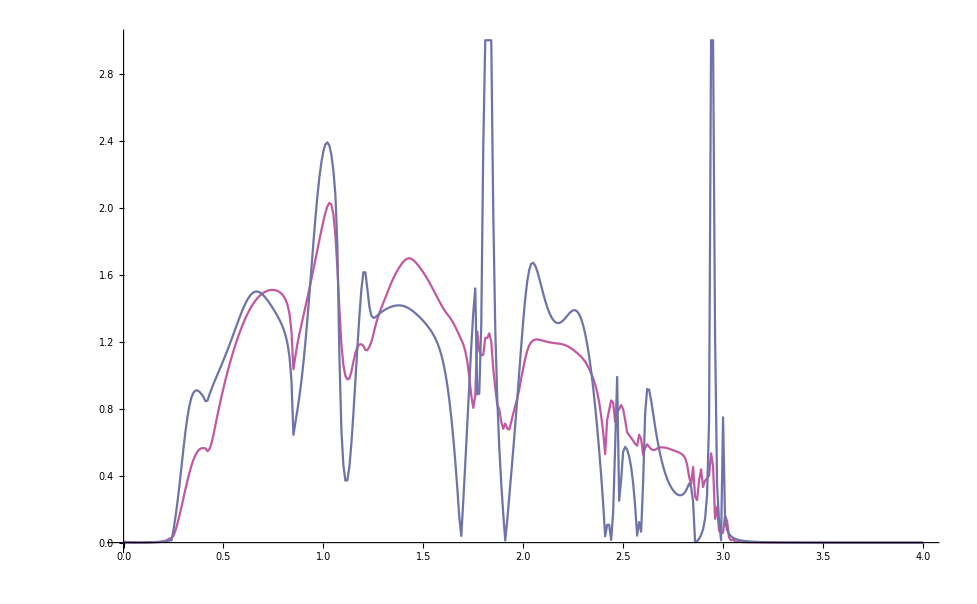

```mathematica
Show[ListPlot[final,Joined->True,PlotStyle->RGBColor[RandomReal[{0.2,0.8}],RandomReal[{0.0,0.5}],RandomReal[{0,01}]]],ListPlot[m3,Joined->True,PlotStyle->RGBColor[RandomReal[{0.2,0.8}],RandomReal[{0.0,0.5}],RandomReal[{0,01}]]],PlotRange->All]
```

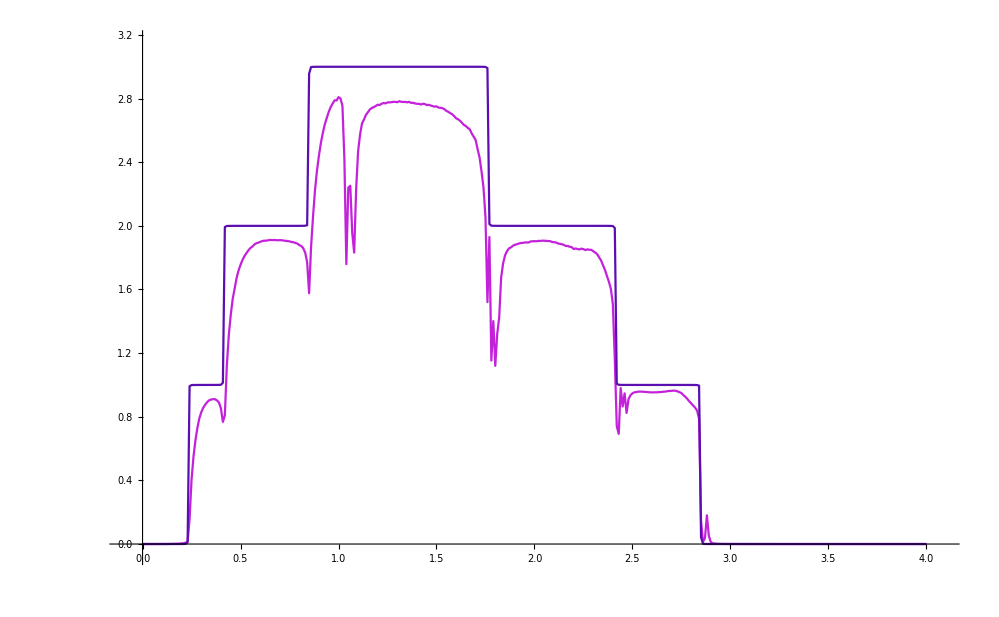

```mathematica
{{1,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- final[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,00,3}]/300]},{2,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,00,3}]/300]},{3,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,00,3}]/300]},{4,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,00,3}]/300]},{5,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,00,3}]/300]},{6,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,00,3}]/300]},{7,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,00,3}]/300]},{8,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,00,3}]/300]},{9.,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,00,3}]/300]},{10,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,00,3}]/300]},{11,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,00,3}]/300]},{12,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,00,3}]/300]},{13,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,00,3}]/300]},{14,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,00,3}]/300]},{15,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,00,3}]/300]},{16,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,00,3}]/300]},{17,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,00,3}]/300]},{18,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,00,3}]/300]},{19,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,00,3}]/300]},{20,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,00,3}]/300]},{21,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,00,3}]/300]},{22,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,00,3}]/300]},{23,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,00,3}]/300]},{24,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,00,3}]/300]},{25,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,00,3}]/300]},{26,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,00,3}]/300]},{27,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,00,3}]/300]},{28,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,00,3}]/300]},{29,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,00,3}]/300]},{30,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,00,3}]/300]},{31,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,00,3}]/300]},{32,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,00,3}]/300]},{33,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,00,3}]/300]},{34,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,00,3}]/300]},{35,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,00,3}]/300]},{36,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,00,3}]/300]},{37,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,00,3}]/300]},{38,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,00,3}]/300]},{39,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,00,3}]/300]},{40,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,00,3}]/300]},{41,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,00,3}]/300]},{42,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,00,3}]/300]},{43,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,00,3}]/300]},{44,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,00,3}]/300]},{45,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,00,3}]/300]},{46,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,00,3}]/300]},{47,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,00,3}]/300]},{48,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,00,3}]/300]}}
```

{{1,0.00403205},{2,0.00561787},{3,0.0049682},{4,0.00489025},{5,0.00627817},{6,0.00538396},{7,0.00444778},{8,0.00548991},{9.,0.00533139},{10,0.00511243},{11,0.00491835},{12,0.00436892},{13,0.00514428},{14,0.00576103},{15,0.00501856},{16,0.00532739},{17,0.0037871},{18,0.00543653},{19,0.00574157},{20,0.00446641},{21,0.00426927},{22,0.00408073},{23,0.00519459},{24,0.0035164},{25,0.00599075},{26,0.00448768},{27,0.00561857},{28,0.00440404},{29,0.00624624},{30,0.00641614},{31,0.00598904},{32,0.00531225},{33,0.00448624},{34,0.00474535},{35,0.00615187},{36,0.00364711},{37,0.00394545},{38,0.0044996},{39,0.00499755},{40,0.00528502},{41,0.00580207},{42,0.00476344},{43,0.00495694},{44,0.00555082},{45,0.00419074},{46,0.00591398},{47,0.00499837},{48,0.00400587}}

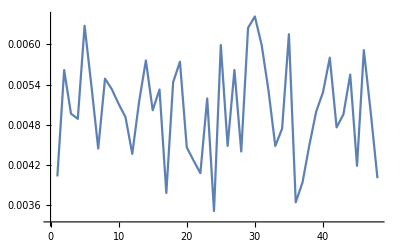

```mathematica
ListPlot[%589,Joined->True]
```

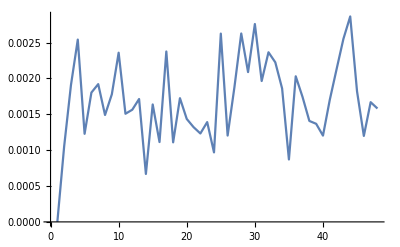

```mathematica
ListPlot[%399,Joined->True]
```

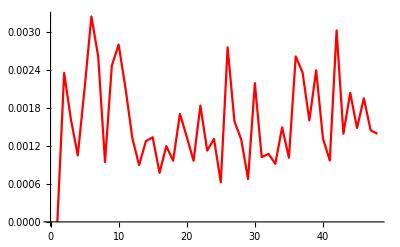

-Graphics-

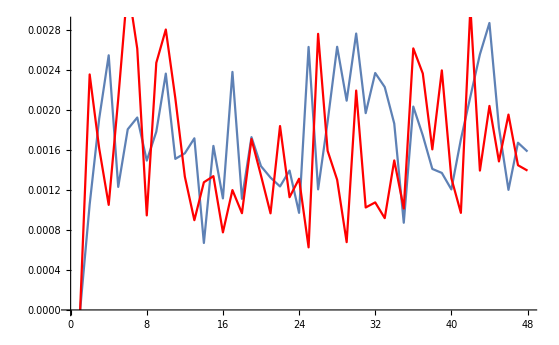

```mathematica
Show[%400,%401]
```

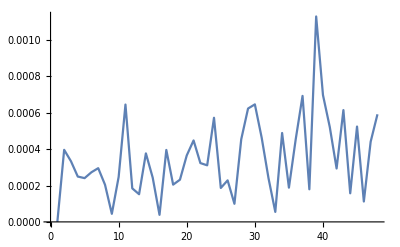

```mathematica
ListPlot[%397,Joined->True]
```

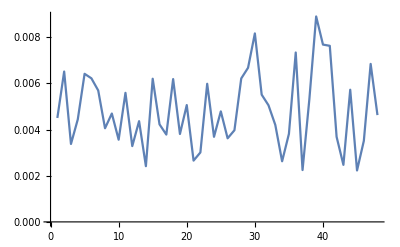

```mathematica
ListPlot[%355,Joined->True]
```

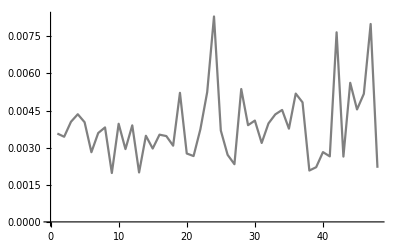

-Graphics-

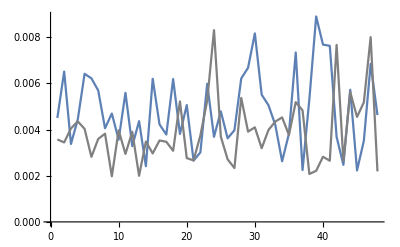

```mathematica
Show[%356,%357]
```

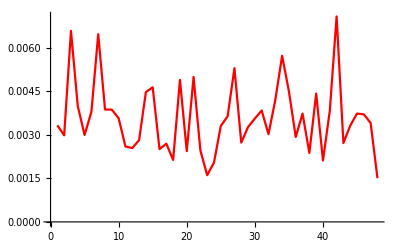

```mathematica
ListPlot[%178,Joined->True,PlotStyle->Red]
```

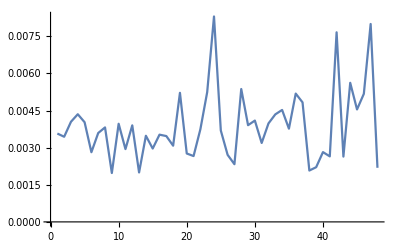

-Graphics-

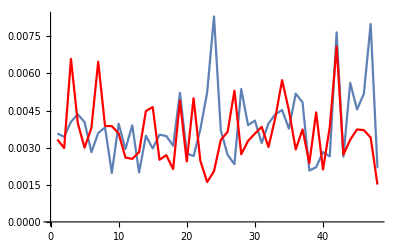

```mathematica
Show[%181,%180]
```

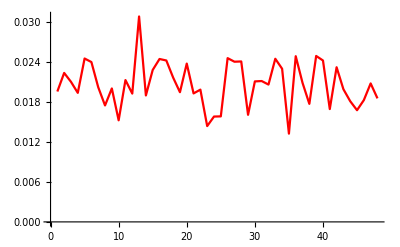

```mathematica
ListPlot[%170,Joined->True,PlotStyle->Red]
```

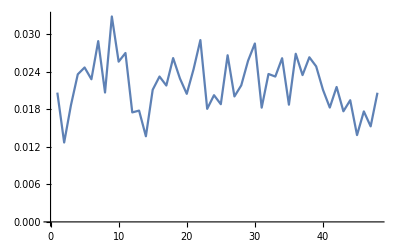

-Graphics-

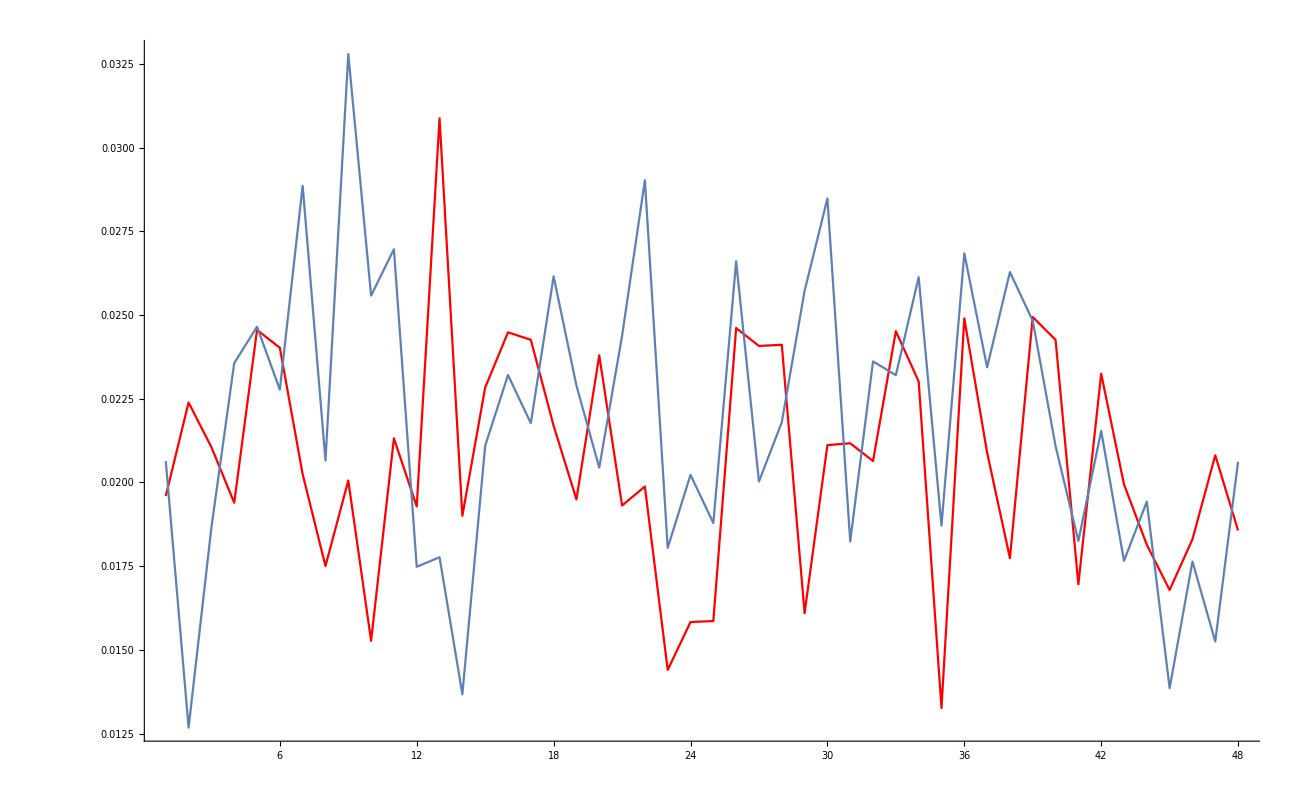

```mathematica
Show[%172,%176,PlotRange->All]
```

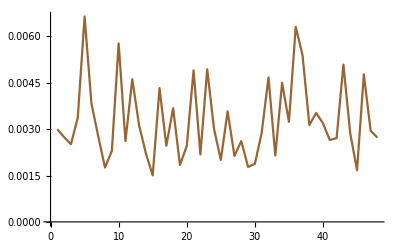

```mathematica
ListPlot[%713,Joined->True,PlotStyle->Brown]
```

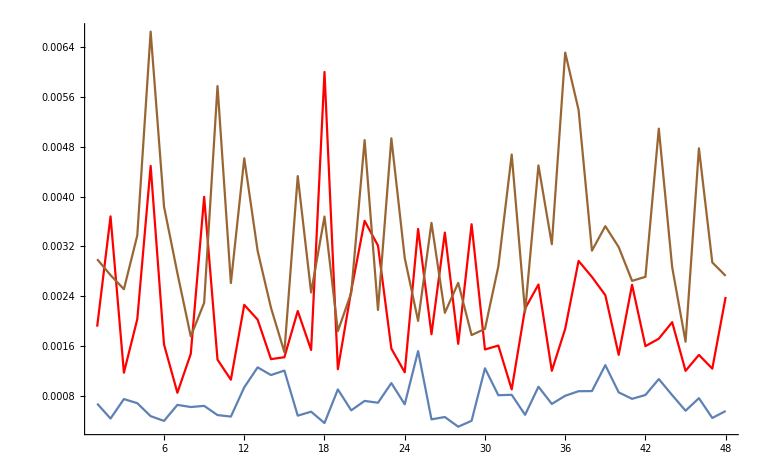

```mathematica
Show[%550,%715]
```

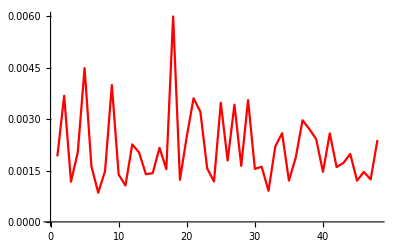

```mathematica
ListPlot[%546,Joined->True,PlotStyle->Red]
```

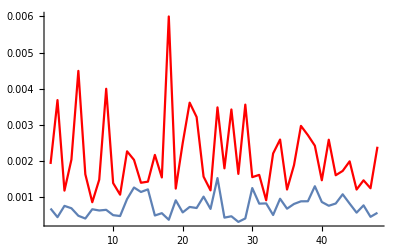

```mathematica
Show[%389,%548,PlotRange->All]
```

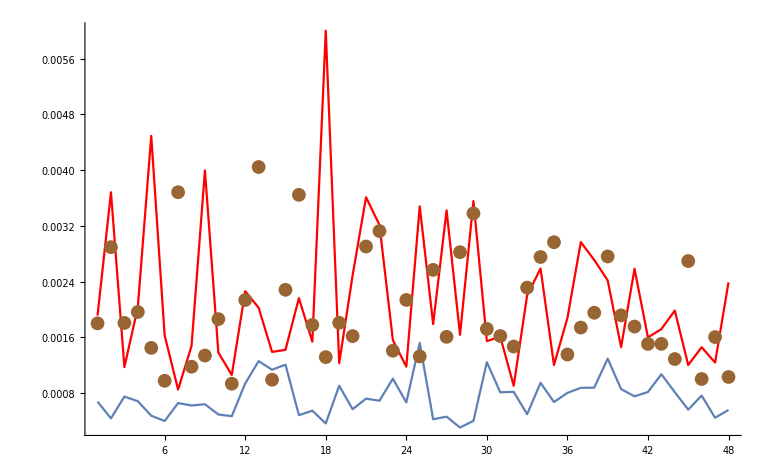

```mathematica
Show[%550,%719]
```

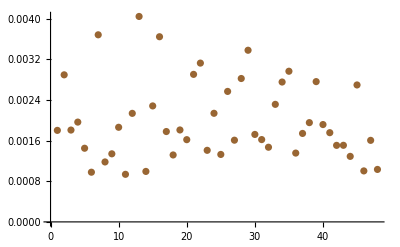

-Graphics-

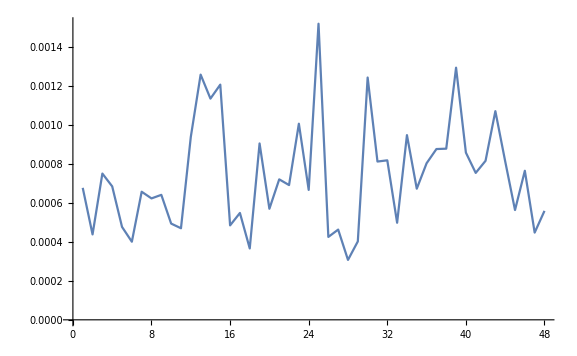

```mathematica
ListPlot[%388,Joined->True]
```

```mathematica
{{2,m2[[51,2]]},{3,m3[[51,2]]},{4,m4[[51,2]]},{5,m5[[51,2]]},{6,m6[[51,2]]},{7,m7[[51,2]]},{8,m8[[51,2]]},{9,n1[[51,2]]},{10,n2[[51,2]]},{11,n3[[51,2]]},{12,n4[[51,2]]},{13,n5[[51,2]]},{14,n6[[51,2]]},{15,n7[[51,2]]},{16,n8[[51,2]]},{17,o1[[51,2]]},{18,o2[[51,2]]},{19,o3[[51,2]]},{20,o4[[51,2]]},{21,o5[[51,2]]},{22,o6[[51,2]]},{23,o7[[51,2]]},{24,o8[[51,2]]},{25,p1[[51,2]]},{26,p2[[51,2]]},{27,p3[[51,2]]},{28,p4[[51,2]]},{29,p5[[51,2]]},{30,p6[[51,2]]},{31,p7[[51,2]]},{32,p8[[51,2]]},{33,q1[[51,2]]},{34,q2[[51,2]]},{35,q3[[51,2]]},{36,q4[[51,2]]},{37,q5[[51,2]]},{38,q6[[51,2]]},{39,q7[[51,2]]},{40,q8[[51,2]]},{41,r1[[51,2]]},{42,r2[[51,2]]},{43,r3[[51,2]]},{44,r4[[51,2]]},{45,r5[[51,2]]},{46,r6[[51,2]]},{47,r7[[51,2]]},{48,r8[[51,2]]}}
```

{{2,1.06139},{3,0.497408},{4,1.18438},{5,0.612374},{6,0.900647},{7,1.12181},{8,0.757101},{9,1.014},{10,1.2453},{11,1.05614},{12,1.44843},{13,0.925461},{14,1.23315},{15,0.917467},{16,0.794904},{17,1.59585},{18,0.774103},{19,1.18568},{20,1.24984},{21,0.98592},{22,1.01512},{23,0.910816},{24,0.833763},{25,0.949242},{26,1.11247},{27,1.02095},{28,0.910842},{29,1.00513},{30,1.05096},{31,1.5174},{32,1.02154},{33,0.467802},{34,1.31199},{35,1.79486},{36,0.897382},{37,1.2101},{38,1.25356},{39,1.13421},{40,1.64274},{41,1.0216},{42,0.962597},{43,0.582789},{44,1.29352},{45,1.33147},{46,0.954974},{47,1.13681},{48,1.18276}}

```mathematica
{Max[{Min/@%1341}],Min[{Min/@%1341}],final[[51,2]]}
```

{1.79486,0.467802,1.06178}

```mathematica
{{1,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- final[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{2,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{3,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{4,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{5,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{6,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{7,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{8,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{9.,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{10,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{11,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{12,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{13,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{14,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{15,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{16,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{17,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{18,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{19,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{20,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{21,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{22,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{23,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{24,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{25,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{26,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{27,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{28,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{29,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{30,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{31,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{32,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{33,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{34,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{35,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{36,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{37,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{38,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{39,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{40,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{41,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{42,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{43,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{44,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{45,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{46,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{47,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{48,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]}}
```

{{1,0.00894995},{2,0.0118374},{3,0.0103296},{4,0.0102712},{5,0.0149634},{6,0.00824916},{7,0.00583119},{8,0.00885035},{9.,0.0107378},{10,0.00955448},{11,0.00800381},{12,0.00870974},{13,0.00809498},{14,0.0104864},{15,0.00997579},{16,0.008192},{17,0.00581386},{18,0.0104635},{19,0.0126794},{20,0.00814343},{21,0.00681335},{22,0.0074559},{23,0.0102248},{24,0.00693472},{25,0.0153092},{26,0.0101251},{27,0.0106054},{28,0.00956514},{29,0.012512},{30,0.0142855},{31,0.013399},{32,0.00792899},{33,0.00842418},{34,0.00977106},{35,0.0107058},{36,0.00867197},{37,0.00777655},{38,0.00982044},{39,0.0102659},{40,0.0089557},{41,0.0128764},{42,0.0081332},{43,0.0108926},{44,0.0120405},{45,0.00753016},{46,0.0124982},{47,0.0105359},{48,0.00867274}}

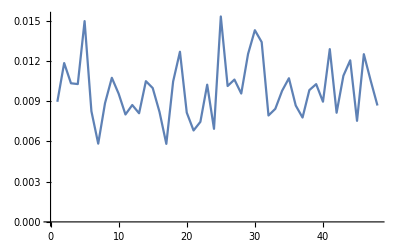

```mathematica
ListPlot[%593,Joined->True]
```

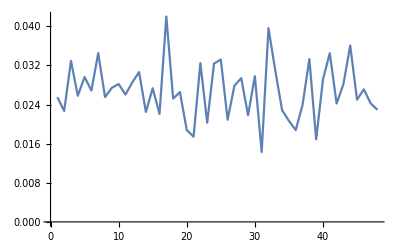

```mathematica
ListPlot[%359,Joined->True]
```

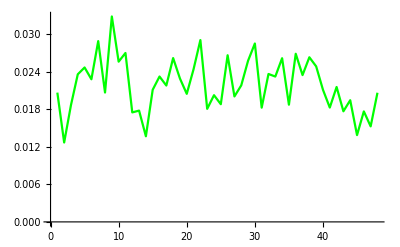

-Graphics-

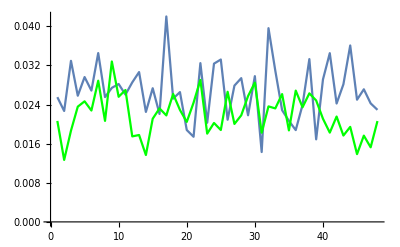

```mathematica
Show[%360,%361]
```

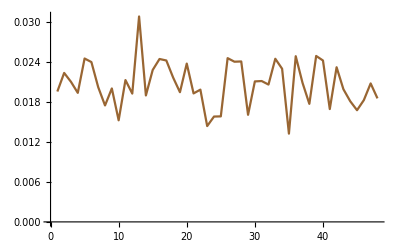

```mathematica
ListPlot[%183,Joined->True,PlotStyle->Brown]
```

```mathematica
{{1,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- final[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{2,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{3,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{4,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{5,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{6,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{7,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{8,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{9.,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{10,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{11,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{12,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{13,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{14,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{15,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{16,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{17,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{18,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{19,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{20,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{21,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{22,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{23,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{24,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{25,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{26,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{27,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{28,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{29,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{30,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{31,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{32,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{33,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{34,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{35,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{36,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{37,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{38,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{39,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{40,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{41,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{42,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{43,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{44,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{45,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{46,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{47,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]},{48,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,.84}]/84]}}
```

{{1,0.00182769},{2,0.00193128},{3,0.00135264},{4,0.00142619},{5,0.00267954},{6,0.00247267},{7,0.00182632},{8,0.00222915},{9.,0.00305136},{10,0.00371861},{11,0.00172262},{12,0.00156321},{13,0.00184407},{14,0.00284655},{15,0.00244036},{16,0.00215833},{17,0.00257111},{18,0.00224504},{19,0.00207508},{20,0.00179754},{21,0.00454834},{22,0.00150265},{23,0.00136131},{24,0.0011071},{25,0.00108244},{26,0.00121449},{27,0.00175459},{28,0.000899847},{29,0.00173815},{30,0.00133807},{31,0.00183255},{32,0.00222357},{33,0.00241945},{34,0.00163379},{35,0.00354218},{36,0.00134187},{37,0.00166692},{38,0.00225003},{39,0.00241727},{40,0.00359243},{41,0.00135328},{42,0.00114969},{43,0.00200501},{44,0.00172069},{45,0.00100804},{46,0.00148463},{47,0.0019308},{48,0.00125999}}

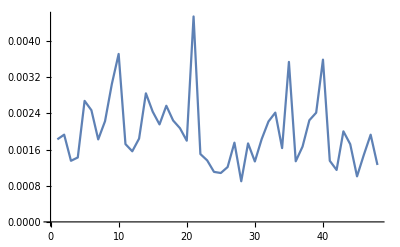

```mathematica
ListPlot[%591,Joined->True]
```

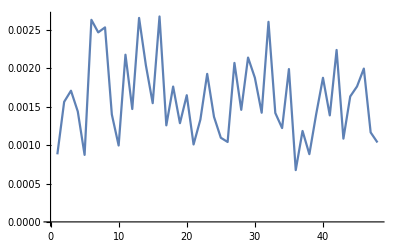

```mathematica
ListPlot[%587,Joined->True]
```

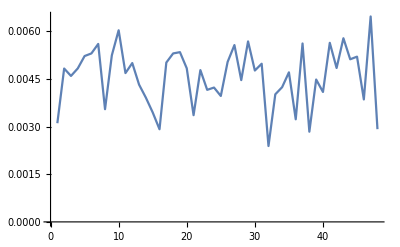

```mathematica
ListPlot[%363,Joined->True]
```

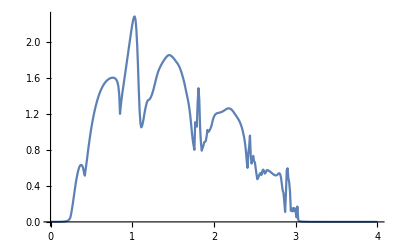

-Graphics-

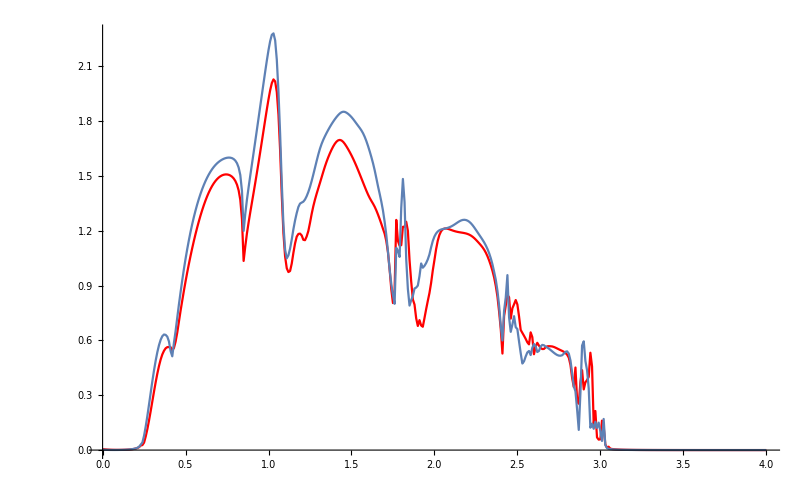

```mathematica
Show[ListLinePlot[final,PlotStyle->Red],%384,PlotRange->All]
```

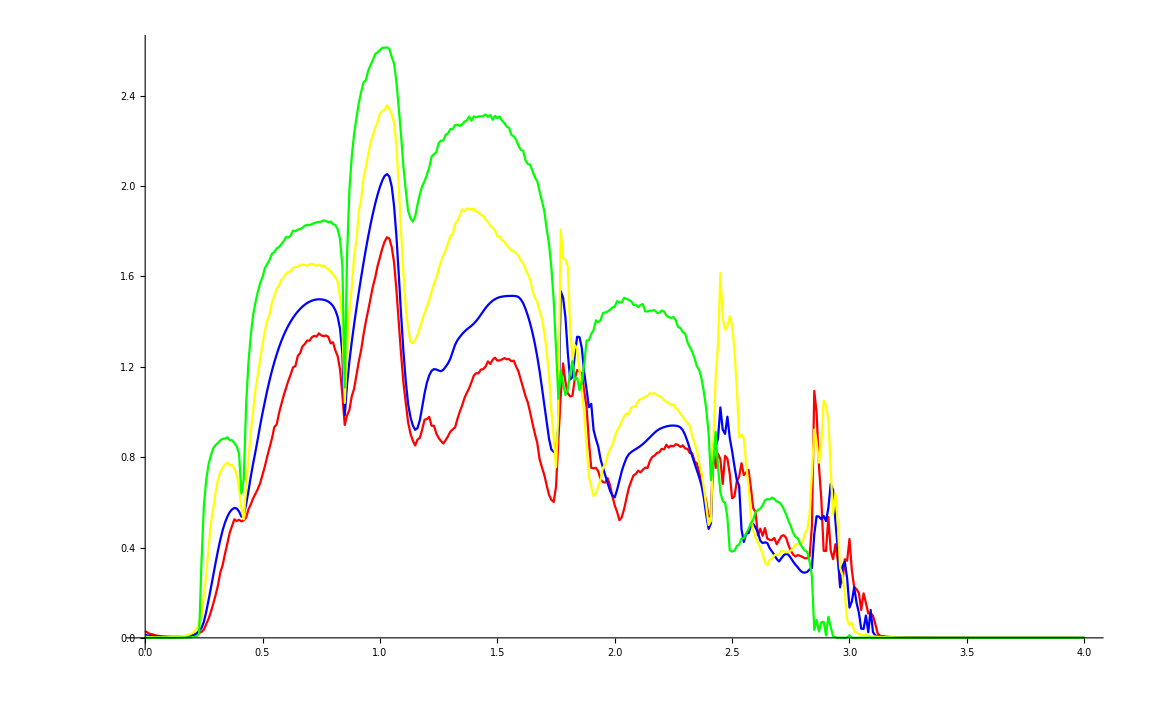

```mathematica
Show[ListLinePlot[Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/8imp/epis810.csv"],PlotStyle->Red],ListLinePlot[Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/6imp/epis610.csv"],PlotStyle->Blue],ListLinePlot[Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/4imp/epis410.csv"],PlotStyle->Yellow],ListLinePlot[Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/2imp/epis210.csv"],PlotStyle->Green],PlotRange->All]
```

```mathematica
{{1,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- final[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{2,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{3,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{4,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{5,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{6,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{7,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{8,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{9.,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{10,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{11,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{12,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{13,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{14,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{15,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{16,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{17,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{18,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{19,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{20,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{21,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{22,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{23,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{24,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{25,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{26,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{27,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{28,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{29,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{30,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{31,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{32,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{33,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{34,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{35,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{36,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r1[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{37,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r2[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{38,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r3[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{39,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r4[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{40,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r5[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{41,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r6[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{42,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r7[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{43,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- r8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{44,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- m8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{45,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- n8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{46,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- o8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{47,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- p8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]},{48,Module[{B1=Transpose[{m1[[1;;400]][[;;,1]],(m1[[1;;400,2]]- q8[[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0.85,1.76}]/91]}}
```

{{1,0.00894995},{2,0.0118374},{3,0.0103296},{4,0.0102712},{5,0.0149634},{6,0.00824916},{7,0.00583119},{8,0.00885035},{9.,0.0107378},{10,0.00955448},{11,0.00800381},{12,0.00870974},{13,0.00809498},{14,0.0104864},{15,0.00997579},{16,0.008192},{17,0.00581386},{18,0.0104635},{19,0.0126794},{20,0.00814343},{21,0.00681335},{22,0.0074559},{23,0.0102248},{24,0.00693472},{25,0.0153092},{26,0.0101251},{27,0.0106054},{28,0.00956514},{29,0.012512},{30,0.0142855},{31,0.013399},{32,0.00792899},{33,0.00842418},{34,0.00977106},{35,0.0107058},{36,0.00867197},{37,0.00777655},{38,0.00982044},{39,0.0102659},{40,0.0089557},{41,0.0128764},{42,0.0081332},{43,0.0108926},{44,0.0120405},{45,0.00753016},{46,0.0124982},{47,0.0105359},{48,0.00867274}}

```mathematica
ListPlot[%585,Joined->True]
```

-Graphics-

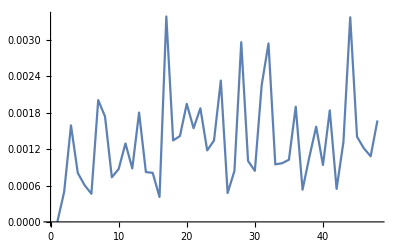

```mathematica
ListPlot[%403,Joined->True]
```

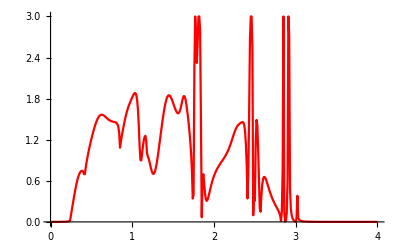

```mathematica
ListLinePlot[m4,PlotStyle->Red]
```

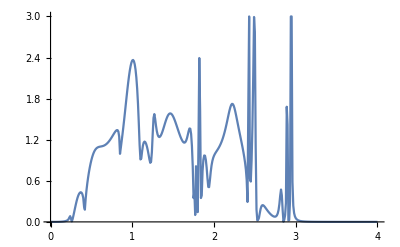

```mathematica
ListLinePlot[m7]
```

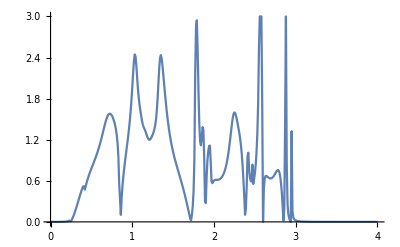

```mathematica
ListLinePlot[m8]
```

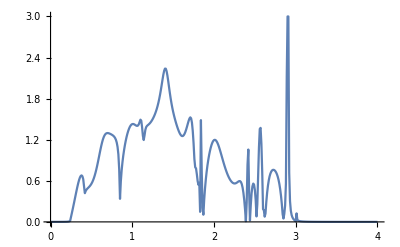

```mathematica
ListLinePlot[p8]
```

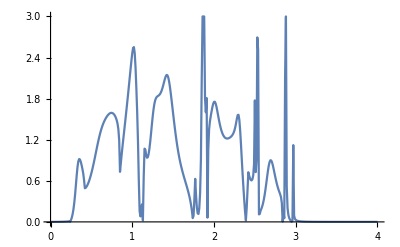

```mathematica
ListLinePlot[p4]
```

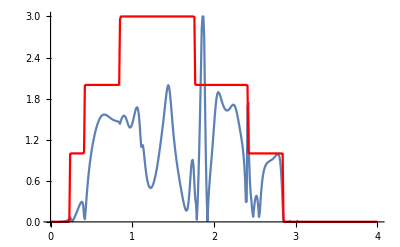

```mathematica
Show[ListLinePlot[q4],ListLinePlot[m1,PlotStyle->Red]]
```

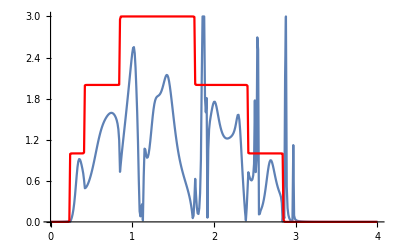

```mathematica
Show[ListLinePlot[p4],ListLinePlot[m1,PlotStyle->Red]]
```

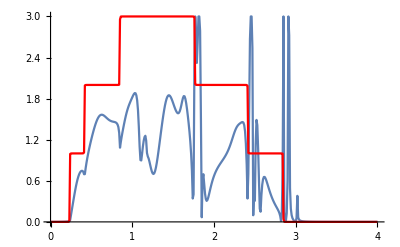

```mathematica
Show[ListLinePlot[m4],ListLinePlot[m1,PlotStyle->Red]]
```

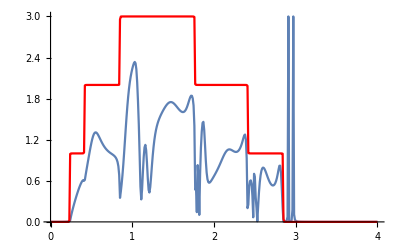

```mathematica
Show[ListLinePlot[n4],ListLinePlot[m1,PlotStyle->Red]]
```

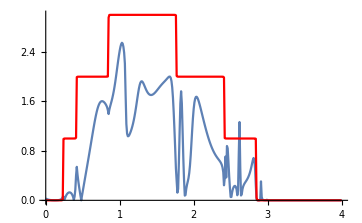

```mathematica
Show[ListLinePlot[r4],ListLinePlot[m1,PlotStyle->Red],PlotRange->All]
```

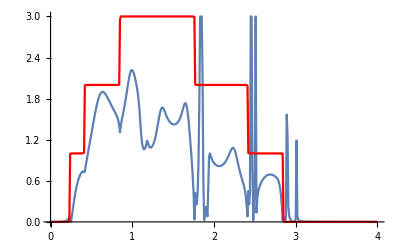

```mathematica
Show[ListLinePlot[r2],ListLinePlot[m1,PlotStyle->Red],PlotRange->All]
```

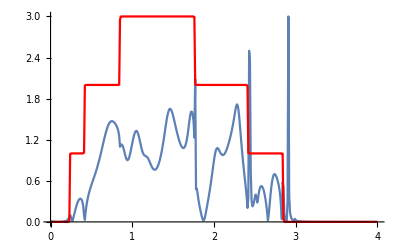

```mathematica
Show[ListLinePlot[r6],ListLinePlot[m1,PlotStyle->Red],PlotRange->All]
```

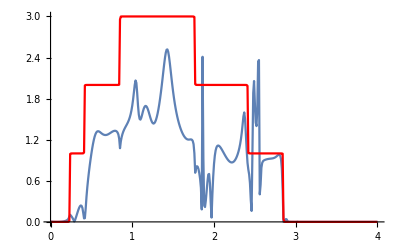

```mathematica
Show[ListLinePlot[p2],ListLinePlot[m1,PlotStyle->Red],PlotRange->All]
```

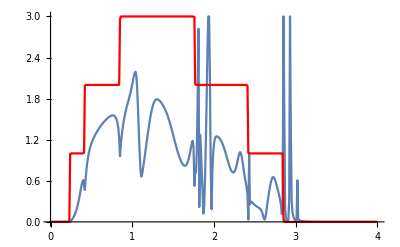

```mathematica
Show[ListLinePlot[p6],ListLinePlot[m1,PlotStyle->Red],PlotRange->All]
```

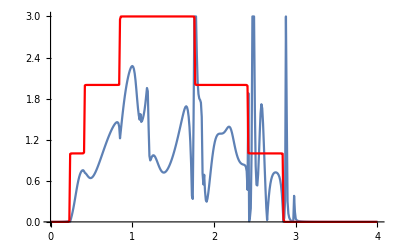

```mathematica
Show[ListLinePlot[p7],ListLinePlot[m1,PlotStyle->Red],PlotRange->All]
```